## Fit student correctness to various models

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bvds/Andes2/LogProcessing/moment-of-learning

```mathematica
data=Import["junk.csv"];
```

```mathematica
data=Import["guerra-summer-2011-kc-opps.csv"];
```

```mathematica
Take[data,5]
```

{{accel-at-rest,asu_9Q1920841f2ca4d1fasul1_c,md5:1da7d76bc3d524d51da47dde26ee8f95,0,1},{accel-constant-speed,asu_9Q1920841f2ca4d1fasul1_e,md5:e3e61859acb08ee896e06e1020f95a49,0},{accel-constant-speed,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,0},{apply-net-work,asu_9Q1920841f2ca4d1fasul1_e,md5:e66c328693800f93b41f13d97b78e19b,1},{apply-net-work,asu_9Q1920841f2ca4d1fasul1_e,md5:e9747bab59caf0446778cc6a65a8ac2e,0}}

```mathematica
logistic[n_,{mu_,b_}]:=1/(Exp[-b  n+mu]+1); (* this choice of parameters gives finite constraint region *)
step[n_,{nl_,pg_,ps_}]:=pg+(Sign[n-nl+1/2]+1) (1-ps-pg)/2;
bkt[n_,{b_,pg_,ps_}]:=1-ps-(1-ps-pg)*Exp[-b n]
```

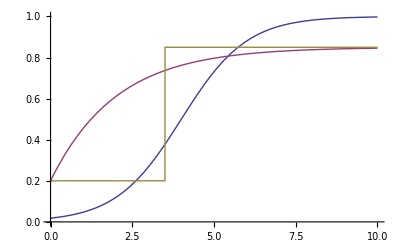

```mathematica
Plot[{logistic[x,{4,1}],bkt[x,{.5,.2,.15}],step[x,{4,.2,.15}]},{x,0,10},PlotRange->{0,1}]
```

```mathematica
stepFit[data_]:=Block[{best=-Infinity,lBest},Do[Block[{l0=Count[Take[data,i],0,1],l1=Count[Take[data,i],1,1],u0=Count[Drop[data,i],0,1],u1=Count[Drop[data,i],1,1],g,s,logLike=0},If[l0+l1>0,g=l1/(l0+l1);logLike+=If[l1>0,l1*Log[g],0]+If[l0>0,l0*Log[1-g],0]];If[u0+u1>0,s=u0/(u0+u1);logLike+=If[u0>0,u0*Log[s],0]+If[u1>0,u1*Log[1-s],0]];
	(*Print[{i,g,s,logLike}]; *)If[logLike>best,best=logLike;lBest=i]],{i,0,Length[data]-1}];If[Length[data]≥3,2*3-2*N[best]]]
```

```mathematica
logger[x_?NumberQ,params_]:= (* not used now. *)Which[0<x≤1,Log[x],x==0,(* NMaximize can't handle Infinity *)-10^50,True,Print["Invalid probability ",x," for ",params];If[x<0,-Infinity,0]]
logProb[model_,params_,data_]:=Sum[Log[If[data[[i]]==1,model[i-1,params],1-model[i,params]]],{i,Length[data]}]
maxer[model_,vars_,constraints_,data_]:=Which[
(* too few data points *)
Length[data]<Length[vars],Null,
(* All three functions can perfectly fit to all ones or zeros, but numerical fit is hard. *)
Count[data,0,1]==0 || Count[data,1,1]==0,2 Length[vars],True,
Block[{x=NMaximize[{logProb[model,vars,data],constraints[data]},vars,Method->{"RandomSearch",Method->"ConjugateGradient"}]},If[NumberQ[x[[1]]],2Length[vars]-2 x[[1]],Print[data,x];False]]]
```

```mathematica
logisticConstraints[x_]:=Block[{delta=15,ones=Position[x,1,1],zeros=Position[x,0,1]},mu≥Max[zeros[[-1,1]]*b,zeros[[1,1]]*b]-delta&& mu≤Min[ones[[1,1]]*b,ones[[-1,1]]*b]+delta&& b>-2 delta/Max[1,ones[[-1,1]]-zeros[[1,1]]] && b<2 delta/Max[1,zeros[[-1,1]]-ones[[1,1]]]]
```

```mathematica
bktConstraints[_]:=Block[{delta=15},pg≥Exp[-delta] && ps≥Exp[-delta] && pg≤1-Exp[-delta] && ps≤ 1-Exp[-delta] &&b≥0 && b<delta]
```

```mathematica
TableForm[Map[{#[[1]],stepFit[Drop[#,3]]}&,data]]
```

accel-constant-speed | Null
area-of-circle | Null
bernoulli | 6.
combo-magnification | Null
compo-general-case | 32.9921
compo-general-case-unknown | Null
compo-parallel-axis | 82.3817
compo-perpendicular | 39.1042
compo-z-axis | 16.585
compo-zero-vector | Null
continuity | Null
define-angle-between-lines | 6.
define-angular-frequency | 9.81909
define-area | Null
define-area-at | Null
define-charge | 28.4934
define-coef-friction | Null
define-compression | Null
define-current-thru | 17.4573
define-distance | 6.
define-distance-between | 9.81909
define-duration | 21.2763
define-electric-power-var | 6.
define-energy-var | Null
define-flux | Null
define-focal-length | 6.
define-frequency | 20.0453
define-grav-accel | 6.
define-image-distance | 8.77259
define-index-of-refraction | 6.
define-magnification | 6.
define-mass | 18.3152
define-mass-density | 6.
define-moment-of-inertia | 6.
define-object-distance | 6.
define-period-var | 8.77259
define-pressure | 15.5607
define-radius-of-circle | 6.
define-resistance-var | 14.9974
define-revolution-radius | 6.
define-shape-length | 6.
define-slit-separation | Null
define-speed | 8.77259
define-spring-constant | 8.77259
define-stored-energy-var | Null
define-turns | Null
define-voltage-across | 23.1989
define-volume | Null
define-wavelength | 6.
define-work | 8.77259
definition-syntax | 6.
draw-accel-free-fall | 6.
draw-accel-slow-down | Null
draw-accel-speed-up | 13.6382
draw-ang-accel | Null
draw-ang-accel-speed-up | Null
draw-ang-displacement-unknown | Null
draw-ang-momentum-rotating | 6.
draw-ang-velocity-rotating | 6.
draw-applied-force | 6.
draw-bfield-straight-current | 8.77259
draw-bforce-charge | 6.
draw-bforce-rhr-zero | Null
draw-bforce-unknown-velocity | Null
draw-body | 63.6435
draw-buoyant-force | Null
draw-centripetal-acceleration | 8.77259
draw-compo-form-axes | 17.4573
draw-coulomb-force-unknown | 6.
draw-displacement-given-dir | 8.77259
draw-displacement-straight | 10.4987
draw-displacement-unknown | Null
draw-displacement-zero | Null
draw-electric-force-given-field-dir | Null
draw-electric-force-given-field-unknown | Null
draw-energy-axes | 6.
draw-field-given-dir | 9.81909
draw-field-unknown | Null
draw-grav-force | Null
draw-impulse-given-momenta | Null
draw-kinetic-friction | Null
draw-line-given-dir | 13.6382
draw-line-unknown-dir | 6.
draw-momentum-at-rest | Null
draw-momentum-straight | 13.6382
draw-net-field-given-dir | 6.
draw-net-field-given-zero | Null
draw-net-field-unknown | Null
draw-net-force-from-accel | Null
draw-net-force-from-forces | Null
draw-net-force-unknown | Null
draw-normal | 10.4987
draw-point-efield-unknown | Null
draw-projection-axes | 6.
draw-relative-position | 8.77259
draw-relative-position-unknown | 6.
draw-spring-force | Null
draw-tension | 15.5607
draw-torque | Null
draw-unrotated-axes | 25.8748
draw-vector-aligned-axes | 6.
draw-velocity-at-rest | 9.81909
draw-velocity-curved | 14.9974
draw-velocity-curved-unknown | Null
draw-velocity-momentarily-at-rest | 10.4987
draw-velocity-straight | 39.5434
draw-velocity-straight-unknown | Null
draw-weight | 17.1624
draw-xy-vector-given-compos | Null
draw-z-axis-vector-given-compos | Null
equation-syntax | 30.356
equiv-resistance-parallel | 9.81909
equiv-resistance-series | 6.
kinetic-friction-law | Null
lens-combo | Null
lens-eqn | 9.81909
magnification-eqn | 6.
object-label | 6.
pendulum-oscillation | Null
pressure-at-open-to-atmosphere | 6.
pressure-force | Null
pressure-height-fluid | Null
sdd-constvel-compo | 9.81909
select-mc-answer | 65.5343
spring-law-compression | Null
spring-mass-oscillation | Null
write-ang-momentum | 6.
write-angle-direction-known-lines | 6.
write-archimedes | Null
write-average-rate-of-change | Null
write-cap-energy | Null
write-capacitance-definition | 6.
write-centripetal-accel | 6.
write-change-me | Null
write-charge-force-bfield | 8.77259
write-charge-force-bfield-mag | Null
write-charge-force-efield-compo | 6.
write-charge-force-efield-mag | Null
write-charge-same-caps-in-branch | Null
write-connected-accels | Null
write-cons-angmom | Null
write-cons-linmom-compo-join-split | Null
write-coulomb | Null
write-coulomb-compo | 6.
write-density | Null
write-electric-power | 8.77259
write-energy-cons | 6.
write-equality | 6.
write-faradays-law | Null
write-flux-constant-field | Null
write-flux-zero | Null
write-free-fall-accel | 6.
write-g-on-earth | Null
write-grav-energy | 11.004
write-harmonic-of | 6.
write-height-dy | Null
write-i-hoop-cm | Null
write-impulse-compo | Null
write-impulse-momentum-compo | Null
write-inside-solenoid-bfield | Null
write-junction-rule | Null
write-junction-rule-cap | Null
write-kinetic-energy | 15.5607
write-known-value-eqn | 235.968
write-linear-vel | Null
write-lk-no-s-compo | 14.3758
write-lk-no-t-compo | Null
write-lk-no-vf-compo | 10.4987
write-loop-rule-capacitors | 11.7416
write-loop-rule-resistors | 10.4987
write-mag-torque | Null
write-mass-compound | Null
write-momentum-compo | 6.
write-net-field-compo | Null
write-net-force-compo | 9.81909
write-nfl-compo | 12.7301
write-nsl-compo | 21.0257
write-nsl-rot-compo | Null
write-null-spring-energy | Null
write-ohms-law | 17.2868
write-period-circular | Null
write-point-charge-efield-compo | 6.
write-potential-energy | Null
write-right-triangle-tangent | Null
write-rk-no-s | Null
write-rk-no-vf | Null
write-sdd | 8.77259
write-single-loop-rule | Null
write-slit-interference | 6.
write-snells-law | Null
write-spring-energy | 8.77259
write-straight-wire-bfield | Null
write-sum-disp-compo | Null
write-sum-times | Null
write-tensions-equal | 6.
write-total-energy-top | 15.5607
write-transformer-power | Null
write-turns-per-length | Null
write-ug | Null
write-unit-vector-mag | Null
write-vector-magnitude | 6.
write-wave-speed-light | Null
write-wnc | Null
write-work | 6.
wt-law | 17.4573

Add AIC values for all sets with 3 or more points

```mathematica
aics=Apply[Plus,Map[If[Length[Drop[#,3]]≥3,{maxer[logistic,{mu,b},logisticConstraints,Drop[#,3]],maxer[bkt,{b,pg,ps},bktConstraints,Drop[#,3]],stepFit[Drop[#,3]]},0]&,data]]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Experimental`NumericalFunction::nnum: The function value Indeterminate is not a number at {b, mu} = {-30.`, -183.55689551959716`}.

General::stop: Further output of Experimental`NumericalFunction will be suppressed during this calculation.

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize will be suppressed during this calculation.

$Aborted

```mathematica
TableForm[allValues=Map[{#[[1]],#[[3]],Length[Drop[#,3]],Print[#[[1]]," logistic ",#[[3]]];maxer[logistic,{mu,b},logisticConstraints,Drop[#,3]],Print[#[[1]]," bkt ",#[[3]]];maxer[bkt,{b,pg,ps},bktConstraints,Drop[#,3]],stepFit[Drop[#,3]]}&,data]]
```

accel-at-rest logistic md5:1da7d76bc3d524d51da47dde26ee8f95

accel-at-rest bkt md5:1da7d76bc3d524d51da47dde26ee8f95

accel-constant-speed logistic md5:e3e61859acb08ee896e06e1020f95a49

accel-constant-speed bkt md5:e3e61859acb08ee896e06e1020f95a49

accel-constant-speed logistic md5:b50efcf571b671cf01b499841c66daf2

accel-constant-speed bkt md5:b50efcf571b671cf01b499841c66daf2

apply-net-work logistic md5:e66c328693800f93b41f13d97b78e19b

apply-net-work bkt md5:e66c328693800f93b41f13d97b78e19b

apply-net-work logistic md5:e9747bab59caf0446778cc6a65a8ac2e

apply-net-work bkt md5:e9747bab59caf0446778cc6a65a8ac2e

area-of-circle logistic md5:5e8914eb96d8caf02138110b93b5add5

area-of-circle bkt md5:5e8914eb96d8caf02138110b93b5add5

area-of-circle logistic md5:98deb41457bbea23b29b480e9530ad7c

area-of-circle bkt md5:98deb41457bbea23b29b480e9530ad7c

area-of-circle logistic md5:e9747bab59caf0446778cc6a65a8ac2e

area-of-circle bkt md5:e9747bab59caf0446778cc6a65a8ac2e

area-of-circle logistic md5:e3e61859acb08ee896e06e1020f95a49

area-of-circle bkt md5:e3e61859acb08ee896e06e1020f95a49

area-of-circle logistic md5:1da7d76bc3d524d51da47dde26ee8f95

area-of-circle bkt md5:1da7d76bc3d524d51da47dde26ee8f95

area-of-circle logistic md5:a38723384afd4471b62218d16045a11d

area-of-circle bkt md5:a38723384afd4471b62218d16045a11d

area-of-circle logistic md5:55108dec2fb88e9c2af83be92d0520de

area-of-circle bkt md5:55108dec2fb88e9c2af83be92d0520de

area-of-circle logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

area-of-circle bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

area-of-circle logistic md5:b50efcf571b671cf01b499841c66daf2

area-of-circle bkt md5:b50efcf571b671cf01b499841c66daf2

bernoulli logistic md5:a38723384afd4471b62218d16045a11d

bernoulli bkt md5:a38723384afd4471b62218d16045a11d

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

bernoulli logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

bernoulli bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

bernoulli logistic md5:55108dec2fb88e9c2af83be92d0520de

bernoulli bkt md5:55108dec2fb88e9c2af83be92d0520de

bernoulli logistic md5:b50efcf571b671cf01b499841c66daf2

bernoulli bkt md5:b50efcf571b671cf01b499841c66daf2

bernoulli logistic md5:1da7d76bc3d524d51da47dde26ee8f95

bernoulli bkt md5:1da7d76bc3d524d51da47dde26ee8f95

bernoulli logistic md5:e66c328693800f93b41f13d97b78e19b

bernoulli bkt md5:e66c328693800f93b41f13d97b78e19b

bernoulli logistic md5:e3e61859acb08ee896e06e1020f95a49

bernoulli bkt md5:e3e61859acb08ee896e06e1020f95a49

bernoulli logistic md5:e9747bab59caf0446778cc6a65a8ac2e

bernoulli bkt md5:e9747bab59caf0446778cc6a65a8ac2e

bernoulli logistic md5:8a075e35a0daf7e231f60497d036689a

bernoulli bkt md5:8a075e35a0daf7e231f60497d036689a

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

combo-magnification logistic md5:a38723384afd4471b62218d16045a11d

combo-magnification bkt md5:a38723384afd4471b62218d16045a11d

combo-magnification logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

combo-magnification bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

combo-magnification logistic md5:b50efcf571b671cf01b499841c66daf2

combo-magnification bkt md5:b50efcf571b671cf01b499841c66daf2

combo-magnification logistic md5:1da7d76bc3d524d51da47dde26ee8f95

combo-magnification bkt md5:1da7d76bc3d524d51da47dde26ee8f95

combo-magnification logistic md5:55108dec2fb88e9c2af83be92d0520de

combo-magnification bkt md5:55108dec2fb88e9c2af83be92d0520de

combo-magnification logistic md5:e66c328693800f93b41f13d97b78e19b

combo-magnification bkt md5:e66c328693800f93b41f13d97b78e19b

combo-magnification logistic md5:e3e61859acb08ee896e06e1020f95a49

combo-magnification bkt md5:e3e61859acb08ee896e06e1020f95a49

combo-magnification logistic md5:e9747bab59caf0446778cc6a65a8ac2e

combo-magnification bkt md5:e9747bab59caf0446778cc6a65a8ac2e

combo-magnification logistic md5:8a075e35a0daf7e231f60497d036689a

combo-magnification bkt md5:8a075e35a0daf7e231f60497d036689a

compo-general-case logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

compo-general-case bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

compo-general-case logistic md5:fd9e6b9f34db6df883c666a7c86820b4

compo-general-case bkt md5:fd9e6b9f34db6df883c666a7c86820b4

compo-general-case logistic md5:a38723384afd4471b62218d16045a11d

compo-general-case bkt md5:a38723384afd4471b62218d16045a11d

compo-general-case logistic md5:b50efcf571b671cf01b499841c66daf2

compo-general-case bkt md5:b50efcf571b671cf01b499841c66daf2

compo-general-case logistic md5:1da7d76bc3d524d51da47dde26ee8f95

compo-general-case bkt md5:1da7d76bc3d524d51da47dde26ee8f95

compo-general-case logistic md5:55108dec2fb88e9c2af83be92d0520de

compo-general-case bkt md5:55108dec2fb88e9c2af83be92d0520de

compo-general-case logistic md5:5e8914eb96d8caf02138110b93b5add5

compo-general-case bkt md5:5e8914eb96d8caf02138110b93b5add5

compo-general-case logistic md5:e3e61859acb08ee896e06e1020f95a49

compo-general-case bkt md5:e3e61859acb08ee896e06e1020f95a49

compo-general-case logistic md5:98deb41457bbea23b29b480e9530ad7c

compo-general-case bkt md5:98deb41457bbea23b29b480e9530ad7c

compo-general-case logistic md5:e9747bab59caf0446778cc6a65a8ac2e

compo-general-case bkt md5:e9747bab59caf0446778cc6a65a8ac2e

compo-general-case logistic md5:e66c328693800f93b41f13d97b78e19b

compo-general-case bkt md5:e66c328693800f93b41f13d97b78e19b

compo-general-case logistic md5:8a075e35a0daf7e231f60497d036689a

compo-general-case bkt md5:8a075e35a0daf7e231f60497d036689a

compo-general-case-unknown logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

compo-general-case-unknown bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

compo-general-case-unknown logistic md5:b50efcf571b671cf01b499841c66daf2

compo-general-case-unknown bkt md5:b50efcf571b671cf01b499841c66daf2

compo-general-case-unknown logistic md5:e3e61859acb08ee896e06e1020f95a49

Experimental`NumericalFunction::nnum: The function value Indeterminate is not a number at {b, mu} = {-30.`, -183.55689551959716`}.

General::stop: Further output of Experimental`NumericalFunction will be suppressed during this calculation.

compo-general-case-unknown bkt md5:e3e61859acb08ee896e06e1020f95a49

compo-general-case-unknown logistic md5:98deb41457bbea23b29b480e9530ad7c

compo-general-case-unknown bkt md5:98deb41457bbea23b29b480e9530ad7c

compo-general-case-unknown logistic md5:e9747bab59caf0446778cc6a65a8ac2e

compo-general-case-unknown bkt md5:e9747bab59caf0446778cc6a65a8ac2e

compo-general-case-unknown logistic md5:e66c328693800f93b41f13d97b78e19b

compo-general-case-unknown bkt md5:e66c328693800f93b41f13d97b78e19b

compo-parallel-axis logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

compo-parallel-axis bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

compo-parallel-axis logistic md5:b50efcf571b671cf01b499841c66daf2

compo-parallel-axis bkt md5:b50efcf571b671cf01b499841c66daf2

compo-parallel-axis logistic md5:1da7d76bc3d524d51da47dde26ee8f95

compo-parallel-axis bkt md5:1da7d76bc3d524d51da47dde26ee8f95

compo-parallel-axis logistic md5:a38723384afd4471b62218d16045a11d

compo-parallel-axis bkt md5:a38723384afd4471b62218d16045a11d

compo-parallel-axis logistic md5:55108dec2fb88e9c2af83be92d0520de

compo-parallel-axis bkt md5:55108dec2fb88e9c2af83be92d0520de

compo-parallel-axis logistic md5:5e8914eb96d8caf02138110b93b5add5

compo-parallel-axis bkt md5:5e8914eb96d8caf02138110b93b5add5

compo-parallel-axis logistic md5:e3e61859acb08ee896e06e1020f95a49

compo-parallel-axis bkt md5:e3e61859acb08ee896e06e1020f95a49

compo-parallel-axis logistic md5:98deb41457bbea23b29b480e9530ad7c

compo-parallel-axis bkt md5:98deb41457bbea23b29b480e9530ad7c

compo-parallel-axis logistic md5:e9747bab59caf0446778cc6a65a8ac2e

compo-parallel-axis bkt md5:e9747bab59caf0446778cc6a65a8ac2e

compo-parallel-axis logistic md5:e66c328693800f93b41f13d97b78e19b

compo-parallel-axis bkt md5:e66c328693800f93b41f13d97b78e19b

compo-parallel-axis logistic md5:8a075e35a0daf7e231f60497d036689a

compo-parallel-axis bkt md5:8a075e35a0daf7e231f60497d036689a

compo-perpendicular logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

compo-perpendicular bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

compo-perpendicular logistic md5:b50efcf571b671cf01b499841c66daf2

compo-perpendicular bkt md5:b50efcf571b671cf01b499841c66daf2

compo-perpendicular logistic md5:1da7d76bc3d524d51da47dde26ee8f95

compo-perpendicular bkt md5:1da7d76bc3d524d51da47dde26ee8f95

compo-perpendicular logistic md5:a38723384afd4471b62218d16045a11d

compo-perpendicular bkt md5:a38723384afd4471b62218d16045a11d

compo-perpendicular logistic md5:55108dec2fb88e9c2af83be92d0520de

compo-perpendicular bkt md5:55108dec2fb88e9c2af83be92d0520de

compo-perpendicular logistic md5:5e8914eb96d8caf02138110b93b5add5

compo-perpendicular bkt md5:5e8914eb96d8caf02138110b93b5add5

compo-perpendicular logistic md5:e3e61859acb08ee896e06e1020f95a49

compo-perpendicular bkt md5:e3e61859acb08ee896e06e1020f95a49

compo-perpendicular logistic md5:98deb41457bbea23b29b480e9530ad7c

compo-perpendicular bkt md5:98deb41457bbea23b29b480e9530ad7c

compo-perpendicular logistic md5:e9747bab59caf0446778cc6a65a8ac2e

compo-perpendicular bkt md5:e9747bab59caf0446778cc6a65a8ac2e

compo-perpendicular logistic md5:e66c328693800f93b41f13d97b78e19b

compo-perpendicular bkt md5:e66c328693800f93b41f13d97b78e19b

compo-perpendicular logistic md5:8a075e35a0daf7e231f60497d036689a

compo-perpendicular bkt md5:8a075e35a0daf7e231f60497d036689a

compo-z-axis logistic md5:98deb41457bbea23b29b480e9530ad7c

compo-z-axis bkt md5:98deb41457bbea23b29b480e9530ad7c

compo-z-axis logistic md5:e3e61859acb08ee896e06e1020f95a49

compo-z-axis bkt md5:e3e61859acb08ee896e06e1020f95a49

compo-z-axis logistic md5:5e8914eb96d8caf02138110b93b5add5

compo-z-axis bkt md5:5e8914eb96d8caf02138110b93b5add5

compo-z-axis logistic md5:e66c328693800f93b41f13d97b78e19b

compo-z-axis bkt md5:e66c328693800f93b41f13d97b78e19b

compo-z-axis logistic md5:e9747bab59caf0446778cc6a65a8ac2e

compo-z-axis bkt md5:e9747bab59caf0446778cc6a65a8ac2e

compo-z-axis logistic md5:8a075e35a0daf7e231f60497d036689a

compo-z-axis bkt md5:8a075e35a0daf7e231f60497d036689a

compo-z-axis logistic md5:a38723384afd4471b62218d16045a11d

compo-z-axis bkt md5:a38723384afd4471b62218d16045a11d

compo-z-axis logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

compo-z-axis bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

compo-z-axis logistic md5:55108dec2fb88e9c2af83be92d0520de

compo-z-axis bkt md5:55108dec2fb88e9c2af83be92d0520de

compo-z-axis logistic md5:b50efcf571b671cf01b499841c66daf2

compo-z-axis bkt md5:b50efcf571b671cf01b499841c66daf2

compo-z-axis logistic md5:1da7d76bc3d524d51da47dde26ee8f95

compo-z-axis bkt md5:1da7d76bc3d524d51da47dde26ee8f95

compo-zero-vector logistic md5:5e8914eb96d8caf02138110b93b5add5

compo-zero-vector bkt md5:5e8914eb96d8caf02138110b93b5add5

compo-zero-vector logistic md5:e3e61859acb08ee896e06e1020f95a49

compo-zero-vector bkt md5:e3e61859acb08ee896e06e1020f95a49

compo-zero-vector logistic md5:98deb41457bbea23b29b480e9530ad7c

compo-zero-vector bkt md5:98deb41457bbea23b29b480e9530ad7c

compo-zero-vector logistic md5:e66c328693800f93b41f13d97b78e19b

compo-zero-vector bkt md5:e66c328693800f93b41f13d97b78e19b

compo-zero-vector logistic md5:a38723384afd4471b62218d16045a11d

compo-zero-vector bkt md5:a38723384afd4471b62218d16045a11d

compo-zero-vector logistic md5:55108dec2fb88e9c2af83be92d0520de

compo-zero-vector bkt md5:55108dec2fb88e9c2af83be92d0520de

compo-zero-vector logistic md5:b50efcf571b671cf01b499841c66daf2

compo-zero-vector bkt md5:b50efcf571b671cf01b499841c66daf2

compo-zero-vector logistic md5:1da7d76bc3d524d51da47dde26ee8f95

compo-zero-vector bkt md5:1da7d76bc3d524d51da47dde26ee8f95

continuity logistic md5:a38723384afd4471b62218d16045a11d

continuity bkt md5:a38723384afd4471b62218d16045a11d

continuity logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

continuity bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

continuity logistic md5:55108dec2fb88e9c2af83be92d0520de

continuity bkt md5:55108dec2fb88e9c2af83be92d0520de

continuity logistic md5:b50efcf571b671cf01b499841c66daf2

continuity bkt md5:b50efcf571b671cf01b499841c66daf2

continuity logistic md5:1da7d76bc3d524d51da47dde26ee8f95

continuity bkt md5:1da7d76bc3d524d51da47dde26ee8f95

continuity logistic md5:e66c328693800f93b41f13d97b78e19b

continuity bkt md5:e66c328693800f93b41f13d97b78e19b

continuity logistic md5:e3e61859acb08ee896e06e1020f95a49

continuity bkt md5:e3e61859acb08ee896e06e1020f95a49

continuity logistic md5:e9747bab59caf0446778cc6a65a8ac2e

continuity bkt md5:e9747bab59caf0446778cc6a65a8ac2e

continuity logistic md5:8a075e35a0daf7e231f60497d036689a

continuity bkt md5:8a075e35a0daf7e231f60497d036689a

define-angle-between-lines logistic md5:a38723384afd4471b62218d16045a11d

define-angle-between-lines bkt md5:a38723384afd4471b62218d16045a11d

define-angle-between-lines logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-angle-between-lines bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-angle-between-lines logistic md5:b50efcf571b671cf01b499841c66daf2

define-angle-between-lines bkt md5:b50efcf571b671cf01b499841c66daf2

define-angle-between-lines logistic md5:55108dec2fb88e9c2af83be92d0520de

define-angle-between-lines bkt md5:55108dec2fb88e9c2af83be92d0520de

define-angle-between-lines logistic md5:e66c328693800f93b41f13d97b78e19b

define-angle-between-lines bkt md5:e66c328693800f93b41f13d97b78e19b

define-angle-between-lines logistic md5:e3e61859acb08ee896e06e1020f95a49

define-angle-between-lines bkt md5:e3e61859acb08ee896e06e1020f95a49

define-angle-between-lines logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-angle-between-lines bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-angle-between-lines logistic md5:8a075e35a0daf7e231f60497d036689a

define-angle-between-lines bkt md5:8a075e35a0daf7e231f60497d036689a

define-angle-between-vectors logistic md5:e3e61859acb08ee896e06e1020f95a49

define-angle-between-vectors bkt md5:e3e61859acb08ee896e06e1020f95a49

define-angle-between-vectors logistic md5:e66c328693800f93b41f13d97b78e19b

define-angle-between-vectors bkt md5:e66c328693800f93b41f13d97b78e19b

define-angular-frequency logistic md5:e3e61859acb08ee896e06e1020f95a49

define-angular-frequency bkt md5:e3e61859acb08ee896e06e1020f95a49

define-angular-frequency logistic md5:b50efcf571b671cf01b499841c66daf2

define-angular-frequency bkt md5:b50efcf571b671cf01b499841c66daf2

define-area logistic md5:a38723384afd4471b62218d16045a11d

define-area bkt md5:a38723384afd4471b62218d16045a11d

define-area logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-area bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-area logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-area bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-area logistic md5:b50efcf571b671cf01b499841c66daf2

define-area bkt md5:b50efcf571b671cf01b499841c66daf2

define-area logistic md5:55108dec2fb88e9c2af83be92d0520de

define-area bkt md5:55108dec2fb88e9c2af83be92d0520de

define-area logistic md5:e66c328693800f93b41f13d97b78e19b

define-area bkt md5:e66c328693800f93b41f13d97b78e19b

define-area logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-area bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-area logistic md5:e3e61859acb08ee896e06e1020f95a49

define-area bkt md5:e3e61859acb08ee896e06e1020f95a49

define-area logistic md5:8a075e35a0daf7e231f60497d036689a

define-area bkt md5:8a075e35a0daf7e231f60497d036689a

define-area-at logistic md5:a38723384afd4471b62218d16045a11d

define-area-at bkt md5:a38723384afd4471b62218d16045a11d

define-area-at logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-area-at bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-area-at logistic md5:55108dec2fb88e9c2af83be92d0520de

define-area-at bkt md5:55108dec2fb88e9c2af83be92d0520de

define-area-at logistic md5:b50efcf571b671cf01b499841c66daf2

define-area-at bkt md5:b50efcf571b671cf01b499841c66daf2

define-area-at logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-area-at bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-area-at logistic md5:e66c328693800f93b41f13d97b78e19b

define-area-at bkt md5:e66c328693800f93b41f13d97b78e19b

define-area-at logistic md5:e3e61859acb08ee896e06e1020f95a49

define-area-at bkt md5:e3e61859acb08ee896e06e1020f95a49

define-area-at logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-area-at bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-area-at logistic md5:8a075e35a0daf7e231f60497d036689a

define-area-at bkt md5:8a075e35a0daf7e231f60497d036689a

define-atmosphere-var logistic md5:e66c328693800f93b41f13d97b78e19b

define-atmosphere-var bkt md5:e66c328693800f93b41f13d97b78e19b

define-capacitance-var logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-capacitance-var bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-capacitance-var logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-capacitance-var bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-capacitance-var logistic md5:e66c328693800f93b41f13d97b78e19b

define-capacitance-var bkt md5:e66c328693800f93b41f13d97b78e19b

define-capacitance-var logistic md5:e3e61859acb08ee896e06e1020f95a49

define-capacitance-var bkt md5:e3e61859acb08ee896e06e1020f95a49

define-charge logistic md5:e3e61859acb08ee896e06e1020f95a49

define-charge bkt md5:e3e61859acb08ee896e06e1020f95a49

define-charge logistic md5:5e8914eb96d8caf02138110b93b5add5

define-charge bkt md5:5e8914eb96d8caf02138110b93b5add5

define-charge logistic md5:98deb41457bbea23b29b480e9530ad7c

define-charge bkt md5:98deb41457bbea23b29b480e9530ad7c

define-charge logistic md5:e66c328693800f93b41f13d97b78e19b

define-charge bkt md5:e66c328693800f93b41f13d97b78e19b

define-charge logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-charge bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-charge logistic md5:8a075e35a0daf7e231f60497d036689a

define-charge bkt md5:8a075e35a0daf7e231f60497d036689a

define-charge logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-charge bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-charge logistic md5:a38723384afd4471b62218d16045a11d

define-charge bkt md5:a38723384afd4471b62218d16045a11d

define-charge logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-charge bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-charge logistic md5:55108dec2fb88e9c2af83be92d0520de

define-charge bkt md5:55108dec2fb88e9c2af83be92d0520de

define-charge logistic md5:b50efcf571b671cf01b499841c66daf2

define-charge bkt md5:b50efcf571b671cf01b499841c66daf2

define-coef-friction logistic md5:98deb41457bbea23b29b480e9530ad7c

define-coef-friction bkt md5:98deb41457bbea23b29b480e9530ad7c

define-coef-friction logistic md5:e3e61859acb08ee896e06e1020f95a49

define-coef-friction bkt md5:e3e61859acb08ee896e06e1020f95a49

define-coef-friction logistic md5:e66c328693800f93b41f13d97b78e19b

define-coef-friction bkt md5:e66c328693800f93b41f13d97b78e19b

define-coef-friction logistic md5:5e8914eb96d8caf02138110b93b5add5

define-coef-friction bkt md5:5e8914eb96d8caf02138110b93b5add5

define-coef-friction logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-coef-friction bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-coef-friction logistic md5:a38723384afd4471b62218d16045a11d

define-coef-friction bkt md5:a38723384afd4471b62218d16045a11d

define-coef-friction logistic md5:b50efcf571b671cf01b499841c66daf2

define-coef-friction bkt md5:b50efcf571b671cf01b499841c66daf2

define-coef-friction logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-coef-friction bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-coef-friction logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-coef-friction bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-compression logistic md5:a38723384afd4471b62218d16045a11d

define-compression bkt md5:a38723384afd4471b62218d16045a11d

define-compression logistic md5:b50efcf571b671cf01b499841c66daf2

define-compression bkt md5:b50efcf571b671cf01b499841c66daf2

define-compression logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-compression bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-compression logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-compression bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-compression logistic md5:55108dec2fb88e9c2af83be92d0520de

define-compression bkt md5:55108dec2fb88e9c2af83be92d0520de

define-compression logistic md5:e3e61859acb08ee896e06e1020f95a49

define-compression bkt md5:e3e61859acb08ee896e06e1020f95a49

define-compression logistic md5:5e8914eb96d8caf02138110b93b5add5

define-compression bkt md5:5e8914eb96d8caf02138110b93b5add5

define-compression logistic md5:e66c328693800f93b41f13d97b78e19b

define-compression bkt md5:e66c328693800f93b41f13d97b78e19b

define-compression logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-compression bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-compression logistic md5:98deb41457bbea23b29b480e9530ad7c

define-compression bkt md5:98deb41457bbea23b29b480e9530ad7c

define-current-thru logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-current-thru bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-current-thru logistic md5:a38723384afd4471b62218d16045a11d

define-current-thru bkt md5:a38723384afd4471b62218d16045a11d

define-current-thru logistic md5:b50efcf571b671cf01b499841c66daf2

define-current-thru bkt md5:b50efcf571b671cf01b499841c66daf2

define-current-thru logistic md5:55108dec2fb88e9c2af83be92d0520de

define-current-thru bkt md5:55108dec2fb88e9c2af83be92d0520de

define-current-thru logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-current-thru bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-current-thru logistic md5:e66c328693800f93b41f13d97b78e19b

define-current-thru bkt md5:e66c328693800f93b41f13d97b78e19b

define-current-thru logistic md5:8a075e35a0daf7e231f60497d036689a

define-current-thru bkt md5:8a075e35a0daf7e231f60497d036689a

define-current-thru logistic md5:e3e61859acb08ee896e06e1020f95a49

define-current-thru bkt md5:e3e61859acb08ee896e06e1020f95a49

define-current-thru logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-current-thru bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-distance logistic md5:a38723384afd4471b62218d16045a11d

define-distance bkt md5:a38723384afd4471b62218d16045a11d

define-distance logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-distance bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-distance logistic md5:55108dec2fb88e9c2af83be92d0520de

define-distance bkt md5:55108dec2fb88e9c2af83be92d0520de

define-distance logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-distance bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-distance logistic md5:b50efcf571b671cf01b499841c66daf2

define-distance bkt md5:b50efcf571b671cf01b499841c66daf2

define-distance logistic md5:98deb41457bbea23b29b480e9530ad7c

define-distance bkt md5:98deb41457bbea23b29b480e9530ad7c

define-distance logistic md5:e3e61859acb08ee896e06e1020f95a49

define-distance bkt md5:e3e61859acb08ee896e06e1020f95a49

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize will be suppressed during this calculation.

define-distance logistic md5:e66c328693800f93b41f13d97b78e19b

define-distance bkt md5:e66c328693800f93b41f13d97b78e19b

define-distance logistic md5:5e8914eb96d8caf02138110b93b5add5

define-distance bkt md5:5e8914eb96d8caf02138110b93b5add5

define-distance logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-distance bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-distance logistic md5:8a075e35a0daf7e231f60497d036689a

define-distance bkt md5:8a075e35a0daf7e231f60497d036689a

define-distance-between logistic md5:e66c328693800f93b41f13d97b78e19b

define-distance-between bkt md5:e66c328693800f93b41f13d97b78e19b

define-distance-between logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-distance-between bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-distance-between logistic md5:e3e61859acb08ee896e06e1020f95a49

define-distance-between bkt md5:e3e61859acb08ee896e06e1020f95a49

define-distance-between logistic md5:8a075e35a0daf7e231f60497d036689a

define-distance-between bkt md5:8a075e35a0daf7e231f60497d036689a

define-distance-between logistic md5:a38723384afd4471b62218d16045a11d

define-distance-between bkt md5:a38723384afd4471b62218d16045a11d

define-distance-between logistic md5:b50efcf571b671cf01b499841c66daf2

define-distance-between bkt md5:b50efcf571b671cf01b499841c66daf2

define-distance-between logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-distance-between bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-distance-between logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-distance-between bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-distance-between logistic md5:55108dec2fb88e9c2af83be92d0520de

define-distance-between bkt md5:55108dec2fb88e9c2af83be92d0520de

define-duration logistic md5:a38723384afd4471b62218d16045a11d

define-duration bkt md5:a38723384afd4471b62218d16045a11d

define-duration logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-duration bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-duration logistic md5:55108dec2fb88e9c2af83be92d0520de

define-duration bkt md5:55108dec2fb88e9c2af83be92d0520de

define-duration logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-duration bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-duration logistic md5:b50efcf571b671cf01b499841c66daf2

define-duration bkt md5:b50efcf571b671cf01b499841c66daf2

define-duration logistic md5:98deb41457bbea23b29b480e9530ad7c

define-duration bkt md5:98deb41457bbea23b29b480e9530ad7c

define-duration logistic md5:e3e61859acb08ee896e06e1020f95a49

define-duration bkt md5:e3e61859acb08ee896e06e1020f95a49

define-duration logistic md5:e66c328693800f93b41f13d97b78e19b

define-duration bkt md5:e66c328693800f93b41f13d97b78e19b

define-duration logistic md5:5e8914eb96d8caf02138110b93b5add5

define-duration bkt md5:5e8914eb96d8caf02138110b93b5add5

define-duration logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-duration bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-duration logistic md5:8a075e35a0daf7e231f60497d036689a

define-duration bkt md5:8a075e35a0daf7e231f60497d036689a

define-electric-power-var logistic md5:e66c328693800f93b41f13d97b78e19b

define-electric-power-var bkt md5:e66c328693800f93b41f13d97b78e19b

define-electric-power-var logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-electric-power-var bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-electric-power-var logistic md5:8a075e35a0daf7e231f60497d036689a

define-electric-power-var bkt md5:8a075e35a0daf7e231f60497d036689a

define-electric-power-var logistic md5:a38723384afd4471b62218d16045a11d

define-electric-power-var bkt md5:a38723384afd4471b62218d16045a11d

define-electric-power-var logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-electric-power-var bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-electric-power-var logistic md5:b50efcf571b671cf01b499841c66daf2

define-electric-power-var bkt md5:b50efcf571b671cf01b499841c66daf2

define-electric-power-var logistic md5:55108dec2fb88e9c2af83be92d0520de

define-electric-power-var bkt md5:55108dec2fb88e9c2af83be92d0520de

define-electric-power-var logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-electric-power-var bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-energy-var logistic md5:e66c328693800f93b41f13d97b78e19b

define-energy-var bkt md5:e66c328693800f93b41f13d97b78e19b

define-energy-var logistic md5:e3e61859acb08ee896e06e1020f95a49

define-energy-var bkt md5:e3e61859acb08ee896e06e1020f95a49

define-energy-var logistic md5:8a075e35a0daf7e231f60497d036689a

define-energy-var bkt md5:8a075e35a0daf7e231f60497d036689a

define-energy-var logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-energy-var bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-energy-var logistic md5:b50efcf571b671cf01b499841c66daf2

define-energy-var bkt md5:b50efcf571b671cf01b499841c66daf2

define-flux logistic md5:a38723384afd4471b62218d16045a11d

define-flux bkt md5:a38723384afd4471b62218d16045a11d

define-flux logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-flux bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-flux logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-flux bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-flux logistic md5:b50efcf571b671cf01b499841c66daf2

define-flux bkt md5:b50efcf571b671cf01b499841c66daf2

define-flux logistic md5:55108dec2fb88e9c2af83be92d0520de

define-flux bkt md5:55108dec2fb88e9c2af83be92d0520de

define-flux logistic md5:e66c328693800f93b41f13d97b78e19b

define-flux bkt md5:e66c328693800f93b41f13d97b78e19b

define-flux logistic md5:e3e61859acb08ee896e06e1020f95a49

define-flux bkt md5:e3e61859acb08ee896e06e1020f95a49

define-flux logistic md5:8a075e35a0daf7e231f60497d036689a

define-flux bkt md5:8a075e35a0daf7e231f60497d036689a

define-focal-length logistic md5:a38723384afd4471b62218d16045a11d

define-focal-length bkt md5:a38723384afd4471b62218d16045a11d

define-focal-length logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-focal-length bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-focal-length logistic md5:b50efcf571b671cf01b499841c66daf2

define-focal-length bkt md5:b50efcf571b671cf01b499841c66daf2

define-focal-length logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-focal-length bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-focal-length logistic md5:55108dec2fb88e9c2af83be92d0520de

define-focal-length bkt md5:55108dec2fb88e9c2af83be92d0520de

define-focal-length logistic md5:8a075e35a0daf7e231f60497d036689a

define-focal-length bkt md5:8a075e35a0daf7e231f60497d036689a

define-focal-length logistic md5:e66c328693800f93b41f13d97b78e19b

define-focal-length bkt md5:e66c328693800f93b41f13d97b78e19b

define-focal-length logistic md5:e3e61859acb08ee896e06e1020f95a49

define-focal-length bkt md5:e3e61859acb08ee896e06e1020f95a49

define-focal-length logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-focal-length bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-frequency logistic md5:5e8914eb96d8caf02138110b93b5add5

define-frequency bkt md5:5e8914eb96d8caf02138110b93b5add5

define-frequency logistic md5:98deb41457bbea23b29b480e9530ad7c

define-frequency bkt md5:98deb41457bbea23b29b480e9530ad7c

define-frequency logistic md5:e66c328693800f93b41f13d97b78e19b

define-frequency bkt md5:e66c328693800f93b41f13d97b78e19b

define-frequency logistic md5:e3e61859acb08ee896e06e1020f95a49

define-frequency bkt md5:e3e61859acb08ee896e06e1020f95a49

define-frequency logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-frequency bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-frequency logistic md5:a38723384afd4471b62218d16045a11d

define-frequency bkt md5:a38723384afd4471b62218d16045a11d

define-frequency logistic md5:b50efcf571b671cf01b499841c66daf2

define-frequency bkt md5:b50efcf571b671cf01b499841c66daf2

define-frequency logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-frequency bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-frequency logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-frequency bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-frequency logistic md5:55108dec2fb88e9c2af83be92d0520de

define-frequency bkt md5:55108dec2fb88e9c2af83be92d0520de

define-grav-accel logistic md5:e66c328693800f93b41f13d97b78e19b

define-grav-accel bkt md5:e66c328693800f93b41f13d97b78e19b

define-grav-accel logistic md5:5e8914eb96d8caf02138110b93b5add5

define-grav-accel bkt md5:5e8914eb96d8caf02138110b93b5add5

define-grav-accel logistic md5:98deb41457bbea23b29b480e9530ad7c

define-grav-accel bkt md5:98deb41457bbea23b29b480e9530ad7c

define-grav-accel logistic md5:e3e61859acb08ee896e06e1020f95a49

define-grav-accel bkt md5:e3e61859acb08ee896e06e1020f95a49

define-grav-accel logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-grav-accel bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-grav-accel logistic md5:a38723384afd4471b62218d16045a11d

define-grav-accel bkt md5:a38723384afd4471b62218d16045a11d

define-grav-accel logistic md5:b50efcf571b671cf01b499841c66daf2

define-grav-accel bkt md5:b50efcf571b671cf01b499841c66daf2

define-grav-accel logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-grav-accel bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-grav-accel logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-grav-accel bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-grav-accel logistic md5:55108dec2fb88e9c2af83be92d0520de

define-grav-accel bkt md5:55108dec2fb88e9c2af83be92d0520de

define-height logistic md5:e66c328693800f93b41f13d97b78e19b

define-height bkt md5:e66c328693800f93b41f13d97b78e19b

define-height logistic md5:8a075e35a0daf7e231f60497d036689a

define-height bkt md5:8a075e35a0daf7e231f60497d036689a

define-image-distance logistic md5:a38723384afd4471b62218d16045a11d

define-image-distance bkt md5:a38723384afd4471b62218d16045a11d

define-image-distance logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-image-distance bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-image-distance logistic md5:b50efcf571b671cf01b499841c66daf2

define-image-distance bkt md5:b50efcf571b671cf01b499841c66daf2

define-image-distance logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-image-distance bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-image-distance logistic md5:55108dec2fb88e9c2af83be92d0520de

define-image-distance bkt md5:55108dec2fb88e9c2af83be92d0520de

define-image-distance logistic md5:8a075e35a0daf7e231f60497d036689a

define-image-distance bkt md5:8a075e35a0daf7e231f60497d036689a

define-image-distance logistic md5:e66c328693800f93b41f13d97b78e19b

define-image-distance bkt md5:e66c328693800f93b41f13d97b78e19b

define-image-distance logistic md5:e3e61859acb08ee896e06e1020f95a49

define-image-distance bkt md5:e3e61859acb08ee896e06e1020f95a49

define-image-distance logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-image-distance bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-index-of-refraction logistic md5:a38723384afd4471b62218d16045a11d

define-index-of-refraction bkt md5:a38723384afd4471b62218d16045a11d

define-index-of-refraction logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-index-of-refraction bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-index-of-refraction logistic md5:b50efcf571b671cf01b499841c66daf2

define-index-of-refraction bkt md5:b50efcf571b671cf01b499841c66daf2

define-index-of-refraction logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-index-of-refraction bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-index-of-refraction logistic md5:55108dec2fb88e9c2af83be92d0520de

define-index-of-refraction bkt md5:55108dec2fb88e9c2af83be92d0520de

define-index-of-refraction logistic md5:e66c328693800f93b41f13d97b78e19b

define-index-of-refraction bkt md5:e66c328693800f93b41f13d97b78e19b

define-index-of-refraction logistic md5:e3e61859acb08ee896e06e1020f95a49

define-index-of-refraction bkt md5:e3e61859acb08ee896e06e1020f95a49

define-index-of-refraction logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-index-of-refraction bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-index-of-refraction logistic md5:8a075e35a0daf7e231f60497d036689a

define-index-of-refraction bkt md5:8a075e35a0daf7e231f60497d036689a

define-magnification logistic md5:a38723384afd4471b62218d16045a11d

define-magnification bkt md5:a38723384afd4471b62218d16045a11d

define-magnification logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-magnification bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-magnification logistic md5:b50efcf571b671cf01b499841c66daf2

define-magnification bkt md5:b50efcf571b671cf01b499841c66daf2

define-magnification logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-magnification bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-magnification logistic md5:55108dec2fb88e9c2af83be92d0520de

define-magnification bkt md5:55108dec2fb88e9c2af83be92d0520de

define-magnification logistic md5:e66c328693800f93b41f13d97b78e19b

define-magnification bkt md5:e66c328693800f93b41f13d97b78e19b

define-magnification logistic md5:8a075e35a0daf7e231f60497d036689a

define-magnification bkt md5:8a075e35a0daf7e231f60497d036689a

define-magnification logistic md5:e3e61859acb08ee896e06e1020f95a49

define-magnification bkt md5:e3e61859acb08ee896e06e1020f95a49

define-magnification logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-magnification bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-mass logistic md5:e3e61859acb08ee896e06e1020f95a49

define-mass bkt md5:e3e61859acb08ee896e06e1020f95a49

define-mass logistic md5:5e8914eb96d8caf02138110b93b5add5

define-mass bkt md5:5e8914eb96d8caf02138110b93b5add5

define-mass logistic md5:98deb41457bbea23b29b480e9530ad7c

define-mass bkt md5:98deb41457bbea23b29b480e9530ad7c

define-mass logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-mass bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-mass logistic md5:e66c328693800f93b41f13d97b78e19b

define-mass bkt md5:e66c328693800f93b41f13d97b78e19b

define-mass logistic md5:8a075e35a0daf7e231f60497d036689a

define-mass bkt md5:8a075e35a0daf7e231f60497d036689a

define-mass logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-mass bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-mass logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-mass bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-mass logistic md5:a38723384afd4471b62218d16045a11d

define-mass bkt md5:a38723384afd4471b62218d16045a11d

define-mass logistic md5:55108dec2fb88e9c2af83be92d0520de

define-mass bkt md5:55108dec2fb88e9c2af83be92d0520de

define-mass logistic md5:b50efcf571b671cf01b499841c66daf2

define-mass bkt md5:b50efcf571b671cf01b499841c66daf2

define-mass-density logistic md5:5e8914eb96d8caf02138110b93b5add5

define-mass-density bkt md5:5e8914eb96d8caf02138110b93b5add5

define-mass-density logistic md5:e66c328693800f93b41f13d97b78e19b

define-mass-density bkt md5:e66c328693800f93b41f13d97b78e19b

define-mass-density logistic md5:98deb41457bbea23b29b480e9530ad7c

define-mass-density bkt md5:98deb41457bbea23b29b480e9530ad7c

define-mass-density logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-mass-density bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-mass-density logistic md5:e3e61859acb08ee896e06e1020f95a49

define-mass-density bkt md5:e3e61859acb08ee896e06e1020f95a49

define-mass-density logistic md5:8a075e35a0daf7e231f60497d036689a

define-mass-density bkt md5:8a075e35a0daf7e231f60497d036689a

define-mass-density logistic md5:a38723384afd4471b62218d16045a11d

define-mass-density bkt md5:a38723384afd4471b62218d16045a11d

define-mass-density logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-mass-density bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-mass-density logistic md5:55108dec2fb88e9c2af83be92d0520de

define-mass-density bkt md5:55108dec2fb88e9c2af83be92d0520de

define-mass-density logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-mass-density bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-mass-density logistic md5:b50efcf571b671cf01b499841c66daf2

define-mass-density bkt md5:b50efcf571b671cf01b499841c66daf2

define-moment-of-inertia logistic md5:a38723384afd4471b62218d16045a11d

define-moment-of-inertia bkt md5:a38723384afd4471b62218d16045a11d

define-moment-of-inertia logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-moment-of-inertia bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-moment-of-inertia logistic md5:55108dec2fb88e9c2af83be92d0520de

define-moment-of-inertia bkt md5:55108dec2fb88e9c2af83be92d0520de

define-moment-of-inertia logistic md5:b50efcf571b671cf01b499841c66daf2

define-moment-of-inertia bkt md5:b50efcf571b671cf01b499841c66daf2

define-moment-of-inertia logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-moment-of-inertia bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-moment-of-inertia logistic md5:5e8914eb96d8caf02138110b93b5add5

define-moment-of-inertia bkt md5:5e8914eb96d8caf02138110b93b5add5

define-moment-of-inertia logistic md5:98deb41457bbea23b29b480e9530ad7c

define-moment-of-inertia bkt md5:98deb41457bbea23b29b480e9530ad7c

define-moment-of-inertia logistic md5:e66c328693800f93b41f13d97b78e19b

define-moment-of-inertia bkt md5:e66c328693800f93b41f13d97b78e19b

define-moment-of-inertia logistic md5:e3e61859acb08ee896e06e1020f95a49

define-moment-of-inertia bkt md5:e3e61859acb08ee896e06e1020f95a49

define-moment-of-inertia logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-moment-of-inertia bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-moment-of-inertia logistic md5:8a075e35a0daf7e231f60497d036689a

define-moment-of-inertia bkt md5:8a075e35a0daf7e231f60497d036689a

define-net-work logistic md5:e66c328693800f93b41f13d97b78e19b

define-net-work bkt md5:e66c328693800f93b41f13d97b78e19b

define-net-work logistic md5:e3e61859acb08ee896e06e1020f95a49

define-net-work bkt md5:e3e61859acb08ee896e06e1020f95a49

define-net-work logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-net-work bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-object-distance logistic md5:a38723384afd4471b62218d16045a11d

define-object-distance bkt md5:a38723384afd4471b62218d16045a11d

define-object-distance logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-object-distance bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-object-distance logistic md5:b50efcf571b671cf01b499841c66daf2

define-object-distance bkt md5:b50efcf571b671cf01b499841c66daf2

define-object-distance logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-object-distance bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-object-distance logistic md5:55108dec2fb88e9c2af83be92d0520de

define-object-distance bkt md5:55108dec2fb88e9c2af83be92d0520de

define-object-distance logistic md5:8a075e35a0daf7e231f60497d036689a

define-object-distance bkt md5:8a075e35a0daf7e231f60497d036689a

define-object-distance logistic md5:e66c328693800f93b41f13d97b78e19b

define-object-distance bkt md5:e66c328693800f93b41f13d97b78e19b

define-object-distance logistic md5:e3e61859acb08ee896e06e1020f95a49

define-object-distance bkt md5:e3e61859acb08ee896e06e1020f95a49

define-object-distance logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-object-distance bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-period-var logistic md5:e3e61859acb08ee896e06e1020f95a49

define-period-var bkt md5:e3e61859acb08ee896e06e1020f95a49

define-period-var logistic md5:e66c328693800f93b41f13d97b78e19b

define-period-var bkt md5:e66c328693800f93b41f13d97b78e19b

define-period-var logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-period-var bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-period-var logistic md5:98deb41457bbea23b29b480e9530ad7c

define-period-var bkt md5:98deb41457bbea23b29b480e9530ad7c

define-period-var logistic md5:5e8914eb96d8caf02138110b93b5add5

define-period-var bkt md5:5e8914eb96d8caf02138110b93b5add5

define-period-var logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-period-var bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-period-var logistic md5:a38723384afd4471b62218d16045a11d

define-period-var bkt md5:a38723384afd4471b62218d16045a11d

define-period-var logistic md5:55108dec2fb88e9c2af83be92d0520de

define-period-var bkt md5:55108dec2fb88e9c2af83be92d0520de

define-period-var logistic md5:b50efcf571b671cf01b499841c66daf2

define-period-var bkt md5:b50efcf571b671cf01b499841c66daf2

define-period-var logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-period-var bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-pressure logistic md5:5e8914eb96d8caf02138110b93b5add5

define-pressure bkt md5:5e8914eb96d8caf02138110b93b5add5

define-pressure logistic md5:e66c328693800f93b41f13d97b78e19b

define-pressure bkt md5:e66c328693800f93b41f13d97b78e19b

define-pressure logistic md5:98deb41457bbea23b29b480e9530ad7c

define-pressure bkt md5:98deb41457bbea23b29b480e9530ad7c

define-pressure logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-pressure bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-pressure logistic md5:e3e61859acb08ee896e06e1020f95a49

define-pressure bkt md5:e3e61859acb08ee896e06e1020f95a49

define-pressure logistic md5:8a075e35a0daf7e231f60497d036689a

define-pressure bkt md5:8a075e35a0daf7e231f60497d036689a

define-pressure logistic md5:a38723384afd4471b62218d16045a11d

define-pressure bkt md5:a38723384afd4471b62218d16045a11d

define-pressure logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-pressure bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-pressure logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-pressure bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-pressure logistic md5:55108dec2fb88e9c2af83be92d0520de

define-pressure bkt md5:55108dec2fb88e9c2af83be92d0520de

define-pressure logistic md5:b50efcf571b671cf01b499841c66daf2

define-pressure bkt md5:b50efcf571b671cf01b499841c66daf2

define-radius-of-circle logistic md5:5e8914eb96d8caf02138110b93b5add5

define-radius-of-circle bkt md5:5e8914eb96d8caf02138110b93b5add5

define-radius-of-circle logistic md5:e66c328693800f93b41f13d97b78e19b

define-radius-of-circle bkt md5:e66c328693800f93b41f13d97b78e19b

define-radius-of-circle logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-radius-of-circle bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-radius-of-circle logistic md5:e3e61859acb08ee896e06e1020f95a49

define-radius-of-circle bkt md5:e3e61859acb08ee896e06e1020f95a49

define-radius-of-circle logistic md5:98deb41457bbea23b29b480e9530ad7c

define-radius-of-circle bkt md5:98deb41457bbea23b29b480e9530ad7c

define-radius-of-circle logistic md5:8a075e35a0daf7e231f60497d036689a

define-radius-of-circle bkt md5:8a075e35a0daf7e231f60497d036689a

define-radius-of-circle logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-radius-of-circle bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-radius-of-circle logistic md5:a38723384afd4471b62218d16045a11d

define-radius-of-circle bkt md5:a38723384afd4471b62218d16045a11d

define-radius-of-circle logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-radius-of-circle bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-radius-of-circle logistic md5:55108dec2fb88e9c2af83be92d0520de

define-radius-of-circle bkt md5:55108dec2fb88e9c2af83be92d0520de

define-radius-of-circle logistic md5:b50efcf571b671cf01b499841c66daf2

define-radius-of-circle bkt md5:b50efcf571b671cf01b499841c66daf2

define-rate-of-change-var logistic md5:e66c328693800f93b41f13d97b78e19b

define-rate-of-change-var bkt md5:e66c328693800f93b41f13d97b78e19b

define-resistance-var logistic md5:8a075e35a0daf7e231f60497d036689a

define-resistance-var bkt md5:8a075e35a0daf7e231f60497d036689a

define-resistance-var logistic md5:e66c328693800f93b41f13d97b78e19b

define-resistance-var bkt md5:e66c328693800f93b41f13d97b78e19b

define-resistance-var logistic md5:e3e61859acb08ee896e06e1020f95a49

define-resistance-var bkt md5:e3e61859acb08ee896e06e1020f95a49

define-resistance-var logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-resistance-var bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-resistance-var logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-resistance-var bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-resistance-var logistic md5:a38723384afd4471b62218d16045a11d

define-resistance-var bkt md5:a38723384afd4471b62218d16045a11d

define-resistance-var logistic md5:55108dec2fb88e9c2af83be92d0520de

define-resistance-var bkt md5:55108dec2fb88e9c2af83be92d0520de

define-resistance-var logistic md5:b50efcf571b671cf01b499841c66daf2

define-resistance-var bkt md5:b50efcf571b671cf01b499841c66daf2

define-resistance-var logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-resistance-var bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-revolution-radius logistic md5:98deb41457bbea23b29b480e9530ad7c

define-revolution-radius bkt md5:98deb41457bbea23b29b480e9530ad7c

define-revolution-radius logistic md5:5e8914eb96d8caf02138110b93b5add5

define-revolution-radius bkt md5:5e8914eb96d8caf02138110b93b5add5

define-revolution-radius logistic md5:e3e61859acb08ee896e06e1020f95a49

define-revolution-radius bkt md5:e3e61859acb08ee896e06e1020f95a49

define-revolution-radius logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-revolution-radius bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-revolution-radius logistic md5:e66c328693800f93b41f13d97b78e19b

define-revolution-radius bkt md5:e66c328693800f93b41f13d97b78e19b

define-revolution-radius logistic md5:a38723384afd4471b62218d16045a11d

define-revolution-radius bkt md5:a38723384afd4471b62218d16045a11d

define-revolution-radius logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-revolution-radius bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-revolution-radius logistic md5:55108dec2fb88e9c2af83be92d0520de

define-revolution-radius bkt md5:55108dec2fb88e9c2af83be92d0520de

define-revolution-radius logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-revolution-radius bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-revolution-radius logistic md5:b50efcf571b671cf01b499841c66daf2

define-revolution-radius bkt md5:b50efcf571b671cf01b499841c66daf2

define-shape-length logistic md5:a38723384afd4471b62218d16045a11d

define-shape-length bkt md5:a38723384afd4471b62218d16045a11d

define-shape-length logistic md5:b50efcf571b671cf01b499841c66daf2

define-shape-length bkt md5:b50efcf571b671cf01b499841c66daf2

define-shape-length logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-shape-length bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-shape-length logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-shape-length bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-shape-length logistic md5:55108dec2fb88e9c2af83be92d0520de

define-shape-length bkt md5:55108dec2fb88e9c2af83be92d0520de

define-shape-length logistic md5:5e8914eb96d8caf02138110b93b5add5

define-shape-length bkt md5:5e8914eb96d8caf02138110b93b5add5

define-shape-length logistic md5:e66c328693800f93b41f13d97b78e19b

define-shape-length bkt md5:e66c328693800f93b41f13d97b78e19b

define-shape-length logistic md5:98deb41457bbea23b29b480e9530ad7c

define-shape-length bkt md5:98deb41457bbea23b29b480e9530ad7c

define-shape-length logistic md5:e3e61859acb08ee896e06e1020f95a49

define-shape-length bkt md5:e3e61859acb08ee896e06e1020f95a49

define-shape-length logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-shape-length bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-shape-length logistic md5:8a075e35a0daf7e231f60497d036689a

define-shape-length bkt md5:8a075e35a0daf7e231f60497d036689a

define-slit-separation logistic md5:a38723384afd4471b62218d16045a11d

define-slit-separation bkt md5:a38723384afd4471b62218d16045a11d

define-slit-separation logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-slit-separation bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-slit-separation logistic md5:b50efcf571b671cf01b499841c66daf2

define-slit-separation bkt md5:b50efcf571b671cf01b499841c66daf2

define-slit-separation logistic md5:55108dec2fb88e9c2af83be92d0520de

define-slit-separation bkt md5:55108dec2fb88e9c2af83be92d0520de

define-slit-separation logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-slit-separation bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-slit-separation logistic md5:e66c328693800f93b41f13d97b78e19b

define-slit-separation bkt md5:e66c328693800f93b41f13d97b78e19b

define-slit-separation logistic md5:e3e61859acb08ee896e06e1020f95a49

define-slit-separation bkt md5:e3e61859acb08ee896e06e1020f95a49

define-slit-separation logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-slit-separation bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-slit-separation logistic md5:8a075e35a0daf7e231f60497d036689a

define-slit-separation bkt md5:8a075e35a0daf7e231f60497d036689a

define-speed logistic md5:a38723384afd4471b62218d16045a11d

define-speed bkt md5:a38723384afd4471b62218d16045a11d

define-speed logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-speed bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-speed logistic md5:55108dec2fb88e9c2af83be92d0520de

define-speed bkt md5:55108dec2fb88e9c2af83be92d0520de

define-speed logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-speed bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-speed logistic md5:b50efcf571b671cf01b499841c66daf2

define-speed bkt md5:b50efcf571b671cf01b499841c66daf2

define-speed logistic md5:98deb41457bbea23b29b480e9530ad7c

define-speed bkt md5:98deb41457bbea23b29b480e9530ad7c

define-speed logistic md5:e3e61859acb08ee896e06e1020f95a49

define-speed bkt md5:e3e61859acb08ee896e06e1020f95a49

define-speed logistic md5:e66c328693800f93b41f13d97b78e19b

define-speed bkt md5:e66c328693800f93b41f13d97b78e19b

define-speed logistic md5:5e8914eb96d8caf02138110b93b5add5

define-speed bkt md5:5e8914eb96d8caf02138110b93b5add5

define-speed logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-speed bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-spring-constant logistic md5:a38723384afd4471b62218d16045a11d

define-spring-constant bkt md5:a38723384afd4471b62218d16045a11d

define-spring-constant logistic md5:b50efcf571b671cf01b499841c66daf2

define-spring-constant bkt md5:b50efcf571b671cf01b499841c66daf2

define-spring-constant logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-spring-constant bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-spring-constant logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-spring-constant bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-spring-constant logistic md5:55108dec2fb88e9c2af83be92d0520de

define-spring-constant bkt md5:55108dec2fb88e9c2af83be92d0520de

define-spring-constant logistic md5:e3e61859acb08ee896e06e1020f95a49

define-spring-constant bkt md5:e3e61859acb08ee896e06e1020f95a49

define-spring-constant logistic md5:5e8914eb96d8caf02138110b93b5add5

define-spring-constant bkt md5:5e8914eb96d8caf02138110b93b5add5

define-spring-constant logistic md5:98deb41457bbea23b29b480e9530ad7c

define-spring-constant bkt md5:98deb41457bbea23b29b480e9530ad7c

define-spring-constant logistic md5:e66c328693800f93b41f13d97b78e19b

define-spring-constant bkt md5:e66c328693800f93b41f13d97b78e19b

define-spring-constant logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-spring-constant bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-stored-energy-var logistic md5:e66c328693800f93b41f13d97b78e19b

define-stored-energy-var bkt md5:e66c328693800f93b41f13d97b78e19b

define-stored-energy-var logistic md5:e3e61859acb08ee896e06e1020f95a49

define-stored-energy-var bkt md5:e3e61859acb08ee896e06e1020f95a49

define-stored-energy-var logistic md5:8a075e35a0daf7e231f60497d036689a

define-stored-energy-var bkt md5:8a075e35a0daf7e231f60497d036689a

define-stored-energy-var logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-stored-energy-var bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-stored-energy-var logistic md5:a38723384afd4471b62218d16045a11d

define-stored-energy-var bkt md5:a38723384afd4471b62218d16045a11d

define-stored-energy-var logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-stored-energy-var bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-stored-energy-var logistic md5:b50efcf571b671cf01b499841c66daf2

define-stored-energy-var bkt md5:b50efcf571b671cf01b499841c66daf2

define-stored-energy-var logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-stored-energy-var bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-stored-energy-var logistic md5:55108dec2fb88e9c2af83be92d0520de

define-stored-energy-var bkt md5:55108dec2fb88e9c2af83be92d0520de

define-string-tension logistic md5:e3e61859acb08ee896e06e1020f95a49

define-string-tension bkt md5:e3e61859acb08ee896e06e1020f95a49

define-total-energy logistic md5:e3e61859acb08ee896e06e1020f95a49

define-total-energy bkt md5:e3e61859acb08ee896e06e1020f95a49

define-turns logistic md5:a38723384afd4471b62218d16045a11d

define-turns bkt md5:a38723384afd4471b62218d16045a11d

define-turns logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-turns bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-turns logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-turns bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-turns logistic md5:b50efcf571b671cf01b499841c66daf2

define-turns bkt md5:b50efcf571b671cf01b499841c66daf2

define-turns logistic md5:55108dec2fb88e9c2af83be92d0520de

define-turns bkt md5:55108dec2fb88e9c2af83be92d0520de

define-turns logistic md5:e3e61859acb08ee896e06e1020f95a49

define-turns bkt md5:e3e61859acb08ee896e06e1020f95a49

define-turns logistic md5:e66c328693800f93b41f13d97b78e19b

define-turns bkt md5:e66c328693800f93b41f13d97b78e19b

define-turns logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-turns bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-turns logistic md5:8a075e35a0daf7e231f60497d036689a

define-turns bkt md5:8a075e35a0daf7e231f60497d036689a

define-voltage-across logistic md5:e66c328693800f93b41f13d97b78e19b

define-voltage-across bkt md5:e66c328693800f93b41f13d97b78e19b

define-voltage-across logistic md5:e3e61859acb08ee896e06e1020f95a49

define-voltage-across bkt md5:e3e61859acb08ee896e06e1020f95a49

define-voltage-across logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-voltage-across bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-voltage-across logistic md5:8a075e35a0daf7e231f60497d036689a

define-voltage-across bkt md5:8a075e35a0daf7e231f60497d036689a

define-voltage-across logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-voltage-across bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-voltage-across logistic md5:a38723384afd4471b62218d16045a11d

define-voltage-across bkt md5:a38723384afd4471b62218d16045a11d

define-voltage-across logistic md5:b50efcf571b671cf01b499841c66daf2

define-voltage-across bkt md5:b50efcf571b671cf01b499841c66daf2

define-voltage-across logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-voltage-across bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-voltage-across logistic md5:55108dec2fb88e9c2af83be92d0520de

define-voltage-across bkt md5:55108dec2fb88e9c2af83be92d0520de

define-volume logistic md5:5e8914eb96d8caf02138110b93b5add5

define-volume bkt md5:5e8914eb96d8caf02138110b93b5add5

define-volume logistic md5:e66c328693800f93b41f13d97b78e19b

define-volume bkt md5:e66c328693800f93b41f13d97b78e19b

define-volume logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-volume bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-volume logistic md5:98deb41457bbea23b29b480e9530ad7c

define-volume bkt md5:98deb41457bbea23b29b480e9530ad7c

define-volume logistic md5:e3e61859acb08ee896e06e1020f95a49

define-volume bkt md5:e3e61859acb08ee896e06e1020f95a49

define-volume logistic md5:a38723384afd4471b62218d16045a11d

define-volume bkt md5:a38723384afd4471b62218d16045a11d

define-volume logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-volume bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-volume logistic md5:55108dec2fb88e9c2af83be92d0520de

define-volume bkt md5:55108dec2fb88e9c2af83be92d0520de

define-volume logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-volume bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-volume logistic md5:b50efcf571b671cf01b499841c66daf2

define-volume bkt md5:b50efcf571b671cf01b499841c66daf2

define-wave-speed logistic md5:98deb41457bbea23b29b480e9530ad7c

define-wave-speed bkt md5:98deb41457bbea23b29b480e9530ad7c

define-wave-speed logistic md5:5e8914eb96d8caf02138110b93b5add5

define-wave-speed bkt md5:5e8914eb96d8caf02138110b93b5add5

define-wave-speed logistic md5:e3e61859acb08ee896e06e1020f95a49

define-wave-speed bkt md5:e3e61859acb08ee896e06e1020f95a49

define-wave-speed logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-wave-speed bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-wave-speed logistic md5:a38723384afd4471b62218d16045a11d

define-wave-speed bkt md5:a38723384afd4471b62218d16045a11d

define-wave-speed logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-wave-speed bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-wavelength logistic md5:a38723384afd4471b62218d16045a11d

define-wavelength bkt md5:a38723384afd4471b62218d16045a11d

define-wavelength logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-wavelength bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-wavelength logistic md5:55108dec2fb88e9c2af83be92d0520de

define-wavelength bkt md5:55108dec2fb88e9c2af83be92d0520de

define-wavelength logistic md5:b50efcf571b671cf01b499841c66daf2

define-wavelength bkt md5:b50efcf571b671cf01b499841c66daf2

define-wavelength logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-wavelength bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-wavelength logistic md5:98deb41457bbea23b29b480e9530ad7c

define-wavelength bkt md5:98deb41457bbea23b29b480e9530ad7c

define-wavelength logistic md5:5e8914eb96d8caf02138110b93b5add5

define-wavelength bkt md5:5e8914eb96d8caf02138110b93b5add5

define-wavelength logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-wavelength bkt md5:e9747bab59caf0446778cc6a65a8ac2e

define-wavelength logistic md5:e66c328693800f93b41f13d97b78e19b

define-wavelength bkt md5:e66c328693800f93b41f13d97b78e19b

define-wavelength logistic md5:e3e61859acb08ee896e06e1020f95a49

define-wavelength bkt md5:e3e61859acb08ee896e06e1020f95a49

define-wavelength logistic md5:8a075e35a0daf7e231f60497d036689a

define-wavelength bkt md5:8a075e35a0daf7e231f60497d036689a

define-wnc logistic md5:e3e61859acb08ee896e06e1020f95a49

define-wnc bkt md5:e3e61859acb08ee896e06e1020f95a49

define-wnc logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-wnc bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-wnc logistic md5:55108dec2fb88e9c2af83be92d0520de

define-wnc bkt md5:55108dec2fb88e9c2af83be92d0520de

define-work logistic md5:a38723384afd4471b62218d16045a11d

define-work bkt md5:a38723384afd4471b62218d16045a11d

define-work logistic md5:1da7d76bc3d524d51da47dde26ee8f95

define-work bkt md5:1da7d76bc3d524d51da47dde26ee8f95

define-work logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-work bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

define-work logistic md5:55108dec2fb88e9c2af83be92d0520de

define-work bkt md5:55108dec2fb88e9c2af83be92d0520de

define-work logistic md5:b50efcf571b671cf01b499841c66daf2

define-work bkt md5:b50efcf571b671cf01b499841c66daf2

define-work logistic md5:e3e61859acb08ee896e06e1020f95a49

define-work bkt md5:e3e61859acb08ee896e06e1020f95a49

define-work logistic md5:8a075e35a0daf7e231f60497d036689a

define-work bkt md5:8a075e35a0daf7e231f60497d036689a

define-work logistic md5:e66c328693800f93b41f13d97b78e19b

define-work bkt md5:e66c328693800f93b41f13d97b78e19b

define-work logistic md5:e9747bab59caf0446778cc6a65a8ac2e

define-work bkt md5:e9747bab59caf0446778cc6a65a8ac2e

definition-syntax logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

definition-syntax bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

definition-syntax logistic md5:fd9e6b9f34db6df883c666a7c86820b4

definition-syntax bkt md5:fd9e6b9f34db6df883c666a7c86820b4

definition-syntax logistic md5:a38723384afd4471b62218d16045a11d

definition-syntax bkt md5:a38723384afd4471b62218d16045a11d

definition-syntax logistic md5:b50efcf571b671cf01b499841c66daf2

definition-syntax bkt md5:b50efcf571b671cf01b499841c66daf2

definition-syntax logistic md5:1da7d76bc3d524d51da47dde26ee8f95

definition-syntax bkt md5:1da7d76bc3d524d51da47dde26ee8f95

definition-syntax logistic md5:55108dec2fb88e9c2af83be92d0520de

definition-syntax bkt md5:55108dec2fb88e9c2af83be92d0520de

definition-syntax logistic md5:5e8914eb96d8caf02138110b93b5add5

definition-syntax bkt md5:5e8914eb96d8caf02138110b93b5add5

definition-syntax logistic md5:e3e61859acb08ee896e06e1020f95a49

definition-syntax bkt md5:e3e61859acb08ee896e06e1020f95a49

definition-syntax logistic md5:98deb41457bbea23b29b480e9530ad7c

definition-syntax bkt md5:98deb41457bbea23b29b480e9530ad7c

definition-syntax logistic md5:e9747bab59caf0446778cc6a65a8ac2e

definition-syntax bkt md5:e9747bab59caf0446778cc6a65a8ac2e

definition-syntax logistic md5:e66c328693800f93b41f13d97b78e19b

definition-syntax bkt md5:e66c328693800f93b41f13d97b78e19b

definition-syntax logistic md5:8a075e35a0daf7e231f60497d036689a

definition-syntax bkt md5:8a075e35a0daf7e231f60497d036689a

draw-accel-free-fall logistic md5:a38723384afd4471b62218d16045a11d

draw-accel-free-fall bkt md5:a38723384afd4471b62218d16045a11d

draw-accel-free-fall logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-accel-free-fall bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-accel-free-fall logistic md5:b50efcf571b671cf01b499841c66daf2

draw-accel-free-fall bkt md5:b50efcf571b671cf01b499841c66daf2

draw-accel-free-fall logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-accel-free-fall bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-accel-free-fall logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-accel-free-fall bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-accel-free-fall logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-accel-free-fall bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-accel-free-fall logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-accel-free-fall bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-accel-free-fall logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-accel-free-fall bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-accel-free-fall logistic md5:e66c328693800f93b41f13d97b78e19b

draw-accel-free-fall bkt md5:e66c328693800f93b41f13d97b78e19b

draw-accel-free-fall logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-accel-free-fall bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-accel-slow-down logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-accel-slow-down bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-accel-slow-down logistic md5:e66c328693800f93b41f13d97b78e19b

draw-accel-slow-down bkt md5:e66c328693800f93b41f13d97b78e19b

draw-accel-slow-down logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-accel-slow-down bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-accel-slow-down logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-accel-slow-down bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-accel-slow-down logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-accel-slow-down bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-accel-slow-down logistic md5:a38723384afd4471b62218d16045a11d

draw-accel-slow-down bkt md5:a38723384afd4471b62218d16045a11d

draw-accel-slow-down logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-accel-slow-down bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-accel-slow-down logistic md5:b50efcf571b671cf01b499841c66daf2

draw-accel-slow-down bkt md5:b50efcf571b671cf01b499841c66daf2

draw-accel-slow-down logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-accel-slow-down bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-accel-slow-down logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-accel-slow-down bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-accel-speed-up logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-accel-speed-up bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-accel-speed-up logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-accel-speed-up bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-accel-speed-up logistic md5:e66c328693800f93b41f13d97b78e19b

draw-accel-speed-up bkt md5:e66c328693800f93b41f13d97b78e19b

draw-accel-speed-up logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-accel-speed-up bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-accel-speed-up logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-accel-speed-up bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-accel-speed-up logistic md5:a38723384afd4471b62218d16045a11d

draw-accel-speed-up bkt md5:a38723384afd4471b62218d16045a11d

draw-accel-speed-up logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-accel-speed-up bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-accel-speed-up logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-accel-speed-up bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-accel-speed-up logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-accel-speed-up bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-accel-speed-up logistic md5:b50efcf571b671cf01b499841c66daf2

draw-accel-speed-up bkt md5:b50efcf571b671cf01b499841c66daf2

draw-ang-accel logistic md5:a38723384afd4471b62218d16045a11d

draw-ang-accel bkt md5:a38723384afd4471b62218d16045a11d

draw-ang-accel logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-ang-accel bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-ang-accel logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-ang-accel bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-ang-accel logistic md5:b50efcf571b671cf01b499841c66daf2

draw-ang-accel bkt md5:b50efcf571b671cf01b499841c66daf2

draw-ang-accel logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-ang-accel bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-ang-accel logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-ang-accel bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-ang-accel logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-ang-accel bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-ang-accel logistic md5:e66c328693800f93b41f13d97b78e19b

draw-ang-accel bkt md5:e66c328693800f93b41f13d97b78e19b

draw-ang-accel logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-ang-accel bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-ang-accel logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-ang-accel bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-ang-accel-speed-up logistic md5:a38723384afd4471b62218d16045a11d

draw-ang-accel-speed-up bkt md5:a38723384afd4471b62218d16045a11d

draw-ang-accel-speed-up logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-ang-accel-speed-up bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-ang-accel-speed-up logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-ang-accel-speed-up bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-ang-accel-speed-up logistic md5:b50efcf571b671cf01b499841c66daf2

draw-ang-accel-speed-up bkt md5:b50efcf571b671cf01b499841c66daf2

draw-ang-accel-speed-up logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-ang-accel-speed-up bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-ang-accel-speed-up logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-ang-accel-speed-up bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-ang-accel-speed-up logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-ang-accel-speed-up bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-ang-accel-speed-up logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-ang-accel-speed-up bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-ang-accel-speed-up logistic md5:e66c328693800f93b41f13d97b78e19b

draw-ang-accel-speed-up bkt md5:e66c328693800f93b41f13d97b78e19b

draw-ang-accel-speed-up logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-ang-accel-speed-up bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-ang-displacement-rotating logistic md5:a38723384afd4471b62218d16045a11d

draw-ang-displacement-rotating bkt md5:a38723384afd4471b62218d16045a11d

draw-ang-displacement-rotating logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-ang-displacement-rotating bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-ang-displacement-rotating logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-ang-displacement-rotating bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-ang-displacement-rotating logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-ang-displacement-rotating bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-ang-displacement-unknown logistic md5:a38723384afd4471b62218d16045a11d

draw-ang-displacement-unknown bkt md5:a38723384afd4471b62218d16045a11d

draw-ang-displacement-unknown logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-ang-displacement-unknown bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-ang-displacement-unknown logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-ang-displacement-unknown bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-ang-displacement-unknown logistic md5:b50efcf571b671cf01b499841c66daf2

draw-ang-displacement-unknown bkt md5:b50efcf571b671cf01b499841c66daf2

draw-ang-displacement-unknown logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-ang-displacement-unknown bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-ang-displacement-unknown logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-ang-displacement-unknown bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-ang-displacement-unknown logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-ang-displacement-unknown bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-ang-displacement-unknown logistic md5:e66c328693800f93b41f13d97b78e19b

draw-ang-displacement-unknown bkt md5:e66c328693800f93b41f13d97b78e19b

draw-ang-displacement-unknown logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-ang-displacement-unknown bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-ang-displacement-unknown logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-ang-displacement-unknown bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-ang-momentum-rotating logistic md5:a38723384afd4471b62218d16045a11d

draw-ang-momentum-rotating bkt md5:a38723384afd4471b62218d16045a11d

draw-ang-momentum-rotating logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-ang-momentum-rotating bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-ang-momentum-rotating logistic md5:b50efcf571b671cf01b499841c66daf2

draw-ang-momentum-rotating bkt md5:b50efcf571b671cf01b499841c66daf2

draw-ang-momentum-rotating logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-ang-momentum-rotating bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-ang-momentum-rotating logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-ang-momentum-rotating bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-ang-momentum-rotating logistic md5:8a075e35a0daf7e231f60497d036689a

draw-ang-momentum-rotating bkt md5:8a075e35a0daf7e231f60497d036689a

draw-ang-momentum-rotating logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-ang-momentum-rotating bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-ang-momentum-rotating logistic md5:e66c328693800f93b41f13d97b78e19b

draw-ang-momentum-rotating bkt md5:e66c328693800f93b41f13d97b78e19b

draw-ang-momentum-rotating logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-ang-momentum-rotating bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-ang-velocity-rotating logistic md5:a38723384afd4471b62218d16045a11d

draw-ang-velocity-rotating bkt md5:a38723384afd4471b62218d16045a11d

draw-ang-velocity-rotating logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-ang-velocity-rotating bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-ang-velocity-rotating logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-ang-velocity-rotating bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-ang-velocity-rotating logistic md5:b50efcf571b671cf01b499841c66daf2

draw-ang-velocity-rotating bkt md5:b50efcf571b671cf01b499841c66daf2

draw-ang-velocity-rotating logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-ang-velocity-rotating bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-ang-velocity-rotating logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-ang-velocity-rotating bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-ang-velocity-rotating logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-ang-velocity-rotating bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-ang-velocity-rotating logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-ang-velocity-rotating bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-ang-velocity-rotating logistic md5:e66c328693800f93b41f13d97b78e19b

draw-ang-velocity-rotating bkt md5:e66c328693800f93b41f13d97b78e19b

draw-ang-velocity-rotating logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-ang-velocity-rotating bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-ang-velocity-rotating logistic md5:8a075e35a0daf7e231f60497d036689a

draw-ang-velocity-rotating bkt md5:8a075e35a0daf7e231f60497d036689a

draw-applied-force logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-applied-force bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-applied-force logistic md5:a38723384afd4471b62218d16045a11d

draw-applied-force bkt md5:a38723384afd4471b62218d16045a11d

draw-applied-force logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-applied-force bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-applied-force logistic md5:b50efcf571b671cf01b499841c66daf2

draw-applied-force bkt md5:b50efcf571b671cf01b499841c66daf2

draw-applied-force logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-applied-force bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-applied-force logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-applied-force bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-applied-force logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-applied-force bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-applied-force logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-applied-force bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-applied-force logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-applied-force bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-applied-force logistic md5:e66c328693800f93b41f13d97b78e19b

draw-applied-force bkt md5:e66c328693800f93b41f13d97b78e19b

draw-applied-force logistic md5:8a075e35a0daf7e231f60497d036689a

draw-applied-force bkt md5:8a075e35a0daf7e231f60497d036689a

draw-avg-vel-from-displacement logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-avg-vel-from-displacement bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-bfield-straight-current logistic md5:a38723384afd4471b62218d16045a11d

draw-bfield-straight-current bkt md5:a38723384afd4471b62218d16045a11d

draw-bfield-straight-current logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-bfield-straight-current bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-bfield-straight-current logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-bfield-straight-current bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-bfield-straight-current logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-bfield-straight-current bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-bfield-straight-current logistic md5:b50efcf571b671cf01b499841c66daf2

draw-bfield-straight-current bkt md5:b50efcf571b671cf01b499841c66daf2

draw-bfield-straight-current logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-bfield-straight-current bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-bfield-straight-current logistic md5:e66c328693800f93b41f13d97b78e19b

draw-bfield-straight-current bkt md5:e66c328693800f93b41f13d97b78e19b

draw-bfield-straight-current logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-bfield-straight-current bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-bfield-straight-current logistic md5:8a075e35a0daf7e231f60497d036689a

draw-bfield-straight-current bkt md5:8a075e35a0daf7e231f60497d036689a

draw-bforce-charge logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-bforce-charge bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-bforce-charge logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-bforce-charge bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-bforce-charge logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-bforce-charge bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-bforce-charge logistic md5:e66c328693800f93b41f13d97b78e19b

draw-bforce-charge bkt md5:e66c328693800f93b41f13d97b78e19b

draw-bforce-charge logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-bforce-charge bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-bforce-charge logistic md5:8a075e35a0daf7e231f60497d036689a

draw-bforce-charge bkt md5:8a075e35a0daf7e231f60497d036689a

draw-bforce-charge logistic md5:a38723384afd4471b62218d16045a11d

draw-bforce-charge bkt md5:a38723384afd4471b62218d16045a11d

draw-bforce-charge logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-bforce-charge bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-bforce-charge logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-bforce-charge bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-bforce-charge logistic md5:b50efcf571b671cf01b499841c66daf2

draw-bforce-charge bkt md5:b50efcf571b671cf01b499841c66daf2

draw-bforce-charge logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-bforce-charge bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-bforce-rhr-zero logistic md5:a38723384afd4471b62218d16045a11d

draw-bforce-rhr-zero bkt md5:a38723384afd4471b62218d16045a11d

draw-bforce-rhr-zero logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-bforce-rhr-zero bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-bforce-rhr-zero logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-bforce-rhr-zero bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-bforce-rhr-zero logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-bforce-rhr-zero bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-bforce-rhr-zero logistic md5:b50efcf571b671cf01b499841c66daf2

draw-bforce-rhr-zero bkt md5:b50efcf571b671cf01b499841c66daf2

draw-bforce-rhr-zero logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-bforce-rhr-zero bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-bforce-rhr-zero logistic md5:e66c328693800f93b41f13d97b78e19b

draw-bforce-rhr-zero bkt md5:e66c328693800f93b41f13d97b78e19b

draw-bforce-rhr-zero logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-bforce-rhr-zero bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-bforce-rhr-zero logistic md5:8a075e35a0daf7e231f60497d036689a

draw-bforce-rhr-zero bkt md5:8a075e35a0daf7e231f60497d036689a

draw-bforce-unknown-velocity logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-bforce-unknown-velocity bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-bforce-unknown-velocity logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-bforce-unknown-velocity bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-bforce-unknown-velocity logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-bforce-unknown-velocity bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-bforce-unknown-velocity logistic md5:e66c328693800f93b41f13d97b78e19b

draw-bforce-unknown-velocity bkt md5:e66c328693800f93b41f13d97b78e19b

draw-bforce-unknown-velocity logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-bforce-unknown-velocity bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-bforce-unknown-velocity logistic md5:a38723384afd4471b62218d16045a11d

draw-bforce-unknown-velocity bkt md5:a38723384afd4471b62218d16045a11d

draw-bforce-unknown-velocity logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-bforce-unknown-velocity bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-bforce-unknown-velocity logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-bforce-unknown-velocity bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-bforce-unknown-velocity logistic md5:b50efcf571b671cf01b499841c66daf2

draw-bforce-unknown-velocity bkt md5:b50efcf571b671cf01b499841c66daf2

draw-body logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-body bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-body logistic md5:fd9e6b9f34db6df883c666a7c86820b4

draw-body bkt md5:fd9e6b9f34db6df883c666a7c86820b4

draw-body logistic md5:a38723384afd4471b62218d16045a11d

draw-body bkt md5:a38723384afd4471b62218d16045a11d

draw-body logistic md5:b50efcf571b671cf01b499841c66daf2

draw-body bkt md5:b50efcf571b671cf01b499841c66daf2

draw-body logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-body bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-body logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-body bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-body logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-body bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-body logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-body bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-body logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-body bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-body logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-body bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-body logistic md5:e66c328693800f93b41f13d97b78e19b

draw-body bkt md5:e66c328693800f93b41f13d97b78e19b

draw-body logistic md5:8a075e35a0daf7e231f60497d036689a

draw-body bkt md5:8a075e35a0daf7e231f60497d036689a

draw-buoyant-force logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-buoyant-force bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-buoyant-force logistic md5:e66c328693800f93b41f13d97b78e19b

draw-buoyant-force bkt md5:e66c328693800f93b41f13d97b78e19b

draw-buoyant-force logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-buoyant-force bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-buoyant-force logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-buoyant-force bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-buoyant-force logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-buoyant-force bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-buoyant-force logistic md5:a38723384afd4471b62218d16045a11d

draw-buoyant-force bkt md5:a38723384afd4471b62218d16045a11d

draw-buoyant-force logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-buoyant-force bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-buoyant-force logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-buoyant-force bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-buoyant-force logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-buoyant-force bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-buoyant-force logistic md5:b50efcf571b671cf01b499841c66daf2

draw-buoyant-force bkt md5:b50efcf571b671cf01b499841c66daf2

draw-centripetal-acceleration logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-centripetal-acceleration bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-centripetal-acceleration logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-centripetal-acceleration bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-centripetal-acceleration logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-centripetal-acceleration bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-centripetal-acceleration logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-centripetal-acceleration bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-centripetal-acceleration logistic md5:e66c328693800f93b41f13d97b78e19b

draw-centripetal-acceleration bkt md5:e66c328693800f93b41f13d97b78e19b

draw-centripetal-acceleration logistic md5:a38723384afd4471b62218d16045a11d

draw-centripetal-acceleration bkt md5:a38723384afd4471b62218d16045a11d

draw-centripetal-acceleration logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-centripetal-acceleration bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-centripetal-acceleration logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-centripetal-acceleration bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-centripetal-acceleration logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-centripetal-acceleration bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-centripetal-acceleration logistic md5:b50efcf571b671cf01b499841c66daf2

draw-centripetal-acceleration bkt md5:b50efcf571b671cf01b499841c66daf2

draw-compo-form-axes logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-compo-form-axes bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-compo-form-axes logistic md5:fd9e6b9f34db6df883c666a7c86820b4

draw-compo-form-axes bkt md5:fd9e6b9f34db6df883c666a7c86820b4

draw-compo-form-axes logistic md5:a38723384afd4471b62218d16045a11d

draw-compo-form-axes bkt md5:a38723384afd4471b62218d16045a11d

draw-compo-form-axes logistic md5:b50efcf571b671cf01b499841c66daf2

draw-compo-form-axes bkt md5:b50efcf571b671cf01b499841c66daf2

draw-compo-form-axes logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-compo-form-axes bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-compo-form-axes logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-compo-form-axes bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-compo-form-axes logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-compo-form-axes bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-compo-form-axes logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-compo-form-axes bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-compo-form-axes logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-compo-form-axes bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-compo-form-axes logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-compo-form-axes bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-compo-form-axes logistic md5:e66c328693800f93b41f13d97b78e19b

draw-compo-form-axes bkt md5:e66c328693800f93b41f13d97b78e19b

draw-coulomb-force logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-coulomb-force bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-coulomb-force-unknown logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-coulomb-force-unknown bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-coulomb-force-unknown logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-coulomb-force-unknown bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-coulomb-force-unknown logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-coulomb-force-unknown bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-coulomb-force-unknown logistic md5:e66c328693800f93b41f13d97b78e19b

draw-coulomb-force-unknown bkt md5:e66c328693800f93b41f13d97b78e19b

draw-coulomb-force-unknown logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-coulomb-force-unknown bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-coulomb-force-unknown logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-coulomb-force-unknown bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-coulomb-force-unknown logistic md5:a38723384afd4471b62218d16045a11d

draw-coulomb-force-unknown bkt md5:a38723384afd4471b62218d16045a11d

draw-coulomb-force-unknown logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-coulomb-force-unknown bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-coulomb-force-unknown logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-coulomb-force-unknown bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-coulomb-force-unknown logistic md5:b50efcf571b671cf01b499841c66daf2

draw-coulomb-force-unknown bkt md5:b50efcf571b671cf01b499841c66daf2

draw-displacement-given-dir logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-displacement-given-dir bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-displacement-given-dir logistic md5:fd9e6b9f34db6df883c666a7c86820b4

draw-displacement-given-dir bkt md5:fd9e6b9f34db6df883c666a7c86820b4

draw-displacement-given-dir logistic md5:a38723384afd4471b62218d16045a11d

draw-displacement-given-dir bkt md5:a38723384afd4471b62218d16045a11d

draw-displacement-given-dir logistic md5:b50efcf571b671cf01b499841c66daf2

draw-displacement-given-dir bkt md5:b50efcf571b671cf01b499841c66daf2

draw-displacement-given-dir logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-displacement-given-dir bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-displacement-given-dir logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-displacement-given-dir bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-displacement-given-dir logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-displacement-given-dir bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-displacement-given-dir logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-displacement-given-dir bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-displacement-given-dir logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-displacement-given-dir bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-displacement-given-dir logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-displacement-given-dir bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-displacement-given-dir logistic md5:e66c328693800f93b41f13d97b78e19b

draw-displacement-given-dir bkt md5:e66c328693800f93b41f13d97b78e19b

draw-displacement-straight logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-displacement-straight bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-displacement-straight logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-displacement-straight bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-displacement-straight logistic md5:e66c328693800f93b41f13d97b78e19b

draw-displacement-straight bkt md5:e66c328693800f93b41f13d97b78e19b

draw-displacement-straight logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-displacement-straight bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-displacement-straight logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-displacement-straight bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-displacement-straight logistic md5:8a075e35a0daf7e231f60497d036689a

draw-displacement-straight bkt md5:8a075e35a0daf7e231f60497d036689a

draw-displacement-straight logistic md5:a38723384afd4471b62218d16045a11d

draw-displacement-straight bkt md5:a38723384afd4471b62218d16045a11d

draw-displacement-straight logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-displacement-straight bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-displacement-straight logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-displacement-straight bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-displacement-straight logistic md5:b50efcf571b671cf01b499841c66daf2

draw-displacement-straight bkt md5:b50efcf571b671cf01b499841c66daf2

draw-displacement-straight logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-displacement-straight bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-displacement-unknown logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-displacement-unknown bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-displacement-unknown logistic md5:a38723384afd4471b62218d16045a11d

draw-displacement-unknown bkt md5:a38723384afd4471b62218d16045a11d

draw-displacement-unknown logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-displacement-unknown bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-displacement-unknown logistic md5:b50efcf571b671cf01b499841c66daf2

draw-displacement-unknown bkt md5:b50efcf571b671cf01b499841c66daf2

draw-displacement-unknown logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-displacement-unknown bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-displacement-unknown logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-displacement-unknown bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-displacement-unknown logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-displacement-unknown bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-displacement-unknown logistic md5:e66c328693800f93b41f13d97b78e19b

draw-displacement-unknown bkt md5:e66c328693800f93b41f13d97b78e19b

draw-displacement-zero logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-displacement-zero bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-displacement-zero logistic md5:e66c328693800f93b41f13d97b78e19b

draw-displacement-zero bkt md5:e66c328693800f93b41f13d97b78e19b

draw-displacement-zero logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-displacement-zero bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-displacement-zero logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-displacement-zero bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-displacement-zero logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-displacement-zero bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-displacement-zero logistic md5:a38723384afd4471b62218d16045a11d

draw-displacement-zero bkt md5:a38723384afd4471b62218d16045a11d

draw-displacement-zero logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-displacement-zero bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-displacement-zero logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-displacement-zero bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-displacement-zero logistic md5:b50efcf571b671cf01b499841c66daf2

draw-displacement-zero bkt md5:b50efcf571b671cf01b499841c66daf2

draw-electric-force-given-field-dir logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-electric-force-given-field-dir bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-electric-force-given-field-dir logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-electric-force-given-field-dir bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-electric-force-given-field-dir logistic md5:e66c328693800f93b41f13d97b78e19b

draw-electric-force-given-field-dir bkt md5:e66c328693800f93b41f13d97b78e19b

draw-electric-force-given-field-dir logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-electric-force-given-field-dir bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-electric-force-given-field-dir logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-electric-force-given-field-dir bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-electric-force-given-field-dir logistic md5:a38723384afd4471b62218d16045a11d

draw-electric-force-given-field-dir bkt md5:a38723384afd4471b62218d16045a11d

draw-electric-force-given-field-dir logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-electric-force-given-field-dir bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-electric-force-given-field-dir logistic md5:b50efcf571b671cf01b499841c66daf2

draw-electric-force-given-field-dir bkt md5:b50efcf571b671cf01b499841c66daf2

draw-electric-force-given-field-dir logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-electric-force-given-field-dir bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-electric-force-given-field-unknown logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-electric-force-given-field-unknown bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-electric-force-given-field-unknown logistic md5:a38723384afd4471b62218d16045a11d

draw-electric-force-given-field-unknown bkt md5:a38723384afd4471b62218d16045a11d

draw-electric-force-given-field-unknown logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-electric-force-given-field-unknown bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-electric-force-given-field-unknown logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-electric-force-given-field-unknown bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-electric-force-given-field-unknown logistic md5:b50efcf571b671cf01b499841c66daf2

draw-electric-force-given-field-unknown bkt md5:b50efcf571b671cf01b499841c66daf2

draw-electric-force-given-field-unknown logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-electric-force-given-field-unknown bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-electric-force-given-field-unknown logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-electric-force-given-field-unknown bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-electric-force-given-field-unknown logistic md5:e66c328693800f93b41f13d97b78e19b

draw-electric-force-given-field-unknown bkt md5:e66c328693800f93b41f13d97b78e19b

draw-electric-force-given-field-unknown logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-electric-force-given-field-unknown bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-electric-force-given-field-unknown logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-electric-force-given-field-unknown bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-energy-axes logistic md5:a38723384afd4471b62218d16045a11d

draw-energy-axes bkt md5:a38723384afd4471b62218d16045a11d

draw-energy-axes logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-energy-axes bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-energy-axes logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-energy-axes bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-energy-axes logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-energy-axes bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-energy-axes logistic md5:b50efcf571b671cf01b499841c66daf2

draw-energy-axes bkt md5:b50efcf571b671cf01b499841c66daf2

draw-energy-axes logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-energy-axes bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-energy-axes logistic md5:8a075e35a0daf7e231f60497d036689a

draw-energy-axes bkt md5:8a075e35a0daf7e231f60497d036689a

draw-energy-axes logistic md5:e66c328693800f93b41f13d97b78e19b

draw-energy-axes bkt md5:e66c328693800f93b41f13d97b78e19b

draw-energy-axes logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-energy-axes bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-field-given-dir logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-field-given-dir bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-field-given-dir logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-field-given-dir bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-field-given-dir logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-field-given-dir bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-field-given-dir logistic md5:e66c328693800f93b41f13d97b78e19b

draw-field-given-dir bkt md5:e66c328693800f93b41f13d97b78e19b

draw-field-given-dir logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-field-given-dir bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-field-given-dir logistic md5:8a075e35a0daf7e231f60497d036689a

draw-field-given-dir bkt md5:8a075e35a0daf7e231f60497d036689a

draw-field-given-dir logistic md5:a38723384afd4471b62218d16045a11d

draw-field-given-dir bkt md5:a38723384afd4471b62218d16045a11d

draw-field-given-dir logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-field-given-dir bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-field-given-dir logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-field-given-dir bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-field-given-dir logistic md5:b50efcf571b671cf01b499841c66daf2

draw-field-given-dir bkt md5:b50efcf571b671cf01b499841c66daf2

draw-field-given-dir logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-field-given-dir bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-field-unknown logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-field-unknown bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-field-unknown logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-field-unknown bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-field-unknown logistic md5:e66c328693800f93b41f13d97b78e19b

draw-field-unknown bkt md5:e66c328693800f93b41f13d97b78e19b

draw-field-unknown logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-field-unknown bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-field-unknown logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-field-unknown bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-field-unknown logistic md5:a38723384afd4471b62218d16045a11d

draw-field-unknown bkt md5:a38723384afd4471b62218d16045a11d

draw-field-unknown logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-field-unknown bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-field-unknown logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-field-unknown bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-field-unknown logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-field-unknown bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-field-unknown logistic md5:b50efcf571b671cf01b499841c66daf2

draw-field-unknown bkt md5:b50efcf571b671cf01b499841c66daf2

draw-grav-force logistic md5:a38723384afd4471b62218d16045a11d

draw-grav-force bkt md5:a38723384afd4471b62218d16045a11d

draw-grav-force logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-grav-force bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-grav-force logistic md5:b50efcf571b671cf01b499841c66daf2

draw-grav-force bkt md5:b50efcf571b671cf01b499841c66daf2

draw-grav-force logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-grav-force bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-grav-force logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-grav-force bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-grav-force logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-grav-force bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-grav-force logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-grav-force bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-grav-force logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-grav-force bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-grav-force logistic md5:e66c328693800f93b41f13d97b78e19b

draw-grav-force bkt md5:e66c328693800f93b41f13d97b78e19b

draw-grav-force logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-grav-force bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-impulse-given-momenta logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-impulse-given-momenta bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-impulse-given-momenta logistic md5:a38723384afd4471b62218d16045a11d

draw-impulse-given-momenta bkt md5:a38723384afd4471b62218d16045a11d

draw-impulse-given-momenta logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-impulse-given-momenta bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-impulse-given-momenta logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-impulse-given-momenta bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-impulse-given-momenta logistic md5:b50efcf571b671cf01b499841c66daf2

draw-impulse-given-momenta bkt md5:b50efcf571b671cf01b499841c66daf2

draw-impulse-given-momenta logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-impulse-given-momenta bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-impulse-given-momenta logistic md5:8a075e35a0daf7e231f60497d036689a

draw-impulse-given-momenta bkt md5:8a075e35a0daf7e231f60497d036689a

draw-kinetic-friction logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-kinetic-friction bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-kinetic-friction logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-kinetic-friction bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-kinetic-friction logistic md5:e66c328693800f93b41f13d97b78e19b

draw-kinetic-friction bkt md5:e66c328693800f93b41f13d97b78e19b

draw-kinetic-friction logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-kinetic-friction bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-kinetic-friction logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-kinetic-friction bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-kinetic-friction logistic md5:8a075e35a0daf7e231f60497d036689a

draw-kinetic-friction bkt md5:8a075e35a0daf7e231f60497d036689a

draw-kinetic-friction logistic md5:a38723384afd4471b62218d16045a11d

draw-kinetic-friction bkt md5:a38723384afd4471b62218d16045a11d

draw-kinetic-friction logistic md5:b50efcf571b671cf01b499841c66daf2

draw-kinetic-friction bkt md5:b50efcf571b671cf01b499841c66daf2

draw-kinetic-friction logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-kinetic-friction bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-kinetic-friction logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-kinetic-friction bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-kinetic-friction logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-kinetic-friction bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-line-given-dir logistic md5:a38723384afd4471b62218d16045a11d

draw-line-given-dir bkt md5:a38723384afd4471b62218d16045a11d

draw-line-given-dir logistic md5:b50efcf571b671cf01b499841c66daf2

draw-line-given-dir bkt md5:b50efcf571b671cf01b499841c66daf2

draw-line-given-dir logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-line-given-dir bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -3 Log[4/3] - 2 Log[3/2] + 6 Log[2] - Log[3] - Log[4].

draw-line-given-dir logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-line-given-dir bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-line-given-dir logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-line-given-dir bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-line-given-dir logistic md5:e66c328693800f93b41f13d97b78e19b

draw-line-given-dir bkt md5:e66c328693800f93b41f13d97b78e19b

draw-line-given-dir logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-line-given-dir bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-line-given-dir logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-line-given-dir bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-line-given-dir logistic md5:8a075e35a0daf7e231f60497d036689a

draw-line-given-dir bkt md5:8a075e35a0daf7e231f60497d036689a

draw-line-unknown-dir logistic md5:a38723384afd4471b62218d16045a11d

draw-line-unknown-dir bkt md5:a38723384afd4471b62218d16045a11d

draw-line-unknown-dir logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-line-unknown-dir bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-line-unknown-dir logistic md5:b50efcf571b671cf01b499841c66daf2

draw-line-unknown-dir bkt md5:b50efcf571b671cf01b499841c66daf2

draw-line-unknown-dir logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-line-unknown-dir bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-line-unknown-dir logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-line-unknown-dir bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-line-unknown-dir logistic md5:e66c328693800f93b41f13d97b78e19b

draw-line-unknown-dir bkt md5:e66c328693800f93b41f13d97b78e19b

draw-line-unknown-dir logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-line-unknown-dir bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-line-unknown-dir logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-line-unknown-dir bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-line-unknown-dir logistic md5:8a075e35a0daf7e231f60497d036689a

draw-line-unknown-dir bkt md5:8a075e35a0daf7e231f60497d036689a

draw-momentum-at-rest logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-momentum-at-rest bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-momentum-at-rest logistic md5:a38723384afd4471b62218d16045a11d

draw-momentum-at-rest bkt md5:a38723384afd4471b62218d16045a11d

draw-momentum-at-rest logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-momentum-at-rest bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-momentum-at-rest logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-momentum-at-rest bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-momentum-at-rest logistic md5:b50efcf571b671cf01b499841c66daf2

draw-momentum-at-rest bkt md5:b50efcf571b671cf01b499841c66daf2

draw-momentum-at-rest logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-momentum-at-rest bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-momentum-at-rest logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-momentum-at-rest bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-momentum-straight logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-momentum-straight bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-momentum-straight logistic md5:a38723384afd4471b62218d16045a11d

draw-momentum-straight bkt md5:a38723384afd4471b62218d16045a11d

draw-momentum-straight logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-momentum-straight bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-momentum-straight logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-momentum-straight bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-momentum-straight logistic md5:b50efcf571b671cf01b499841c66daf2

draw-momentum-straight bkt md5:b50efcf571b671cf01b499841c66daf2

draw-momentum-straight logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-momentum-straight bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-momentum-straight logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-momentum-straight bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-momentum-straight logistic md5:8a075e35a0daf7e231f60497d036689a

draw-momentum-straight bkt md5:8a075e35a0daf7e231f60497d036689a

draw-momentum-straight logistic md5:e66c328693800f93b41f13d97b78e19b

draw-momentum-straight bkt md5:e66c328693800f93b41f13d97b78e19b

draw-net-field-given-dir logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-net-field-given-dir bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-net-field-given-dir logistic md5:a38723384afd4471b62218d16045a11d

draw-net-field-given-dir bkt md5:a38723384afd4471b62218d16045a11d

draw-net-field-given-dir logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-net-field-given-dir bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-net-field-given-dir logistic md5:b50efcf571b671cf01b499841c66daf2

draw-net-field-given-dir bkt md5:b50efcf571b671cf01b499841c66daf2

draw-net-field-given-dir logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-net-field-given-dir bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-net-field-given-dir logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-net-field-given-dir bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-net-field-given-dir logistic md5:e66c328693800f93b41f13d97b78e19b

draw-net-field-given-dir bkt md5:e66c328693800f93b41f13d97b78e19b

draw-net-field-given-dir logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-net-field-given-dir bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-net-field-given-dir logistic md5:8a075e35a0daf7e231f60497d036689a

draw-net-field-given-dir bkt md5:8a075e35a0daf7e231f60497d036689a

draw-net-field-given-zero logistic md5:a38723384afd4471b62218d16045a11d

draw-net-field-given-zero bkt md5:a38723384afd4471b62218d16045a11d

draw-net-field-given-zero logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-net-field-given-zero bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-net-field-given-zero logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-net-field-given-zero bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-net-field-given-zero logistic md5:b50efcf571b671cf01b499841c66daf2

draw-net-field-given-zero bkt md5:b50efcf571b671cf01b499841c66daf2

draw-net-field-given-zero logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-net-field-given-zero bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-net-field-given-zero logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-net-field-given-zero bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-net-field-given-zero logistic md5:e66c328693800f93b41f13d97b78e19b

draw-net-field-given-zero bkt md5:e66c328693800f93b41f13d97b78e19b

draw-net-field-given-zero logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-net-field-given-zero bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-net-field-given-zero logistic md5:8a075e35a0daf7e231f60497d036689a

draw-net-field-given-zero bkt md5:8a075e35a0daf7e231f60497d036689a

draw-net-field-unknown logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-net-field-unknown bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-net-field-unknown logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-net-field-unknown bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-net-field-unknown logistic md5:e66c328693800f93b41f13d97b78e19b

draw-net-field-unknown bkt md5:e66c328693800f93b41f13d97b78e19b

draw-net-field-unknown logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-net-field-unknown bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-net-field-unknown logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-net-field-unknown bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-net-field-unknown logistic md5:a38723384afd4471b62218d16045a11d

draw-net-field-unknown bkt md5:a38723384afd4471b62218d16045a11d

draw-net-field-unknown logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-net-field-unknown bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-net-field-unknown logistic md5:b50efcf571b671cf01b499841c66daf2

draw-net-field-unknown bkt md5:b50efcf571b671cf01b499841c66daf2

draw-net-field-unknown logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-net-field-unknown bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-net-force-from-accel logistic md5:a38723384afd4471b62218d16045a11d

draw-net-force-from-accel bkt md5:a38723384afd4471b62218d16045a11d

draw-net-force-from-accel logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-net-force-from-accel bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-net-force-from-accel logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-net-force-from-accel bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-net-force-from-accel logistic md5:b50efcf571b671cf01b499841c66daf2

draw-net-force-from-accel bkt md5:b50efcf571b671cf01b499841c66daf2

draw-net-force-from-accel logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-net-force-from-accel bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-net-force-from-accel logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-net-force-from-accel bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-net-force-from-accel logistic md5:e66c328693800f93b41f13d97b78e19b

draw-net-force-from-accel bkt md5:e66c328693800f93b41f13d97b78e19b

draw-net-force-from-accel logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-net-force-from-accel bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-net-force-from-accel logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-net-force-from-accel bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-net-force-from-accel logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-net-force-from-accel bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-net-force-from-forces logistic md5:a38723384afd4471b62218d16045a11d

draw-net-force-from-forces bkt md5:a38723384afd4471b62218d16045a11d

draw-net-force-from-forces logistic md5:b50efcf571b671cf01b499841c66daf2

draw-net-force-from-forces bkt md5:b50efcf571b671cf01b499841c66daf2

draw-net-force-from-forces logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-net-force-from-forces bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-net-force-from-forces logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-net-force-from-forces bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-net-force-from-forces logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-net-force-from-forces bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-net-force-from-forces logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-net-force-from-forces bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-net-force-from-forces logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-net-force-from-forces bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-net-force-unknown logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-net-force-unknown bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-net-force-unknown logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-net-force-unknown bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-net-force-unknown logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-net-force-unknown bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-net-force-unknown logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-net-force-unknown bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-net-force-unknown logistic md5:a38723384afd4471b62218d16045a11d

draw-net-force-unknown bkt md5:a38723384afd4471b62218d16045a11d

draw-net-force-unknown logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-net-force-unknown bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-net-force-unknown logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-net-force-unknown bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-net-force-unknown logistic md5:b50efcf571b671cf01b499841c66daf2

draw-net-force-unknown bkt md5:b50efcf571b671cf01b499841c66daf2

draw-normal logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-normal bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-normal logistic md5:a38723384afd4471b62218d16045a11d

draw-normal bkt md5:a38723384afd4471b62218d16045a11d

draw-normal logistic md5:b50efcf571b671cf01b499841c66daf2

draw-normal bkt md5:b50efcf571b671cf01b499841c66daf2

draw-normal logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-normal bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-normal logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-normal bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-normal logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-normal bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-normal logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-normal bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-normal logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-normal bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-normal logistic md5:e66c328693800f93b41f13d97b78e19b

draw-normal bkt md5:e66c328693800f93b41f13d97b78e19b

draw-normal logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-normal bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-opposite-relative-position logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-opposite-relative-position bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-opposite-relative-position logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-opposite-relative-position bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-point-efield-unknown logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-point-efield-unknown bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-point-efield-unknown logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-point-efield-unknown bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-point-efield-unknown logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-point-efield-unknown bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-point-efield-unknown logistic md5:e66c328693800f93b41f13d97b78e19b

draw-point-efield-unknown bkt md5:e66c328693800f93b41f13d97b78e19b

draw-point-efield-unknown logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-point-efield-unknown bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-point-efield-unknown logistic md5:a38723384afd4471b62218d16045a11d

draw-point-efield-unknown bkt md5:a38723384afd4471b62218d16045a11d

draw-point-efield-unknown logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-point-efield-unknown bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-point-efield-unknown logistic md5:b50efcf571b671cf01b499841c66daf2

draw-point-efield-unknown bkt md5:b50efcf571b671cf01b499841c66daf2

draw-point-efield-unknown logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-point-efield-unknown bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-pressure logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-pressure bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-pressure logistic md5:e66c328693800f93b41f13d97b78e19b

draw-pressure bkt md5:e66c328693800f93b41f13d97b78e19b

draw-pressure logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-pressure bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-pressure logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-pressure bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-pressure logistic md5:a38723384afd4471b62218d16045a11d

draw-pressure bkt md5:a38723384afd4471b62218d16045a11d

draw-pressure logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-pressure bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-pressure logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-pressure bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-pressure logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-pressure bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-projection-axes logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-projection-axes bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-projection-axes logistic md5:e66c328693800f93b41f13d97b78e19b

draw-projection-axes bkt md5:e66c328693800f93b41f13d97b78e19b

draw-projection-axes logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-projection-axes bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-projection-axes logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-projection-axes bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-projection-axes logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-projection-axes bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-projection-axes logistic md5:8a075e35a0daf7e231f60497d036689a

draw-projection-axes bkt md5:8a075e35a0daf7e231f60497d036689a

draw-projection-axes logistic md5:a38723384afd4471b62218d16045a11d

draw-projection-axes bkt md5:a38723384afd4471b62218d16045a11d

draw-projection-axes logistic md5:b50efcf571b671cf01b499841c66daf2

draw-projection-axes bkt md5:b50efcf571b671cf01b499841c66daf2

draw-projection-axes logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-projection-axes bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-projection-axes logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-projection-axes bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-projection-axes logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-projection-axes bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-reaction-force logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-reaction-force bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-reaction-force logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-reaction-force bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-reaction-force logistic md5:e66c328693800f93b41f13d97b78e19b

draw-reaction-force bkt md5:e66c328693800f93b41f13d97b78e19b

draw-reaction-force logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-reaction-force bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-reaction-force logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-reaction-force bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-reaction-force logistic md5:a38723384afd4471b62218d16045a11d

draw-reaction-force bkt md5:a38723384afd4471b62218d16045a11d

draw-reaction-force logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-reaction-force bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-reaction-force logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-reaction-force bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-relative-position logistic md5:a38723384afd4471b62218d16045a11d

draw-relative-position bkt md5:a38723384afd4471b62218d16045a11d

draw-relative-position logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-relative-position bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-relative-position logistic md5:b50efcf571b671cf01b499841c66daf2

draw-relative-position bkt md5:b50efcf571b671cf01b499841c66daf2

draw-relative-position logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-relative-position bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-relative-position logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-relative-position bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-relative-position logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-relative-position bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-relative-position logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-relative-position bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-relative-position logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-relative-position bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-relative-position logistic md5:e66c328693800f93b41f13d97b78e19b

draw-relative-position bkt md5:e66c328693800f93b41f13d97b78e19b

draw-relative-position logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-relative-position bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-relative-position logistic md5:8a075e35a0daf7e231f60497d036689a

draw-relative-position bkt md5:8a075e35a0daf7e231f60497d036689a

draw-relative-position-unknown logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-relative-position-unknown bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-relative-position-unknown logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-relative-position-unknown bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-relative-position-unknown logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-relative-position-unknown bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-relative-position-unknown logistic md5:e66c328693800f93b41f13d97b78e19b

draw-relative-position-unknown bkt md5:e66c328693800f93b41f13d97b78e19b

draw-relative-position-unknown logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-relative-position-unknown bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-relative-position-unknown logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-relative-position-unknown bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-relative-position-unknown logistic md5:a38723384afd4471b62218d16045a11d

draw-relative-position-unknown bkt md5:a38723384afd4471b62218d16045a11d

draw-relative-position-unknown logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-relative-position-unknown bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-relative-position-unknown logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-relative-position-unknown bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-relative-position-unknown logistic md5:b50efcf571b671cf01b499841c66daf2

draw-relative-position-unknown bkt md5:b50efcf571b671cf01b499841c66daf2

draw-spring-force logistic md5:a38723384afd4471b62218d16045a11d

draw-spring-force bkt md5:a38723384afd4471b62218d16045a11d

draw-spring-force logistic md5:b50efcf571b671cf01b499841c66daf2

draw-spring-force bkt md5:b50efcf571b671cf01b499841c66daf2

draw-spring-force logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-spring-force bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-spring-force logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-spring-force bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-spring-force logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-spring-force bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-spring-force logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-spring-force bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-spring-force logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-spring-force bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-spring-force logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-spring-force bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-spring-force logistic md5:e66c328693800f93b41f13d97b78e19b

draw-spring-force bkt md5:e66c328693800f93b41f13d97b78e19b

draw-spring-force logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-spring-force bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-tension logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-tension bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-tension logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-tension bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-tension logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-tension bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-tension logistic md5:e66c328693800f93b41f13d97b78e19b

draw-tension bkt md5:e66c328693800f93b41f13d97b78e19b

draw-tension logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-tension bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-tension logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-tension bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-tension logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-tension bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-tension logistic md5:b50efcf571b671cf01b499841c66daf2

draw-tension bkt md5:b50efcf571b671cf01b499841c66daf2

draw-tension logistic md5:a38723384afd4471b62218d16045a11d

draw-tension bkt md5:a38723384afd4471b62218d16045a11d

draw-tension logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-tension bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-torque logistic md5:a38723384afd4471b62218d16045a11d

draw-torque bkt md5:a38723384afd4471b62218d16045a11d

draw-torque logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-torque bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-torque logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-torque bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-torque logistic md5:b50efcf571b671cf01b499841c66daf2

draw-torque bkt md5:b50efcf571b671cf01b499841c66daf2

draw-torque logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-torque bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-torque logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-torque bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-torque logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-torque bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-torque logistic md5:e66c328693800f93b41f13d97b78e19b

draw-torque bkt md5:e66c328693800f93b41f13d97b78e19b

draw-torque logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-torque bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-torque logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-torque bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-unit-vector-given-dir logistic md5:e66c328693800f93b41f13d97b78e19b

draw-unit-vector-given-dir bkt md5:e66c328693800f93b41f13d97b78e19b

draw-unrotated-axes logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-unrotated-axes bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-unrotated-axes logistic md5:a38723384afd4471b62218d16045a11d

draw-unrotated-axes bkt md5:a38723384afd4471b62218d16045a11d

draw-unrotated-axes logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-unrotated-axes bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-unrotated-axes logistic md5:b50efcf571b671cf01b499841c66daf2

draw-unrotated-axes bkt md5:b50efcf571b671cf01b499841c66daf2

draw-unrotated-axes logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-unrotated-axes bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-unrotated-axes logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-unrotated-axes bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-unrotated-axes logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-unrotated-axes bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-unrotated-axes logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-unrotated-axes bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-unrotated-axes logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-unrotated-axes bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-unrotated-axes logistic md5:e66c328693800f93b41f13d97b78e19b

draw-unrotated-axes bkt md5:e66c328693800f93b41f13d97b78e19b

draw-unrotated-axes logistic md5:8a075e35a0daf7e231f60497d036689a

draw-unrotated-axes bkt md5:8a075e35a0daf7e231f60497d036689a

draw-vector-aligned-axes logistic md5:a38723384afd4471b62218d16045a11d

draw-vector-aligned-axes bkt md5:a38723384afd4471b62218d16045a11d

draw-vector-aligned-axes logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-vector-aligned-axes bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-vector-aligned-axes logistic md5:b50efcf571b671cf01b499841c66daf2

draw-vector-aligned-axes bkt md5:b50efcf571b671cf01b499841c66daf2

draw-vector-aligned-axes logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-vector-aligned-axes bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-vector-aligned-axes logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-vector-aligned-axes bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-vector-aligned-axes logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-vector-aligned-axes bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-vector-aligned-axes logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-vector-aligned-axes bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-vector-aligned-axes logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-vector-aligned-axes bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-vector-aligned-axes logistic md5:e66c328693800f93b41f13d97b78e19b

draw-vector-aligned-axes bkt md5:e66c328693800f93b41f13d97b78e19b

draw-vector-aligned-axes logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-vector-aligned-axes bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-vector-aligned-axes logistic md5:8a075e35a0daf7e231f60497d036689a

draw-vector-aligned-axes bkt md5:8a075e35a0daf7e231f60497d036689a

draw-velocity-at-rest logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-velocity-at-rest bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-velocity-at-rest logistic md5:e66c328693800f93b41f13d97b78e19b

draw-velocity-at-rest bkt md5:e66c328693800f93b41f13d97b78e19b

draw-velocity-at-rest logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-velocity-at-rest bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-velocity-at-rest logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-velocity-at-rest bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-velocity-at-rest logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-velocity-at-rest bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-velocity-at-rest logistic md5:a38723384afd4471b62218d16045a11d

draw-velocity-at-rest bkt md5:a38723384afd4471b62218d16045a11d

draw-velocity-at-rest logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-velocity-at-rest bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-velocity-at-rest logistic md5:b50efcf571b671cf01b499841c66daf2

draw-velocity-at-rest bkt md5:b50efcf571b671cf01b499841c66daf2

draw-velocity-at-rest logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-velocity-at-rest bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-velocity-at-rest logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-velocity-at-rest bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-velocity-curved logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-velocity-curved bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-velocity-curved logistic md5:e66c328693800f93b41f13d97b78e19b

draw-velocity-curved bkt md5:e66c328693800f93b41f13d97b78e19b

draw-velocity-curved logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-velocity-curved bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-velocity-curved logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-velocity-curved bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-velocity-curved logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-velocity-curved bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-velocity-curved logistic md5:8a075e35a0daf7e231f60497d036689a

draw-velocity-curved bkt md5:8a075e35a0daf7e231f60497d036689a

draw-velocity-curved logistic md5:a38723384afd4471b62218d16045a11d

draw-velocity-curved bkt md5:a38723384afd4471b62218d16045a11d

draw-velocity-curved logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-velocity-curved bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-velocity-curved logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-velocity-curved bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-velocity-curved logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-velocity-curved bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-velocity-curved logistic md5:b50efcf571b671cf01b499841c66daf2

draw-velocity-curved bkt md5:b50efcf571b671cf01b499841c66daf2

draw-velocity-curved-unknown logistic md5:a38723384afd4471b62218d16045a11d

draw-velocity-curved-unknown bkt md5:a38723384afd4471b62218d16045a11d

draw-velocity-curved-unknown logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-velocity-curved-unknown bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-velocity-curved-unknown logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-velocity-curved-unknown bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-velocity-curved-unknown logistic md5:b50efcf571b671cf01b499841c66daf2

draw-velocity-curved-unknown bkt md5:b50efcf571b671cf01b499841c66daf2

draw-velocity-curved-unknown logistic md5:e66c328693800f93b41f13d97b78e19b

draw-velocity-curved-unknown bkt md5:e66c328693800f93b41f13d97b78e19b

draw-velocity-curved-unknown logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-velocity-curved-unknown bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-velocity-curved-unknown logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-velocity-curved-unknown bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-velocity-momentarily-at-rest logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-velocity-momentarily-at-rest bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-velocity-momentarily-at-rest logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-velocity-momentarily-at-rest bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-velocity-momentarily-at-rest logistic md5:e66c328693800f93b41f13d97b78e19b

draw-velocity-momentarily-at-rest bkt md5:e66c328693800f93b41f13d97b78e19b

draw-velocity-momentarily-at-rest logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-velocity-momentarily-at-rest bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-velocity-momentarily-at-rest logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-velocity-momentarily-at-rest bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-velocity-momentarily-at-rest logistic md5:a38723384afd4471b62218d16045a11d

draw-velocity-momentarily-at-rest bkt md5:a38723384afd4471b62218d16045a11d

draw-velocity-momentarily-at-rest logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-velocity-momentarily-at-rest bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-velocity-momentarily-at-rest logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-velocity-momentarily-at-rest bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-velocity-momentarily-at-rest logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-velocity-momentarily-at-rest bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-velocity-momentarily-at-rest logistic md5:b50efcf571b671cf01b499841c66daf2

draw-velocity-momentarily-at-rest bkt md5:b50efcf571b671cf01b499841c66daf2

draw-velocity-straight logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-velocity-straight bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-velocity-straight logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-velocity-straight bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-velocity-straight logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-velocity-straight bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-velocity-straight logistic md5:e66c328693800f93b41f13d97b78e19b

draw-velocity-straight bkt md5:e66c328693800f93b41f13d97b78e19b

draw-velocity-straight logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-velocity-straight bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-velocity-straight logistic md5:8a075e35a0daf7e231f60497d036689a

draw-velocity-straight bkt md5:8a075e35a0daf7e231f60497d036689a

draw-velocity-straight logistic md5:a38723384afd4471b62218d16045a11d

draw-velocity-straight bkt md5:a38723384afd4471b62218d16045a11d

draw-velocity-straight logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-velocity-straight bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-velocity-straight logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-velocity-straight bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-velocity-straight logistic md5:b50efcf571b671cf01b499841c66daf2

draw-velocity-straight bkt md5:b50efcf571b671cf01b499841c66daf2

draw-velocity-straight logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-velocity-straight bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-velocity-straight-unknown logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-velocity-straight-unknown bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-velocity-straight-unknown logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-velocity-straight-unknown bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-velocity-straight-unknown logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-velocity-straight-unknown bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-velocity-straight-unknown logistic md5:e66c328693800f93b41f13d97b78e19b

draw-velocity-straight-unknown bkt md5:e66c328693800f93b41f13d97b78e19b

draw-velocity-straight-unknown logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-velocity-straight-unknown bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-velocity-straight-unknown logistic md5:a38723384afd4471b62218d16045a11d

draw-velocity-straight-unknown bkt md5:a38723384afd4471b62218d16045a11d

draw-velocity-straight-unknown logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-velocity-straight-unknown bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-velocity-straight-unknown logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-velocity-straight-unknown bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-velocity-straight-unknown logistic md5:b50efcf571b671cf01b499841c66daf2

draw-velocity-straight-unknown bkt md5:b50efcf571b671cf01b499841c66daf2

draw-weight logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-weight bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-weight logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-weight bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-weight logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-weight bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-weight logistic md5:e66c328693800f93b41f13d97b78e19b

draw-weight bkt md5:e66c328693800f93b41f13d97b78e19b

draw-weight logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-weight bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-weight logistic md5:8a075e35a0daf7e231f60497d036689a

draw-weight bkt md5:8a075e35a0daf7e231f60497d036689a

draw-weight logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-weight bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-weight logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-weight bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-weight logistic md5:b50efcf571b671cf01b499841c66daf2

draw-weight bkt md5:b50efcf571b671cf01b499841c66daf2

draw-weight logistic md5:a38723384afd4471b62218d16045a11d

draw-weight bkt md5:a38723384afd4471b62218d16045a11d

draw-weight logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-weight bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-weight-at-cm logistic md5:e66c328693800f93b41f13d97b78e19b

draw-weight-at-cm bkt md5:e66c328693800f93b41f13d97b78e19b

draw-xy-vector-given-compos logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-xy-vector-given-compos bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-xy-vector-given-compos logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-xy-vector-given-compos bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-xy-vector-given-compos logistic md5:e66c328693800f93b41f13d97b78e19b

draw-xy-vector-given-compos bkt md5:e66c328693800f93b41f13d97b78e19b

draw-xy-vector-given-compos logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-xy-vector-given-compos bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-xy-vector-given-compos logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-xy-vector-given-compos bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-xy-vector-given-compos logistic md5:a38723384afd4471b62218d16045a11d

draw-xy-vector-given-compos bkt md5:a38723384afd4471b62218d16045a11d

draw-xy-vector-given-compos logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-xy-vector-given-compos bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-xy-vector-given-compos logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-xy-vector-given-compos bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-xy-vector-given-compos logistic md5:1da7d76bc3d524d51da47dde26ee8f95

draw-xy-vector-given-compos bkt md5:1da7d76bc3d524d51da47dde26ee8f95

draw-xy-vector-given-compos logistic md5:b50efcf571b671cf01b499841c66daf2

draw-xy-vector-given-compos bkt md5:b50efcf571b671cf01b499841c66daf2

draw-z-axis-vector-given-compos logistic md5:5e8914eb96d8caf02138110b93b5add5

draw-z-axis-vector-given-compos bkt md5:5e8914eb96d8caf02138110b93b5add5

draw-z-axis-vector-given-compos logistic md5:e3e61859acb08ee896e06e1020f95a49

draw-z-axis-vector-given-compos bkt md5:e3e61859acb08ee896e06e1020f95a49

draw-z-axis-vector-given-compos logistic md5:98deb41457bbea23b29b480e9530ad7c

draw-z-axis-vector-given-compos bkt md5:98deb41457bbea23b29b480e9530ad7c

draw-z-axis-vector-given-compos logistic md5:e66c328693800f93b41f13d97b78e19b

draw-z-axis-vector-given-compos bkt md5:e66c328693800f93b41f13d97b78e19b

draw-z-axis-vector-given-compos logistic md5:e9747bab59caf0446778cc6a65a8ac2e

draw-z-axis-vector-given-compos bkt md5:e9747bab59caf0446778cc6a65a8ac2e

draw-z-axis-vector-given-compos logistic md5:a38723384afd4471b62218d16045a11d

draw-z-axis-vector-given-compos bkt md5:a38723384afd4471b62218d16045a11d

draw-z-axis-vector-given-compos logistic md5:55108dec2fb88e9c2af83be92d0520de

draw-z-axis-vector-given-compos bkt md5:55108dec2fb88e9c2af83be92d0520de

draw-z-axis-vector-given-compos logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-z-axis-vector-given-compos bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

draw-z-axis-vector-given-compos logistic md5:b50efcf571b671cf01b499841c66daf2

draw-z-axis-vector-given-compos bkt md5:b50efcf571b671cf01b499841c66daf2

equation-syntax logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

equation-syntax bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

equation-syntax logistic md5:fd9e6b9f34db6df883c666a7c86820b4

equation-syntax bkt md5:fd9e6b9f34db6df883c666a7c86820b4

equation-syntax logistic md5:a38723384afd4471b62218d16045a11d

equation-syntax bkt md5:a38723384afd4471b62218d16045a11d

equation-syntax logistic md5:b50efcf571b671cf01b499841c66daf2

equation-syntax bkt md5:b50efcf571b671cf01b499841c66daf2

equation-syntax logistic md5:1da7d76bc3d524d51da47dde26ee8f95

equation-syntax bkt md5:1da7d76bc3d524d51da47dde26ee8f95

equation-syntax logistic md5:55108dec2fb88e9c2af83be92d0520de

equation-syntax bkt md5:55108dec2fb88e9c2af83be92d0520de

equation-syntax logistic md5:5e8914eb96d8caf02138110b93b5add5

equation-syntax bkt md5:5e8914eb96d8caf02138110b93b5add5

equation-syntax logistic md5:e3e61859acb08ee896e06e1020f95a49

equation-syntax bkt md5:e3e61859acb08ee896e06e1020f95a49

equation-syntax logistic md5:98deb41457bbea23b29b480e9530ad7c

equation-syntax bkt md5:98deb41457bbea23b29b480e9530ad7c

equation-syntax logistic md5:e9747bab59caf0446778cc6a65a8ac2e

equation-syntax bkt md5:e9747bab59caf0446778cc6a65a8ac2e

equation-syntax logistic md5:e66c328693800f93b41f13d97b78e19b

equation-syntax bkt md5:e66c328693800f93b41f13d97b78e19b

equation-syntax logistic md5:8a075e35a0daf7e231f60497d036689a

equation-syntax bkt md5:8a075e35a0daf7e231f60497d036689a

equiv-resistance-parallel logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

equiv-resistance-parallel bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

equiv-resistance-parallel logistic md5:a38723384afd4471b62218d16045a11d

equiv-resistance-parallel bkt md5:a38723384afd4471b62218d16045a11d

equiv-resistance-parallel logistic md5:55108dec2fb88e9c2af83be92d0520de

equiv-resistance-parallel bkt md5:55108dec2fb88e9c2af83be92d0520de

equiv-resistance-parallel logistic md5:b50efcf571b671cf01b499841c66daf2

equiv-resistance-parallel bkt md5:b50efcf571b671cf01b499841c66daf2

equiv-resistance-parallel logistic md5:1da7d76bc3d524d51da47dde26ee8f95

equiv-resistance-parallel bkt md5:1da7d76bc3d524d51da47dde26ee8f95

equiv-resistance-parallel logistic md5:e66c328693800f93b41f13d97b78e19b

equiv-resistance-parallel bkt md5:e66c328693800f93b41f13d97b78e19b

equiv-resistance-parallel logistic md5:8a075e35a0daf7e231f60497d036689a

equiv-resistance-parallel bkt md5:8a075e35a0daf7e231f60497d036689a

equiv-resistance-parallel logistic md5:e3e61859acb08ee896e06e1020f95a49

equiv-resistance-parallel bkt md5:e3e61859acb08ee896e06e1020f95a49

equiv-resistance-parallel logistic md5:e9747bab59caf0446778cc6a65a8ac2e

equiv-resistance-parallel bkt md5:e9747bab59caf0446778cc6a65a8ac2e

equiv-resistance-series logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

equiv-resistance-series bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

equiv-resistance-series logistic md5:a38723384afd4471b62218d16045a11d

equiv-resistance-series bkt md5:a38723384afd4471b62218d16045a11d

equiv-resistance-series logistic md5:55108dec2fb88e9c2af83be92d0520de

equiv-resistance-series bkt md5:55108dec2fb88e9c2af83be92d0520de

equiv-resistance-series logistic md5:b50efcf571b671cf01b499841c66daf2

equiv-resistance-series bkt md5:b50efcf571b671cf01b499841c66daf2

equiv-resistance-series logistic md5:1da7d76bc3d524d51da47dde26ee8f95

equiv-resistance-series bkt md5:1da7d76bc3d524d51da47dde26ee8f95

equiv-resistance-series logistic md5:e66c328693800f93b41f13d97b78e19b

equiv-resistance-series bkt md5:e66c328693800f93b41f13d97b78e19b

equiv-resistance-series logistic md5:8a075e35a0daf7e231f60497d036689a

equiv-resistance-series bkt md5:8a075e35a0daf7e231f60497d036689a

equiv-resistance-series logistic md5:e3e61859acb08ee896e06e1020f95a49

equiv-resistance-series bkt md5:e3e61859acb08ee896e06e1020f95a49

equiv-resistance-series logistic md5:e9747bab59caf0446778cc6a65a8ac2e

equiv-resistance-series bkt md5:e9747bab59caf0446778cc6a65a8ac2e

given-fraction logistic md5:e3e61859acb08ee896e06e1020f95a49

given-fraction bkt md5:e3e61859acb08ee896e06e1020f95a49

kinetic-friction-law logistic md5:98deb41457bbea23b29b480e9530ad7c

kinetic-friction-law bkt md5:98deb41457bbea23b29b480e9530ad7c

kinetic-friction-law logistic md5:e3e61859acb08ee896e06e1020f95a49

kinetic-friction-law bkt md5:e3e61859acb08ee896e06e1020f95a49

kinetic-friction-law logistic md5:e66c328693800f93b41f13d97b78e19b

kinetic-friction-law bkt md5:e66c328693800f93b41f13d97b78e19b

kinetic-friction-law logistic md5:5e8914eb96d8caf02138110b93b5add5

kinetic-friction-law bkt md5:5e8914eb96d8caf02138110b93b5add5

kinetic-friction-law logistic md5:e9747bab59caf0446778cc6a65a8ac2e

kinetic-friction-law bkt md5:e9747bab59caf0446778cc6a65a8ac2e

kinetic-friction-law logistic md5:a38723384afd4471b62218d16045a11d

kinetic-friction-law bkt md5:a38723384afd4471b62218d16045a11d

kinetic-friction-law logistic md5:b50efcf571b671cf01b499841c66daf2

kinetic-friction-law bkt md5:b50efcf571b671cf01b499841c66daf2

kinetic-friction-law logistic md5:1da7d76bc3d524d51da47dde26ee8f95

kinetic-friction-law bkt md5:1da7d76bc3d524d51da47dde26ee8f95

kinetic-friction-law logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

kinetic-friction-law bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

lens-combo logistic md5:a38723384afd4471b62218d16045a11d

lens-combo bkt md5:a38723384afd4471b62218d16045a11d

lens-combo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

lens-combo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

lens-combo logistic md5:b50efcf571b671cf01b499841c66daf2

lens-combo bkt md5:b50efcf571b671cf01b499841c66daf2

lens-combo logistic md5:1da7d76bc3d524d51da47dde26ee8f95

lens-combo bkt md5:1da7d76bc3d524d51da47dde26ee8f95

lens-combo logistic md5:e66c328693800f93b41f13d97b78e19b

lens-combo bkt md5:e66c328693800f93b41f13d97b78e19b

lens-combo logistic md5:e3e61859acb08ee896e06e1020f95a49

lens-combo bkt md5:e3e61859acb08ee896e06e1020f95a49

lens-combo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

lens-combo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

lens-combo logistic md5:8a075e35a0daf7e231f60497d036689a

lens-combo bkt md5:8a075e35a0daf7e231f60497d036689a

lens-eqn logistic md5:a38723384afd4471b62218d16045a11d

lens-eqn bkt md5:a38723384afd4471b62218d16045a11d

lens-eqn logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

lens-eqn bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

lens-eqn logistic md5:b50efcf571b671cf01b499841c66daf2

lens-eqn bkt md5:b50efcf571b671cf01b499841c66daf2

lens-eqn logistic md5:1da7d76bc3d524d51da47dde26ee8f95

lens-eqn bkt md5:1da7d76bc3d524d51da47dde26ee8f95

lens-eqn logistic md5:55108dec2fb88e9c2af83be92d0520de

lens-eqn bkt md5:55108dec2fb88e9c2af83be92d0520de

lens-eqn logistic md5:8a075e35a0daf7e231f60497d036689a

lens-eqn bkt md5:8a075e35a0daf7e231f60497d036689a

lens-eqn logistic md5:e66c328693800f93b41f13d97b78e19b

lens-eqn bkt md5:e66c328693800f93b41f13d97b78e19b

lens-eqn logistic md5:e3e61859acb08ee896e06e1020f95a49

lens-eqn bkt md5:e3e61859acb08ee896e06e1020f95a49

lens-eqn logistic md5:e9747bab59caf0446778cc6a65a8ac2e

lens-eqn bkt md5:e9747bab59caf0446778cc6a65a8ac2e

magnification-eqn logistic md5:a38723384afd4471b62218d16045a11d

magnification-eqn bkt md5:a38723384afd4471b62218d16045a11d

magnification-eqn logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

magnification-eqn bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

magnification-eqn logistic md5:b50efcf571b671cf01b499841c66daf2

magnification-eqn bkt md5:b50efcf571b671cf01b499841c66daf2

magnification-eqn logistic md5:1da7d76bc3d524d51da47dde26ee8f95

magnification-eqn bkt md5:1da7d76bc3d524d51da47dde26ee8f95

magnification-eqn logistic md5:55108dec2fb88e9c2af83be92d0520de

magnification-eqn bkt md5:55108dec2fb88e9c2af83be92d0520de

magnification-eqn logistic md5:e66c328693800f93b41f13d97b78e19b

magnification-eqn bkt md5:e66c328693800f93b41f13d97b78e19b

magnification-eqn logistic md5:8a075e35a0daf7e231f60497d036689a

magnification-eqn bkt md5:8a075e35a0daf7e231f60497d036689a

magnification-eqn logistic md5:e3e61859acb08ee896e06e1020f95a49

magnification-eqn bkt md5:e3e61859acb08ee896e06e1020f95a49

magnification-eqn logistic md5:e9747bab59caf0446778cc6a65a8ac2e

magnification-eqn bkt md5:e9747bab59caf0446778cc6a65a8ac2e

mass-per-length logistic md5:e3e61859acb08ee896e06e1020f95a49

mass-per-length bkt md5:e3e61859acb08ee896e06e1020f95a49

mass-per-length-equation logistic md5:e3e61859acb08ee896e06e1020f95a49

mass-per-length-equation bkt md5:e3e61859acb08ee896e06e1020f95a49

ntl logistic md5:1da7d76bc3d524d51da47dde26ee8f95

ntl bkt md5:1da7d76bc3d524d51da47dde26ee8f95

ntl logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

ntl bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

ntl logistic md5:98deb41457bbea23b29b480e9530ad7c

ntl bkt md5:98deb41457bbea23b29b480e9530ad7c

ntl logistic md5:e66c328693800f93b41f13d97b78e19b

ntl bkt md5:e66c328693800f93b41f13d97b78e19b

ntl logistic md5:5e8914eb96d8caf02138110b93b5add5

ntl bkt md5:5e8914eb96d8caf02138110b93b5add5

object-label logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

object-label bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

object-label logistic md5:fd9e6b9f34db6df883c666a7c86820b4

object-label bkt md5:fd9e6b9f34db6df883c666a7c86820b4

object-label logistic md5:a38723384afd4471b62218d16045a11d

object-label bkt md5:a38723384afd4471b62218d16045a11d

object-label logistic md5:b50efcf571b671cf01b499841c66daf2

object-label bkt md5:b50efcf571b671cf01b499841c66daf2

object-label logistic md5:1da7d76bc3d524d51da47dde26ee8f95

object-label bkt md5:1da7d76bc3d524d51da47dde26ee8f95

object-label logistic md5:55108dec2fb88e9c2af83be92d0520de

object-label bkt md5:55108dec2fb88e9c2af83be92d0520de

object-label logistic md5:5e8914eb96d8caf02138110b93b5add5

object-label bkt md5:5e8914eb96d8caf02138110b93b5add5

object-label logistic md5:e3e61859acb08ee896e06e1020f95a49

object-label bkt md5:e3e61859acb08ee896e06e1020f95a49

object-label logistic md5:98deb41457bbea23b29b480e9530ad7c

object-label bkt md5:98deb41457bbea23b29b480e9530ad7c

object-label logistic md5:e9747bab59caf0446778cc6a65a8ac2e

object-label bkt md5:e9747bab59caf0446778cc6a65a8ac2e

object-label logistic md5:e66c328693800f93b41f13d97b78e19b

object-label bkt md5:e66c328693800f93b41f13d97b78e19b

object-label logistic md5:8a075e35a0daf7e231f60497d036689a

object-label bkt md5:8a075e35a0daf7e231f60497d036689a

opposite-relative-position logistic md5:e9747bab59caf0446778cc6a65a8ac2e

opposite-relative-position bkt md5:e9747bab59caf0446778cc6a65a8ac2e

pendulum-oscillation logistic md5:a38723384afd4471b62218d16045a11d

pendulum-oscillation bkt md5:a38723384afd4471b62218d16045a11d

pendulum-oscillation logistic md5:b50efcf571b671cf01b499841c66daf2

pendulum-oscillation bkt md5:b50efcf571b671cf01b499841c66daf2

pendulum-oscillation logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

pendulum-oscillation bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

pendulum-oscillation logistic md5:1da7d76bc3d524d51da47dde26ee8f95

pendulum-oscillation bkt md5:1da7d76bc3d524d51da47dde26ee8f95

pendulum-oscillation logistic md5:55108dec2fb88e9c2af83be92d0520de

pendulum-oscillation bkt md5:55108dec2fb88e9c2af83be92d0520de

pendulum-oscillation logistic md5:5e8914eb96d8caf02138110b93b5add5

pendulum-oscillation bkt md5:5e8914eb96d8caf02138110b93b5add5

pendulum-oscillation logistic md5:e66c328693800f93b41f13d97b78e19b

pendulum-oscillation bkt md5:e66c328693800f93b41f13d97b78e19b

pendulum-oscillation logistic md5:98deb41457bbea23b29b480e9530ad7c

pendulum-oscillation bkt md5:98deb41457bbea23b29b480e9530ad7c

pendulum-oscillation logistic md5:e3e61859acb08ee896e06e1020f95a49

pendulum-oscillation bkt md5:e3e61859acb08ee896e06e1020f95a49

pendulum-oscillation logistic md5:e9747bab59caf0446778cc6a65a8ac2e

pendulum-oscillation bkt md5:e9747bab59caf0446778cc6a65a8ac2e

period-of-wave logistic md5:5e8914eb96d8caf02138110b93b5add5

period-of-wave bkt md5:5e8914eb96d8caf02138110b93b5add5

period-of-wave logistic md5:98deb41457bbea23b29b480e9530ad7c

period-of-wave bkt md5:98deb41457bbea23b29b480e9530ad7c

period-of-wave logistic md5:e66c328693800f93b41f13d97b78e19b

period-of-wave bkt md5:e66c328693800f93b41f13d97b78e19b

period-of-wave logistic md5:e3e61859acb08ee896e06e1020f95a49

period-of-wave bkt md5:e3e61859acb08ee896e06e1020f95a49

period-of-wave logistic md5:e9747bab59caf0446778cc6a65a8ac2e

period-of-wave bkt md5:e9747bab59caf0446778cc6a65a8ac2e

period-of-wave logistic md5:a38723384afd4471b62218d16045a11d

period-of-wave bkt md5:a38723384afd4471b62218d16045a11d

period-of-wave logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

period-of-wave bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

period-of-wave logistic md5:1da7d76bc3d524d51da47dde26ee8f95

period-of-wave bkt md5:1da7d76bc3d524d51da47dde26ee8f95

pressure-at-open-to-atmosphere logistic md5:5e8914eb96d8caf02138110b93b5add5

pressure-at-open-to-atmosphere bkt md5:5e8914eb96d8caf02138110b93b5add5

pressure-at-open-to-atmosphere logistic md5:e9747bab59caf0446778cc6a65a8ac2e

pressure-at-open-to-atmosphere bkt md5:e9747bab59caf0446778cc6a65a8ac2e

pressure-at-open-to-atmosphere logistic md5:98deb41457bbea23b29b480e9530ad7c

pressure-at-open-to-atmosphere bkt md5:98deb41457bbea23b29b480e9530ad7c

pressure-at-open-to-atmosphere logistic md5:e66c328693800f93b41f13d97b78e19b

pressure-at-open-to-atmosphere bkt md5:e66c328693800f93b41f13d97b78e19b

pressure-at-open-to-atmosphere logistic md5:e3e61859acb08ee896e06e1020f95a49

pressure-at-open-to-atmosphere bkt md5:e3e61859acb08ee896e06e1020f95a49

pressure-at-open-to-atmosphere logistic md5:8a075e35a0daf7e231f60497d036689a

pressure-at-open-to-atmosphere bkt md5:8a075e35a0daf7e231f60497d036689a

pressure-at-open-to-atmosphere logistic md5:a38723384afd4471b62218d16045a11d

pressure-at-open-to-atmosphere bkt md5:a38723384afd4471b62218d16045a11d

pressure-at-open-to-atmosphere logistic md5:1da7d76bc3d524d51da47dde26ee8f95

pressure-at-open-to-atmosphere bkt md5:1da7d76bc3d524d51da47dde26ee8f95

pressure-at-open-to-atmosphere logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

pressure-at-open-to-atmosphere bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

pressure-at-open-to-atmosphere logistic md5:55108dec2fb88e9c2af83be92d0520de

pressure-at-open-to-atmosphere bkt md5:55108dec2fb88e9c2af83be92d0520de

pressure-at-open-to-atmosphere logistic md5:b50efcf571b671cf01b499841c66daf2

pressure-at-open-to-atmosphere bkt md5:b50efcf571b671cf01b499841c66daf2

pressure-force logistic md5:5e8914eb96d8caf02138110b93b5add5

pressure-force bkt md5:5e8914eb96d8caf02138110b93b5add5

pressure-force logistic md5:e66c328693800f93b41f13d97b78e19b

pressure-force bkt md5:e66c328693800f93b41f13d97b78e19b

pressure-force logistic md5:98deb41457bbea23b29b480e9530ad7c

pressure-force bkt md5:98deb41457bbea23b29b480e9530ad7c

pressure-force logistic md5:e3e61859acb08ee896e06e1020f95a49

pressure-force bkt md5:e3e61859acb08ee896e06e1020f95a49

pressure-force logistic md5:e9747bab59caf0446778cc6a65a8ac2e

pressure-force bkt md5:e9747bab59caf0446778cc6a65a8ac2e

pressure-force logistic md5:1da7d76bc3d524d51da47dde26ee8f95

pressure-force bkt md5:1da7d76bc3d524d51da47dde26ee8f95

pressure-force logistic md5:a38723384afd4471b62218d16045a11d

pressure-force bkt md5:a38723384afd4471b62218d16045a11d

pressure-force logistic md5:55108dec2fb88e9c2af83be92d0520de

pressure-force bkt md5:55108dec2fb88e9c2af83be92d0520de

pressure-force logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

pressure-force bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

pressure-force logistic md5:b50efcf571b671cf01b499841c66daf2

pressure-force bkt md5:b50efcf571b671cf01b499841c66daf2

pressure-height-fluid logistic md5:5e8914eb96d8caf02138110b93b5add5

pressure-height-fluid bkt md5:5e8914eb96d8caf02138110b93b5add5

pressure-height-fluid logistic md5:e66c328693800f93b41f13d97b78e19b

pressure-height-fluid bkt md5:e66c328693800f93b41f13d97b78e19b

pressure-height-fluid logistic md5:e9747bab59caf0446778cc6a65a8ac2e

pressure-height-fluid bkt md5:e9747bab59caf0446778cc6a65a8ac2e

pressure-height-fluid logistic md5:98deb41457bbea23b29b480e9530ad7c

pressure-height-fluid bkt md5:98deb41457bbea23b29b480e9530ad7c

pressure-height-fluid logistic md5:e3e61859acb08ee896e06e1020f95a49

pressure-height-fluid bkt md5:e3e61859acb08ee896e06e1020f95a49

pressure-height-fluid logistic md5:1da7d76bc3d524d51da47dde26ee8f95

pressure-height-fluid bkt md5:1da7d76bc3d524d51da47dde26ee8f95

pressure-height-fluid logistic md5:a38723384afd4471b62218d16045a11d

pressure-height-fluid bkt md5:a38723384afd4471b62218d16045a11d

pressure-height-fluid logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

pressure-height-fluid bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

pressure-height-fluid logistic md5:55108dec2fb88e9c2af83be92d0520de

pressure-height-fluid bkt md5:55108dec2fb88e9c2af83be92d0520de

pressure-height-fluid logistic md5:b50efcf571b671cf01b499841c66daf2

pressure-height-fluid bkt md5:b50efcf571b671cf01b499841c66daf2

sdd-constvel-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

sdd-constvel-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

sdd-constvel-compo logistic md5:e66c328693800f93b41f13d97b78e19b

sdd-constvel-compo bkt md5:e66c328693800f93b41f13d97b78e19b

sdd-constvel-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

sdd-constvel-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

sdd-constvel-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

sdd-constvel-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

sdd-constvel-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

sdd-constvel-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

sdd-constvel-compo logistic md5:a38723384afd4471b62218d16045a11d

sdd-constvel-compo bkt md5:a38723384afd4471b62218d16045a11d

sdd-constvel-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

sdd-constvel-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

sdd-constvel-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

sdd-constvel-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

sdd-constvel-compo logistic md5:1da7d76bc3d524d51da47dde26ee8f95

sdd-constvel-compo bkt md5:1da7d76bc3d524d51da47dde26ee8f95

sdd-constvel-compo logistic md5:b50efcf571b671cf01b499841c66daf2

sdd-constvel-compo bkt md5:b50efcf571b671cf01b499841c66daf2

speed-equals-wave-speed logistic md5:e66c328693800f93b41f13d97b78e19b

speed-equals-wave-speed bkt md5:e66c328693800f93b41f13d97b78e19b

speed-equals-wave-speed logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

speed-equals-wave-speed bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

spring-law-compression logistic md5:a38723384afd4471b62218d16045a11d

spring-law-compression bkt md5:a38723384afd4471b62218d16045a11d

spring-law-compression logistic md5:b50efcf571b671cf01b499841c66daf2

spring-law-compression bkt md5:b50efcf571b671cf01b499841c66daf2

spring-law-compression logistic md5:1da7d76bc3d524d51da47dde26ee8f95

spring-law-compression bkt md5:1da7d76bc3d524d51da47dde26ee8f95

spring-law-compression logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

spring-law-compression bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

spring-law-compression logistic md5:55108dec2fb88e9c2af83be92d0520de

spring-law-compression bkt md5:55108dec2fb88e9c2af83be92d0520de

spring-law-compression logistic md5:e3e61859acb08ee896e06e1020f95a49

spring-law-compression bkt md5:e3e61859acb08ee896e06e1020f95a49

spring-law-compression logistic md5:5e8914eb96d8caf02138110b93b5add5

spring-law-compression bkt md5:5e8914eb96d8caf02138110b93b5add5

spring-law-compression logistic md5:e66c328693800f93b41f13d97b78e19b

spring-law-compression bkt md5:e66c328693800f93b41f13d97b78e19b

spring-law-compression logistic md5:e9747bab59caf0446778cc6a65a8ac2e

spring-law-compression bkt md5:e9747bab59caf0446778cc6a65a8ac2e

spring-law-compression logistic md5:98deb41457bbea23b29b480e9530ad7c

spring-law-compression bkt md5:98deb41457bbea23b29b480e9530ad7c

spring-mass-oscillation logistic md5:a38723384afd4471b62218d16045a11d

spring-mass-oscillation bkt md5:a38723384afd4471b62218d16045a11d

spring-mass-oscillation logistic md5:55108dec2fb88e9c2af83be92d0520de

spring-mass-oscillation bkt md5:55108dec2fb88e9c2af83be92d0520de

spring-mass-oscillation logistic md5:b50efcf571b671cf01b499841c66daf2

spring-mass-oscillation bkt md5:b50efcf571b671cf01b499841c66daf2

spring-mass-oscillation logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

spring-mass-oscillation bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

spring-mass-oscillation logistic md5:1da7d76bc3d524d51da47dde26ee8f95

spring-mass-oscillation bkt md5:1da7d76bc3d524d51da47dde26ee8f95

spring-mass-oscillation logistic md5:5e8914eb96d8caf02138110b93b5add5

spring-mass-oscillation bkt md5:5e8914eb96d8caf02138110b93b5add5

spring-mass-oscillation logistic md5:98deb41457bbea23b29b480e9530ad7c

spring-mass-oscillation bkt md5:98deb41457bbea23b29b480e9530ad7c

spring-mass-oscillation logistic md5:e66c328693800f93b41f13d97b78e19b

spring-mass-oscillation bkt md5:e66c328693800f93b41f13d97b78e19b

spring-mass-oscillation logistic md5:e3e61859acb08ee896e06e1020f95a49

spring-mass-oscillation bkt md5:e3e61859acb08ee896e06e1020f95a49

spring-mass-oscillation logistic md5:e9747bab59caf0446778cc6a65a8ac2e

spring-mass-oscillation bkt md5:e9747bab59caf0446778cc6a65a8ac2e

wave-speed-string logistic md5:e3e61859acb08ee896e06e1020f95a49

wave-speed-string bkt md5:e3e61859acb08ee896e06e1020f95a49

write-ang-momentum logistic md5:a38723384afd4471b62218d16045a11d

write-ang-momentum bkt md5:a38723384afd4471b62218d16045a11d

write-ang-momentum logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-ang-momentum bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-ang-momentum logistic md5:b50efcf571b671cf01b499841c66daf2

write-ang-momentum bkt md5:b50efcf571b671cf01b499841c66daf2

write-ang-momentum logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-ang-momentum bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-ang-momentum logistic md5:8a075e35a0daf7e231f60497d036689a

write-ang-momentum bkt md5:8a075e35a0daf7e231f60497d036689a

write-ang-momentum logistic md5:e3e61859acb08ee896e06e1020f95a49

write-ang-momentum bkt md5:e3e61859acb08ee896e06e1020f95a49

write-ang-momentum logistic md5:e66c328693800f93b41f13d97b78e19b

write-ang-momentum bkt md5:e66c328693800f93b41f13d97b78e19b

write-ang-momentum logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-ang-momentum bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-angle-direction-known logistic md5:a38723384afd4471b62218d16045a11d

write-angle-direction-known bkt md5:a38723384afd4471b62218d16045a11d

write-angle-direction-known logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-angle-direction-known bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-angle-direction-known logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-angle-direction-known bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-angle-direction-known logistic md5:e3e61859acb08ee896e06e1020f95a49

write-angle-direction-known bkt md5:e3e61859acb08ee896e06e1020f95a49

write-angle-direction-known logistic md5:e66c328693800f93b41f13d97b78e19b

write-angle-direction-known bkt md5:e66c328693800f93b41f13d97b78e19b

write-angle-direction-known-lines logistic md5:a38723384afd4471b62218d16045a11d

write-angle-direction-known-lines bkt md5:a38723384afd4471b62218d16045a11d

write-angle-direction-known-lines logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-angle-direction-known-lines bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-angle-direction-known-lines logistic md5:b50efcf571b671cf01b499841c66daf2

write-angle-direction-known-lines bkt md5:b50efcf571b671cf01b499841c66daf2

write-angle-direction-known-lines logistic md5:55108dec2fb88e9c2af83be92d0520de

write-angle-direction-known-lines bkt md5:55108dec2fb88e9c2af83be92d0520de

write-angle-direction-known-lines logistic md5:e3e61859acb08ee896e06e1020f95a49

write-angle-direction-known-lines bkt md5:e3e61859acb08ee896e06e1020f95a49

write-angle-direction-known-lines logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-angle-direction-known-lines bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-angle-direction-known-lines logistic md5:8a075e35a0daf7e231f60497d036689a

write-angle-direction-known-lines bkt md5:8a075e35a0daf7e231f60497d036689a

write-angle-direction-known-lines logistic md5:e66c328693800f93b41f13d97b78e19b

write-angle-direction-known-lines bkt md5:e66c328693800f93b41f13d97b78e19b

write-archimedes logistic md5:5e8914eb96d8caf02138110b93b5add5

write-archimedes bkt md5:5e8914eb96d8caf02138110b93b5add5

write-archimedes logistic md5:e66c328693800f93b41f13d97b78e19b

write-archimedes bkt md5:e66c328693800f93b41f13d97b78e19b

write-archimedes logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-archimedes bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-archimedes logistic md5:98deb41457bbea23b29b480e9530ad7c

write-archimedes bkt md5:98deb41457bbea23b29b480e9530ad7c

write-archimedes logistic md5:e3e61859acb08ee896e06e1020f95a49

write-archimedes bkt md5:e3e61859acb08ee896e06e1020f95a49

write-archimedes logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-archimedes bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-archimedes logistic md5:b50efcf571b671cf01b499841c66daf2

write-archimedes bkt md5:b50efcf571b671cf01b499841c66daf2

write-average-rate-of-change logistic md5:a38723384afd4471b62218d16045a11d

write-average-rate-of-change bkt md5:a38723384afd4471b62218d16045a11d

write-average-rate-of-change logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-average-rate-of-change bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-average-rate-of-change logistic md5:b50efcf571b671cf01b499841c66daf2

write-average-rate-of-change bkt md5:b50efcf571b671cf01b499841c66daf2

write-average-rate-of-change logistic md5:55108dec2fb88e9c2af83be92d0520de

write-average-rate-of-change bkt md5:55108dec2fb88e9c2af83be92d0520de

write-average-rate-of-change logistic md5:e66c328693800f93b41f13d97b78e19b

write-average-rate-of-change bkt md5:e66c328693800f93b41f13d97b78e19b

write-average-rate-of-change logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-average-rate-of-change bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-average-rate-of-change logistic md5:e3e61859acb08ee896e06e1020f95a49

write-average-rate-of-change bkt md5:e3e61859acb08ee896e06e1020f95a49

write-average-rate-of-change logistic md5:8a075e35a0daf7e231f60497d036689a

write-average-rate-of-change bkt md5:8a075e35a0daf7e231f60497d036689a

write-avg-vel-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-avg-vel-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-avg-vel-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-avg-vel-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-cap-energy logistic md5:e66c328693800f93b41f13d97b78e19b

write-cap-energy bkt md5:e66c328693800f93b41f13d97b78e19b

write-cap-energy logistic md5:e3e61859acb08ee896e06e1020f95a49

write-cap-energy bkt md5:e3e61859acb08ee896e06e1020f95a49

write-cap-energy logistic md5:8a075e35a0daf7e231f60497d036689a

write-cap-energy bkt md5:8a075e35a0daf7e231f60497d036689a

write-cap-energy logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-cap-energy bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-cap-energy logistic md5:a38723384afd4471b62218d16045a11d

write-cap-energy bkt md5:a38723384afd4471b62218d16045a11d

write-cap-energy logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-cap-energy bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-cap-energy logistic md5:b50efcf571b671cf01b499841c66daf2

write-cap-energy bkt md5:b50efcf571b671cf01b499841c66daf2

write-cap-energy logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-cap-energy bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-cap-energy logistic md5:55108dec2fb88e9c2af83be92d0520de

write-cap-energy bkt md5:55108dec2fb88e9c2af83be92d0520de

write-capacitance-definition logistic md5:e66c328693800f93b41f13d97b78e19b

write-capacitance-definition bkt md5:e66c328693800f93b41f13d97b78e19b

write-capacitance-definition logistic md5:e3e61859acb08ee896e06e1020f95a49

write-capacitance-definition bkt md5:e3e61859acb08ee896e06e1020f95a49

write-capacitance-definition logistic md5:8a075e35a0daf7e231f60497d036689a

write-capacitance-definition bkt md5:8a075e35a0daf7e231f60497d036689a

write-capacitance-definition logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-capacitance-definition bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-capacitance-definition logistic md5:a38723384afd4471b62218d16045a11d

write-capacitance-definition bkt md5:a38723384afd4471b62218d16045a11d

write-capacitance-definition logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-capacitance-definition bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-capacitance-definition logistic md5:b50efcf571b671cf01b499841c66daf2

write-capacitance-definition bkt md5:b50efcf571b671cf01b499841c66daf2

write-capacitance-definition logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-capacitance-definition bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-capacitance-definition logistic md5:55108dec2fb88e9c2af83be92d0520de

write-capacitance-definition bkt md5:55108dec2fb88e9c2af83be92d0520de

write-centripetal-accel logistic md5:98deb41457bbea23b29b480e9530ad7c

write-centripetal-accel bkt md5:98deb41457bbea23b29b480e9530ad7c

write-centripetal-accel logistic md5:5e8914eb96d8caf02138110b93b5add5

write-centripetal-accel bkt md5:5e8914eb96d8caf02138110b93b5add5

write-centripetal-accel logistic md5:e3e61859acb08ee896e06e1020f95a49

write-centripetal-accel bkt md5:e3e61859acb08ee896e06e1020f95a49

write-centripetal-accel logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-centripetal-accel bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-centripetal-accel logistic md5:e66c328693800f93b41f13d97b78e19b

write-centripetal-accel bkt md5:e66c328693800f93b41f13d97b78e19b

write-centripetal-accel logistic md5:a38723384afd4471b62218d16045a11d

write-centripetal-accel bkt md5:a38723384afd4471b62218d16045a11d

write-centripetal-accel logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-centripetal-accel bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-centripetal-accel logistic md5:55108dec2fb88e9c2af83be92d0520de

write-centripetal-accel bkt md5:55108dec2fb88e9c2af83be92d0520de

write-centripetal-accel logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-centripetal-accel bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-centripetal-accel logistic md5:b50efcf571b671cf01b499841c66daf2

write-centripetal-accel bkt md5:b50efcf571b671cf01b499841c66daf2

write-centripetal-accel-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

write-centripetal-accel-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

write-centripetal-accel-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-centripetal-accel-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-centripetal-accel-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-centripetal-accel-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-centripetal-accel-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

write-centripetal-accel-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

write-centripetal-accel-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-centripetal-accel-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-change-me logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-change-me bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-change-me logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-change-me bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-change-me logistic md5:a38723384afd4471b62218d16045a11d

write-change-me bkt md5:a38723384afd4471b62218d16045a11d

write-change-me logistic md5:55108dec2fb88e9c2af83be92d0520de

write-change-me bkt md5:55108dec2fb88e9c2af83be92d0520de

write-change-me logistic md5:b50efcf571b671cf01b499841c66daf2

write-change-me bkt md5:b50efcf571b671cf01b499841c66daf2

write-change-me logistic md5:e3e61859acb08ee896e06e1020f95a49

write-change-me bkt md5:e3e61859acb08ee896e06e1020f95a49

write-change-me logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-change-me bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-change-me logistic md5:8a075e35a0daf7e231f60497d036689a

write-change-me bkt md5:8a075e35a0daf7e231f60497d036689a

write-change-me logistic md5:e66c328693800f93b41f13d97b78e19b

write-change-me bkt md5:e66c328693800f93b41f13d97b78e19b

write-charge-force-bfield logistic md5:5e8914eb96d8caf02138110b93b5add5

write-charge-force-bfield bkt md5:5e8914eb96d8caf02138110b93b5add5

write-charge-force-bfield logistic md5:e3e61859acb08ee896e06e1020f95a49

write-charge-force-bfield bkt md5:e3e61859acb08ee896e06e1020f95a49

write-charge-force-bfield logistic md5:98deb41457bbea23b29b480e9530ad7c

write-charge-force-bfield bkt md5:98deb41457bbea23b29b480e9530ad7c

write-charge-force-bfield logistic md5:e66c328693800f93b41f13d97b78e19b

write-charge-force-bfield bkt md5:e66c328693800f93b41f13d97b78e19b

write-charge-force-bfield logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-charge-force-bfield bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-charge-force-bfield logistic md5:a38723384afd4471b62218d16045a11d

write-charge-force-bfield bkt md5:a38723384afd4471b62218d16045a11d

write-charge-force-bfield logistic md5:55108dec2fb88e9c2af83be92d0520de

write-charge-force-bfield bkt md5:55108dec2fb88e9c2af83be92d0520de

write-charge-force-bfield logistic md5:b50efcf571b671cf01b499841c66daf2

write-charge-force-bfield bkt md5:b50efcf571b671cf01b499841c66daf2

write-charge-force-bfield logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-charge-force-bfield bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-charge-force-bfield-mag logistic md5:5e8914eb96d8caf02138110b93b5add5

write-charge-force-bfield-mag bkt md5:5e8914eb96d8caf02138110b93b5add5

write-charge-force-bfield-mag logistic md5:e3e61859acb08ee896e06e1020f95a49

write-charge-force-bfield-mag bkt md5:e3e61859acb08ee896e06e1020f95a49

write-charge-force-bfield-mag logistic md5:98deb41457bbea23b29b480e9530ad7c

write-charge-force-bfield-mag bkt md5:98deb41457bbea23b29b480e9530ad7c

write-charge-force-bfield-mag logistic md5:e66c328693800f93b41f13d97b78e19b

write-charge-force-bfield-mag bkt md5:e66c328693800f93b41f13d97b78e19b

write-charge-force-bfield-mag logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-charge-force-bfield-mag bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-charge-force-bfield-mag logistic md5:a38723384afd4471b62218d16045a11d

write-charge-force-bfield-mag bkt md5:a38723384afd4471b62218d16045a11d

write-charge-force-bfield-mag logistic md5:55108dec2fb88e9c2af83be92d0520de

write-charge-force-bfield-mag bkt md5:55108dec2fb88e9c2af83be92d0520de

write-charge-force-bfield-mag logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-charge-force-bfield-mag bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-charge-force-bfield-mag logistic md5:b50efcf571b671cf01b499841c66daf2

write-charge-force-bfield-mag bkt md5:b50efcf571b671cf01b499841c66daf2

write-charge-force-bfield-mag logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-charge-force-bfield-mag bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-charge-force-efield-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

write-charge-force-efield-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

write-charge-force-efield-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-charge-force-efield-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-charge-force-efield-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-charge-force-efield-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-charge-force-efield-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

write-charge-force-efield-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

write-charge-force-efield-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-charge-force-efield-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-charge-force-efield-compo logistic md5:a38723384afd4471b62218d16045a11d

write-charge-force-efield-compo bkt md5:a38723384afd4471b62218d16045a11d

write-charge-force-efield-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-charge-force-efield-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

write-charge-force-efield-compo logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-charge-force-efield-compo bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-charge-force-efield-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-charge-force-efield-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-charge-force-efield-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-charge-force-efield-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-charge-force-efield-mag logistic md5:5e8914eb96d8caf02138110b93b5add5

write-charge-force-efield-mag bkt md5:5e8914eb96d8caf02138110b93b5add5

write-charge-force-efield-mag logistic md5:e3e61859acb08ee896e06e1020f95a49

write-charge-force-efield-mag bkt md5:e3e61859acb08ee896e06e1020f95a49

write-charge-force-efield-mag logistic md5:e66c328693800f93b41f13d97b78e19b

write-charge-force-efield-mag bkt md5:e66c328693800f93b41f13d97b78e19b

write-charge-force-efield-mag logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-charge-force-efield-mag bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-charge-force-efield-mag logistic md5:98deb41457bbea23b29b480e9530ad7c

write-charge-force-efield-mag bkt md5:98deb41457bbea23b29b480e9530ad7c

write-charge-force-efield-mag logistic md5:a38723384afd4471b62218d16045a11d

write-charge-force-efield-mag bkt md5:a38723384afd4471b62218d16045a11d

write-charge-force-efield-mag logistic md5:b50efcf571b671cf01b499841c66daf2

write-charge-force-efield-mag bkt md5:b50efcf571b671cf01b499841c66daf2

write-charge-force-efield-mag logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-charge-force-efield-mag bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-charge-same-caps-in-branch logistic md5:e66c328693800f93b41f13d97b78e19b

write-charge-same-caps-in-branch bkt md5:e66c328693800f93b41f13d97b78e19b

write-charge-same-caps-in-branch logistic md5:e3e61859acb08ee896e06e1020f95a49

write-charge-same-caps-in-branch bkt md5:e3e61859acb08ee896e06e1020f95a49

write-charge-same-caps-in-branch logistic md5:8a075e35a0daf7e231f60497d036689a

write-charge-same-caps-in-branch bkt md5:8a075e35a0daf7e231f60497d036689a

write-charge-same-caps-in-branch logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-charge-same-caps-in-branch bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-charge-same-caps-in-branch logistic md5:a38723384afd4471b62218d16045a11d

write-charge-same-caps-in-branch bkt md5:a38723384afd4471b62218d16045a11d

write-charge-same-caps-in-branch logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-charge-same-caps-in-branch bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-charge-same-caps-in-branch logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-charge-same-caps-in-branch bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-charge-same-caps-in-branch logistic md5:b50efcf571b671cf01b499841c66daf2

write-charge-same-caps-in-branch bkt md5:b50efcf571b671cf01b499841c66daf2

write-charge-same-caps-in-branch logistic md5:55108dec2fb88e9c2af83be92d0520de

write-charge-same-caps-in-branch bkt md5:55108dec2fb88e9c2af83be92d0520de

write-connected-accels logistic md5:98deb41457bbea23b29b480e9530ad7c

write-connected-accels bkt md5:98deb41457bbea23b29b480e9530ad7c

write-connected-accels logistic md5:e66c328693800f93b41f13d97b78e19b

write-connected-accels bkt md5:e66c328693800f93b41f13d97b78e19b

write-connected-accels logistic md5:5e8914eb96d8caf02138110b93b5add5

write-connected-accels bkt md5:5e8914eb96d8caf02138110b93b5add5

write-connected-accels logistic md5:e3e61859acb08ee896e06e1020f95a49

write-connected-accels bkt md5:e3e61859acb08ee896e06e1020f95a49

write-connected-accels logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-connected-accels bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-connected-accels logistic md5:a38723384afd4471b62218d16045a11d

write-connected-accels bkt md5:a38723384afd4471b62218d16045a11d

write-connected-accels logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-connected-accels bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-connected-accels logistic md5:b50efcf571b671cf01b499841c66daf2

write-connected-accels bkt md5:b50efcf571b671cf01b499841c66daf2

write-connected-accels logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-connected-accels bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-cons-angmom logistic md5:a38723384afd4471b62218d16045a11d

write-cons-angmom bkt md5:a38723384afd4471b62218d16045a11d

write-cons-angmom logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-cons-angmom bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-cons-angmom logistic md5:b50efcf571b671cf01b499841c66daf2

write-cons-angmom bkt md5:b50efcf571b671cf01b499841c66daf2

write-cons-angmom logistic md5:55108dec2fb88e9c2af83be92d0520de

write-cons-angmom bkt md5:55108dec2fb88e9c2af83be92d0520de

write-cons-angmom logistic md5:e3e61859acb08ee896e06e1020f95a49

write-cons-angmom bkt md5:e3e61859acb08ee896e06e1020f95a49

write-cons-linmom-compo logistic md5:a38723384afd4471b62218d16045a11d

write-cons-linmom-compo bkt md5:a38723384afd4471b62218d16045a11d

write-cons-linmom-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-cons-linmom-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-cons-linmom-compo-join-split logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-cons-linmom-compo-join-split bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-cons-linmom-compo-join-split logistic md5:a38723384afd4471b62218d16045a11d

write-cons-linmom-compo-join-split bkt md5:a38723384afd4471b62218d16045a11d

write-cons-linmom-compo-join-split logistic md5:55108dec2fb88e9c2af83be92d0520de

write-cons-linmom-compo-join-split bkt md5:55108dec2fb88e9c2af83be92d0520de

write-cons-linmom-compo-join-split logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-cons-linmom-compo-join-split bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-cons-linmom-compo-join-split logistic md5:b50efcf571b671cf01b499841c66daf2

write-cons-linmom-compo-join-split bkt md5:b50efcf571b671cf01b499841c66daf2

write-cons-linmom-compo-join-split logistic md5:e3e61859acb08ee896e06e1020f95a49

write-cons-linmom-compo-join-split bkt md5:e3e61859acb08ee896e06e1020f95a49

write-cons-linmom-compo-join-split logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-cons-linmom-compo-join-split bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-cons-linmom-compo-join-split logistic md5:e66c328693800f93b41f13d97b78e19b

write-cons-linmom-compo-join-split bkt md5:e66c328693800f93b41f13d97b78e19b

write-cons-linmom-compo-join-split logistic md5:8a075e35a0daf7e231f60497d036689a

write-cons-linmom-compo-join-split bkt md5:8a075e35a0daf7e231f60497d036689a

write-coulomb logistic md5:e3e61859acb08ee896e06e1020f95a49

write-coulomb bkt md5:e3e61859acb08ee896e06e1020f95a49

write-coulomb logistic md5:5e8914eb96d8caf02138110b93b5add5

write-coulomb bkt md5:5e8914eb96d8caf02138110b93b5add5

write-coulomb logistic md5:98deb41457bbea23b29b480e9530ad7c

write-coulomb bkt md5:98deb41457bbea23b29b480e9530ad7c

write-coulomb logistic md5:e66c328693800f93b41f13d97b78e19b

write-coulomb bkt md5:e66c328693800f93b41f13d97b78e19b

write-coulomb logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-coulomb bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-coulomb logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-coulomb bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-coulomb logistic md5:a38723384afd4471b62218d16045a11d

write-coulomb bkt md5:a38723384afd4471b62218d16045a11d

write-coulomb logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-coulomb bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-coulomb logistic md5:55108dec2fb88e9c2af83be92d0520de

write-coulomb bkt md5:55108dec2fb88e9c2af83be92d0520de

write-coulomb logistic md5:b50efcf571b671cf01b499841c66daf2

write-coulomb bkt md5:b50efcf571b671cf01b499841c66daf2

write-coulomb-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-coulomb-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-coulomb-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

write-coulomb-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

write-coulomb-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

write-coulomb-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

write-coulomb-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-coulomb-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-coulomb-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-coulomb-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-coulomb-compo logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-coulomb-compo bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-coulomb-compo logistic md5:a38723384afd4471b62218d16045a11d

write-coulomb-compo bkt md5:a38723384afd4471b62218d16045a11d

write-coulomb-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-coulomb-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

write-coulomb-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-coulomb-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-coulomb-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-coulomb-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-density logistic md5:5e8914eb96d8caf02138110b93b5add5

write-density bkt md5:5e8914eb96d8caf02138110b93b5add5

write-density logistic md5:e66c328693800f93b41f13d97b78e19b

write-density bkt md5:e66c328693800f93b41f13d97b78e19b

write-density logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-density bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-density logistic md5:98deb41457bbea23b29b480e9530ad7c

write-density bkt md5:98deb41457bbea23b29b480e9530ad7c

write-density logistic md5:e3e61859acb08ee896e06e1020f95a49

write-density bkt md5:e3e61859acb08ee896e06e1020f95a49

write-density logistic md5:a38723384afd4471b62218d16045a11d

write-density bkt md5:a38723384afd4471b62218d16045a11d

write-density logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-density bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-density logistic md5:55108dec2fb88e9c2af83be92d0520de

write-density bkt md5:55108dec2fb88e9c2af83be92d0520de

write-density logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-density bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-density logistic md5:b50efcf571b671cf01b499841c66daf2

write-density bkt md5:b50efcf571b671cf01b499841c66daf2

write-electric-power logistic md5:e66c328693800f93b41f13d97b78e19b

write-electric-power bkt md5:e66c328693800f93b41f13d97b78e19b

write-electric-power logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-electric-power bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-electric-power logistic md5:e3e61859acb08ee896e06e1020f95a49

write-electric-power bkt md5:e3e61859acb08ee896e06e1020f95a49

write-electric-power logistic md5:8a075e35a0daf7e231f60497d036689a

write-electric-power bkt md5:8a075e35a0daf7e231f60497d036689a

write-electric-power logistic md5:a38723384afd4471b62218d16045a11d

write-electric-power bkt md5:a38723384afd4471b62218d16045a11d

write-electric-power logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-electric-power bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-electric-power logistic md5:b50efcf571b671cf01b499841c66daf2

write-electric-power bkt md5:b50efcf571b671cf01b499841c66daf2

write-electric-power logistic md5:55108dec2fb88e9c2af83be92d0520de

write-electric-power bkt md5:55108dec2fb88e9c2af83be92d0520de

write-electric-power logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-electric-power bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-energy-cons logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-energy-cons bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-energy-cons logistic md5:a38723384afd4471b62218d16045a11d

write-energy-cons bkt md5:a38723384afd4471b62218d16045a11d

write-energy-cons logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-energy-cons bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-energy-cons logistic md5:55108dec2fb88e9c2af83be92d0520de

write-energy-cons bkt md5:55108dec2fb88e9c2af83be92d0520de

write-energy-cons logistic md5:b50efcf571b671cf01b499841c66daf2

write-energy-cons bkt md5:b50efcf571b671cf01b499841c66daf2

write-energy-cons logistic md5:e3e61859acb08ee896e06e1020f95a49

write-energy-cons bkt md5:e3e61859acb08ee896e06e1020f95a49

write-energy-cons logistic md5:8a075e35a0daf7e231f60497d036689a

write-energy-cons bkt md5:8a075e35a0daf7e231f60497d036689a

write-energy-cons logistic md5:e66c328693800f93b41f13d97b78e19b

write-energy-cons bkt md5:e66c328693800f93b41f13d97b78e19b

write-energy-cons logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-energy-cons bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-equality logistic md5:5e8914eb96d8caf02138110b93b5add5

write-equality bkt md5:5e8914eb96d8caf02138110b93b5add5

write-equality logistic md5:e66c328693800f93b41f13d97b78e19b

write-equality bkt md5:e66c328693800f93b41f13d97b78e19b

write-equality logistic md5:98deb41457bbea23b29b480e9530ad7c

write-equality bkt md5:98deb41457bbea23b29b480e9530ad7c

write-equality logistic md5:e3e61859acb08ee896e06e1020f95a49

write-equality bkt md5:e3e61859acb08ee896e06e1020f95a49

write-equality logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-equality bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-equality logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-equality bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-equality logistic md5:a38723384afd4471b62218d16045a11d

write-equality bkt md5:a38723384afd4471b62218d16045a11d

write-equality logistic md5:55108dec2fb88e9c2af83be92d0520de

write-equality bkt md5:55108dec2fb88e9c2af83be92d0520de

write-equality logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-equality bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-equality logistic md5:b50efcf571b671cf01b499841c66daf2

write-equality bkt md5:b50efcf571b671cf01b499841c66daf2

write-faradays-law logistic md5:a38723384afd4471b62218d16045a11d

write-faradays-law bkt md5:a38723384afd4471b62218d16045a11d

write-faradays-law logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-faradays-law bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-faradays-law logistic md5:b50efcf571b671cf01b499841c66daf2

write-faradays-law bkt md5:b50efcf571b671cf01b499841c66daf2

write-faradays-law logistic md5:55108dec2fb88e9c2af83be92d0520de

write-faradays-law bkt md5:55108dec2fb88e9c2af83be92d0520de

write-faradays-law logistic md5:e66c328693800f93b41f13d97b78e19b

write-faradays-law bkt md5:e66c328693800f93b41f13d97b78e19b

write-faradays-law logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-faradays-law bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-faradays-law logistic md5:e3e61859acb08ee896e06e1020f95a49

write-faradays-law bkt md5:e3e61859acb08ee896e06e1020f95a49

write-faradays-law logistic md5:8a075e35a0daf7e231f60497d036689a

write-faradays-law bkt md5:8a075e35a0daf7e231f60497d036689a

write-flux-constant-field logistic md5:a38723384afd4471b62218d16045a11d

write-flux-constant-field bkt md5:a38723384afd4471b62218d16045a11d

write-flux-constant-field logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-flux-constant-field bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-flux-constant-field logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-flux-constant-field bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-flux-constant-field logistic md5:b50efcf571b671cf01b499841c66daf2

write-flux-constant-field bkt md5:b50efcf571b671cf01b499841c66daf2

write-flux-constant-field logistic md5:55108dec2fb88e9c2af83be92d0520de

write-flux-constant-field bkt md5:55108dec2fb88e9c2af83be92d0520de

write-flux-constant-field logistic md5:e66c328693800f93b41f13d97b78e19b

write-flux-constant-field bkt md5:e66c328693800f93b41f13d97b78e19b

write-flux-constant-field logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-flux-constant-field bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-flux-constant-field logistic md5:e3e61859acb08ee896e06e1020f95a49

write-flux-constant-field bkt md5:e3e61859acb08ee896e06e1020f95a49

write-flux-constant-field logistic md5:8a075e35a0daf7e231f60497d036689a

write-flux-constant-field bkt md5:8a075e35a0daf7e231f60497d036689a

write-flux-zero logistic md5:a38723384afd4471b62218d16045a11d

write-flux-zero bkt md5:a38723384afd4471b62218d16045a11d

write-flux-zero logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-flux-zero bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-flux-zero logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-flux-zero bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-flux-zero logistic md5:b50efcf571b671cf01b499841c66daf2

write-flux-zero bkt md5:b50efcf571b671cf01b499841c66daf2

write-flux-zero logistic md5:55108dec2fb88e9c2af83be92d0520de

write-flux-zero bkt md5:55108dec2fb88e9c2af83be92d0520de

write-flux-zero logistic md5:e66c328693800f93b41f13d97b78e19b

write-flux-zero bkt md5:e66c328693800f93b41f13d97b78e19b

write-flux-zero logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-flux-zero bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-flux-zero logistic md5:e3e61859acb08ee896e06e1020f95a49

write-flux-zero bkt md5:e3e61859acb08ee896e06e1020f95a49

write-flux-zero logistic md5:8a075e35a0daf7e231f60497d036689a

write-flux-zero bkt md5:8a075e35a0daf7e231f60497d036689a

write-free-fall-accel logistic md5:98deb41457bbea23b29b480e9530ad7c

write-free-fall-accel bkt md5:98deb41457bbea23b29b480e9530ad7c

write-free-fall-accel logistic md5:e66c328693800f93b41f13d97b78e19b

write-free-fall-accel bkt md5:e66c328693800f93b41f13d97b78e19b

write-free-fall-accel logistic md5:5e8914eb96d8caf02138110b93b5add5

write-free-fall-accel bkt md5:5e8914eb96d8caf02138110b93b5add5

write-free-fall-accel logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-free-fall-accel bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-free-fall-accel logistic md5:e3e61859acb08ee896e06e1020f95a49

write-free-fall-accel bkt md5:e3e61859acb08ee896e06e1020f95a49

write-free-fall-accel logistic md5:a38723384afd4471b62218d16045a11d

write-free-fall-accel bkt md5:a38723384afd4471b62218d16045a11d

write-free-fall-accel logistic md5:55108dec2fb88e9c2af83be92d0520de

write-free-fall-accel bkt md5:55108dec2fb88e9c2af83be92d0520de

write-free-fall-accel logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-free-fall-accel bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-free-fall-accel logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-free-fall-accel bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-free-fall-accel logistic md5:b50efcf571b671cf01b499841c66daf2

write-free-fall-accel bkt md5:b50efcf571b671cf01b499841c66daf2

write-g-on-earth logistic md5:e66c328693800f93b41f13d97b78e19b

write-g-on-earth bkt md5:e66c328693800f93b41f13d97b78e19b

write-g-on-earth logistic md5:98deb41457bbea23b29b480e9530ad7c

write-g-on-earth bkt md5:98deb41457bbea23b29b480e9530ad7c

write-g-on-earth logistic md5:5e8914eb96d8caf02138110b93b5add5

write-g-on-earth bkt md5:5e8914eb96d8caf02138110b93b5add5

write-g-on-earth logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-g-on-earth bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-g-on-earth logistic md5:e3e61859acb08ee896e06e1020f95a49

write-g-on-earth bkt md5:e3e61859acb08ee896e06e1020f95a49

write-g-on-earth logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-g-on-earth bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-g-on-earth logistic md5:a38723384afd4471b62218d16045a11d

write-g-on-earth bkt md5:a38723384afd4471b62218d16045a11d

write-g-on-earth logistic md5:b50efcf571b671cf01b499841c66daf2

write-g-on-earth bkt md5:b50efcf571b671cf01b499841c66daf2

write-g-on-earth logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-g-on-earth bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-g-on-earth logistic md5:55108dec2fb88e9c2af83be92d0520de

write-g-on-earth bkt md5:55108dec2fb88e9c2af83be92d0520de

write-grav-energy logistic md5:a38723384afd4471b62218d16045a11d

write-grav-energy bkt md5:a38723384afd4471b62218d16045a11d

write-grav-energy logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-grav-energy bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-grav-energy logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-grav-energy bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-grav-energy logistic md5:55108dec2fb88e9c2af83be92d0520de

write-grav-energy bkt md5:55108dec2fb88e9c2af83be92d0520de

write-grav-energy logistic md5:b50efcf571b671cf01b499841c66daf2

write-grav-energy bkt md5:b50efcf571b671cf01b499841c66daf2

write-grav-energy logistic md5:e3e61859acb08ee896e06e1020f95a49

write-grav-energy bkt md5:e3e61859acb08ee896e06e1020f95a49

write-grav-energy logistic md5:8a075e35a0daf7e231f60497d036689a

write-grav-energy bkt md5:8a075e35a0daf7e231f60497d036689a

write-grav-energy logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-grav-energy bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-grav-energy logistic md5:e66c328693800f93b41f13d97b78e19b

write-grav-energy bkt md5:e66c328693800f93b41f13d97b78e19b

write-harmonic-of logistic md5:98deb41457bbea23b29b480e9530ad7c

write-harmonic-of bkt md5:98deb41457bbea23b29b480e9530ad7c

write-harmonic-of logistic md5:5e8914eb96d8caf02138110b93b5add5

write-harmonic-of bkt md5:5e8914eb96d8caf02138110b93b5add5

write-harmonic-of logistic md5:e3e61859acb08ee896e06e1020f95a49

write-harmonic-of bkt md5:e3e61859acb08ee896e06e1020f95a49

write-harmonic-of logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-harmonic-of bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-harmonic-of logistic md5:e66c328693800f93b41f13d97b78e19b

write-harmonic-of bkt md5:e66c328693800f93b41f13d97b78e19b

write-harmonic-of logistic md5:b50efcf571b671cf01b499841c66daf2

write-harmonic-of bkt md5:b50efcf571b671cf01b499841c66daf2

write-harmonic-of logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-harmonic-of bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-harmonic-of logistic md5:55108dec2fb88e9c2af83be92d0520de

write-harmonic-of bkt md5:55108dec2fb88e9c2af83be92d0520de

write-height-dy logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-height-dy bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-height-dy logistic md5:a38723384afd4471b62218d16045a11d

write-height-dy bkt md5:a38723384afd4471b62218d16045a11d

write-height-dy logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-height-dy bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-height-dy logistic md5:b50efcf571b671cf01b499841c66daf2

write-height-dy bkt md5:b50efcf571b671cf01b499841c66daf2

write-height-dy logistic md5:e3e61859acb08ee896e06e1020f95a49

write-height-dy bkt md5:e3e61859acb08ee896e06e1020f95a49

write-height-dy logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-height-dy bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-height-dy logistic md5:8a075e35a0daf7e231f60497d036689a

write-height-dy bkt md5:8a075e35a0daf7e231f60497d036689a

write-height-dy logistic md5:e66c328693800f93b41f13d97b78e19b

write-height-dy bkt md5:e66c328693800f93b41f13d97b78e19b

write-i-hoop-cm logistic md5:a38723384afd4471b62218d16045a11d

write-i-hoop-cm bkt md5:a38723384afd4471b62218d16045a11d

write-i-hoop-cm logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-i-hoop-cm bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-i-hoop-cm logistic md5:b50efcf571b671cf01b499841c66daf2

write-i-hoop-cm bkt md5:b50efcf571b671cf01b499841c66daf2

write-i-hoop-cm logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-i-hoop-cm bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-i-hoop-cm logistic md5:8a075e35a0daf7e231f60497d036689a

write-i-hoop-cm bkt md5:8a075e35a0daf7e231f60497d036689a

write-i-hoop-cm logistic md5:e3e61859acb08ee896e06e1020f95a49

write-i-hoop-cm bkt md5:e3e61859acb08ee896e06e1020f95a49

write-i-hoop-cm logistic md5:e66c328693800f93b41f13d97b78e19b

write-i-hoop-cm bkt md5:e66c328693800f93b41f13d97b78e19b

write-i-hoop-cm logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-i-hoop-cm bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-impulse-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-impulse-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-impulse-compo logistic md5:a38723384afd4471b62218d16045a11d

write-impulse-compo bkt md5:a38723384afd4471b62218d16045a11d

write-impulse-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-impulse-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

write-impulse-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-impulse-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-impulse-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-impulse-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-impulse-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-impulse-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-impulse-momentum-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-impulse-momentum-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-impulse-momentum-compo logistic md5:a38723384afd4471b62218d16045a11d

write-impulse-momentum-compo bkt md5:a38723384afd4471b62218d16045a11d

write-impulse-momentum-compo logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-impulse-momentum-compo bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-impulse-momentum-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-impulse-momentum-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-impulse-momentum-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-impulse-momentum-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-impulse-momentum-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-impulse-momentum-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-inside-solenoid-bfield logistic md5:a38723384afd4471b62218d16045a11d

write-inside-solenoid-bfield bkt md5:a38723384afd4471b62218d16045a11d

write-inside-solenoid-bfield logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-inside-solenoid-bfield bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-inside-solenoid-bfield logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-inside-solenoid-bfield bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-inside-solenoid-bfield logistic md5:b50efcf571b671cf01b499841c66daf2

write-inside-solenoid-bfield bkt md5:b50efcf571b671cf01b499841c66daf2

write-inside-solenoid-bfield logistic md5:55108dec2fb88e9c2af83be92d0520de

write-inside-solenoid-bfield bkt md5:55108dec2fb88e9c2af83be92d0520de

write-inside-solenoid-bfield logistic md5:e3e61859acb08ee896e06e1020f95a49

write-inside-solenoid-bfield bkt md5:e3e61859acb08ee896e06e1020f95a49

write-inside-solenoid-bfield logistic md5:e66c328693800f93b41f13d97b78e19b

write-inside-solenoid-bfield bkt md5:e66c328693800f93b41f13d97b78e19b

write-inside-solenoid-bfield logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-inside-solenoid-bfield bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-inside-solenoid-bfield logistic md5:8a075e35a0daf7e231f60497d036689a

write-inside-solenoid-bfield bkt md5:8a075e35a0daf7e231f60497d036689a

write-junction-rule logistic md5:e66c328693800f93b41f13d97b78e19b

write-junction-rule bkt md5:e66c328693800f93b41f13d97b78e19b

write-junction-rule logistic md5:8a075e35a0daf7e231f60497d036689a

write-junction-rule bkt md5:8a075e35a0daf7e231f60497d036689a

write-junction-rule logistic md5:e3e61859acb08ee896e06e1020f95a49

write-junction-rule bkt md5:e3e61859acb08ee896e06e1020f95a49

write-junction-rule logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-junction-rule bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-junction-rule logistic md5:a38723384afd4471b62218d16045a11d

write-junction-rule bkt md5:a38723384afd4471b62218d16045a11d

write-junction-rule logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-junction-rule bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-junction-rule logistic md5:b50efcf571b671cf01b499841c66daf2

write-junction-rule bkt md5:b50efcf571b671cf01b499841c66daf2

write-junction-rule logistic md5:55108dec2fb88e9c2af83be92d0520de

write-junction-rule bkt md5:55108dec2fb88e9c2af83be92d0520de

write-junction-rule logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-junction-rule bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-junction-rule-cap logistic md5:e66c328693800f93b41f13d97b78e19b

write-junction-rule-cap bkt md5:e66c328693800f93b41f13d97b78e19b

write-junction-rule-cap logistic md5:e3e61859acb08ee896e06e1020f95a49

write-junction-rule-cap bkt md5:e3e61859acb08ee896e06e1020f95a49

write-junction-rule-cap logistic md5:8a075e35a0daf7e231f60497d036689a

write-junction-rule-cap bkt md5:8a075e35a0daf7e231f60497d036689a

write-junction-rule-cap logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-junction-rule-cap bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-junction-rule-cap logistic md5:a38723384afd4471b62218d16045a11d

write-junction-rule-cap bkt md5:a38723384afd4471b62218d16045a11d

write-junction-rule-cap logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-junction-rule-cap bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-junction-rule-cap logistic md5:b50efcf571b671cf01b499841c66daf2

write-junction-rule-cap bkt md5:b50efcf571b671cf01b499841c66daf2

write-junction-rule-cap logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-junction-rule-cap bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-junction-rule-cap logistic md5:55108dec2fb88e9c2af83be92d0520de

write-junction-rule-cap bkt md5:55108dec2fb88e9c2af83be92d0520de

write-kinetic-energy logistic md5:e66c328693800f93b41f13d97b78e19b

write-kinetic-energy bkt md5:e66c328693800f93b41f13d97b78e19b

write-kinetic-energy logistic md5:e3e61859acb08ee896e06e1020f95a49

write-kinetic-energy bkt md5:e3e61859acb08ee896e06e1020f95a49

write-kinetic-energy logistic md5:8a075e35a0daf7e231f60497d036689a

write-kinetic-energy bkt md5:8a075e35a0daf7e231f60497d036689a

write-kinetic-energy logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-kinetic-energy bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-kinetic-energy logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-kinetic-energy bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-kinetic-energy logistic md5:a38723384afd4471b62218d16045a11d

write-kinetic-energy bkt md5:a38723384afd4471b62218d16045a11d

write-kinetic-energy logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-kinetic-energy bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-kinetic-energy logistic md5:55108dec2fb88e9c2af83be92d0520de

write-kinetic-energy bkt md5:55108dec2fb88e9c2af83be92d0520de

write-kinetic-energy logistic md5:b50efcf571b671cf01b499841c66daf2

write-kinetic-energy bkt md5:b50efcf571b671cf01b499841c66daf2

write-known-value-eqn logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-known-value-eqn bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-known-value-eqn logistic md5:fd9e6b9f34db6df883c666a7c86820b4

write-known-value-eqn bkt md5:fd9e6b9f34db6df883c666a7c86820b4

write-known-value-eqn logistic md5:a38723384afd4471b62218d16045a11d

write-known-value-eqn bkt md5:a38723384afd4471b62218d16045a11d

write-known-value-eqn logistic md5:b50efcf571b671cf01b499841c66daf2

write-known-value-eqn bkt md5:b50efcf571b671cf01b499841c66daf2

write-known-value-eqn logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-known-value-eqn bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-known-value-eqn logistic md5:55108dec2fb88e9c2af83be92d0520de

write-known-value-eqn bkt md5:55108dec2fb88e9c2af83be92d0520de

write-known-value-eqn logistic md5:5e8914eb96d8caf02138110b93b5add5

write-known-value-eqn bkt md5:5e8914eb96d8caf02138110b93b5add5

write-known-value-eqn logistic md5:e3e61859acb08ee896e06e1020f95a49

write-known-value-eqn bkt md5:e3e61859acb08ee896e06e1020f95a49

write-known-value-eqn logistic md5:98deb41457bbea23b29b480e9530ad7c

write-known-value-eqn bkt md5:98deb41457bbea23b29b480e9530ad7c

write-known-value-eqn logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-known-value-eqn bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-known-value-eqn logistic md5:e66c328693800f93b41f13d97b78e19b

write-known-value-eqn bkt md5:e66c328693800f93b41f13d97b78e19b

write-known-value-eqn logistic md5:8a075e35a0daf7e231f60497d036689a

write-known-value-eqn bkt md5:8a075e35a0daf7e231f60497d036689a

write-linear-vel logistic md5:5e8914eb96d8caf02138110b93b5add5

write-linear-vel bkt md5:5e8914eb96d8caf02138110b93b5add5

write-linear-vel logistic md5:98deb41457bbea23b29b480e9530ad7c

write-linear-vel bkt md5:98deb41457bbea23b29b480e9530ad7c

write-linear-vel logistic md5:e66c328693800f93b41f13d97b78e19b

write-linear-vel bkt md5:e66c328693800f93b41f13d97b78e19b

write-linear-vel logistic md5:e3e61859acb08ee896e06e1020f95a49

write-linear-vel bkt md5:e3e61859acb08ee896e06e1020f95a49

write-linear-vel logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-linear-vel bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-linear-vel logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-linear-vel bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-linear-vel logistic md5:a38723384afd4471b62218d16045a11d

write-linear-vel bkt md5:a38723384afd4471b62218d16045a11d

write-linear-vel logistic md5:55108dec2fb88e9c2af83be92d0520de

write-linear-vel bkt md5:55108dec2fb88e9c2af83be92d0520de

write-linear-vel logistic md5:b50efcf571b671cf01b499841c66daf2

write-linear-vel bkt md5:b50efcf571b671cf01b499841c66daf2

write-linear-vel logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-linear-vel bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-lk-no-s-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-lk-no-s-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-lk-no-s-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

write-lk-no-s-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

write-lk-no-s-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-lk-no-s-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-lk-no-s-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

write-lk-no-s-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

write-lk-no-s-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-lk-no-s-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-lk-no-s-compo logistic md5:a38723384afd4471b62218d16045a11d

write-lk-no-s-compo bkt md5:a38723384afd4471b62218d16045a11d

write-lk-no-s-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-lk-no-s-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-lk-no-s-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-lk-no-s-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

write-lk-no-s-compo logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-lk-no-s-compo bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-lk-no-s-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-lk-no-s-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-lk-no-t-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

write-lk-no-t-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

write-lk-no-t-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-lk-no-t-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-lk-no-t-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

write-lk-no-t-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

write-lk-no-t-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-lk-no-t-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-lk-no-t-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-lk-no-t-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-lk-no-t-compo logistic md5:a38723384afd4471b62218d16045a11d

write-lk-no-t-compo bkt md5:a38723384afd4471b62218d16045a11d

write-lk-no-t-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-lk-no-t-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-lk-no-t-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-lk-no-t-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

write-lk-no-t-compo logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-lk-no-t-compo bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-lk-no-vf-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

write-lk-no-vf-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

write-lk-no-vf-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

write-lk-no-vf-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

write-lk-no-vf-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-lk-no-vf-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-lk-no-vf-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-lk-no-vf-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-lk-no-vf-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-lk-no-vf-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-lk-no-vf-compo logistic md5:a38723384afd4471b62218d16045a11d

write-lk-no-vf-compo bkt md5:a38723384afd4471b62218d16045a11d

write-lk-no-vf-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-lk-no-vf-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

write-lk-no-vf-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-lk-no-vf-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-lk-no-vf-compo logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-lk-no-vf-compo bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-lk-no-vf-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-lk-no-vf-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-loop-rule-capacitors logistic md5:e66c328693800f93b41f13d97b78e19b

write-loop-rule-capacitors bkt md5:e66c328693800f93b41f13d97b78e19b

write-loop-rule-capacitors logistic md5:e3e61859acb08ee896e06e1020f95a49

write-loop-rule-capacitors bkt md5:e3e61859acb08ee896e06e1020f95a49

write-loop-rule-capacitors logistic md5:8a075e35a0daf7e231f60497d036689a

write-loop-rule-capacitors bkt md5:8a075e35a0daf7e231f60497d036689a

write-loop-rule-capacitors logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-loop-rule-capacitors bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-loop-rule-capacitors logistic md5:a38723384afd4471b62218d16045a11d

write-loop-rule-capacitors bkt md5:a38723384afd4471b62218d16045a11d

write-loop-rule-capacitors logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-loop-rule-capacitors bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-loop-rule-capacitors logistic md5:b50efcf571b671cf01b499841c66daf2

write-loop-rule-capacitors bkt md5:b50efcf571b671cf01b499841c66daf2

write-loop-rule-capacitors logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-loop-rule-capacitors bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-loop-rule-capacitors logistic md5:55108dec2fb88e9c2af83be92d0520de

write-loop-rule-capacitors bkt md5:55108dec2fb88e9c2af83be92d0520de

write-loop-rule-resistors logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-loop-rule-resistors bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-loop-rule-resistors logistic md5:a38723384afd4471b62218d16045a11d

write-loop-rule-resistors bkt md5:a38723384afd4471b62218d16045a11d

write-loop-rule-resistors logistic md5:b50efcf571b671cf01b499841c66daf2

write-loop-rule-resistors bkt md5:b50efcf571b671cf01b499841c66daf2

write-loop-rule-resistors logistic md5:55108dec2fb88e9c2af83be92d0520de

write-loop-rule-resistors bkt md5:55108dec2fb88e9c2af83be92d0520de

write-loop-rule-resistors logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-loop-rule-resistors bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-loop-rule-resistors logistic md5:e66c328693800f93b41f13d97b78e19b

write-loop-rule-resistors bkt md5:e66c328693800f93b41f13d97b78e19b

write-loop-rule-resistors logistic md5:8a075e35a0daf7e231f60497d036689a

write-loop-rule-resistors bkt md5:8a075e35a0daf7e231f60497d036689a

write-loop-rule-resistors logistic md5:e3e61859acb08ee896e06e1020f95a49

write-loop-rule-resistors bkt md5:e3e61859acb08ee896e06e1020f95a49

write-loop-rule-resistors logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-loop-rule-resistors bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-mag-torque logistic md5:a38723384afd4471b62218d16045a11d

write-mag-torque bkt md5:a38723384afd4471b62218d16045a11d

write-mag-torque logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-mag-torque bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-mag-torque logistic md5:55108dec2fb88e9c2af83be92d0520de

write-mag-torque bkt md5:55108dec2fb88e9c2af83be92d0520de

write-mag-torque logistic md5:b50efcf571b671cf01b499841c66daf2

write-mag-torque bkt md5:b50efcf571b671cf01b499841c66daf2

write-mag-torque logistic md5:5e8914eb96d8caf02138110b93b5add5

write-mag-torque bkt md5:5e8914eb96d8caf02138110b93b5add5

write-mag-torque logistic md5:98deb41457bbea23b29b480e9530ad7c

write-mag-torque bkt md5:98deb41457bbea23b29b480e9530ad7c

write-mag-torque logistic md5:e66c328693800f93b41f13d97b78e19b

write-mag-torque bkt md5:e66c328693800f93b41f13d97b78e19b

write-mag-torque logistic md5:e3e61859acb08ee896e06e1020f95a49

write-mag-torque bkt md5:e3e61859acb08ee896e06e1020f95a49

write-mag-torque logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-mag-torque bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-mass-compound logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-mass-compound bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-mass-compound logistic md5:a38723384afd4471b62218d16045a11d

write-mass-compound bkt md5:a38723384afd4471b62218d16045a11d

write-mass-compound logistic md5:55108dec2fb88e9c2af83be92d0520de

write-mass-compound bkt md5:55108dec2fb88e9c2af83be92d0520de

write-mass-compound logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-mass-compound bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-mass-compound logistic md5:b50efcf571b671cf01b499841c66daf2

write-mass-compound bkt md5:b50efcf571b671cf01b499841c66daf2

write-mass-compound logistic md5:e3e61859acb08ee896e06e1020f95a49

write-mass-compound bkt md5:e3e61859acb08ee896e06e1020f95a49

write-mass-compound logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-mass-compound bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-mass-compound logistic md5:8a075e35a0daf7e231f60497d036689a

write-mass-compound bkt md5:8a075e35a0daf7e231f60497d036689a

write-mass-compound logistic md5:e66c328693800f93b41f13d97b78e19b

write-mass-compound bkt md5:e66c328693800f93b41f13d97b78e19b

write-momentum-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-momentum-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-momentum-compo logistic md5:a38723384afd4471b62218d16045a11d

write-momentum-compo bkt md5:a38723384afd4471b62218d16045a11d

write-momentum-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-momentum-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

write-momentum-compo logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-momentum-compo bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-momentum-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-momentum-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-momentum-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-momentum-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-momentum-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-momentum-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-momentum-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-momentum-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-momentum-compo logistic md5:8a075e35a0daf7e231f60497d036689a

write-momentum-compo bkt md5:8a075e35a0daf7e231f60497d036689a

write-net-field-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

write-net-field-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

write-net-field-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-net-field-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-net-field-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-net-field-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-net-field-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

write-net-field-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

write-net-field-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-net-field-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-net-field-compo logistic md5:a38723384afd4471b62218d16045a11d

write-net-field-compo bkt md5:a38723384afd4471b62218d16045a11d

write-net-field-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-net-field-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

write-net-field-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-net-field-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-net-field-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-net-field-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-net-force-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-net-force-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-net-force-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-net-force-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-net-force-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-net-force-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-net-force-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

write-net-force-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

write-net-force-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

write-net-force-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

write-net-force-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-net-force-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-net-force-compo logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-net-force-compo bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-net-force-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-net-force-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-net-force-compo logistic md5:a38723384afd4471b62218d16045a11d

write-net-force-compo bkt md5:a38723384afd4471b62218d16045a11d

write-net-force-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-net-force-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

write-nfl-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-nfl-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-nfl-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

write-nfl-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

write-nfl-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

write-nfl-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

write-nfl-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-nfl-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-nfl-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-nfl-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-nfl-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-nfl-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-nfl-compo logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-nfl-compo bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-nfl-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-nfl-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-nfl-compo logistic md5:a38723384afd4471b62218d16045a11d

write-nfl-compo bkt md5:a38723384afd4471b62218d16045a11d

write-nfl-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-nfl-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

write-nsl-compo logistic md5:a38723384afd4471b62218d16045a11d

write-nsl-compo bkt md5:a38723384afd4471b62218d16045a11d

write-nsl-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-nsl-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

write-nsl-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-nsl-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-nsl-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-nsl-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-nsl-compo logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-nsl-compo bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-nsl-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-nsl-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-nsl-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

write-nsl-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

write-nsl-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

write-nsl-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

write-nsl-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-nsl-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-nsl-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-nsl-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-nsl-net-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-nsl-net-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-nsl-net-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

write-nsl-net-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

write-nsl-net-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-nsl-net-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-nsl-net-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-nsl-net-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-nsl-net-compo logistic md5:a38723384afd4471b62218d16045a11d

write-nsl-net-compo bkt md5:a38723384afd4471b62218d16045a11d

write-nsl-net-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-nsl-net-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

write-nsl-rot-compo logistic md5:a38723384afd4471b62218d16045a11d

write-nsl-rot-compo bkt md5:a38723384afd4471b62218d16045a11d

write-nsl-rot-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-nsl-rot-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-nsl-rot-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-nsl-rot-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

write-nsl-rot-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-nsl-rot-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-nsl-rot-compo logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-nsl-rot-compo bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-nsl-rot-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

write-nsl-rot-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

write-nsl-rot-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

write-nsl-rot-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

write-nsl-rot-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-nsl-rot-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-nsl-rot-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-nsl-rot-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-nsl-rot-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-nsl-rot-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-ntl-vector logistic md5:e66c328693800f93b41f13d97b78e19b

write-ntl-vector bkt md5:e66c328693800f93b41f13d97b78e19b

write-ntl-vector logistic md5:5e8914eb96d8caf02138110b93b5add5

write-ntl-vector bkt md5:5e8914eb96d8caf02138110b93b5add5

write-ntl-vector logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-ntl-vector bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-ntl-vector logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-ntl-vector bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-null-spring-energy logistic md5:a38723384afd4471b62218d16045a11d

write-null-spring-energy bkt md5:a38723384afd4471b62218d16045a11d

write-null-spring-energy logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-null-spring-energy bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-null-spring-energy logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-null-spring-energy bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-null-spring-energy logistic md5:b50efcf571b671cf01b499841c66daf2

write-null-spring-energy bkt md5:b50efcf571b671cf01b499841c66daf2

write-null-spring-energy logistic md5:e3e61859acb08ee896e06e1020f95a49

write-null-spring-energy bkt md5:e3e61859acb08ee896e06e1020f95a49

write-null-spring-energy logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-null-spring-energy bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-null-spring-energy logistic md5:8a075e35a0daf7e231f60497d036689a

write-null-spring-energy bkt md5:8a075e35a0daf7e231f60497d036689a

write-null-spring-energy logistic md5:e66c328693800f93b41f13d97b78e19b

write-null-spring-energy bkt md5:e66c328693800f93b41f13d97b78e19b

write-ohms-law logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-ohms-law bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-ohms-law logistic md5:a38723384afd4471b62218d16045a11d

write-ohms-law bkt md5:a38723384afd4471b62218d16045a11d

write-ohms-law logistic md5:b50efcf571b671cf01b499841c66daf2

write-ohms-law bkt md5:b50efcf571b671cf01b499841c66daf2

write-ohms-law logistic md5:55108dec2fb88e9c2af83be92d0520de

write-ohms-law bkt md5:55108dec2fb88e9c2af83be92d0520de

write-ohms-law logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-ohms-law bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-ohms-law logistic md5:e66c328693800f93b41f13d97b78e19b

write-ohms-law bkt md5:e66c328693800f93b41f13d97b78e19b

write-ohms-law logistic md5:8a075e35a0daf7e231f60497d036689a

write-ohms-law bkt md5:8a075e35a0daf7e231f60497d036689a

write-ohms-law logistic md5:e3e61859acb08ee896e06e1020f95a49

write-ohms-law bkt md5:e3e61859acb08ee896e06e1020f95a49

write-ohms-law logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-ohms-law bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-period-circular logistic md5:e3e61859acb08ee896e06e1020f95a49

write-period-circular bkt md5:e3e61859acb08ee896e06e1020f95a49

write-period-circular logistic md5:e66c328693800f93b41f13d97b78e19b

write-period-circular bkt md5:e66c328693800f93b41f13d97b78e19b

write-period-circular logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-period-circular bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-period-circular logistic md5:98deb41457bbea23b29b480e9530ad7c

write-period-circular bkt md5:98deb41457bbea23b29b480e9530ad7c

write-period-circular logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-period-circular bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-period-circular logistic md5:b50efcf571b671cf01b499841c66daf2

write-period-circular bkt md5:b50efcf571b671cf01b499841c66daf2

write-point-charge-efield-compo logistic md5:5e8914eb96d8caf02138110b93b5add5

write-point-charge-efield-compo bkt md5:5e8914eb96d8caf02138110b93b5add5

write-point-charge-efield-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-point-charge-efield-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-point-charge-efield-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

write-point-charge-efield-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

write-point-charge-efield-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-point-charge-efield-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-point-charge-efield-compo logistic md5:a38723384afd4471b62218d16045a11d

write-point-charge-efield-compo bkt md5:a38723384afd4471b62218d16045a11d

write-point-charge-efield-compo logistic md5:55108dec2fb88e9c2af83be92d0520de

write-point-charge-efield-compo bkt md5:55108dec2fb88e9c2af83be92d0520de

write-point-charge-efield-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-point-charge-efield-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-point-charge-efield-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-point-charge-efield-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-potential-energy logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-potential-energy bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-potential-energy logistic md5:b50efcf571b671cf01b499841c66daf2

write-potential-energy bkt md5:b50efcf571b671cf01b499841c66daf2

write-right-triangle-tangent logistic md5:a38723384afd4471b62218d16045a11d

write-right-triangle-tangent bkt md5:a38723384afd4471b62218d16045a11d

write-right-triangle-tangent logistic md5:b50efcf571b671cf01b499841c66daf2

write-right-triangle-tangent bkt md5:b50efcf571b671cf01b499841c66daf2

write-right-triangle-tangent logistic md5:e3e61859acb08ee896e06e1020f95a49

write-right-triangle-tangent bkt md5:e3e61859acb08ee896e06e1020f95a49

write-right-triangle-tangent logistic md5:e66c328693800f93b41f13d97b78e19b

write-right-triangle-tangent bkt md5:e66c328693800f93b41f13d97b78e19b

write-right-triangle-tangent logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-right-triangle-tangent bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-right-triangle-tangent logistic md5:8a075e35a0daf7e231f60497d036689a

write-right-triangle-tangent bkt md5:8a075e35a0daf7e231f60497d036689a

write-rk-no-s logistic md5:a38723384afd4471b62218d16045a11d

write-rk-no-s bkt md5:a38723384afd4471b62218d16045a11d

write-rk-no-s logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-rk-no-s bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-rk-no-s logistic md5:55108dec2fb88e9c2af83be92d0520de

write-rk-no-s bkt md5:55108dec2fb88e9c2af83be92d0520de

write-rk-no-s logistic md5:b50efcf571b671cf01b499841c66daf2

write-rk-no-s bkt md5:b50efcf571b671cf01b499841c66daf2

write-rk-no-s logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-rk-no-s bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-rk-no-s logistic md5:e3e61859acb08ee896e06e1020f95a49

write-rk-no-s bkt md5:e3e61859acb08ee896e06e1020f95a49

write-rk-no-s logistic md5:5e8914eb96d8caf02138110b93b5add5

write-rk-no-s bkt md5:5e8914eb96d8caf02138110b93b5add5

write-rk-no-s logistic md5:98deb41457bbea23b29b480e9530ad7c

write-rk-no-s bkt md5:98deb41457bbea23b29b480e9530ad7c

write-rk-no-s logistic md5:e66c328693800f93b41f13d97b78e19b

write-rk-no-s bkt md5:e66c328693800f93b41f13d97b78e19b

write-rk-no-s logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-rk-no-s bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-rk-no-t logistic md5:5e8914eb96d8caf02138110b93b5add5

write-rk-no-t bkt md5:5e8914eb96d8caf02138110b93b5add5

write-rk-no-vf logistic md5:e3e61859acb08ee896e06e1020f95a49

write-rk-no-vf bkt md5:e3e61859acb08ee896e06e1020f95a49

write-rk-no-vf logistic md5:5e8914eb96d8caf02138110b93b5add5

write-rk-no-vf bkt md5:5e8914eb96d8caf02138110b93b5add5

write-rk-no-vf logistic md5:e66c328693800f93b41f13d97b78e19b

write-rk-no-vf bkt md5:e66c328693800f93b41f13d97b78e19b

write-rk-no-vf logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-rk-no-vf bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-rk-no-vf logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-rk-no-vf bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-rk-no-vf logistic md5:55108dec2fb88e9c2af83be92d0520de

write-rk-no-vf bkt md5:55108dec2fb88e9c2af83be92d0520de

write-rk-no-vf logistic md5:b50efcf571b671cf01b499841c66daf2

write-rk-no-vf bkt md5:b50efcf571b671cf01b499841c66daf2

write-rk-no-vf logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-rk-no-vf bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-sdd logistic md5:a38723384afd4471b62218d16045a11d

write-sdd bkt md5:a38723384afd4471b62218d16045a11d

write-sdd logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-sdd bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-sdd logistic md5:55108dec2fb88e9c2af83be92d0520de

write-sdd bkt md5:55108dec2fb88e9c2af83be92d0520de

write-sdd logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-sdd bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-sdd logistic md5:b50efcf571b671cf01b499841c66daf2

write-sdd bkt md5:b50efcf571b671cf01b499841c66daf2

write-sdd logistic md5:98deb41457bbea23b29b480e9530ad7c

write-sdd bkt md5:98deb41457bbea23b29b480e9530ad7c

write-sdd logistic md5:e3e61859acb08ee896e06e1020f95a49

write-sdd bkt md5:e3e61859acb08ee896e06e1020f95a49

write-sdd logistic md5:e66c328693800f93b41f13d97b78e19b

write-sdd bkt md5:e66c328693800f93b41f13d97b78e19b

write-sdd logistic md5:5e8914eb96d8caf02138110b93b5add5

write-sdd bkt md5:5e8914eb96d8caf02138110b93b5add5

write-sdd logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-sdd bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-sdd logistic md5:8a075e35a0daf7e231f60497d036689a

write-sdd bkt md5:8a075e35a0daf7e231f60497d036689a

write-single-loop-rule logistic md5:e66c328693800f93b41f13d97b78e19b

write-single-loop-rule bkt md5:e66c328693800f93b41f13d97b78e19b

write-single-loop-rule logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-single-loop-rule bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-single-loop-rule logistic md5:a38723384afd4471b62218d16045a11d

write-single-loop-rule bkt md5:a38723384afd4471b62218d16045a11d

write-single-loop-rule logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-single-loop-rule bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-single-loop-rule logistic md5:b50efcf571b671cf01b499841c66daf2

write-single-loop-rule bkt md5:b50efcf571b671cf01b499841c66daf2

write-single-loop-rule logistic md5:55108dec2fb88e9c2af83be92d0520de

write-single-loop-rule bkt md5:55108dec2fb88e9c2af83be92d0520de

write-single-loop-rule logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-single-loop-rule bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-slit-interference logistic md5:a38723384afd4471b62218d16045a11d

write-slit-interference bkt md5:a38723384afd4471b62218d16045a11d

write-slit-interference logistic md5:b50efcf571b671cf01b499841c66daf2

write-slit-interference bkt md5:b50efcf571b671cf01b499841c66daf2

write-slit-interference logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-slit-interference bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-slit-interference logistic md5:55108dec2fb88e9c2af83be92d0520de

write-slit-interference bkt md5:55108dec2fb88e9c2af83be92d0520de

write-slit-interference logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-slit-interference bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-slit-interference logistic md5:e3e61859acb08ee896e06e1020f95a49

write-slit-interference bkt md5:e3e61859acb08ee896e06e1020f95a49

write-slit-interference logistic md5:e66c328693800f93b41f13d97b78e19b

write-slit-interference bkt md5:e66c328693800f93b41f13d97b78e19b

write-slit-interference logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-slit-interference bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-slit-interference logistic md5:8a075e35a0daf7e231f60497d036689a

write-slit-interference bkt md5:8a075e35a0daf7e231f60497d036689a

write-snells-law logistic md5:a38723384afd4471b62218d16045a11d

write-snells-law bkt md5:a38723384afd4471b62218d16045a11d

write-snells-law logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-snells-law bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-snells-law logistic md5:b50efcf571b671cf01b499841c66daf2

write-snells-law bkt md5:b50efcf571b671cf01b499841c66daf2

write-snells-law logistic md5:55108dec2fb88e9c2af83be92d0520de

write-snells-law bkt md5:55108dec2fb88e9c2af83be92d0520de

write-snells-law logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-snells-law bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-snells-law logistic md5:8a075e35a0daf7e231f60497d036689a

write-snells-law bkt md5:8a075e35a0daf7e231f60497d036689a

write-snells-law logistic md5:e66c328693800f93b41f13d97b78e19b

write-snells-law bkt md5:e66c328693800f93b41f13d97b78e19b

write-speed-of-wave logistic md5:a38723384afd4471b62218d16045a11d

write-speed-of-wave bkt md5:a38723384afd4471b62218d16045a11d

write-speed-of-wave logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-speed-of-wave bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-speed-of-wave logistic md5:55108dec2fb88e9c2af83be92d0520de

write-speed-of-wave bkt md5:55108dec2fb88e9c2af83be92d0520de

write-speed-of-wave logistic md5:98deb41457bbea23b29b480e9530ad7c

write-speed-of-wave bkt md5:98deb41457bbea23b29b480e9530ad7c

write-speed-of-wave logistic md5:5e8914eb96d8caf02138110b93b5add5

write-speed-of-wave bkt md5:5e8914eb96d8caf02138110b93b5add5

write-speed-of-wave logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-speed-of-wave bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-speed-of-wave logistic md5:e66c328693800f93b41f13d97b78e19b

write-speed-of-wave bkt md5:e66c328693800f93b41f13d97b78e19b

write-speed-of-wave logistic md5:e3e61859acb08ee896e06e1020f95a49

write-speed-of-wave bkt md5:e3e61859acb08ee896e06e1020f95a49

write-spring-energy logistic md5:a38723384afd4471b62218d16045a11d

write-spring-energy bkt md5:a38723384afd4471b62218d16045a11d

write-spring-energy logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-spring-energy bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-spring-energy logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-spring-energy bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-spring-energy logistic md5:55108dec2fb88e9c2af83be92d0520de

write-spring-energy bkt md5:55108dec2fb88e9c2af83be92d0520de

write-spring-energy logistic md5:b50efcf571b671cf01b499841c66daf2

write-spring-energy bkt md5:b50efcf571b671cf01b499841c66daf2

write-spring-energy logistic md5:e3e61859acb08ee896e06e1020f95a49

write-spring-energy bkt md5:e3e61859acb08ee896e06e1020f95a49

write-spring-energy logistic md5:8a075e35a0daf7e231f60497d036689a

write-spring-energy bkt md5:8a075e35a0daf7e231f60497d036689a

write-spring-energy logistic md5:e66c328693800f93b41f13d97b78e19b

write-spring-energy bkt md5:e66c328693800f93b41f13d97b78e19b

write-spring-energy logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-spring-energy bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-straight-wire-bfield logistic md5:a38723384afd4471b62218d16045a11d

write-straight-wire-bfield bkt md5:a38723384afd4471b62218d16045a11d

write-straight-wire-bfield logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-straight-wire-bfield bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-straight-wire-bfield logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-straight-wire-bfield bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-straight-wire-bfield logistic md5:b50efcf571b671cf01b499841c66daf2

write-straight-wire-bfield bkt md5:b50efcf571b671cf01b499841c66daf2

write-straight-wire-bfield logistic md5:55108dec2fb88e9c2af83be92d0520de

write-straight-wire-bfield bkt md5:55108dec2fb88e9c2af83be92d0520de

write-straight-wire-bfield logistic md5:e3e61859acb08ee896e06e1020f95a49

write-straight-wire-bfield bkt md5:e3e61859acb08ee896e06e1020f95a49

write-straight-wire-bfield logistic md5:e66c328693800f93b41f13d97b78e19b

write-straight-wire-bfield bkt md5:e66c328693800f93b41f13d97b78e19b

write-straight-wire-bfield logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-straight-wire-bfield bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-straight-wire-bfield logistic md5:8a075e35a0daf7e231f60497d036689a

write-straight-wire-bfield bkt md5:8a075e35a0daf7e231f60497d036689a

write-sum-disp-compo logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-sum-disp-compo bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-sum-disp-compo logistic md5:b50efcf571b671cf01b499841c66daf2

write-sum-disp-compo bkt md5:b50efcf571b671cf01b499841c66daf2

write-sum-disp-compo logistic md5:e3e61859acb08ee896e06e1020f95a49

write-sum-disp-compo bkt md5:e3e61859acb08ee896e06e1020f95a49

write-sum-disp-compo logistic md5:98deb41457bbea23b29b480e9530ad7c

write-sum-disp-compo bkt md5:98deb41457bbea23b29b480e9530ad7c

write-sum-disp-compo logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-sum-disp-compo bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-sum-disp-compo logistic md5:e66c328693800f93b41f13d97b78e19b

write-sum-disp-compo bkt md5:e66c328693800f93b41f13d97b78e19b

write-sum-distances logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-sum-distances bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-sum-distances logistic md5:e3e61859acb08ee896e06e1020f95a49

write-sum-distances bkt md5:e3e61859acb08ee896e06e1020f95a49

write-sum-distances logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-sum-distances bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-sum-distances logistic md5:8a075e35a0daf7e231f60497d036689a

write-sum-distances bkt md5:8a075e35a0daf7e231f60497d036689a

write-sum-times logistic md5:a38723384afd4471b62218d16045a11d

write-sum-times bkt md5:a38723384afd4471b62218d16045a11d

write-sum-times logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-sum-times bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-sum-times logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-sum-times bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-sum-times logistic md5:55108dec2fb88e9c2af83be92d0520de

write-sum-times bkt md5:55108dec2fb88e9c2af83be92d0520de

write-sum-times logistic md5:b50efcf571b671cf01b499841c66daf2

write-sum-times bkt md5:b50efcf571b671cf01b499841c66daf2

write-sum-times logistic md5:98deb41457bbea23b29b480e9530ad7c

write-sum-times bkt md5:98deb41457bbea23b29b480e9530ad7c

write-sum-times logistic md5:e3e61859acb08ee896e06e1020f95a49

write-sum-times bkt md5:e3e61859acb08ee896e06e1020f95a49

write-sum-times logistic md5:e66c328693800f93b41f13d97b78e19b

write-sum-times bkt md5:e66c328693800f93b41f13d97b78e19b

write-sum-times logistic md5:5e8914eb96d8caf02138110b93b5add5

write-sum-times bkt md5:5e8914eb96d8caf02138110b93b5add5

write-tensions-equal logistic md5:e3e61859acb08ee896e06e1020f95a49

write-tensions-equal bkt md5:e3e61859acb08ee896e06e1020f95a49

write-tensions-equal logistic md5:5e8914eb96d8caf02138110b93b5add5

write-tensions-equal bkt md5:5e8914eb96d8caf02138110b93b5add5

write-tensions-equal logistic md5:e66c328693800f93b41f13d97b78e19b

write-tensions-equal bkt md5:e66c328693800f93b41f13d97b78e19b

write-tensions-equal logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-tensions-equal bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-tensions-equal logistic md5:98deb41457bbea23b29b480e9530ad7c

write-tensions-equal bkt md5:98deb41457bbea23b29b480e9530ad7c

write-tensions-equal logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-tensions-equal bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-tensions-equal logistic md5:b50efcf571b671cf01b499841c66daf2

write-tensions-equal bkt md5:b50efcf571b671cf01b499841c66daf2

write-tensions-equal logistic md5:a38723384afd4471b62218d16045a11d

write-tensions-equal bkt md5:a38723384afd4471b62218d16045a11d

write-tensions-equal logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-tensions-equal bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-torque logistic md5:a38723384afd4471b62218d16045a11d

write-torque bkt md5:a38723384afd4471b62218d16045a11d

write-torque logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-torque bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-total-energy-top logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-total-energy-top bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-total-energy-top logistic md5:a38723384afd4471b62218d16045a11d

write-total-energy-top bkt md5:a38723384afd4471b62218d16045a11d

write-total-energy-top logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-total-energy-top bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-total-energy-top logistic md5:55108dec2fb88e9c2af83be92d0520de

write-total-energy-top bkt md5:55108dec2fb88e9c2af83be92d0520de

write-total-energy-top logistic md5:b50efcf571b671cf01b499841c66daf2

write-total-energy-top bkt md5:b50efcf571b671cf01b499841c66daf2

write-total-energy-top logistic md5:e3e61859acb08ee896e06e1020f95a49

write-total-energy-top bkt md5:e3e61859acb08ee896e06e1020f95a49

write-total-energy-top logistic md5:8a075e35a0daf7e231f60497d036689a

write-total-energy-top bkt md5:8a075e35a0daf7e231f60497d036689a

write-total-energy-top logistic md5:e66c328693800f93b41f13d97b78e19b

write-total-energy-top bkt md5:e66c328693800f93b41f13d97b78e19b

write-total-energy-top logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-total-energy-top bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-transformer-power logistic md5:a38723384afd4471b62218d16045a11d

write-transformer-power bkt md5:a38723384afd4471b62218d16045a11d

write-transformer-power logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-transformer-power bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-transformer-power logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-transformer-power bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-transformer-power logistic md5:b50efcf571b671cf01b499841c66daf2

write-transformer-power bkt md5:b50efcf571b671cf01b499841c66daf2

write-transformer-power logistic md5:55108dec2fb88e9c2af83be92d0520de

write-transformer-power bkt md5:55108dec2fb88e9c2af83be92d0520de

write-transformer-power logistic md5:e66c328693800f93b41f13d97b78e19b

write-transformer-power bkt md5:e66c328693800f93b41f13d97b78e19b

write-transformer-power logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-transformer-power bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-transformer-power logistic md5:e3e61859acb08ee896e06e1020f95a49

write-transformer-power bkt md5:e3e61859acb08ee896e06e1020f95a49

write-transformer-power logistic md5:8a075e35a0daf7e231f60497d036689a

write-transformer-power bkt md5:8a075e35a0daf7e231f60497d036689a

write-turns-per-length logistic md5:a38723384afd4471b62218d16045a11d

write-turns-per-length bkt md5:a38723384afd4471b62218d16045a11d

write-turns-per-length logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-turns-per-length bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-turns-per-length logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-turns-per-length bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-turns-per-length logistic md5:b50efcf571b671cf01b499841c66daf2

write-turns-per-length bkt md5:b50efcf571b671cf01b499841c66daf2

write-turns-per-length logistic md5:55108dec2fb88e9c2af83be92d0520de

write-turns-per-length bkt md5:55108dec2fb88e9c2af83be92d0520de

write-turns-per-length logistic md5:e3e61859acb08ee896e06e1020f95a49

write-turns-per-length bkt md5:e3e61859acb08ee896e06e1020f95a49

write-turns-per-length logistic md5:e66c328693800f93b41f13d97b78e19b

write-turns-per-length bkt md5:e66c328693800f93b41f13d97b78e19b

write-turns-per-length logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-turns-per-length bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-turns-per-length logistic md5:8a075e35a0daf7e231f60497d036689a

write-turns-per-length bkt md5:8a075e35a0daf7e231f60497d036689a

write-ug logistic md5:a38723384afd4471b62218d16045a11d

write-ug bkt md5:a38723384afd4471b62218d16045a11d

write-ug logistic md5:55108dec2fb88e9c2af83be92d0520de

write-ug bkt md5:55108dec2fb88e9c2af83be92d0520de

write-ug logistic md5:b50efcf571b671cf01b499841c66daf2

write-ug bkt md5:b50efcf571b671cf01b499841c66daf2

write-ug logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-ug bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-ug logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-ug bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-ug logistic md5:e3e61859acb08ee896e06e1020f95a49

write-ug bkt md5:e3e61859acb08ee896e06e1020f95a49

write-ug logistic md5:5e8914eb96d8caf02138110b93b5add5

write-ug bkt md5:5e8914eb96d8caf02138110b93b5add5

write-ug logistic md5:98deb41457bbea23b29b480e9530ad7c

write-ug bkt md5:98deb41457bbea23b29b480e9530ad7c

write-ug logistic md5:e66c328693800f93b41f13d97b78e19b

write-ug bkt md5:e66c328693800f93b41f13d97b78e19b

write-ug logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-ug bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-ug-circular logistic md5:5e8914eb96d8caf02138110b93b5add5

write-ug-circular bkt md5:5e8914eb96d8caf02138110b93b5add5

write-ug-circular logistic md5:e3e61859acb08ee896e06e1020f95a49

write-ug-circular bkt md5:e3e61859acb08ee896e06e1020f95a49

write-ug-circular logistic md5:e66c328693800f93b41f13d97b78e19b

write-ug-circular bkt md5:e66c328693800f93b41f13d97b78e19b

write-ug-circular logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-ug-circular bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-ug-circular logistic md5:98deb41457bbea23b29b480e9530ad7c

write-ug-circular bkt md5:98deb41457bbea23b29b480e9530ad7c

write-ug-circular logistic md5:a38723384afd4471b62218d16045a11d

write-ug-circular bkt md5:a38723384afd4471b62218d16045a11d

write-ug-circular logistic md5:55108dec2fb88e9c2af83be92d0520de

write-ug-circular bkt md5:55108dec2fb88e9c2af83be92d0520de

write-unit-vector-mag logistic md5:a38723384afd4471b62218d16045a11d

write-unit-vector-mag bkt md5:a38723384afd4471b62218d16045a11d

write-unit-vector-mag logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-unit-vector-mag bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-unit-vector-mag logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-unit-vector-mag bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-unit-vector-mag logistic md5:b50efcf571b671cf01b499841c66daf2

write-unit-vector-mag bkt md5:b50efcf571b671cf01b499841c66daf2

write-unit-vector-mag logistic md5:55108dec2fb88e9c2af83be92d0520de

write-unit-vector-mag bkt md5:55108dec2fb88e9c2af83be92d0520de

write-unit-vector-mag logistic md5:e66c328693800f93b41f13d97b78e19b

write-unit-vector-mag bkt md5:e66c328693800f93b41f13d97b78e19b

write-unit-vector-mag logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-unit-vector-mag bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-unit-vector-mag logistic md5:e3e61859acb08ee896e06e1020f95a49

write-unit-vector-mag bkt md5:e3e61859acb08ee896e06e1020f95a49

write-unit-vector-mag logistic md5:8a075e35a0daf7e231f60497d036689a

write-unit-vector-mag bkt md5:8a075e35a0daf7e231f60497d036689a

write-value-of-atmosphere logistic md5:5e8914eb96d8caf02138110b93b5add5

write-value-of-atmosphere bkt md5:5e8914eb96d8caf02138110b93b5add5

write-value-of-atmosphere logistic md5:e66c328693800f93b41f13d97b78e19b

write-value-of-atmosphere bkt md5:e66c328693800f93b41f13d97b78e19b

write-value-of-atmosphere logistic md5:98deb41457bbea23b29b480e9530ad7c

write-value-of-atmosphere bkt md5:98deb41457bbea23b29b480e9530ad7c

write-value-of-atmosphere logistic md5:55108dec2fb88e9c2af83be92d0520de

write-value-of-atmosphere bkt md5:55108dec2fb88e9c2af83be92d0520de

write-vector-magnitude logistic md5:e3e61859acb08ee896e06e1020f95a49

write-vector-magnitude bkt md5:e3e61859acb08ee896e06e1020f95a49

write-vector-magnitude logistic md5:5e8914eb96d8caf02138110b93b5add5

write-vector-magnitude bkt md5:5e8914eb96d8caf02138110b93b5add5

write-vector-magnitude logistic md5:98deb41457bbea23b29b480e9530ad7c

write-vector-magnitude bkt md5:98deb41457bbea23b29b480e9530ad7c

write-vector-magnitude logistic md5:e66c328693800f93b41f13d97b78e19b

write-vector-magnitude bkt md5:e66c328693800f93b41f13d97b78e19b

write-vector-magnitude logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-vector-magnitude bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-vector-magnitude logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-vector-magnitude bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-vector-magnitude logistic md5:a38723384afd4471b62218d16045a11d

write-vector-magnitude bkt md5:a38723384afd4471b62218d16045a11d

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -3 Log[4/3] - 2 Log[3/2] + 6 Log[2] - Log[3] - Log[4].

write-vector-magnitude logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-vector-magnitude bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-vector-magnitude logistic md5:55108dec2fb88e9c2af83be92d0520de

write-vector-magnitude bkt md5:55108dec2fb88e9c2af83be92d0520de

write-vector-magnitude logistic md5:b50efcf571b671cf01b499841c66daf2

write-vector-magnitude bkt md5:b50efcf571b671cf01b499841c66daf2

write-wave-speed-light logistic md5:a38723384afd4471b62218d16045a11d

write-wave-speed-light bkt md5:a38723384afd4471b62218d16045a11d

write-wave-speed-light logistic md5:55108dec2fb88e9c2af83be92d0520de

write-wave-speed-light bkt md5:55108dec2fb88e9c2af83be92d0520de

write-wave-speed-light logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-wave-speed-light bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-wave-speed-light logistic md5:b50efcf571b671cf01b499841c66daf2

write-wave-speed-light bkt md5:b50efcf571b671cf01b499841c66daf2

write-wave-speed-light logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-wave-speed-light bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-wave-speed-light logistic md5:98deb41457bbea23b29b480e9530ad7c

write-wave-speed-light bkt md5:98deb41457bbea23b29b480e9530ad7c

write-wave-speed-light logistic md5:5e8914eb96d8caf02138110b93b5add5

write-wave-speed-light bkt md5:5e8914eb96d8caf02138110b93b5add5

write-wave-speed-light logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-wave-speed-light bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-wave-speed-light logistic md5:e66c328693800f93b41f13d97b78e19b

write-wave-speed-light bkt md5:e66c328693800f93b41f13d97b78e19b

write-wave-speed-light logistic md5:e3e61859acb08ee896e06e1020f95a49

write-wave-speed-light bkt md5:e3e61859acb08ee896e06e1020f95a49

write-wave-speed-light logistic md5:8a075e35a0daf7e231f60497d036689a

write-wave-speed-light bkt md5:8a075e35a0daf7e231f60497d036689a

write-wnc logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-wnc bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-wnc logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-wnc bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-wnc logistic md5:a38723384afd4471b62218d16045a11d

write-wnc bkt md5:a38723384afd4471b62218d16045a11d

write-wnc logistic md5:55108dec2fb88e9c2af83be92d0520de

write-wnc bkt md5:55108dec2fb88e9c2af83be92d0520de

write-wnc logistic md5:b50efcf571b671cf01b499841c66daf2

write-wnc bkt md5:b50efcf571b671cf01b499841c66daf2

write-wnc logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-wnc bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-wnc logistic md5:8a075e35a0daf7e231f60497d036689a

write-wnc bkt md5:8a075e35a0daf7e231f60497d036689a

write-wnc logistic md5:e66c328693800f93b41f13d97b78e19b

write-wnc bkt md5:e66c328693800f93b41f13d97b78e19b

write-work logistic md5:e66c328693800f93b41f13d97b78e19b

write-work bkt md5:e66c328693800f93b41f13d97b78e19b

write-work logistic md5:e3e61859acb08ee896e06e1020f95a49

write-work bkt md5:e3e61859acb08ee896e06e1020f95a49

write-work logistic md5:8a075e35a0daf7e231f60497d036689a

write-work bkt md5:8a075e35a0daf7e231f60497d036689a

write-work logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-work bkt md5:e9747bab59caf0446778cc6a65a8ac2e

write-work logistic md5:a38723384afd4471b62218d16045a11d

write-work bkt md5:a38723384afd4471b62218d16045a11d

write-work logistic md5:1da7d76bc3d524d51da47dde26ee8f95

write-work bkt md5:1da7d76bc3d524d51da47dde26ee8f95

write-work logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-work bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

write-work logistic md5:55108dec2fb88e9c2af83be92d0520de

write-work bkt md5:55108dec2fb88e9c2af83be92d0520de

write-work logistic md5:b50efcf571b671cf01b499841c66daf2

write-work bkt md5:b50efcf571b671cf01b499841c66daf2

write-work-energy logistic md5:e3e61859acb08ee896e06e1020f95a49

write-work-energy bkt md5:e3e61859acb08ee896e06e1020f95a49

write-work-energy logistic md5:e9747bab59caf0446778cc6a65a8ac2e

write-work-energy bkt md5:e9747bab59caf0446778cc6a65a8ac2e

wt-law logistic md5:e3e61859acb08ee896e06e1020f95a49

wt-law bkt md5:e3e61859acb08ee896e06e1020f95a49

wt-law logistic md5:5e8914eb96d8caf02138110b93b5add5

wt-law bkt md5:5e8914eb96d8caf02138110b93b5add5

wt-law logistic md5:98deb41457bbea23b29b480e9530ad7c

wt-law bkt md5:98deb41457bbea23b29b480e9530ad7c

wt-law logistic md5:e66c328693800f93b41f13d97b78e19b

wt-law bkt md5:e66c328693800f93b41f13d97b78e19b

wt-law logistic md5:e9747bab59caf0446778cc6a65a8ac2e

wt-law bkt md5:e9747bab59caf0446778cc6a65a8ac2e

wt-law logistic md5:8a075e35a0daf7e231f60497d036689a

wt-law bkt md5:8a075e35a0daf7e231f60497d036689a

wt-law logistic md5:cd1fe126b8b0bd0ae31146c5a59e6dce

wt-law bkt md5:cd1fe126b8b0bd0ae31146c5a59e6dce

wt-law logistic md5:1da7d76bc3d524d51da47dde26ee8f95

wt-law bkt md5:1da7d76bc3d524d51da47dde26ee8f95

wt-law logistic md5:b50efcf571b671cf01b499841c66daf2

wt-law bkt md5:b50efcf571b671cf01b499841c66daf2

wt-law logistic md5:a38723384afd4471b62218d16045a11d

wt-law bkt md5:a38723384afd4471b62218d16045a11d

wt-law logistic md5:55108dec2fb88e9c2af83be92d0520de

wt-law bkt md5:55108dec2fb88e9c2af83be92d0520de

accel-at-rest | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 6.77259 | Null | Null
accel-constant-speed | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
accel-constant-speed | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
apply-net-work | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
apply-net-work | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
area-of-circle | md5:5e8914eb96d8caf02138110b93b5add5 | 2 | 4 | Null | Null
area-of-circle | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 4 | Null | Null
area-of-circle | md5:e9747bab59caf0446778cc6a65a8ac2e | 3 | 6.77259 | 8.97779 | 8.77259
area-of-circle | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
area-of-circle | md5:1da7d76bc3d524d51da47dde26ee8f95 | 4 | 4 | 6 | 6.
area-of-circle | md5:a38723384afd4471b62218d16045a11d | 2 | 6.77259 | Null | Null
area-of-circle | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
area-of-circle | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 3 | 6.77259 | 9.81909 | 6.
area-of-circle | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 6.77259 | Null | Null
bernoulli | md5:a38723384afd4471b62218d16045a11d | 3 | 4. | 6. | 6.
bernoulli | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 3 | 6.77259 | 8.97779 | 8.77259
bernoulli | md5:55108dec2fb88e9c2af83be92d0520de | 3 | 6.77259 | 8.97779 | 8.77259
bernoulli | md5:b50efcf571b671cf01b499841c66daf2 | 3 | 6.77259 | 9.36506 | 6.
bernoulli | md5:1da7d76bc3d524d51da47dde26ee8f95 | 3 | 4 | 6 | 6.
bernoulli | md5:e66c328693800f93b41f13d97b78e19b | 3 | 6.77259 | 9.81909 | 6.
bernoulli | md5:e3e61859acb08ee896e06e1020f95a49 | 3 | 4 | 6 | 6.
bernoulli | md5:e9747bab59caf0446778cc6a65a8ac2e | 3 | 4 | 6 | 6.
bernoulli | md5:8a075e35a0daf7e231f60497d036689a | 3 | 4. | 6. | 6.
combo-magnification | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
combo-magnification | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
combo-magnification | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
combo-magnification | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
combo-magnification | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
combo-magnification | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
combo-magnification | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
combo-magnification | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
combo-magnification | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
compo-general-case | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 33 | 48.9002 | 49.2996 | 47.7578
compo-general-case | md5:fd9e6b9f34db6df883c666a7c86820b4 | 4 | 4 | 6 | 6.
compo-general-case | md5:a38723384afd4471b62218d16045a11d | 38 | 40.2856 | 41.8933 | 38.5964
compo-general-case | md5:b50efcf571b671cf01b499841c66daf2 | 35 | 34.4483 | 37.688 | 32.9921
compo-general-case | md5:1da7d76bc3d524d51da47dde26ee8f95 | 35 | 45.8779 | 47.8788 | 44.1909
compo-general-case | md5:55108dec2fb88e9c2af83be92d0520de | 25 | 29.0009 | 30.0762 | 27.2703
compo-general-case | md5:5e8914eb96d8caf02138110b93b5add5 | 20 | 27.9555 | 28.0737 | 25.1214
compo-general-case | md5:e3e61859acb08ee896e06e1020f95a49 | 36 | 46.2169 | 47.8779 | 46.1783
compo-general-case | md5:98deb41457bbea23b29b480e9530ad7c | 22 | 24.7237 | 25.7305 | 23.9947
compo-general-case | md5:e9747bab59caf0446778cc6a65a8ac2e | 33 | 31.8702 | 33.7362 | 30.5635
compo-general-case | md5:e66c328693800f93b41f13d97b78e19b | 33 | 49.4114 | 50.726 | 47.5888
compo-general-case | md5:8a075e35a0daf7e231f60497d036689a | 9 | 12.9095 | 14.3976 | 13.6382
compo-general-case-unknown | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4 | Null | Null
compo-general-case-unknown | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
compo-general-case-unknown | md5:e3e61859acb08ee896e06e1020f95a49 | 3 | 4. | 7.49956 | 6.
compo-general-case-unknown | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 4 | Null | Null
compo-general-case-unknown | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 4 | Null | Null
compo-general-case-unknown | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
compo-parallel-axis | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 61 | 88.3673 | 89.8359 | 87.3671
compo-parallel-axis | md5:b50efcf571b671cf01b499841c66daf2 | 65 | 84.0896 | 86.2414 | 82.3817
compo-parallel-axis | md5:1da7d76bc3d524d51da47dde26ee8f95 | 51 | 73.7297 | 72.3522 | 68.361
compo-parallel-axis | md5:a38723384afd4471b62218d16045a11d | 73 | 60.967 | 64.0205 | 59.6993
compo-parallel-axis | md5:55108dec2fb88e9c2af83be92d0520de | 26 | 17.498 | 19.9347 | 17.0864
compo-parallel-axis | md5:5e8914eb96d8caf02138110b93b5add5 | 67 | 76.3815 | 78.5932 | 75.8174
compo-parallel-axis | md5:e3e61859acb08ee896e06e1020f95a49 | 77 | 100.308 | 104.898 | 97.5653
compo-parallel-axis | md5:98deb41457bbea23b29b480e9530ad7c | 74 | 95.0769 | 95.4043 | 93.0207
compo-parallel-axis | md5:e9747bab59caf0446778cc6a65a8ac2e | 69 | 87.0776 | 88.8152 | 86.566
compo-parallel-axis | md5:e66c328693800f93b41f13d97b78e19b | 79 | 109.212 | 110.351 | 108.008
compo-parallel-axis | md5:8a075e35a0daf7e231f60497d036689a | 5 | 4 | 6 | 6.
compo-perpendicular | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 32 | 42.7463 | 47.1822 | 42.5717
compo-perpendicular | md5:b50efcf571b671cf01b499841c66daf2 | 28 | 41.4331 | 41.7105 | 39.1042
compo-perpendicular | md5:1da7d76bc3d524d51da47dde26ee8f95 | 25 | 36.494 | 34.6648 | 32.7336
compo-perpendicular | md5:a38723384afd4471b62218d16045a11d | 29 | 32.631 | 34.9464 | 32.2869
compo-perpendicular | md5:55108dec2fb88e9c2af83be92d0520de | 10 | 10.524 | 13.6628 | 12.279
compo-perpendicular | md5:5e8914eb96d8caf02138110b93b5add5 | 27 | 37.9156 | 40.5633 | 36.3058
compo-perpendicular | md5:e3e61859acb08ee896e06e1020f95a49 | 31 | 44.2955 | 47.3806 | 43.3504
compo-perpendicular | md5:98deb41457bbea23b29b480e9530ad7c | 23 | 32.7155 | 36.786 | 32.0055
compo-perpendicular | md5:e9747bab59caf0446778cc6a65a8ac2e | 32 | 46.7916 | 49.8601 | 46.3807
compo-perpendicular | md5:e66c328693800f93b41f13d97b78e19b | 35 | 47.8978 | 52.0696 | 48.1042
compo-perpendicular | md5:8a075e35a0daf7e231f60497d036689a | 3 | 4 | 6 | 6.
compo-z-axis | md5:98deb41457bbea23b29b480e9530ad7c | 9 | 4. | 12.0283 | 6.
compo-z-axis | md5:e3e61859acb08ee896e06e1020f95a49 | 10 | 14.8729 | 17.08 | 12.7301
compo-z-axis | md5:5e8914eb96d8caf02138110b93b5add5 | 7 | 10.7006 | 14.3757 | 9.81909
compo-z-axis | md5:e66c328693800f93b41f13d97b78e19b | 9 | 10.0569 | 12.0283 | 9.81909
compo-z-axis | md5:e9747bab59caf0446778cc6a65a8ac2e | 9 | 9.37612 | 12.0283 | 8.77259
compo-z-axis | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
compo-z-axis | md5:a38723384afd4471b62218d16045a11d | 12 | 17.2983 | 18.8893 | 14.3178
compo-z-axis | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 9 | 10.7511 | 15.5259 | 9.81909
compo-z-axis | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
compo-z-axis | md5:b50efcf571b671cf01b499841c66daf2 | 11 | 16.6739 | 17.6964 | 16.585
compo-z-axis | md5:1da7d76bc3d524d51da47dde26ee8f95 | 12 | 16.3205 | 18.4042 | 15.5607
compo-zero-vector | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
compo-zero-vector | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
compo-zero-vector | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
compo-zero-vector | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
compo-zero-vector | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
compo-zero-vector | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
compo-zero-vector | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
compo-zero-vector | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
continuity | md5:a38723384afd4471b62218d16045a11d | 2 | 4 | Null | Null
continuity | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4 | Null | Null
continuity | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
continuity | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 4. | Null | Null
continuity | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 4 | Null | Null
continuity | md5:e66c328693800f93b41f13d97b78e19b | 2 | 4 | Null | Null
continuity | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
continuity | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 4 | Null | Null
continuity | md5:8a075e35a0daf7e231f60497d036689a | 2 | 4. | Null | Null
define-angle-between-lines | md5:a38723384afd4471b62218d16045a11d | 6 | 8.64861 | 11.0018 | 9.81909
define-angle-between-lines | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 6 | 4. | 12.7295 | 6.
define-angle-between-lines | md5:b50efcf571b671cf01b499841c66daf2 | 6 | 4 | 6 | 6.
define-angle-between-lines | md5:55108dec2fb88e9c2af83be92d0520de | 5 | 6.77259 | 9.34037 | 6.
define-angle-between-lines | md5:e66c328693800f93b41f13d97b78e19b | 7 | 12.0216 | 13.6382 | 12.7301
define-angle-between-lines | md5:e3e61859acb08ee896e06e1020f95a49 | 5 | 8.59348 | 10.4967 | 9.81909
define-angle-between-lines | md5:e9747bab59caf0446778cc6a65a8ac2e | 8 | 9.93891 | 11.7416 | 9.81909
define-angle-between-lines | md5:8a075e35a0daf7e231f60497d036689a | 5 | 10.1904 | 10.4987 | 10.4987
define-angle-between-vectors | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
define-angle-between-vectors | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
define-angular-frequency | md5:e3e61859acb08ee896e06e1020f95a49 | 5 | 6.77259 | 9.34037 | 6.
define-angular-frequency | md5:b50efcf571b671cf01b499841c66daf2 | 4 | 9.54518 | 11.5452 | 9.81909
define-area | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
define-area | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
define-area | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
define-area | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
define-area | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
define-area | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
define-area | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
define-area | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
define-area | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
define-area-at | md5:a38723384afd4471b62218d16045a11d | 2 | 6.77259 | Null | Null
define-area-at | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 6.77259 | Null | Null
define-area-at | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
define-area-at | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 4 | Null | Null
define-area-at | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 6.77259 | Null | Null
define-area-at | md5:e66c328693800f93b41f13d97b78e19b | 2 | 6.77259 | Null | Null
define-area-at | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 6.77259 | Null | Null
define-area-at | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 4 | Null | Null
define-area-at | md5:8a075e35a0daf7e231f60497d036689a | 2 | 4 | Null | Null
define-atmosphere-var | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
define-capacitance-var | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
define-capacitance-var | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
define-capacitance-var | md5:e66c328693800f93b41f13d97b78e19b | 3 | 4 | 6 | 6.
define-capacitance-var | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
define-charge | md5:e3e61859acb08ee896e06e1020f95a49 | 21 | 28.9252 | 30.851 | 30.1089
define-charge | md5:5e8914eb96d8caf02138110b93b5add5 | 14 | 15.4649 | 17.1624 | 14.9974
define-charge | md5:98deb41457bbea23b29b480e9530ad7c | 14 | 13.8253 | 17.1624 | 13.0509
define-charge | md5:e66c328693800f93b41f13d97b78e19b | 23 | 28.0801 | 29.5813 | 26.5971
define-charge | md5:e9747bab59caf0446778cc6a65a8ac2e | 23 | 15.3128 | 19.4034 | 14.3758
define-charge | md5:8a075e35a0daf7e231f60497d036689a | 6 | 11.5044 | 12.7301 | 9.81909
define-charge | md5:1da7d76bc3d524d51da47dde26ee8f95 | 16 | 24.6073 | 27.0862 | 24.1069
define-charge | md5:a38723384afd4471b62218d16045a11d | 22 | 21.1678 | 22.3497 | 21.0121
define-charge | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 23 | 16.3335 | 19.4034 | 16.8132
define-charge | md5:55108dec2fb88e9c2af83be92d0520de | 21 | 21.1548 | 22.9067 | 21.0121
define-charge | md5:b50efcf571b671cf01b499841c66daf2 | 21 | 28.695 | 31.125 | 28.4934
define-coef-friction | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
define-coef-friction | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
define-coef-friction | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
define-coef-friction | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
define-coef-friction | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
define-coef-friction | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
define-coef-friction | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
define-coef-friction | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
define-coef-friction | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
define-compression | md5:a38723384afd4471b62218d16045a11d | 2 | 4 | Null | Null
define-compression | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 4 | Null | Null
define-compression | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 4 | Null | Null
define-compression | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4 | Null | Null
define-compression | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4. | Null | Null
define-compression | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
define-compression | md5:5e8914eb96d8caf02138110b93b5add5 | 2 | 4 | Null | Null
define-compression | md5:e66c328693800f93b41f13d97b78e19b | 2 | 4 | Null | Null
define-compression | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 4 | Null | Null
define-compression | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 6.77259 | Null | Null
define-current-thru | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 14 | 22.145 | 24.2492 | 19.496
define-current-thru | md5:a38723384afd4471b62218d16045a11d | 13 | 17.2957 | 19.3835 | 16.8135
define-current-thru | md5:b50efcf571b671cf01b499841c66daf2 | 12 | 19.0189 | 21.1677 | 17.4573
define-current-thru | md5:55108dec2fb88e9c2af83be92d0520de | 12 | 6.77259 | 9.3552 | 6.
define-current-thru | md5:1da7d76bc3d524d51da47dde26ee8f95 | 12 | 20.2906 | 21.1582 | 19.8629
define-current-thru | md5:e66c328693800f93b41f13d97b78e19b | 12 | 9.40307 | 12.702 | 8.77259
define-current-thru | md5:8a075e35a0daf7e231f60497d036689a | 12 | 10.8525 | 12.7011 | 11.004
define-current-thru | md5:e3e61859acb08ee896e06e1020f95a49 | 11 | 15.6839 | 17.233 | 16.585
define-current-thru | md5:e9747bab59caf0446778cc6a65a8ac2e | 12 | 17.0663 | 18.4241 | 16.0981
define-distance | md5:a38723384afd4471b62218d16045a11d | 5 | 4 | 6 | 6.
define-distance | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 8 | 11.5306 | 13.6247 | 11.7416
define-distance | md5:55108dec2fb88e9c2af83be92d0520de | 4 | 4 | 6 | 6.
define-distance | md5:1da7d76bc3d524d51da47dde26ee8f95 | 4 | 6.77259 | 9.03814 | 8.77259
define-distance | md5:b50efcf571b671cf01b499841c66daf2 | 4 | 6.77259 | 10.3095 | 6.
define-distance | md5:98deb41457bbea23b29b480e9530ad7c | 4 | 4. | 9.81908 | 6.
define-distance | md5:e3e61859acb08ee896e06e1020f95a49 | 6 | 4. | 6. | 6.
define-distance | md5:e66c328693800f93b41f13d97b78e19b | 5 | 10.3542 | 12.7301 | 9.81909
define-distance | md5:5e8914eb96d8caf02138110b93b5add5 | 3 | 6.77259 | 8.97779 | 8.77259
define-distance | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 6.77259 | 10.3095 | 6.
define-distance | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
define-distance-between | md5:e66c328693800f93b41f13d97b78e19b | 7 | 13.5477 | 13.6382 | 11.004
define-distance-between | md5:e9747bab59caf0446778cc6a65a8ac2e | 6 | 11.6082 | 12.7301 | 11.5452
define-distance-between | md5:e3e61859acb08ee896e06e1020f95a49 | 3 | 4 | 6 | 6.
define-distance-between | md5:8a075e35a0daf7e231f60497d036689a | 3 | 6.77259 | 8.97779 | 8.77259
define-distance-between | md5:a38723384afd4471b62218d16045a11d | 4 | 6.77259 | 9.81908 | 8.77259
define-distance-between | md5:b50efcf571b671cf01b499841c66daf2 | 6 | 9.00018 | 12.7295 | 9.81909
define-distance-between | md5:1da7d76bc3d524d51da47dde26ee8f95 | 4 | 6.77259 | 10.3095 | 6.
define-distance-between | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 8 | 12.0055 | 14.0583 | 11.5452
define-distance-between | md5:55108dec2fb88e9c2af83be92d0520de | 3 | 6.77259 | 8.77259 | 8.77259
define-duration | md5:a38723384afd4471b62218d16045a11d | 19 | 16.6945 | 18.5579 | 16.8135
define-duration | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 20 | 25.4886 | 28.0572 | 24.5104
define-duration | md5:55108dec2fb88e9c2af83be92d0520de | 19 | 4. | 13.7241 | 6.
define-duration | md5:1da7d76bc3d524d51da47dde26ee8f95 | 18 | 19.6826 | 21.8439 | 18.891
define-duration | md5:b50efcf571b671cf01b499841c66daf2 | 20 | 23.2515 | 25.5568 | 21.2763
define-duration | md5:98deb41457bbea23b29b480e9530ad7c | 15 | 18.9538 | 20.2226 | 17.4573
define-duration | md5:e3e61859acb08ee896e06e1020f95a49 | 16 | 23.2297 | 25.8729 | 20.5482
define-duration | md5:e66c328693800f93b41f13d97b78e19b | 20 | 18.8265 | 22.5741 | 19.0265
define-duration | md5:5e8914eb96d8caf02138110b93b5add5 | 15 | 23.7306 | 24.4164 | 23.9448
define-duration | md5:e9747bab59caf0446778cc6a65a8ac2e | 18 | 16.0755 | 18.3126 | 16.8135
define-duration | md5:8a075e35a0daf7e231f60497d036689a | 3 | 6.77259 | 9.81909 | 6.
define-electric-power-var | md5:e66c328693800f93b41f13d97b78e19b | 4 | 9.54518 | 11.5452 | 9.81909
define-electric-power-var | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 6.77259 | 9.30902 | 6.
define-electric-power-var | md5:8a075e35a0daf7e231f60497d036689a | 2 | 6.77259 | Null | Null
define-electric-power-var | md5:a38723384afd4471b62218d16045a11d | 6 | 4 | 6 | 6.
define-electric-power-var | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 6.77259 | Null | Null
define-electric-power-var | md5:b50efcf571b671cf01b499841c66daf2 | 4 | 6.77259 | 9.30902 | 6.
define-electric-power-var | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
define-electric-power-var | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 4 | Null | Null
define-energy-var | md5:e66c328693800f93b41f13d97b78e19b | 3 | 6.77259 | 9.81909 | 6.
define-energy-var | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
define-energy-var | md5:8a075e35a0daf7e231f60497d036689a | 2 | 4 | Null | Null
define-energy-var | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 4 | Null | Null
define-energy-var | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
define-flux | md5:a38723384afd4471b62218d16045a11d | 2 | 4 | Null | Null
define-flux | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 6.77259 | Null | Null
define-flux | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
define-flux | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 6.77259 | Null | Null
define-flux | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
define-flux | md5:e66c328693800f93b41f13d97b78e19b | 2 | 6.77259 | Null | Null
define-flux | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
define-flux | md5:8a075e35a0daf7e231f60497d036689a | 2 | 4 | Null | Null
define-focal-length | md5:a38723384afd4471b62218d16045a11d | 4 | 4 | 6 | 6.
define-focal-length | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 4 | 6.77259 | 9.30902 | 6.
define-focal-length | md5:b50efcf571b671cf01b499841c66daf2 | 4 | 6.77259 | 10.3095 | 6.
define-focal-length | md5:1da7d76bc3d524d51da47dde26ee8f95 | 4 | 6.77259 | 9.30902 | 6.
define-focal-length | md5:55108dec2fb88e9c2af83be92d0520de | 4 | 4 | 6 | 6.
define-focal-length | md5:8a075e35a0daf7e231f60497d036689a | 5 | 8.59348 | 10.4967 | 9.81909
define-focal-length | md5:e66c328693800f93b41f13d97b78e19b | 4 | 4 | 6 | 6.
define-focal-length | md5:e3e61859acb08ee896e06e1020f95a49 | 4 | 8.42532 | 9.81909 | 8.77259
define-focal-length | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 4 | 6 | 6.
define-frequency | md5:5e8914eb96d8caf02138110b93b5add5 | 22 | 33.9299 | 35.0645 | 32.5768
define-frequency | md5:98deb41457bbea23b29b480e9530ad7c | 13 | 21.1141 | 22.3006 | 19.8629
define-frequency | md5:e66c328693800f93b41f13d97b78e19b | 14 | 20.1388 | 22.0483 | 19.4602
define-frequency | md5:e3e61859acb08ee896e06e1020f95a49 | 22 | 34.2621 | 35.0645 | 31.0082
define-frequency | md5:e9747bab59caf0446778cc6a65a8ac2e | 13 | 4 | 6 | 6.
define-frequency | md5:a38723384afd4471b62218d16045a11d | 12 | 19.7539 | 21.1582 | 21.1582
define-frequency | md5:b50efcf571b671cf01b499841c66daf2 | 16 | 23.7034 | 24.5515 | 20.0453
define-frequency | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 19 | 26.5995 | 30.9533 | 22.0483
define-frequency | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
define-frequency | md5:55108dec2fb88e9c2af83be92d0520de | 9 | 4 | 6 | 6.
define-grav-accel | md5:e66c328693800f93b41f13d97b78e19b | 4 | 9.54518 | 11.5452 | 9.81909
define-grav-accel | md5:5e8914eb96d8caf02138110b93b5add5 | 3 | 6.77259 | 9.81909 | 6.
define-grav-accel | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 6.77259 | Null | Null
define-grav-accel | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
define-grav-accel | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 6.77259 | Null | Null
define-grav-accel | md5:a38723384afd4471b62218d16045a11d | 2 | 6.77259 | Null | Null
define-grav-accel | md5:b50efcf571b671cf01b499841c66daf2 | 3 | 4 | 6 | 6.
define-grav-accel | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4 | Null | Null
define-grav-accel | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 6.77259 | Null | Null
define-grav-accel | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
define-height | md5:e66c328693800f93b41f13d97b78e19b | 4 | 6.77259 | 9.30902 | 6.
define-height | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
define-image-distance | md5:a38723384afd4471b62218d16045a11d | 4 | 4. | 9.81908 | 6.
define-image-distance | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 4 | 4 | 6 | 6.
define-image-distance | md5:b50efcf571b671cf01b499841c66daf2 | 4 | 6.77259 | 9.81908 | 8.77259
define-image-distance | md5:1da7d76bc3d524d51da47dde26ee8f95 | 4 | 4 | 6 | 6.
define-image-distance | md5:55108dec2fb88e9c2af83be92d0520de | 4 | 4 | 6 | 6.
define-image-distance | md5:8a075e35a0daf7e231f60497d036689a | 5 | 4 | 6 | 6.
define-image-distance | md5:e66c328693800f93b41f13d97b78e19b | 4 | 6.77259 | 9.81908 | 8.77259
define-image-distance | md5:e3e61859acb08ee896e06e1020f95a49 | 4 | 8.42532 | 9.81909 | 8.77259
define-image-distance | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 8.83443 | 11.5452 | 9.81909
define-index-of-refraction | md5:a38723384afd4471b62218d16045a11d | 2 | 4 | Null | Null
define-index-of-refraction | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 4 | 4 | 6 | 6.
define-index-of-refraction | md5:b50efcf571b671cf01b499841c66daf2 | 4 | 4 | 6 | 6.
define-index-of-refraction | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 6.77259 | Null | Null
define-index-of-refraction | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
define-index-of-refraction | md5:e66c328693800f93b41f13d97b78e19b | 4 | 9.54518 | 11.5452 | 9.81909
define-index-of-refraction | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
define-index-of-refraction | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 4 | 6 | 6.
define-index-of-refraction | md5:8a075e35a0daf7e231f60497d036689a | 2 | 4 | Null | Null
define-magnification | md5:a38723384afd4471b62218d16045a11d | 4 | 4 | 6 | 6.
define-magnification | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 4 | 4. | 9.81908 | 6.
define-magnification | md5:b50efcf571b671cf01b499841c66daf2 | 4 | 4. | 9.81908 | 6.
define-magnification | md5:1da7d76bc3d524d51da47dde26ee8f95 | 4 | 4 | 6 | 6.
define-magnification | md5:55108dec2fb88e9c2af83be92d0520de | 4 | 4 | 6 | 6.
define-magnification | md5:e66c328693800f93b41f13d97b78e19b | 4 | 4. | 9.81908 | 6.
define-magnification | md5:8a075e35a0daf7e231f60497d036689a | 4 | 8.42532 | 9.81909 | 8.77259
define-magnification | md5:e3e61859acb08ee896e06e1020f95a49 | 4 | 4 | 6 | 6.
define-magnification | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 4 | 6 | 6.
define-mass | md5:e3e61859acb08ee896e06e1020f95a49 | 36 | 36.1265 | 36.1586 | 31.7819
define-mass | md5:5e8914eb96d8caf02138110b93b5add5 | 23 | 31.501 | 33.5202 | 31.0032
define-mass | md5:98deb41457bbea23b29b480e9530ad7c | 24 | 27.7439 | 30.0847 | 28.4934
define-mass | md5:e9747bab59caf0446778cc6a65a8ac2e | 34 | 28.6234 | 30.376 | 28.6849
define-mass | md5:e66c328693800f93b41f13d97b78e19b | 35 | 37.3684 | 38.0236 | 36.2896
define-mass | md5:8a075e35a0daf7e231f60497d036689a | 19 | 20.3028 | 22.2202 | 20.0453
define-mass | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 37 | 36.7563 | 38.4404 | 36.0241
define-mass | md5:1da7d76bc3d524d51da47dde26ee8f95 | 36 | 41.2646 | 43.5871 | 41.0282
define-mass | md5:a38723384afd4471b62218d16045a11d | 38 | 36.1085 | 38.1249 | 35.3064
define-mass | md5:55108dec2fb88e9c2af83be92d0520de | 33 | 34.1034 | 36.8849 | 32.9921
define-mass | md5:b50efcf571b671cf01b499841c66daf2 | 34 | 18.5006 | 21.0897 | 18.3152
define-mass-density | md5:5e8914eb96d8caf02138110b93b5add5 | 3 | 6.77259 | 9.36506 | 6.
define-mass-density | md5:e66c328693800f93b41f13d97b78e19b | 7 | 6.77259 | 14.3705 | 6.
define-mass-density | md5:98deb41457bbea23b29b480e9530ad7c | 3 | 6.77259 | 9.81909 | 6.
define-mass-density | md5:e9747bab59caf0446778cc6a65a8ac2e | 6 | 10.9005 | 12.954 | 10.4987
define-mass-density | md5:e3e61859acb08ee896e06e1020f95a49 | 6 | 4 | 6 | 6.
define-mass-density | md5:8a075e35a0daf7e231f60497d036689a | 3 | 6.77259 | 8.97779 | 8.77259
define-mass-density | md5:a38723384afd4471b62218d16045a11d | 7 | 9.29939 | 11.4067 | 8.77259
define-mass-density | md5:1da7d76bc3d524d51da47dde26ee8f95 | 6 | 10.6095 | 13.6382 | 9.81909
define-mass-density | md5:55108dec2fb88e9c2af83be92d0520de | 5 | 8.59348 | 10.4967 | 9.81909
define-mass-density | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 7 | 11.3636 | 13.6382 | 11.5452
define-mass-density | md5:b50efcf571b671cf01b499841c66daf2 | 5 | 6.77259 | 9.34037 | 6.
define-moment-of-inertia | md5:a38723384afd4471b62218d16045a11d | 3 | 6.77259 | 8.97779 | 8.77259
define-moment-of-inertia | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 4 | 6.77259 | 9.81908 | 8.77259
define-moment-of-inertia | md5:55108dec2fb88e9c2af83be92d0520de | 4 | 4. | 9.81908 | 6.
define-moment-of-inertia | md5:b50efcf571b671cf01b499841c66daf2 | 4 | 6.77259 | 9.30902 | 6.
define-moment-of-inertia | md5:1da7d76bc3d524d51da47dde26ee8f95 | 4 | 4 | 6 | 6.
define-moment-of-inertia | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
define-moment-of-inertia | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
define-moment-of-inertia | md5:e66c328693800f93b41f13d97b78e19b | 4 | 6.77259 | 9.81909 | 6.
define-moment-of-inertia | md5:e3e61859acb08ee896e06e1020f95a49 | 4 | 4. | 9.81908 | 6.
define-moment-of-inertia | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 4 | 6 | 6.
define-moment-of-inertia | md5:8a075e35a0daf7e231f60497d036689a | 3 | 6.77259 | 9.36506 | 6.
define-net-work | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
define-net-work | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
define-net-work | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
define-object-distance | md5:a38723384afd4471b62218d16045a11d | 4 | 4 | 6 | 6.
define-object-distance | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 4 | 4 | 6 | 6.
define-object-distance | md5:b50efcf571b671cf01b499841c66daf2 | 4 | 6.77259 | 9.30902 | 6.
define-object-distance | md5:1da7d76bc3d524d51da47dde26ee8f95 | 4 | 4. | 9.81844 | 6.
define-object-distance | md5:55108dec2fb88e9c2af83be92d0520de | 4 | 4 | 6 | 6.
define-object-distance | md5:8a075e35a0daf7e231f60497d036689a | 5 | 6.77259 | 9.93625 | 9.81909
define-object-distance | md5:e66c328693800f93b41f13d97b78e19b | 4 | 4 | 6 | 6.
define-object-distance | md5:e3e61859acb08ee896e06e1020f95a49 | 4 | 4 | 6 | 6.
define-object-distance | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 4 | 6 | 6.
define-period-var | md5:e3e61859acb08ee896e06e1020f95a49 | 5 | 10.712 | 12.7301 | 10.4987
define-period-var | md5:e66c328693800f93b41f13d97b78e19b | 5 | 6.77259 | 9.37295 | 9.81909
define-period-var | md5:e9747bab59caf0446778cc6a65a8ac2e | 5 | 6.77259 | 9.60515 | 8.77259
define-period-var | md5:98deb41457bbea23b29b480e9530ad7c | 5 | 4. | 9.02036 | 6.
define-period-var | md5:5e8914eb96d8caf02138110b93b5add5 | 4 | 6.77259 | 9.81908 | 8.77259
define-period-var | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 5 | 4. | 9.02036 | 6.
define-period-var | md5:a38723384afd4471b62218d16045a11d | 4 | 8.42532 | 9.81909 | 8.77259
define-period-var | md5:55108dec2fb88e9c2af83be92d0520de | 4 | 4 | 6 | 6.
define-period-var | md5:b50efcf571b671cf01b499841c66daf2 | 4 | 8.42532 | 9.81909 | 8.77259
define-period-var | md5:1da7d76bc3d524d51da47dde26ee8f95 | 5 | 6.77259 | 9.05863 | 8.77259
define-pressure | md5:5e8914eb96d8caf02138110b93b5add5 | 4 | 6.77259 | 9.81909 | 6.
define-pressure | md5:e66c328693800f93b41f13d97b78e19b | 12 | 19.2179 | 21.2763 | 16.008
define-pressure | md5:98deb41457bbea23b29b480e9530ad7c | 4 | 6.77259 | 10.3095 | 6.
define-pressure | md5:e9747bab59caf0446778cc6a65a8ac2e | 10 | 13.5155 | 15.5347 | 12.279
define-pressure | md5:e3e61859acb08ee896e06e1020f95a49 | 8 | 6.77259 | 9.35464 | 6.
define-pressure | md5:8a075e35a0daf7e231f60497d036689a | 4 | 6.77259 | 9.81909 | 9.81909
define-pressure | md5:a38723384afd4471b62218d16045a11d | 10 | 10.1287 | 12.2789 | 9.81909
define-pressure | md5:1da7d76bc3d524d51da47dde26ee8f95 | 11 | 13.631 | 16.008 | 14.9974
define-pressure | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 8 | 6.77259 | 9.35464 | 6.
define-pressure | md5:55108dec2fb88e9c2af83be92d0520de | 9 | 4 | 6 | 6.
define-pressure | md5:b50efcf571b671cf01b499841c66daf2 | 13 | 17.3586 | 21.2763 | 15.5607
define-radius-of-circle | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
define-radius-of-circle | md5:e66c328693800f93b41f13d97b78e19b | 3 | 6.77259 | 9.81909 | 6.
define-radius-of-circle | md5:e9747bab59caf0446778cc6a65a8ac2e | 3 | 6.77259 | 9.81909 | 6.
define-radius-of-circle | md5:e3e61859acb08ee896e06e1020f95a49 | 3 | 4 | 6 | 6.
define-radius-of-circle | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 4 | Null | Null
define-radius-of-circle | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
define-radius-of-circle | md5:1da7d76bc3d524d51da47dde26ee8f95 | 5 | 6.77259 | 9.34037 | 6.
define-radius-of-circle | md5:a38723384afd4471b62218d16045a11d | 3 | 4. | 7.49956 | 6.
define-radius-of-circle | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 3 | 4 | 6 | 6.
define-radius-of-circle | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
define-radius-of-circle | md5:b50efcf571b671cf01b499841c66daf2 | 3 | 6.77259 | 9.81909 | 6.
define-rate-of-change-var | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
define-resistance-var | md5:8a075e35a0daf7e231f60497d036689a | 12 | 14.9775 | 17.7121 | 15.5607
define-resistance-var | md5:e66c328693800f93b41f13d97b78e19b | 6 | 6.77259 | 13.6382 | 6.
define-resistance-var | md5:e3e61859acb08ee896e06e1020f95a49 | 9 | 10.0569 | 12.0283 | 9.81909
define-resistance-var | md5:e9747bab59caf0446778cc6a65a8ac2e | 12 | 6.77259 | 15.3491 | 11.004
define-resistance-var | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 10 | 4. | 17.4572 | 6.
define-resistance-var | md5:a38723384afd4471b62218d16045a11d | 11 | 16.4654 | 17.9312 | 16.585
define-resistance-var | md5:55108dec2fb88e9c2af83be92d0520de | 10 | 14.8073 | 16.4826 | 15.5607
define-resistance-var | md5:b50efcf571b671cf01b499841c66daf2 | 10 | 14.1052 | 16.8047 | 14.9974
define-resistance-var | md5:1da7d76bc3d524d51da47dde26ee8f95 | 8 | 14.2722 | 15.2415 | 11.4067
define-revolution-radius | md5:98deb41457bbea23b29b480e9530ad7c | 4 | 4 | 6 | 6.
define-revolution-radius | md5:5e8914eb96d8caf02138110b93b5add5 | 4 | 4. | 6. | 6.
define-revolution-radius | md5:e3e61859acb08ee896e06e1020f95a49 | 4 | 6.77259 | 9.30902 | 6.
define-revolution-radius | md5:e9747bab59caf0446778cc6a65a8ac2e | 5 | 8.97592 | 10.4987 | 8.77259
define-revolution-radius | md5:e66c328693800f93b41f13d97b78e19b | 4 | 8.42532 | 9.81909 | 8.77259
define-revolution-radius | md5:a38723384afd4471b62218d16045a11d | 5 | 6.77259 | 9.60515 | 8.77259
define-revolution-radius | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 3 | 6.77259 | 8.77259 | 8.77259
define-revolution-radius | md5:55108dec2fb88e9c2af83be92d0520de | 4 | 4 | 6 | 6.
define-revolution-radius | md5:1da7d76bc3d524d51da47dde26ee8f95 | 4 | 8.42532 | 9.81909 | 8.77259
define-revolution-radius | md5:b50efcf571b671cf01b499841c66daf2 | 4 | 4 | 6 | 6.
define-shape-length | md5:a38723384afd4471b62218d16045a11d | 3 | 6.77259 | 9.81909 | 6.
define-shape-length | md5:b50efcf571b671cf01b499841c66daf2 | 3 | 6.77259 | 9.81909 | 6.
define-shape-length | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 3 | 6.77259 | 8.77259 | 8.77259
define-shape-length | md5:1da7d76bc3d524d51da47dde26ee8f95 | 3 | 4. | 7.49956 | 6.
define-shape-length | md5:55108dec2fb88e9c2af83be92d0520de | 3 | 4 | 6 | 6.
define-shape-length | md5:5e8914eb96d8caf02138110b93b5add5 | 2 | 6.77259 | Null | Null
define-shape-length | md5:e66c328693800f93b41f13d97b78e19b | 3 | 6.77259 | 8.97779 | 8.77259
define-shape-length | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 4 | Null | Null
define-shape-length | md5:e3e61859acb08ee896e06e1020f95a49 | 5 | 10.7119 | 11.5452 | 9.81909
define-shape-length | md5:e9747bab59caf0446778cc6a65a8ac2e | 3 | 4 | 6 | 6.
define-shape-length | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
define-slit-separation | md5:a38723384afd4471b62218d16045a11d | 2 | 6.77259 | Null | Null
define-slit-separation | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 3 | 6.77259 | 9.81909 | 6.
define-slit-separation | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 4. | Null | Null
define-slit-separation | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 6.77259 | Null | Null
define-slit-separation | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 4 | Null | Null
define-slit-separation | md5:e66c328693800f93b41f13d97b78e19b | 3 | 6.77259 | 8.97779 | 8.77259
define-slit-separation | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
define-slit-separation | md5:e9747bab59caf0446778cc6a65a8ac2e | 3 | 6.77259 | 9.81909 | 6.
define-slit-separation | md5:8a075e35a0daf7e231f60497d036689a | 2 | 6.77259 | Null | Null
define-speed | md5:a38723384afd4471b62218d16045a11d | 3 | 4 | 6 | 6.
define-speed | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 5 | 6.77259 | 10.7015 | 6.
define-speed | md5:55108dec2fb88e9c2af83be92d0520de | 3 | 4. | 7.49956 | 6.
define-speed | md5:1da7d76bc3d524d51da47dde26ee8f95 | 3 | 6.77259 | 8.77259 | 8.77259
define-speed | md5:b50efcf571b671cf01b499841c66daf2 | 5 | 8.97592 | 10.4987 | 8.77259
define-speed | md5:98deb41457bbea23b29b480e9530ad7c | 3 | 4 | 6 | 6.
define-speed | md5:e3e61859acb08ee896e06e1020f95a49 | 4 | 8.83443 | 11.5452 | 9.81909
define-speed | md5:e66c328693800f93b41f13d97b78e19b | 5 | 6.77259 | 9.60515 | 8.77259
define-speed | md5:5e8914eb96d8caf02138110b93b5add5 | 3 | 4. | 7.49956 | 6.
define-speed | md5:e9747bab59caf0446778cc6a65a8ac2e | 3 | 4 | 6 | 6.
define-spring-constant | md5:a38723384afd4471b62218d16045a11d | 3 | 4 | 6 | 6.
define-spring-constant | md5:b50efcf571b671cf01b499841c66daf2 | 3 | 6.77259 | 8.77259 | 8.77259
define-spring-constant | md5:1da7d76bc3d524d51da47dde26ee8f95 | 3 | 4 | 6 | 6.
define-spring-constant | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 3 | 4 | 6 | 6.
define-spring-constant | md5:55108dec2fb88e9c2af83be92d0520de | 3 | 4 | 6 | 6.
define-spring-constant | md5:e3e61859acb08ee896e06e1020f95a49 | 3 | 4 | 6 | 6.
define-spring-constant | md5:5e8914eb96d8caf02138110b93b5add5 | 3 | 4 | 6 | 6.
define-spring-constant | md5:98deb41457bbea23b29b480e9530ad7c | 3 | 6.77259 | 8.77259 | 8.77259
define-spring-constant | md5:e66c328693800f93b41f13d97b78e19b | 3 | 4. | 7.49956 | 6.
define-spring-constant | md5:e9747bab59caf0446778cc6a65a8ac2e | 3 | 6.77259 | 8.77259 | 8.77259
define-stored-energy-var | md5:e66c328693800f93b41f13d97b78e19b | 2 | 4 | Null | Null
define-stored-energy-var | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4. | Null | Null
define-stored-energy-var | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
define-stored-energy-var | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 4 | Null | Null
define-stored-energy-var | md5:a38723384afd4471b62218d16045a11d | 2 | 4 | Null | Null
define-stored-energy-var | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4. | Null | Null
define-stored-energy-var | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 4 | Null | Null
define-stored-energy-var | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 4 | Null | Null
define-stored-energy-var | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
define-string-tension | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
define-total-energy | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
define-turns | md5:a38723384afd4471b62218d16045a11d | 2 | 4 | Null | Null
define-turns | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4 | Null | Null
define-turns | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 6.77259 | Null | Null
define-turns | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 4 | Null | Null
define-turns | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
define-turns | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
define-turns | md5:e66c328693800f93b41f13d97b78e19b | 2 | 4 | Null | Null
define-turns | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 4 | Null | Null
define-turns | md5:8a075e35a0daf7e231f60497d036689a | 2 | 4 | Null | Null
define-voltage-across | md5:e66c328693800f93b41f13d97b78e19b | 14 | 20.2535 | 22.7515 | 20.0453
define-voltage-across | md5:e3e61859acb08ee896e06e1020f95a49 | 14 | 11.1927 | 13.0506 | 11.7416
define-voltage-across | md5:e9747bab59caf0446778cc6a65a8ac2e | 16 | 21.732 | 22.9306 | 20.9815
define-voltage-across | md5:8a075e35a0daf7e231f60497d036689a | 14 | 6.77259 | 12.7852 | 6.
define-voltage-across | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 13 | 21.2335 | 23.3192 | 16.008
define-voltage-across | md5:a38723384afd4471b62218d16045a11d | 14 | 9.70816 | 13.0506 | 10.4987
define-voltage-across | md5:b50efcf571b671cf01b499841c66daf2 | 16 | 24.7313 | 26.7277 | 23.1989
define-voltage-across | md5:1da7d76bc3d524d51da47dde26ee8f95 | 16 | 25.1316 | 26.1026 | 22.7515
define-voltage-across | md5:55108dec2fb88e9c2af83be92d0520de | 14 | 4 | 6 | 6.
define-volume | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
define-volume | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
define-volume | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
define-volume | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
define-volume | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
define-volume | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
define-volume | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
define-volume | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
define-volume | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
define-volume | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
define-wave-speed | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
define-wave-speed | md5:5e8914eb96d8caf02138110b93b5add5 | 2 | 4 | Null | Null
define-wave-speed | md5:e3e61859acb08ee896e06e1020f95a49 | 6 | 9.35963 | 11.4068 | 9.81909
define-wave-speed | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
define-wave-speed | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
define-wave-speed | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 3 | 4. | 7.49956 | 6.
define-wavelength | md5:a38723384afd4471b62218d16045a11d | 6 | 11.6086 | 13.6382 | 11.004
define-wavelength | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 9 | 15.2382 | 17.5157 | 16.585
define-wavelength | md5:55108dec2fb88e9c2af83be92d0520de | 7 | 9.73544 | 11.4051 | 9.81909
define-wavelength | md5:b50efcf571b671cf01b499841c66daf2 | 3 | 6.77259 | 9.81909 | 6.
define-wavelength | md5:1da7d76bc3d524d51da47dde26ee8f95 | 3 | 6.77259 | 9.36506 | 6.
define-wavelength | md5:98deb41457bbea23b29b480e9530ad7c | 4 | 6.77259 | 9.30902 | 6.
define-wavelength | md5:5e8914eb96d8caf02138110b93b5add5 | 14 | 19.8631 | 22.7515 | 18.3653
define-wavelength | md5:e9747bab59caf0446778cc6a65a8ac2e | 7 | 12.3431 | 14.3757 | 11.4067
define-wavelength | md5:e66c328693800f93b41f13d97b78e19b | 7 | 13.2734 | 15.5607 | 12.7301
define-wavelength | md5:e3e61859acb08ee896e06e1020f95a49 | 7 | 12.5407 | 14.2187 | 10.4987
define-wavelength | md5:8a075e35a0daf7e231f60497d036689a | 3 | 4 | 6 | 6.
define-wnc | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
define-wnc | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 6.77259 | Null | Null
define-wnc | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
define-work | md5:a38723384afd4471b62218d16045a11d | 4 | 6.77259 | 9.81908 | 8.77259
define-work | md5:1da7d76bc3d524d51da47dde26ee8f95 | 3 | 4. | 7.49956 | 6.
define-work | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4 | Null | Null
define-work | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 6.77259 | Null | Null
define-work | md5:b50efcf571b671cf01b499841c66daf2 | 3 | 6.77259 | 8.97779 | 8.77259
define-work | md5:e3e61859acb08ee896e06e1020f95a49 | 4 | 6.77259 | 9.03814 | 8.77259
define-work | md5:8a075e35a0daf7e231f60497d036689a | 5 | 8.59348 | 10.4967 | 9.81909
define-work | md5:e66c328693800f93b41f13d97b78e19b | 3 | 6.77259 | 8.97779 | 8.77259
define-work | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 6.77259 | 9.81908 | 8.77259
definition-syntax | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1008 | 4 | 6 | 6.
definition-syntax | md5:fd9e6b9f34db6df883c666a7c86820b4 | 13 | 4 | 6 | 6.
definition-syntax | md5:a38723384afd4471b62218d16045a11d | 798 | 4 | 6 | 6.
definition-syntax | md5:b50efcf571b671cf01b499841c66daf2 | 764 | 4 | 6 | 6.
definition-syntax | md5:1da7d76bc3d524d51da47dde26ee8f95 | 785 | 4 | 6 | 6.
definition-syntax | md5:55108dec2fb88e9c2af83be92d0520de | 629 | 4 | 6 | 6.
definition-syntax | md5:5e8914eb96d8caf02138110b93b5add5 | 588 | 4 | 6 | 6.
definition-syntax | md5:e3e61859acb08ee896e06e1020f95a49 | 788 | 4 | 6 | 6.
definition-syntax | md5:98deb41457bbea23b29b480e9530ad7c | 434 | 4 | 6 | 6.
definition-syntax | md5:e9747bab59caf0446778cc6a65a8ac2e | 856 | 4 | 6 | 6.
definition-syntax | md5:e66c328693800f93b41f13d97b78e19b | 989 | 4 | 6 | 6.
definition-syntax | md5:8a075e35a0daf7e231f60497d036689a | 347 | 4 | 6 | 6.
draw-accel-free-fall | md5:a38723384afd4471b62218d16045a11d | 4 | 4 | 6 | 6.
draw-accel-free-fall | md5:55108dec2fb88e9c2af83be92d0520de | 4 | 4 | 6 | 6.
draw-accel-free-fall | md5:b50efcf571b671cf01b499841c66daf2 | 4 | 4 | 6 | 6.
draw-accel-free-fall | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 4 | 9.54518 | 11.5452 | 9.81909
draw-accel-free-fall | md5:1da7d76bc3d524d51da47dde26ee8f95 | 3 | 6.77259 | 9.81909 | 6.
draw-accel-free-fall | md5:e3e61859acb08ee896e06e1020f95a49 | 4 | 4. | 9.81908 | 6.
draw-accel-free-fall | md5:5e8914eb96d8caf02138110b93b5add5 | 4 | 6.77259 | 9.81908 | 8.77259
draw-accel-free-fall | md5:98deb41457bbea23b29b480e9530ad7c | 4 | 4 | 6 | 6.
draw-accel-free-fall | md5:e66c328693800f93b41f13d97b78e19b | 4 | 6.77259 | 9.81909 | 6.
draw-accel-free-fall | md5:e9747bab59caf0446778cc6a65a8ac2e | 3 | 4. | 6. | 6.
draw-accel-slow-down | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 4 | Null | Null
draw-accel-slow-down | md5:e66c328693800f93b41f13d97b78e19b | 2 | 4 | Null | Null
draw-accel-slow-down | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
draw-accel-slow-down | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
draw-accel-slow-down | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
draw-accel-slow-down | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
draw-accel-slow-down | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
draw-accel-slow-down | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
draw-accel-slow-down | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
draw-accel-slow-down | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
draw-accel-speed-up | md5:e3e61859acb08ee896e06e1020f95a49 | 10 | 12.3961 | 14.3473 | 13.6382
draw-accel-speed-up | md5:98deb41457bbea23b29b480e9530ad7c | 13 | 19.6868 | 21.2763 | 20.4206
draw-accel-speed-up | md5:e66c328693800f93b41f13d97b78e19b | 10 | 15.0533 | 17.4573 | 15.5607
draw-accel-speed-up | md5:5e8914eb96d8caf02138110b93b5add5 | 10 | 16.8933 | 17.8768 | 17.0904
draw-accel-speed-up | md5:e9747bab59caf0446778cc6a65a8ac2e | 10 | 6.77259 | 12.2789 | 8.77259
draw-accel-speed-up | md5:a38723384afd4471b62218d16045a11d | 11 | 16.8894 | 18.0261 | 17.2868
draw-accel-speed-up | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 10 | 16.5155 | 18.3613 | 15.5607
draw-accel-speed-up | md5:55108dec2fb88e9c2af83be92d0520de | 5 | 6.77259 | 9.60515 | 8.77259
draw-accel-speed-up | md5:1da7d76bc3d524d51da47dde26ee8f95 | 10 | 6.77259 | 12.2789 | 8.77259
draw-accel-speed-up | md5:b50efcf571b671cf01b499841c66daf2 | 10 | 16.1728 | 19.4602 | 13.6382
draw-ang-accel | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
draw-ang-accel | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4. | Null | Null
draw-ang-accel | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
draw-ang-accel | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
draw-ang-accel | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
draw-ang-accel | md5:5e8914eb96d8caf02138110b93b5add5 | 2 | 4 | Null | Null
draw-ang-accel | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
draw-ang-accel | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
draw-ang-accel | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
draw-ang-accel | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
draw-ang-accel-speed-up | md5:a38723384afd4471b62218d16045a11d | 2 | 6.77259 | Null | Null
draw-ang-accel-speed-up | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 3 | 4 | 6 | 6.
draw-ang-accel-speed-up | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
draw-ang-accel-speed-up | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 4. | Null | Null
draw-ang-accel-speed-up | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 6.77259 | Null | Null
draw-ang-accel-speed-up | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
draw-ang-accel-speed-up | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 4 | Null | Null
draw-ang-accel-speed-up | md5:5e8914eb96d8caf02138110b93b5add5 | 2 | 6.77259 | Null | Null
draw-ang-accel-speed-up | md5:e66c328693800f93b41f13d97b78e19b | 2 | 4 | Null | Null
draw-ang-accel-speed-up | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 6.77259 | Null | Null
draw-ang-displacement-rotating | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
draw-ang-displacement-rotating | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
draw-ang-displacement-rotating | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
draw-ang-displacement-rotating | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
draw-ang-displacement-unknown | md5:a38723384afd4471b62218d16045a11d | 2 | 4. | Null | Null
draw-ang-displacement-unknown | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4 | Null | Null
draw-ang-displacement-unknown | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
draw-ang-displacement-unknown | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
draw-ang-displacement-unknown | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
draw-ang-displacement-unknown | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
draw-ang-displacement-unknown | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
draw-ang-displacement-unknown | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
draw-ang-displacement-unknown | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
draw-ang-displacement-unknown | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 4 | Null | Null
draw-ang-momentum-rotating | md5:a38723384afd4471b62218d16045a11d | 3 | 6.77259 | 9.81909 | 6.
draw-ang-momentum-rotating | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 3 | 6.77259 | 8.77259 | 8.77259
draw-ang-momentum-rotating | md5:b50efcf571b671cf01b499841c66daf2 | 3 | 4 | 6 | 6.
draw-ang-momentum-rotating | md5:1da7d76bc3d524d51da47dde26ee8f95 | 3 | 6.77259 | 8.77259 | 8.77259
draw-ang-momentum-rotating | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
draw-ang-momentum-rotating | md5:8a075e35a0daf7e231f60497d036689a | 3 | 4 | 6 | 6.
draw-ang-momentum-rotating | md5:e3e61859acb08ee896e06e1020f95a49 | 3 | 4. | 6. | 6.
draw-ang-momentum-rotating | md5:e66c328693800f93b41f13d97b78e19b | 3 | 6.77259 | 9.81909 | 6.
draw-ang-momentum-rotating | md5:e9747bab59caf0446778cc6a65a8ac2e | 3 | 6.77259 | 8.77259 | 8.77259
draw-ang-velocity-rotating | md5:a38723384afd4471b62218d16045a11d | 10 | 15.485 | 17.8145 | 15.5607
draw-ang-velocity-rotating | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 8 | 9.1262 | 12.2493 | 11.004
draw-ang-velocity-rotating | md5:55108dec2fb88e9c2af83be92d0520de | 8 | 14.5703 | 16.585 | 14.3178
draw-ang-velocity-rotating | md5:b50efcf571b671cf01b499841c66daf2 | 8 | 4. | 10.8486 | 6.
draw-ang-velocity-rotating | md5:1da7d76bc3d524d51da47dde26ee8f95 | 8 | 12.8448 | 16.585 | 11.4067
draw-ang-velocity-rotating | md5:e3e61859acb08ee896e06e1020f95a49 | 8 | 12.9638 | 14.1994 | 11.5452
draw-ang-velocity-rotating | md5:5e8914eb96d8caf02138110b93b5add5 | 6 | 11.5024 | 13.6382 | 11.004
draw-ang-velocity-rotating | md5:98deb41457bbea23b29b480e9530ad7c | 5 | 6.77259 | 9.37295 | 9.81909
draw-ang-velocity-rotating | md5:e66c328693800f93b41f13d97b78e19b | 8 | 13.5033 | 15.5366 | 14.8231
draw-ang-velocity-rotating | md5:e9747bab59caf0446778cc6a65a8ac2e | 8 | 6.77259 | 9.06992 | 8.77259
draw-ang-velocity-rotating | md5:8a075e35a0daf7e231f60497d036689a | 3 | 6.77259 | 9.81909 | 6.
draw-applied-force | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 5 | 4 | 6 | 6.
draw-applied-force | md5:a38723384afd4471b62218d16045a11d | 5 | 8.9656 | 10.6955 | 9.81909
draw-applied-force | md5:1da7d76bc3d524d51da47dde26ee8f95 | 5 | 8.59348 | 10.4967 | 9.81909
draw-applied-force | md5:b50efcf571b671cf01b499841c66daf2 | 5 | 4. | 7.84029 | 6.
draw-applied-force | md5:55108dec2fb88e9c2af83be92d0520de | 5 | 4. | 6. | 6.
draw-applied-force | md5:5e8914eb96d8caf02138110b93b5add5 | 5 | 6.77259 | 11.1664 | 6.
draw-applied-force | md5:e3e61859acb08ee896e06e1020f95a49 | 6 | 6.77259 | 9.06606 | 8.77259
draw-applied-force | md5:98deb41457bbea23b29b480e9530ad7c | 3 | 4 | 6 | 6.
draw-applied-force | md5:e9747bab59caf0446778cc6a65a8ac2e | 5 | 4. | 9.03164 | 6.
draw-applied-force | md5:e66c328693800f93b41f13d97b78e19b | 8 | 11.9293 | 14.1342 | 13.6382
draw-applied-force | md5:8a075e35a0daf7e231f60497d036689a | 2 | 6.77259 | Null | Null
draw-avg-vel-from-displacement | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
draw-bfield-straight-current | md5:a38723384afd4471b62218d16045a11d | 4 | 6.77259 | 9.30902 | 6.
draw-bfield-straight-current | md5:55108dec2fb88e9c2af83be92d0520de | 6 | 4 | 6 | 6.
draw-bfield-straight-current | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 4 | 6.77259 | 9.81908 | 8.77259
draw-bfield-straight-current | md5:1da7d76bc3d524d51da47dde26ee8f95 | 4 | 4 | 6 | 6.
draw-bfield-straight-current | md5:b50efcf571b671cf01b499841c66daf2 | 4 | 6.77259 | 9.81908 | 8.77259
draw-bfield-straight-current | md5:e3e61859acb08ee896e06e1020f95a49 | 4 | 9.54518 | 11.5452 | 9.81909
draw-bfield-straight-current | md5:e66c328693800f93b41f13d97b78e19b | 5 | 8.9656 | 11.3126 | 9.81909
draw-bfield-straight-current | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 4 | 6 | 6.
draw-bfield-straight-current | md5:8a075e35a0daf7e231f60497d036689a | 4 | 6.77259 | 9.81909 | 9.81909
draw-bforce-charge | md5:5e8914eb96d8caf02138110b93b5add5 | 3 | 4. | 7.49956 | 6.
draw-bforce-charge | md5:e3e61859acb08ee896e06e1020f95a49 | 6 | 6.77259 | 13.6382 | 6.
draw-bforce-charge | md5:98deb41457bbea23b29b480e9530ad7c | 3 | 6.77259 | 8.97779 | 8.77259
draw-bforce-charge | md5:e66c328693800f93b41f13d97b78e19b | 9 | 15.3821 | 17.4573 | 14.9974
draw-bforce-charge | md5:e9747bab59caf0446778cc6a65a8ac2e | 6 | 12.3178 | 12.7301 | 10.4987
draw-bforce-charge | md5:8a075e35a0daf7e231f60497d036689a | 3 | 6.77259 | 9.81909 | 6.
draw-bforce-charge | md5:a38723384afd4471b62218d16045a11d | 7 | 10.4659 | 13.6382 | 11.4067
draw-bforce-charge | md5:55108dec2fb88e9c2af83be92d0520de | 7 | 13.1442 | 13.7425 | 12.7301
draw-bforce-charge | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 7 | 9.52345 | 11.7416 | 10.4987
draw-bforce-charge | md5:b50efcf571b671cf01b499841c66daf2 | 6 | 4. | 9.30723 | 6.
draw-bforce-charge | md5:1da7d76bc3d524d51da47dde26ee8f95 | 4 | 6.77259 | 10.3095 | 6.
draw-bforce-rhr-zero | md5:a38723384afd4471b62218d16045a11d | 2 | 4 | Null | Null
draw-bforce-rhr-zero | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
draw-bforce-rhr-zero | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
draw-bforce-rhr-zero | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
draw-bforce-rhr-zero | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
draw-bforce-rhr-zero | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
draw-bforce-rhr-zero | md5:e66c328693800f93b41f13d97b78e19b | 2 | 6.77259 | Null | Null
draw-bforce-rhr-zero | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
draw-bforce-rhr-zero | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
draw-bforce-unknown-velocity | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
draw-bforce-unknown-velocity | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
draw-bforce-unknown-velocity | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
draw-bforce-unknown-velocity | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
draw-bforce-unknown-velocity | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
draw-bforce-unknown-velocity | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
draw-bforce-unknown-velocity | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
draw-bforce-unknown-velocity | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
draw-bforce-unknown-velocity | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
draw-body | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 74 | 97.0043 | 98.4621 | 94.6318
draw-body | md5:fd9e6b9f34db6df883c666a7c86820b4 | 2 | 4. | Null | Null
draw-body | md5:a38723384afd4471b62218d16045a11d | 61 | 47.3687 | 49.2273 | 45.01
draw-body | md5:b50efcf571b671cf01b499841c66daf2 | 57 | 65.2011 | 66.6847 | 63.6435
draw-body | md5:1da7d76bc3d524d51da47dde26ee8f95 | 61 | 52.7235 | 56.7239 | 44.5809
draw-body | md5:55108dec2fb88e9c2af83be92d0520de | 45 | 30.3616 | 32.8077 | 30.0464
draw-body | md5:5e8914eb96d8caf02138110b93b5add5 | 48 | 57.8352 | 58.3776 | 55.572
draw-body | md5:e3e61859acb08ee896e06e1020f95a49 | 61 | 56.1698 | 68.7179 | 53.3953
draw-body | md5:98deb41457bbea23b29b480e9530ad7c | 44 | 35.0892 | 36.9122 | 32.615
draw-body | md5:e9747bab59caf0446778cc6a65a8ac2e | 63 | 67.9789 | 69.677 | 67.2105
draw-body | md5:e66c328693800f93b41f13d97b78e19b | 71 | 67.736 | 68.4218 | 65.0476
draw-body | md5:8a075e35a0daf7e231f60497d036689a | 11 | 4 | 6 | 6.
draw-buoyant-force | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
draw-buoyant-force | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
draw-buoyant-force | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
draw-buoyant-force | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
draw-buoyant-force | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
draw-buoyant-force | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
draw-buoyant-force | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
draw-buoyant-force | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
draw-buoyant-force | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
draw-buoyant-force | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
draw-centripetal-acceleration | md5:98deb41457bbea23b29b480e9530ad7c | 3 | 4 | 6 | 6.
draw-centripetal-acceleration | md5:5e8914eb96d8caf02138110b93b5add5 | 4 | 4. | 9.81908 | 6.
draw-centripetal-acceleration | md5:e3e61859acb08ee896e06e1020f95a49 | 4 | 4 | 6 | 6.
draw-centripetal-acceleration | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 4. | Null | Null
draw-centripetal-acceleration | md5:e66c328693800f93b41f13d97b78e19b | 5 | 4 | 6 | 6.
draw-centripetal-acceleration | md5:a38723384afd4471b62218d16045a11d | 4 | 4 | 6 | 6.
draw-centripetal-acceleration | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 4 | 6.77259 | 9.81909 | 9.81909
draw-centripetal-acceleration | md5:55108dec2fb88e9c2af83be92d0520de | 4 | 4 | 6 | 6.
draw-centripetal-acceleration | md5:1da7d76bc3d524d51da47dde26ee8f95 | 4 | 4 | 6 | 6.
draw-centripetal-acceleration | md5:b50efcf571b671cf01b499841c66daf2 | 4 | 8.42532 | 9.81909 | 8.77259
draw-compo-form-axes | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 17 | 11.6484 | 18.0566 | 13.4813
draw-compo-form-axes | md5:fd9e6b9f34db6df883c666a7c86820b4 | 2 | 4 | Null | Null
draw-compo-form-axes | md5:a38723384afd4471b62218d16045a11d | 14 | 15.4226 | 17.1624 | 15.6567
draw-compo-form-axes | md5:b50efcf571b671cf01b499841c66daf2 | 13 | 17.4741 | 18.6839 | 17.4573
draw-compo-form-axes | md5:1da7d76bc3d524d51da47dde26ee8f95 | 10 | 4 | 6 | 6.
draw-compo-form-axes | md5:55108dec2fb88e9c2af83be92d0520de | 14 | 11.1927 | 13.0506 | 11.7416
draw-compo-form-axes | md5:5e8914eb96d8caf02138110b93b5add5 | 14 | 10.8006 | 13.0506 | 11.4067
draw-compo-form-axes | md5:e3e61859acb08ee896e06e1020f95a49 | 13 | 6.77259 | 17.153 | 6.
draw-compo-form-axes | md5:98deb41457bbea23b29b480e9530ad7c | 11 | 4 | 6 | 6.
draw-compo-form-axes | md5:e9747bab59caf0446778cc6a65a8ac2e | 14 | 11.0681 | 13.0506 | 11.7416
draw-compo-form-axes | md5:e66c328693800f93b41f13d97b78e19b | 14 | 15.3773 | 17.1624 | 14.9974
draw-coulomb-force | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
draw-coulomb-force-unknown | md5:e3e61859acb08ee896e06e1020f95a49 | 3 | 4 | 6 | 6.
draw-coulomb-force-unknown | md5:5e8914eb96d8caf02138110b93b5add5 | 3 | 6.77259 | 9.81909 | 6.
draw-coulomb-force-unknown | md5:98deb41457bbea23b29b480e9530ad7c | 3 | 4 | 6 | 6.
draw-coulomb-force-unknown | md5:e66c328693800f93b41f13d97b78e19b | 4 | 4 | 6 | 6.
draw-coulomb-force-unknown | md5:e9747bab59caf0446778cc6a65a8ac2e | 3 | 6.77259 | 9.81909 | 6.
draw-coulomb-force-unknown | md5:1da7d76bc3d524d51da47dde26ee8f95 | 3 | 6.77259 | 9.36506 | 6.
draw-coulomb-force-unknown | md5:a38723384afd4471b62218d16045a11d | 3 | 6.77259 | 8.77259 | 8.77259
draw-coulomb-force-unknown | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 4 | 6.77259 | 9.30902 | 6.
draw-coulomb-force-unknown | md5:55108dec2fb88e9c2af83be92d0520de | 4 | 8.42532 | 9.81909 | 8.77259
draw-coulomb-force-unknown | md5:b50efcf571b671cf01b499841c66daf2 | 3 | 6.77259 | 9.36506 | 6.
draw-displacement-given-dir | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 5 | 4. | 9.02036 | 6.
draw-displacement-given-dir | md5:fd9e6b9f34db6df883c666a7c86820b4 | 1 | Null | Null | Null
draw-displacement-given-dir | md5:a38723384afd4471b62218d16045a11d | 5 | 6.77259 | 9.60515 | 8.77259
draw-displacement-given-dir | md5:b50efcf571b671cf01b499841c66daf2 | 5 | 8.97592 | 10.4987 | 8.77259
draw-displacement-given-dir | md5:1da7d76bc3d524d51da47dde26ee8f95 | 5 | 8.98488 | 11.5452 | 10.4987
draw-displacement-given-dir | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
draw-displacement-given-dir | md5:5e8914eb96d8caf02138110b93b5add5 | 5 | 10.712 | 12.7301 | 10.4987
draw-displacement-given-dir | md5:e3e61859acb08ee896e06e1020f95a49 | 5 | 8.98488 | 10.4987 | 10.4987
draw-displacement-given-dir | md5:98deb41457bbea23b29b480e9530ad7c | 6 | 10.3871 | 11.004 | 11.004
draw-displacement-given-dir | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 6.77259 | 9.30902 | 6.
draw-displacement-given-dir | md5:e66c328693800f93b41f13d97b78e19b | 5 | 6.77259 | 9.37295 | 9.81909
draw-displacement-straight | md5:5e8914eb96d8caf02138110b93b5add5 | 3 | 6.77259 | 9.81909 | 6.
draw-displacement-straight | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 6.77259 | Null | Null
draw-displacement-straight | md5:e66c328693800f93b41f13d97b78e19b | 5 | 6.77259 | 10.7015 | 6.
draw-displacement-straight | md5:e3e61859acb08ee896e06e1020f95a49 | 5 | 8.9656 | 11.3126 | 9.81909
draw-displacement-straight | md5:e9747bab59caf0446778cc6a65a8ac2e | 5 | 6.77259 | 9.34037 | 6.
draw-displacement-straight | md5:8a075e35a0daf7e231f60497d036689a | 4 | 8.42532 | 9.81909 | 8.77259
draw-displacement-straight | md5:a38723384afd4471b62218d16045a11d | 4 | 6.77259 | 9.81909 | 9.81909
draw-displacement-straight | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 8 | 14.5422 | 15.5607 | 14.3178
draw-displacement-straight | md5:55108dec2fb88e9c2af83be92d0520de | 6 | 6.77259 | 11.0018 | 8.77259
draw-displacement-straight | md5:b50efcf571b671cf01b499841c66daf2 | 5 | 8.98488 | 11.5452 | 10.4987
draw-displacement-straight | md5:1da7d76bc3d524d51da47dde26ee8f95 | 4 | 6.77259 | 9.81909 | 9.81909
draw-displacement-unknown | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
draw-displacement-unknown | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
draw-displacement-unknown | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
draw-displacement-unknown | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
draw-displacement-unknown | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
draw-displacement-unknown | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
draw-displacement-unknown | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
draw-displacement-unknown | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
draw-displacement-zero | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
draw-displacement-zero | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
draw-displacement-zero | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
draw-displacement-zero | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
draw-displacement-zero | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
draw-displacement-zero | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
draw-displacement-zero | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
draw-displacement-zero | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
draw-displacement-zero | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
draw-electric-force-given-field-dir | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
draw-electric-force-given-field-dir | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
draw-electric-force-given-field-dir | md5:e66c328693800f93b41f13d97b78e19b | 3 | 6.77259 | 9.36506 | 6.
draw-electric-force-given-field-dir | md5:e9747bab59caf0446778cc6a65a8ac2e | 3 | 6.77259 | 9.81909 | 6.
draw-electric-force-given-field-dir | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 6.77259 | Null | Null
draw-electric-force-given-field-dir | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
draw-electric-force-given-field-dir | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
draw-electric-force-given-field-dir | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
draw-electric-force-given-field-dir | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4. | Null | Null
draw-electric-force-given-field-unknown | md5:1da7d76bc3d524d51da47dde26ee8f95 | 3 | 4 | 6 | 6.
draw-electric-force-given-field-unknown | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
draw-electric-force-given-field-unknown | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
draw-electric-force-given-field-unknown | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
draw-electric-force-given-field-unknown | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
draw-electric-force-given-field-unknown | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
draw-electric-force-given-field-unknown | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
draw-electric-force-given-field-unknown | md5:e66c328693800f93b41f13d97b78e19b | 2 | 6.77259 | Null | Null
draw-electric-force-given-field-unknown | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
draw-electric-force-given-field-unknown | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
draw-energy-axes | md5:a38723384afd4471b62218d16045a11d | 3 | 4 | 6 | 6.
draw-energy-axes | md5:1da7d76bc3d524d51da47dde26ee8f95 | 3 | 4 | 6 | 6.
draw-energy-axes | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 3 | 4 | 6 | 6.
draw-energy-axes | md5:55108dec2fb88e9c2af83be92d0520de | 3 | 4 | 6 | 6.
draw-energy-axes | md5:b50efcf571b671cf01b499841c66daf2 | 3 | 6.77259 | 9.81909 | 6.
draw-energy-axes | md5:e3e61859acb08ee896e06e1020f95a49 | 3 | 4 | 6 | 6.
draw-energy-axes | md5:8a075e35a0daf7e231f60497d036689a | 4 | 6.77259 | 9.30902 | 6.
draw-energy-axes | md5:e66c328693800f93b41f13d97b78e19b | 3 | 4 | 6 | 6.
draw-energy-axes | md5:e9747bab59caf0446778cc6a65a8ac2e | 3 | 4 | 6 | 6.
draw-field-given-dir | md5:5e8914eb96d8caf02138110b93b5add5 | 4 | 4. | 9.81908 | 6.
draw-field-given-dir | md5:e3e61859acb08ee896e06e1020f95a49 | 6 | 10.3325 | 12.7295 | 11.5452
draw-field-given-dir | md5:98deb41457bbea23b29b480e9530ad7c | 4 | 4 | 6 | 6.
draw-field-given-dir | md5:e66c328693800f93b41f13d97b78e19b | 10 | 17.1177 | 17.6388 | 16.585
draw-field-given-dir | md5:e9747bab59caf0446778cc6a65a8ac2e | 6 | 9.00018 | 12.7295 | 9.81909
draw-field-given-dir | md5:8a075e35a0daf7e231f60497d036689a | 2 | 4 | Null | Null
draw-field-given-dir | md5:a38723384afd4471b62218d16045a11d | 8 | 14.9948 | 15.5607 | 13.6382
draw-field-given-dir | md5:55108dec2fb88e9c2af83be92d0520de | 5 | 6.77259 | 9.34037 | 6.
draw-field-given-dir | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 6 | 11.6086 | 13.6382 | 11.004
draw-field-given-dir | md5:b50efcf571b671cf01b499841c66daf2 | 6 | 9.35963 | 11.0018 | 9.81909
draw-field-given-dir | md5:1da7d76bc3d524d51da47dde26ee8f95 | 4 | 9.54518 | 11.5452 | 9.81909
draw-field-unknown | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
draw-field-unknown | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
draw-field-unknown | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
draw-field-unknown | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
draw-field-unknown | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
draw-field-unknown | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
draw-field-unknown | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
draw-field-unknown | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
draw-field-unknown | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
draw-field-unknown | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
draw-grav-force | md5:a38723384afd4471b62218d16045a11d | 2 | 4 | Null | Null
draw-grav-force | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4. | Null | Null
draw-grav-force | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 4 | Null | Null
draw-grav-force | md5:1da7d76bc3d524d51da47dde26ee8f95 | 3 | 6.77259 | 8.77259 | 8.77259
draw-grav-force | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
draw-grav-force | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 6.77259 | Null | Null
draw-grav-force | md5:5e8914eb96d8caf02138110b93b5add5 | 2 | 4. | Null | Null
draw-grav-force | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 6.77259 | Null | Null
draw-grav-force | md5:e66c328693800f93b41f13d97b78e19b | 3 | 6.77259 | 9.81909 | 6.
draw-grav-force | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 4 | Null | Null
draw-impulse-given-momenta | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
draw-impulse-given-momenta | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
draw-impulse-given-momenta | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
draw-impulse-given-momenta | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
draw-impulse-given-momenta | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
draw-impulse-given-momenta | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
draw-impulse-given-momenta | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
draw-kinetic-friction | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 4 | Null | Null
draw-kinetic-friction | md5:e3e61859acb08ee896e06e1020f95a49 | 4 | 6.77259 | 9.30902 | 6.
draw-kinetic-friction | md5:e66c328693800f93b41f13d97b78e19b | 3 | 4 | 6 | 6.
draw-kinetic-friction | md5:5e8914eb96d8caf02138110b93b5add5 | 2 | 6.77259 | Null | Null
draw-kinetic-friction | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 4. | Null | Null
draw-kinetic-friction | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
draw-kinetic-friction | md5:a38723384afd4471b62218d16045a11d | 2 | 4. | Null | Null
draw-kinetic-friction | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 4 | Null | Null
draw-kinetic-friction | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4 | Null | Null
draw-kinetic-friction | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 4 | Null | Null
draw-kinetic-friction | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
draw-line-given-dir | md5:a38723384afd4471b62218d16045a11d | 13 | 15.7051 | 17.7564 | 15.5607
draw-line-given-dir | md5:b50efcf571b671cf01b499841c66daf2 | 8 | 15.0904 | 17.0904 | 13.6382
draw-line-given-dir | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 7 | 13.1523 | 15.0852 | 13.6382
draw-line-given-dir | md5:1da7d76bc3d524d51da47dde26ee8f95 | 7 | 10.7006 | 13.0094 | 9.81909
draw-line-given-dir | md5:55108dec2fb88e9c2af83be92d0520de | 5 | 10.712 | 12.6604 | 10.4987
draw-line-given-dir | md5:e66c328693800f93b41f13d97b78e19b | 8 | 14.5421 | 16.585 | 14.3178
draw-line-given-dir | md5:e3e61859acb08ee896e06e1020f95a49 | 6 | 12.3178 | 14.3178 | 12.7301
draw-line-given-dir | md5:e9747bab59caf0446778cc6a65a8ac2e | 11 | 18.165 | 20.4206 | 17.0904
draw-line-given-dir | md5:8a075e35a0daf7e231f60497d036689a | 5 | 6.77259 | 9.93625 | 9.81909
draw-line-unknown-dir | md5:a38723384afd4471b62218d16045a11d | 5 | 8.97592 | 10.4987 | 8.77259
draw-line-unknown-dir | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 5 | 4 | 6 | 6.
draw-line-unknown-dir | md5:b50efcf571b671cf01b499841c66daf2 | 5 | 4 | 6 | 6.
draw-line-unknown-dir | md5:55108dec2fb88e9c2af83be92d0520de | 3 | 4 | 6 | 6.
draw-line-unknown-dir | md5:1da7d76bc3d524d51da47dde26ee8f95 | 4 | 6.77259 | 9.30902 | 6.
draw-line-unknown-dir | md5:e66c328693800f93b41f13d97b78e19b | 3 | 6.77259 | 8.97779 | 8.77259
draw-line-unknown-dir | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
draw-line-unknown-dir | md5:e9747bab59caf0446778cc6a65a8ac2e | 6 | 6.77259 | 11.4074 | 6.
draw-line-unknown-dir | md5:8a075e35a0daf7e231f60497d036689a | 3 | 6.77259 | 8.97779 | 8.77259
draw-momentum-at-rest | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 6.77259 | Null | Null
draw-momentum-at-rest | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
draw-momentum-at-rest | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
draw-momentum-at-rest | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 4 | Null | Null
draw-momentum-at-rest | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 4 | Null | Null
draw-momentum-at-rest | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
draw-momentum-at-rest | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 4. | Null | Null
draw-momentum-straight | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 8 | 4 | 6 | 6.
draw-momentum-straight | md5:a38723384afd4471b62218d16045a11d | 8 | 9.01468 | 12.3275 | 9.81909
draw-momentum-straight | md5:55108dec2fb88e9c2af83be92d0520de | 8 | 4 | 6 | 6.
draw-momentum-straight | md5:1da7d76bc3d524d51da47dde26ee8f95 | 8 | 12.7187 | 14.3758 | 14.1793
draw-momentum-straight | md5:b50efcf571b671cf01b499841c66daf2 | 8 | 12.9651 | 14.3758 | 13.6382
draw-momentum-straight | md5:e3e61859acb08ee896e06e1020f95a49 | 9 | 6.77259 | 17.4573 | 6.
draw-momentum-straight | md5:e9747bab59caf0446778cc6a65a8ac2e | 8 | 6.77259 | 9.35464 | 6.
draw-momentum-straight | md5:8a075e35a0daf7e231f60497d036689a | 8 | 14.9847 | 17.0904 | 14.9974
draw-momentum-straight | md5:e66c328693800f93b41f13d97b78e19b | 5 | 10.3542 | 12.7301 | 9.81909
draw-net-field-given-dir | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 6 | 6.77259 | 11.8656 | 6.
draw-net-field-given-dir | md5:a38723384afd4471b62218d16045a11d | 6 | 4 | 6 | 6.
draw-net-field-given-dir | md5:1da7d76bc3d524d51da47dde26ee8f95 | 3 | 4 | 6 | 6.
draw-net-field-given-dir | md5:b50efcf571b671cf01b499841c66daf2 | 3 | 4 | 6 | 6.
draw-net-field-given-dir | md5:55108dec2fb88e9c2af83be92d0520de | 3 | 6.77259 | 9.81909 | 6.
draw-net-field-given-dir | md5:e3e61859acb08ee896e06e1020f95a49 | 3 | 4 | 6 | 6.
draw-net-field-given-dir | md5:e66c328693800f93b41f13d97b78e19b | 3 | 4 | 6 | 6.
draw-net-field-given-dir | md5:e9747bab59caf0446778cc6a65a8ac2e | 3 | 4 | 6 | 6.
draw-net-field-given-dir | md5:8a075e35a0daf7e231f60497d036689a | 3 | 4. | 7.49956 | 6.
draw-net-field-given-zero | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
draw-net-field-given-zero | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4 | Null | Null
draw-net-field-given-zero | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
draw-net-field-given-zero | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
draw-net-field-given-zero | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
draw-net-field-given-zero | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
draw-net-field-given-zero | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
draw-net-field-given-zero | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
draw-net-field-given-zero | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
draw-net-field-unknown | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
draw-net-field-unknown | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
draw-net-field-unknown | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
draw-net-field-unknown | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
draw-net-field-unknown | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
draw-net-field-unknown | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
draw-net-field-unknown | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
draw-net-field-unknown | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
draw-net-field-unknown | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
draw-net-force-from-accel | md5:a38723384afd4471b62218d16045a11d | 3 | 4. | 7.49956 | 6.
draw-net-force-from-accel | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 6.77259 | Null | Null
draw-net-force-from-accel | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 5 | 6.77259 | 9.60515 | 8.77259
draw-net-force-from-accel | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 4. | Null | Null
draw-net-force-from-accel | md5:1da7d76bc3d524d51da47dde26ee8f95 | 3 | 6.77259 | 9.36506 | 6.
draw-net-force-from-accel | md5:98deb41457bbea23b29b480e9530ad7c | 3 | 4. | 6. | 6.
draw-net-force-from-accel | md5:e66c328693800f93b41f13d97b78e19b | 6 | 12.0285 | 14.3178 | 10.4987
draw-net-force-from-accel | md5:5e8914eb96d8caf02138110b93b5add5 | 2 | 4 | Null | Null
draw-net-force-from-accel | md5:e3e61859acb08ee896e06e1020f95a49 | 4 | 8.83443 | 11.5452 | 9.81909
draw-net-force-from-accel | md5:e9747bab59caf0446778cc6a65a8ac2e | 6 | 11.6082 | 12.7301 | 11.5452
draw-net-force-from-forces | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
draw-net-force-from-forces | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
draw-net-force-from-forces | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
draw-net-force-from-forces | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
draw-net-force-from-forces | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
draw-net-force-from-forces | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
draw-net-force-from-forces | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
draw-net-force-unknown | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
draw-net-force-unknown | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
draw-net-force-unknown | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
draw-net-force-unknown | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
draw-net-force-unknown | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
draw-net-force-unknown | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
draw-net-force-unknown | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 6.77259 | Null | Null
draw-net-force-unknown | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
draw-normal | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 8 | 13.5231 | 16.585 | 14.3758
draw-normal | md5:a38723384afd4471b62218d16045a11d | 9 | 15.3823 | 14.9974 | 14.9974
draw-normal | md5:b50efcf571b671cf01b499841c66daf2 | 6 | 9.07527 | 11.1218 | 10.4987
draw-normal | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
draw-normal | md5:1da7d76bc3d524d51da47dde26ee8f95 | 6 | 12.0285 | 14.3178 | 10.4987
draw-normal | md5:5e8914eb96d8caf02138110b93b5add5 | 7 | 11.0637 | 13.3736 | 10.4987
draw-normal | md5:98deb41457bbea23b29b480e9530ad7c | 8 | 4 | 6 | 6.
draw-normal | md5:e3e61859acb08ee896e06e1020f95a49 | 8 | 14.7214 | 17.0904 | 13.6382
draw-normal | md5:e66c328693800f93b41f13d97b78e19b | 7 | 12.3431 | 13.8738 | 11.4067
draw-normal | md5:e9747bab59caf0446778cc6a65a8ac2e | 10 | 16.1985 | 17.616 | 16.585
draw-opposite-relative-position | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
draw-opposite-relative-position | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
draw-point-efield-unknown | md5:5e8914eb96d8caf02138110b93b5add5 | 2 | 6.77259 | Null | Null
draw-point-efield-unknown | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 6.77259 | Null | Null
draw-point-efield-unknown | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 4 | 6 | 6.
draw-point-efield-unknown | md5:e66c328693800f93b41f13d97b78e19b | 2 | 4 | Null | Null
draw-point-efield-unknown | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 6.77259 | Null | Null
draw-point-efield-unknown | md5:a38723384afd4471b62218d16045a11d | 2 | 4 | Null | Null
draw-point-efield-unknown | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
draw-point-efield-unknown | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 6.77259 | Null | Null
draw-point-efield-unknown | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 4 | 6.77259 | 9.30902 | 6.
draw-pressure | md5:5e8914eb96d8caf02138110b93b5add5 | 2 | 6.77259 | Null | Null
draw-pressure | md5:e66c328693800f93b41f13d97b78e19b | 2 | 4 | Null | Null
draw-pressure | md5:98deb41457bbea23b29b480e9530ad7c | 3 | 4 | 6 | 6.
draw-pressure | md5:e9747bab59caf0446778cc6a65a8ac2e | 6 | 4 | 6 | 6.
draw-pressure | md5:a38723384afd4471b62218d16045a11d | 2 | 4 | Null | Null
draw-pressure | md5:1da7d76bc3d524d51da47dde26ee8f95 | 4 | 6.77259 | 10.3095 | 6.
draw-pressure | md5:55108dec2fb88e9c2af83be92d0520de | 4 | 4 | 6 | 6.
draw-pressure | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 6.77259 | Null | Null
draw-projection-axes | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 4 | Null | Null
draw-projection-axes | md5:e66c328693800f93b41f13d97b78e19b | 3 | 4 | 6 | 6.
draw-projection-axes | md5:5e8914eb96d8caf02138110b93b5add5 | 2 | 4 | Null | Null
draw-projection-axes | md5:e9747bab59caf0446778cc6a65a8ac2e | 3 | 6.77259 | 8.77259 | 8.77259
draw-projection-axes | md5:e3e61859acb08ee896e06e1020f95a49 | 3 | 4 | 6 | 6.
draw-projection-axes | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
draw-projection-axes | md5:a38723384afd4471b62218d16045a11d | 3 | 4 | 6 | 6.
draw-projection-axes | md5:b50efcf571b671cf01b499841c66daf2 | 3 | 4 | 6 | 6.
draw-projection-axes | md5:55108dec2fb88e9c2af83be92d0520de | 3 | 4. | 7.49956 | 6.
draw-projection-axes | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 3 | 4 | 6 | 6.
draw-projection-axes | md5:1da7d76bc3d524d51da47dde26ee8f95 | 3 | 4 | 6 | 6.
draw-reaction-force | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
draw-reaction-force | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 6.77259 | Null | Null
draw-reaction-force | md5:e66c328693800f93b41f13d97b78e19b | 3 | 6.77259 | 9.81909 | 6.
draw-reaction-force | md5:5e8914eb96d8caf02138110b93b5add5 | 2 | 4 | Null | Null
draw-reaction-force | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 4 | Null | Null
draw-reaction-force | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
draw-reaction-force | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 4. | Null | Null
draw-reaction-force | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
draw-relative-position | md5:a38723384afd4471b62218d16045a11d | 6 | 11.5044 | 12.7301 | 9.81909
draw-relative-position | md5:55108dec2fb88e9c2af83be92d0520de | 7 | 6.77259 | 14.3705 | 6.
draw-relative-position | md5:b50efcf571b671cf01b499841c66daf2 | 6 | 9.19789 | 11.004 | 8.77259
draw-relative-position | md5:1da7d76bc3d524d51da47dde26ee8f95 | 6 | 6.77259 | 11.8656 | 6.
draw-relative-position | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 7 | 6.77259 | 11.7416 | 6.
draw-relative-position | md5:e3e61859acb08ee896e06e1020f95a49 | 5 | 10.1904 | 10.4987 | 10.4987
draw-relative-position | md5:5e8914eb96d8caf02138110b93b5add5 | 4 | 9.54518 | 11.5452 | 9.81909
draw-relative-position | md5:98deb41457bbea23b29b480e9530ad7c | 3 | 4. | 6. | 6.
draw-relative-position | md5:e66c328693800f93b41f13d97b78e19b | 5 | 6.77259 | 11.1664 | 6.
draw-relative-position | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 4. | 6. | 6.
draw-relative-position | md5:8a075e35a0daf7e231f60497d036689a | 2 | 4 | Null | Null
draw-relative-position-unknown | md5:e3e61859acb08ee896e06e1020f95a49 | 6 | 12.0285 | 14.3178 | 10.4987
draw-relative-position-unknown | md5:5e8914eb96d8caf02138110b93b5add5 | 6 | 11.4841 | 13.6828 | 12.7301
draw-relative-position-unknown | md5:98deb41457bbea23b29b480e9530ad7c | 5 | 10.1647 | 11.5452 | 11.5452
draw-relative-position-unknown | md5:e66c328693800f93b41f13d97b78e19b | 6 | 11.4841 | 13.6828 | 12.7301
draw-relative-position-unknown | md5:e9747bab59caf0446778cc6a65a8ac2e | 7 | 11.8451 | 14.3757 | 11.4067
draw-relative-position-unknown | md5:1da7d76bc3d524d51da47dde26ee8f95 | 3 | 4 | 6 | 6.
draw-relative-position-unknown | md5:a38723384afd4471b62218d16045a11d | 5 | 4 | 6 | 6.
draw-relative-position-unknown | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 9 | 15.2283 | 16.585 | 16.585
draw-relative-position-unknown | md5:55108dec2fb88e9c2af83be92d0520de | 5 | 4 | 6 | 6.
draw-relative-position-unknown | md5:b50efcf571b671cf01b499841c66daf2 | 5 | 4. | 9.03164 | 6.
draw-spring-force | md5:a38723384afd4471b62218d16045a11d | 2 | 4 | Null | Null
draw-spring-force | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 6.77259 | Null | Null
draw-spring-force | md5:1da7d76bc3d524d51da47dde26ee8f95 | 3 | 6.77259 | 9.81909 | 6.
draw-spring-force | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4 | Null | Null
draw-spring-force | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 6.77259 | Null | Null
draw-spring-force | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
draw-spring-force | md5:5e8914eb96d8caf02138110b93b5add5 | 2 | 4 | Null | Null
draw-spring-force | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 4. | Null | Null
draw-spring-force | md5:e66c328693800f93b41f13d97b78e19b | 2 | 4 | Null | Null
draw-spring-force | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 4 | Null | Null
draw-tension | md5:e3e61859acb08ee896e06e1020f95a49 | 10 | 6.77259 | 12.9752 | 9.81909
draw-tension | md5:5e8914eb96d8caf02138110b93b5add5 | 11 | 18.8897 | 20.7616 | 18.3653
draw-tension | md5:98deb41457bbea23b29b480e9530ad7c | 11 | 14.313 | 16.008 | 12.7301
draw-tension | md5:e66c328693800f93b41f13d97b78e19b | 11 | 16.6755 | 18.2173 | 18.2173
draw-tension | md5:e9747bab59caf0446778cc6a65a8ac2e | 11 | 18.4122 | 19.4602 | 18.1369
draw-tension | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 11 | 16.2917 | 18.7109 | 15.5347
draw-tension | md5:1da7d76bc3d524d51da47dde26ee8f95 | 11 | 16.7298 | 18.2173 | 15.8474
draw-tension | md5:b50efcf571b671cf01b499841c66daf2 | 10 | 16.2077 | 17.4573 | 15.5607
draw-tension | md5:a38723384afd4471b62218d16045a11d | 11 | 10.6103 | 12.225 | 11.4067
draw-tension | md5:55108dec2fb88e9c2af83be92d0520de | 4 | 4 | 6 | 6.
draw-torque | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
draw-torque | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
draw-torque | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
draw-torque | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
draw-torque | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
draw-torque | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
draw-torque | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
draw-torque | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
draw-torque | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
draw-torque | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
draw-unit-vector-given-dir | md5:e66c328693800f93b41f13d97b78e19b | 2 | 4. | Null | Null
draw-unrotated-axes | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 22 | 21.1801 | 23.1773 | 19.2693
draw-unrotated-axes | md5:a38723384afd4471b62218d16045a11d | 19 | 11.649 | 18.5579 | 13.6382
draw-unrotated-axes | md5:1da7d76bc3d524d51da47dde26ee8f95 | 21 | 11.5733 | 13.9406 | 12.0283
draw-unrotated-axes | md5:b50efcf571b671cf01b499841c66daf2 | 21 | 26.8119 | 28.4932 | 25.8748
draw-unrotated-axes | md5:55108dec2fb88e9c2af83be92d0520de | 17 | 4 | 6 | 6.
draw-unrotated-axes | md5:5e8914eb96d8caf02138110b93b5add5 | 16 | 9.4087 | 11.5571 | 8.77259
draw-unrotated-axes | md5:e3e61859acb08ee896e06e1020f95a49 | 18 | 4. | 13.6064 | 6.
draw-unrotated-axes | md5:98deb41457bbea23b29b480e9530ad7c | 16 | 4 | 6 | 6.
draw-unrotated-axes | md5:e9747bab59caf0446778cc6a65a8ac2e | 21 | 21.2031 | 22.9067 | 20.2114
draw-unrotated-axes | md5:e66c328693800f93b41f13d97b78e19b | 18 | 19.015 | 21.9941 | 19.781
draw-unrotated-axes | md5:8a075e35a0daf7e231f60497d036689a | 3 | 6.77259 | 9.81909 | 6.
draw-vector-aligned-axes | md5:a38723384afd4471b62218d16045a11d | 11 | 10.6103 | 12.225 | 11.4067
draw-vector-aligned-axes | md5:55108dec2fb88e9c2af83be92d0520de | 8 | 4 | 6 | 6.
draw-vector-aligned-axes | md5:b50efcf571b671cf01b499841c66daf2 | 11 | 4 | 6 | 6.
draw-vector-aligned-axes | md5:1da7d76bc3d524d51da47dde26ee8f95 | 11 | 14.2673 | 16.008 | 14.9974
draw-vector-aligned-axes | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 11 | 8.68646 | 11.4862 | 9.81909
draw-vector-aligned-axes | md5:e3e61859acb08ee896e06e1020f95a49 | 12 | 4 | 6 | 6.
draw-vector-aligned-axes | md5:5e8914eb96d8caf02138110b93b5add5 | 9 | 10.7331 | 16.5828 | 11.7416
draw-vector-aligned-axes | md5:98deb41457bbea23b29b480e9530ad7c | 9 | 4 | 6 | 6.
draw-vector-aligned-axes | md5:e66c328693800f93b41f13d97b78e19b | 11 | 4 | 6 | 6.
draw-vector-aligned-axes | md5:e9747bab59caf0446778cc6a65a8ac2e | 12 | 14.6762 | 15.6736 | 12.702
draw-vector-aligned-axes | md5:8a075e35a0daf7e231f60497d036689a | 3 | 4. | 7.49956 | 6.
draw-velocity-at-rest | md5:98deb41457bbea23b29b480e9530ad7c | 3 | 6.77259 | 8.97779 | 8.77259
draw-velocity-at-rest | md5:e66c328693800f93b41f13d97b78e19b | 8 | 14.3961 | 16.585 | 14.3758
draw-velocity-at-rest | md5:5e8914eb96d8caf02138110b93b5add5 | 2 | 4 | Null | Null
draw-velocity-at-rest | md5:e3e61859acb08ee896e06e1020f95a49 | 5 | 8.9656 | 11.3126 | 9.81909
draw-velocity-at-rest | md5:e9747bab59caf0446778cc6a65a8ac2e | 8 | 4 | 6 | 6.
draw-velocity-at-rest | md5:a38723384afd4471b62218d16045a11d | 5 | 10.712 | 12.6604 | 10.4987
draw-velocity-at-rest | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 6 | 4 | 6 | 6.
draw-velocity-at-rest | md5:b50efcf571b671cf01b499841c66daf2 | 4 | 8.83443 | 11.5452 | 9.81909
draw-velocity-at-rest | md5:55108dec2fb88e9c2af83be92d0520de | 5 | 6.77259 | 9.60515 | 8.77259
draw-velocity-at-rest | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 4 | Null | Null
draw-velocity-curved | md5:98deb41457bbea23b29b480e9530ad7c | 7 | 6.77259 | 11.4067 | 9.81909
draw-velocity-curved | md5:e66c328693800f93b41f13d97b78e19b | 10 | 17.1746 | 19.1893 | 18.3653
draw-velocity-curved | md5:5e8914eb96d8caf02138110b93b5add5 | 8 | 9.10635 | 12.6391 | 10.4987
draw-velocity-curved | md5:e9747bab59caf0446778cc6a65a8ac2e | 9 | 12.0866 | 14.0796 | 11.004
draw-velocity-curved | md5:e3e61859acb08ee896e06e1020f95a49 | 9 | 11.5228 | 13.6193 | 12.7301
draw-velocity-curved | md5:8a075e35a0daf7e231f60497d036689a | 2 | 4. | Null | Null
draw-velocity-curved | md5:a38723384afd4471b62218d16045a11d | 9 | 12.0866 | 14.0796 | 11.004
draw-velocity-curved | md5:55108dec2fb88e9c2af83be92d0520de | 8 | 12.7471 | 14.1959 | 12.7301
draw-velocity-curved | md5:1da7d76bc3d524d51da47dde26ee8f95 | 9 | 13.5149 | 14.9974 | 13.6382
draw-velocity-curved | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 9 | 12.3104 | 13.9553 | 12.7301
draw-velocity-curved | md5:b50efcf571b671cf01b499841c66daf2 | 9 | 15.4573 | 17.4573 | 14.9974
draw-velocity-curved-unknown | md5:a38723384afd4471b62218d16045a11d | 2 | 4. | Null | Null
draw-velocity-curved-unknown | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
draw-velocity-curved-unknown | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
draw-velocity-curved-unknown | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 4 | Null | Null
draw-velocity-curved-unknown | md5:e66c328693800f93b41f13d97b78e19b | 2 | 4. | Null | Null
draw-velocity-curved-unknown | md5:5e8914eb96d8caf02138110b93b5add5 | 2 | 4. | Null | Null
draw-velocity-curved-unknown | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4. | Null | Null
draw-velocity-momentarily-at-rest | md5:e3e61859acb08ee896e06e1020f95a49 | 5 | 8.59348 | 10.4967 | 9.81909
draw-velocity-momentarily-at-rest | md5:98deb41457bbea23b29b480e9530ad7c | 4 | 6.77259 | 9.30902 | 6.
draw-velocity-momentarily-at-rest | md5:e66c328693800f93b41f13d97b78e19b | 9 | 13.5049 | 14.839 | 12.0283
draw-velocity-momentarily-at-rest | md5:5e8914eb96d8caf02138110b93b5add5 | 4 | 4. | 9.81844 | 6.
draw-velocity-momentarily-at-rest | md5:e9747bab59caf0446778cc6a65a8ac2e | 8 | 12.7187 | 14.3758 | 14.1793
draw-velocity-momentarily-at-rest | md5:a38723384afd4471b62218d16045a11d | 7 | 13.5478 | 15.1922 | 12.7301
draw-velocity-momentarily-at-rest | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 4 | 6.77259 | 9.81908 | 8.77259
draw-velocity-momentarily-at-rest | md5:55108dec2fb88e9c2af83be92d0520de | 6 | 4 | 6 | 6.
draw-velocity-momentarily-at-rest | md5:1da7d76bc3d524d51da47dde26ee8f95 | 6 | 12.0926 | 12.7301 | 12.7301
draw-velocity-momentarily-at-rest | md5:b50efcf571b671cf01b499841c66daf2 | 7 | 9.09918 | 13.6377 | 10.4987
draw-velocity-straight | md5:5e8914eb96d8caf02138110b93b5add5 | 12 | 17.2855 | 19.0917 | 19.0449
draw-velocity-straight | md5:e3e61859acb08ee896e06e1020f95a49 | 31 | 34.8947 | 40.7934 | 26.7277
draw-velocity-straight | md5:98deb41457bbea23b29b480e9530ad7c | 11 | 9.69004 | 11.7416 | 10.4987
draw-velocity-straight | md5:e66c328693800f93b41f13d97b78e19b | 37 | 46.7792 | 46.4997 | 44.1909
draw-velocity-straight | md5:e9747bab59caf0446778cc6a65a8ac2e | 30 | 34.0023 | 35.4459 | 33.554
draw-velocity-straight | md5:8a075e35a0daf7e231f60497d036689a | 23 | 30.1011 | 32.3993 | 28.9503
draw-velocity-straight | md5:a38723384afd4471b62218d16045a11d | 31 | 37.1121 | 38.5962 | 34.9746
draw-velocity-straight | md5:55108dec2fb88e9c2af83be92d0520de | 32 | 42.0243 | 43.3502 | 41.9238
draw-velocity-straight | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 30 | 33.9601 | 34.9856 | 33.554
draw-velocity-straight | md5:b50efcf571b671cf01b499841c66daf2 | 31 | 39.3955 | 40.7934 | 39.5434
draw-velocity-straight | md5:1da7d76bc3d524d51da47dde26ee8f95 | 29 | 40.6472 | 42.9285 | 39.6437
draw-velocity-straight-unknown | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
draw-velocity-straight-unknown | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
draw-velocity-straight-unknown | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
draw-velocity-straight-unknown | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
draw-velocity-straight-unknown | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
draw-velocity-straight-unknown | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
draw-velocity-straight-unknown | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
draw-velocity-straight-unknown | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
draw-velocity-straight-unknown | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
draw-weight | md5:e3e61859acb08ee896e06e1020f95a49 | 17 | 6.77259 | 9.35521 | 6.
draw-weight | md5:5e8914eb96d8caf02138110b93b5add5 | 17 | 25.579 | 27.1576 | 26.547
draw-weight | md5:98deb41457bbea23b29b480e9530ad7c | 17 | 13.8982 | 18.0566 | 11.5452
draw-weight | md5:e66c328693800f93b41f13d97b78e19b | 18 | 26.2879 | 28.9145 | 23.9448
draw-weight | md5:e9747bab59caf0446778cc6a65a8ac2e | 18 | 23.0693 | 24.4637 | 21.844
draw-weight | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
draw-weight | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 17 | 9.71267 | 13.4811 | 10.4987
draw-weight | md5:1da7d76bc3d524d51da47dde26ee8f95 | 17 | 23.2416 | 28.0717 | 22.6355
draw-weight | md5:b50efcf571b671cf01b499841c66daf2 | 14 | 18.3371 | 19.7542 | 17.1624
draw-weight | md5:a38723384afd4471b62218d16045a11d | 17 | 13.8982 | 18.0566 | 11.5452
draw-weight | md5:55108dec2fb88e9c2af83be92d0520de | 14 | 4 | 6 | 6.
draw-weight-at-cm | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
draw-xy-vector-given-compos | md5:5e8914eb96d8caf02138110b93b5add5 | 2 | 4 | Null | Null
draw-xy-vector-given-compos | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
draw-xy-vector-given-compos | md5:e66c328693800f93b41f13d97b78e19b | 2 | 4. | Null | Null
draw-xy-vector-given-compos | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 4 | Null | Null
draw-xy-vector-given-compos | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 4 | Null | Null
draw-xy-vector-given-compos | md5:a38723384afd4471b62218d16045a11d | 2 | 4 | Null | Null
draw-xy-vector-given-compos | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 6.77259 | Null | Null
draw-xy-vector-given-compos | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4 | Null | Null
draw-xy-vector-given-compos | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 4 | Null | Null
draw-xy-vector-given-compos | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 4. | Null | Null
draw-z-axis-vector-given-compos | md5:5e8914eb96d8caf02138110b93b5add5 | 2 | 4 | Null | Null
draw-z-axis-vector-given-compos | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
draw-z-axis-vector-given-compos | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 4 | Null | Null
draw-z-axis-vector-given-compos | md5:e66c328693800f93b41f13d97b78e19b | 3 | 6.77259 | 8.77259 | 8.77259
draw-z-axis-vector-given-compos | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 4 | Null | Null
draw-z-axis-vector-given-compos | md5:a38723384afd4471b62218d16045a11d | 2 | 4 | Null | Null
draw-z-axis-vector-given-compos | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
draw-z-axis-vector-given-compos | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4 | Null | Null
draw-z-axis-vector-given-compos | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 6.77259 | Null | Null
equation-syntax | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 998 | 14.9462 | 16.955 | 14.8999
equation-syntax | md5:fd9e6b9f34db6df883c666a7c86820b4 | 8 | 4 | 6 | 6.
equation-syntax | md5:a38723384afd4471b62218d16045a11d | 931 | 4 | 6 | 6.
equation-syntax | md5:b50efcf571b671cf01b499841c66daf2 | 868 | 31.0029 | 34.2829 | 30.356
equation-syntax | md5:1da7d76bc3d524d51da47dde26ee8f95 | 764 | 4 | 6 | 6.
equation-syntax | md5:55108dec2fb88e9c2af83be92d0520de | 567 | 18.3368 | 20.6754 | 18.4782
equation-syntax | md5:5e8914eb96d8caf02138110b93b5add5 | 734 | 11.9451 | 13.9833 | 11.7416
equation-syntax | md5:e3e61859acb08ee896e06e1020f95a49 | 939 | 14.8832 | 16.8922 | 14.8354
equation-syntax | md5:98deb41457bbea23b29b480e9530ad7c | 563 | 4 | 6 | 6.
equation-syntax | md5:e9747bab59caf0446778cc6a65a8ac2e | 964 | 4 | 6 | 6.
equation-syntax | md5:e66c328693800f93b41f13d97b78e19b | 916 | 4 | 6 | 6.
equation-syntax | md5:8a075e35a0daf7e231f60497d036689a | 295 | 4 | 6 | 6.
equiv-resistance-parallel | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 4 | 4 | 6 | 6.
equiv-resistance-parallel | md5:a38723384afd4471b62218d16045a11d | 4 | 6.77259 | 9.81909 | 9.81909
equiv-resistance-parallel | md5:55108dec2fb88e9c2af83be92d0520de | 5 | 4 | 6 | 6.
equiv-resistance-parallel | md5:b50efcf571b671cf01b499841c66daf2 | 4 | 8.83443 | 9.81909 | 9.81909
equiv-resistance-parallel | md5:1da7d76bc3d524d51da47dde26ee8f95 | 4 | 9.54518 | 11.5452 | 9.81909
equiv-resistance-parallel | md5:e66c328693800f93b41f13d97b78e19b | 4 | 4 | 6 | 6.
equiv-resistance-parallel | md5:8a075e35a0daf7e231f60497d036689a | 4 | 6.77259 | 9.81909 | 6.
equiv-resistance-parallel | md5:e3e61859acb08ee896e06e1020f95a49 | 4 | 4 | 6 | 6.
equiv-resistance-parallel | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 4 | 6 | 6.
equiv-resistance-series | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 4 | 6.77259 | 9.81908 | 8.77259
equiv-resistance-series | md5:a38723384afd4471b62218d16045a11d | 3 | 4 | 6 | 6.
equiv-resistance-series | md5:55108dec2fb88e9c2af83be92d0520de | 4 | 4 | 6 | 6.
equiv-resistance-series | md5:b50efcf571b671cf01b499841c66daf2 | 4 | 4 | 6 | 6.
equiv-resistance-series | md5:1da7d76bc3d524d51da47dde26ee8f95 | 4 | 4. | 9.81844 | 6.
equiv-resistance-series | md5:e66c328693800f93b41f13d97b78e19b | 3 | 4 | 6 | 6.
equiv-resistance-series | md5:8a075e35a0daf7e231f60497d036689a | 4 | 8.42532 | 9.81909 | 8.77259
equiv-resistance-series | md5:e3e61859acb08ee896e06e1020f95a49 | 4 | 4 | 6 | 6.
equiv-resistance-series | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 4 | 6 | 6.
given-fraction | md5:e3e61859acb08ee896e06e1020f95a49 | 3 | 4 | 6 | 6.
kinetic-friction-law | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
kinetic-friction-law | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
kinetic-friction-law | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
kinetic-friction-law | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
kinetic-friction-law | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
kinetic-friction-law | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
kinetic-friction-law | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
kinetic-friction-law | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
kinetic-friction-law | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
lens-combo | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
lens-combo | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
lens-combo | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
lens-combo | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
lens-combo | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
lens-combo | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
lens-combo | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
lens-combo | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
lens-eqn | md5:a38723384afd4471b62218d16045a11d | 4 | 4 | 6 | 6.
lens-eqn | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 4 | 6.77259 | 9.81908 | 8.77259
lens-eqn | md5:b50efcf571b671cf01b499841c66daf2 | 4 | 9.54518 | 11.5452 | 9.81909
lens-eqn | md5:1da7d76bc3d524d51da47dde26ee8f95 | 4 | 4. | 9.81908 | 6.
lens-eqn | md5:55108dec2fb88e9c2af83be92d0520de | 4 | 4 | 6 | 6.
lens-eqn | md5:8a075e35a0daf7e231f60497d036689a | 5 | 10.3542 | 12.7265 | 9.81909
lens-eqn | md5:e66c328693800f93b41f13d97b78e19b | 4 | 4. | 9.81844 | 6.
lens-eqn | md5:e3e61859acb08ee896e06e1020f95a49 | 4 | 4 | 6 | 6.
lens-eqn | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 4 | 6 | 6.
magnification-eqn | md5:a38723384afd4471b62218d16045a11d | 3 | 4 | 6 | 6.
magnification-eqn | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 3 | 6.77259 | 9.81909 | 6.
magnification-eqn | md5:b50efcf571b671cf01b499841c66daf2 | 3 | 4 | 6 | 6.
magnification-eqn | md5:1da7d76bc3d524d51da47dde26ee8f95 | 3 | 4 | 6 | 6.
magnification-eqn | md5:55108dec2fb88e9c2af83be92d0520de | 3 | 4 | 6 | 6.
magnification-eqn | md5:e66c328693800f93b41f13d97b78e19b | 3 | 4 | 6 | 6.
magnification-eqn | md5:8a075e35a0daf7e231f60497d036689a | 3 | 6.77259 | 8.77259 | 8.77259
magnification-eqn | md5:e3e61859acb08ee896e06e1020f95a49 | 3 | 4 | 6 | 6.
magnification-eqn | md5:e9747bab59caf0446778cc6a65a8ac2e | 3 | 6.77259 | 8.77259 | 8.77259
mass-per-length | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
mass-per-length-equation | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 6.77259 | Null | Null
ntl | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 4. | Null | Null
ntl | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
ntl | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 4 | Null | Null
ntl | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
ntl | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
object-label | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 481 | 4 | 6 | 6.
object-label | md5:fd9e6b9f34db6df883c666a7c86820b4 | 10 | 4 | 6 | 6.
object-label | md5:a38723384afd4471b62218d16045a11d | 389 | 4 | 6 | 6.
object-label | md5:b50efcf571b671cf01b499841c66daf2 | 339 | 4 | 6 | 6.
object-label | md5:1da7d76bc3d524d51da47dde26ee8f95 | 400 | 4 | 6 | 6.
object-label | md5:55108dec2fb88e9c2af83be92d0520de | 276 | 4 | 6 | 6.
object-label | md5:5e8914eb96d8caf02138110b93b5add5 | 318 | 4 | 6 | 6.
object-label | md5:e3e61859acb08ee896e06e1020f95a49 | 365 | 4 | 6 | 6.
object-label | md5:98deb41457bbea23b29b480e9530ad7c | 223 | 4 | 6 | 6.
object-label | md5:e9747bab59caf0446778cc6a65a8ac2e | 409 | 4 | 6 | 6.
object-label | md5:e66c328693800f93b41f13d97b78e19b | 507 | 4 | 6 | 6.
object-label | md5:8a075e35a0daf7e231f60497d036689a | 108 | 4 | 6 | 6.
opposite-relative-position | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
pendulum-oscillation | md5:a38723384afd4471b62218d16045a11d | 2 | 4 | Null | Null
pendulum-oscillation | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 4. | Null | Null
pendulum-oscillation | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4 | Null | Null
pendulum-oscillation | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 6.77259 | Null | Null
pendulum-oscillation | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4. | Null | Null
pendulum-oscillation | md5:5e8914eb96d8caf02138110b93b5add5 | 2 | 6.77259 | Null | Null
pendulum-oscillation | md5:e66c328693800f93b41f13d97b78e19b | 2 | 6.77259 | Null | Null
pendulum-oscillation | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 4 | Null | Null
pendulum-oscillation | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 6.77259 | Null | Null
pendulum-oscillation | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 6.77259 | Null | Null
period-of-wave | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
period-of-wave | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
period-of-wave | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
period-of-wave | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
period-of-wave | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
period-of-wave | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
period-of-wave | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
period-of-wave | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
pressure-at-open-to-atmosphere | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
pressure-at-open-to-atmosphere | md5:e9747bab59caf0446778cc6a65a8ac2e | 3 | 6.77259 | 9.81909 | 6.
pressure-at-open-to-atmosphere | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
pressure-at-open-to-atmosphere | md5:e66c328693800f93b41f13d97b78e19b | 4 | 6.77259 | 9.81909 | 9.81909
pressure-at-open-to-atmosphere | md5:e3e61859acb08ee896e06e1020f95a49 | 4 | 4 | 6 | 6.
pressure-at-open-to-atmosphere | md5:8a075e35a0daf7e231f60497d036689a | 2 | 4 | Null | Null
pressure-at-open-to-atmosphere | md5:a38723384afd4471b62218d16045a11d | 3 | 4 | 6 | 6.
pressure-at-open-to-atmosphere | md5:1da7d76bc3d524d51da47dde26ee8f95 | 4 | 6.77259 | 10.3095 | 6.
pressure-at-open-to-atmosphere | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 5 | 10.7119 | 12.7301 | 9.81909
pressure-at-open-to-atmosphere | md5:55108dec2fb88e9c2af83be92d0520de | 5 | 4 | 6 | 6.
pressure-at-open-to-atmosphere | md5:b50efcf571b671cf01b499841c66daf2 | 3 | 6.77259 | 9.81909 | 6.
pressure-force | md5:5e8914eb96d8caf02138110b93b5add5 | 2 | 4 | Null | Null
pressure-force | md5:e66c328693800f93b41f13d97b78e19b | 2 | 4 | Null | Null
pressure-force | md5:98deb41457bbea23b29b480e9530ad7c | 3 | 6.77259 | 9.36506 | 6.
pressure-force | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
pressure-force | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 4 | Null | Null
pressure-force | md5:1da7d76bc3d524d51da47dde26ee8f95 | 4 | 4 | 6 | 6.
pressure-force | md5:a38723384afd4471b62218d16045a11d | 2 | 6.77259 | Null | Null
pressure-force | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
pressure-force | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4 | Null | Null
pressure-force | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 6.77259 | Null | Null
pressure-height-fluid | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
pressure-height-fluid | md5:e66c328693800f93b41f13d97b78e19b | 3 | 6.77259 | 9.81909 | 6.
pressure-height-fluid | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
pressure-height-fluid | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
pressure-height-fluid | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
pressure-height-fluid | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
pressure-height-fluid | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
pressure-height-fluid | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4 | Null | Null
pressure-height-fluid | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
pressure-height-fluid | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
sdd-constvel-compo | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 4 | Null | Null
sdd-constvel-compo | md5:e66c328693800f93b41f13d97b78e19b | 2 | 4. | Null | Null
sdd-constvel-compo | md5:5e8914eb96d8caf02138110b93b5add5 | 4 | 6.77259 | 10.3095 | 6.
sdd-constvel-compo | md5:e3e61859acb08ee896e06e1020f95a49 | 5 | 8.97592 | 10.4987 | 8.77259
sdd-constvel-compo | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 4. | Null | Null
sdd-constvel-compo | md5:a38723384afd4471b62218d16045a11d | 2 | 4 | Null | Null
sdd-constvel-compo | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4. | Null | Null
sdd-constvel-compo | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 3 | 6.77259 | 9.36506 | 6.
sdd-constvel-compo | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 6.77259 | Null | Null
sdd-constvel-compo | md5:b50efcf571b671cf01b499841c66daf2 | 4 | 8.83443 | 9.81909 | 9.81909
speed-equals-wave-speed | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
speed-equals-wave-speed | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
spring-law-compression | md5:a38723384afd4471b62218d16045a11d | 2 | 4 | Null | Null
spring-law-compression | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 6.77259 | Null | Null
spring-law-compression | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 6.77259 | Null | Null
spring-law-compression | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4 | Null | Null
spring-law-compression | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 6.77259 | Null | Null
spring-law-compression | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
spring-law-compression | md5:5e8914eb96d8caf02138110b93b5add5 | 2 | 4 | Null | Null
spring-law-compression | md5:e66c328693800f93b41f13d97b78e19b | 2 | 4 | Null | Null
spring-law-compression | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 4 | Null | Null
spring-law-compression | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 4. | Null | Null
spring-mass-oscillation | md5:a38723384afd4471b62218d16045a11d | 2 | 6.77259 | Null | Null
spring-mass-oscillation | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
spring-mass-oscillation | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
spring-mass-oscillation | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 6.77259 | Null | Null
spring-mass-oscillation | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 6.77259 | Null | Null
spring-mass-oscillation | md5:5e8914eb96d8caf02138110b93b5add5 | 2 | 4 | Null | Null
spring-mass-oscillation | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 4 | Null | Null
spring-mass-oscillation | md5:e66c328693800f93b41f13d97b78e19b | 2 | 4 | Null | Null
spring-mass-oscillation | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 6.77259 | Null | Null
spring-mass-oscillation | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 6.77259 | Null | Null
wave-speed-string | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 6.77259 | Null | Null
write-ang-momentum | md5:a38723384afd4471b62218d16045a11d | 3 | 4 | 6 | 6.
write-ang-momentum | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4 | Null | Null
write-ang-momentum | md5:b50efcf571b671cf01b499841c66daf2 | 3 | 6.77259 | 9.81909 | 6.
write-ang-momentum | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
write-ang-momentum | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
write-ang-momentum | md5:e3e61859acb08ee896e06e1020f95a49 | 3 | 4 | 6 | 6.
write-ang-momentum | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-ang-momentum | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-angle-direction-known | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-angle-direction-known | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
write-angle-direction-known | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 6.77259 | Null | Null
write-angle-direction-known | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-angle-direction-known | md5:e66c328693800f93b41f13d97b78e19b | 2 | 4 | Null | Null
write-angle-direction-known-lines | md5:a38723384afd4471b62218d16045a11d | 3 | 6.77259 | 9.81909 | 6.
write-angle-direction-known-lines | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 3 | 6.77259 | 9.81909 | 6.
write-angle-direction-known-lines | md5:b50efcf571b671cf01b499841c66daf2 | 3 | 6.77259 | 9.36506 | 6.
write-angle-direction-known-lines | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-angle-direction-known-lines | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
write-angle-direction-known-lines | md5:e9747bab59caf0446778cc6a65a8ac2e | 3 | 4 | 6 | 6.
write-angle-direction-known-lines | md5:8a075e35a0daf7e231f60497d036689a | 3 | 4 | 6 | 6.
write-angle-direction-known-lines | md5:e66c328693800f93b41f13d97b78e19b | 3 | 4. | 7.49956 | 6.
write-archimedes | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
write-archimedes | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-archimedes | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-archimedes | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
write-archimedes | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-archimedes | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-archimedes | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-average-rate-of-change | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-average-rate-of-change | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-average-rate-of-change | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-average-rate-of-change | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-average-rate-of-change | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-average-rate-of-change | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-average-rate-of-change | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-average-rate-of-change | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
write-avg-vel-compo | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-avg-vel-compo | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-cap-energy | md5:e66c328693800f93b41f13d97b78e19b | 2 | 4 | Null | Null
write-cap-energy | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
write-cap-energy | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
write-cap-energy | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 4 | Null | Null
write-cap-energy | md5:a38723384afd4471b62218d16045a11d | 2 | 4 | Null | Null
write-cap-energy | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 6.77259 | Null | Null
write-cap-energy | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 4 | Null | Null
write-cap-energy | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 4 | Null | Null
write-cap-energy | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
write-capacitance-definition | md5:e66c328693800f93b41f13d97b78e19b | 7 | 12.0216 | 14.2582 | 12.7301
write-capacitance-definition | md5:e3e61859acb08ee896e06e1020f95a49 | 7 | 13.5477 | 15.5574 | 11.004
write-capacitance-definition | md5:8a075e35a0daf7e231f60497d036689a | 7 | 12.0407 | 14.3757 | 11.4067
write-capacitance-definition | md5:e9747bab59caf0446778cc6a65a8ac2e | 6 | 9.19789 | 11.004 | 8.77259
write-capacitance-definition | md5:a38723384afd4471b62218d16045a11d | 7 | 4 | 6 | 6.
write-capacitance-definition | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 7 | 6.77259 | 11.405 | 8.77259
write-capacitance-definition | md5:b50efcf571b671cf01b499841c66daf2 | 7 | 6.77259 | 9.35355 | 6.
write-capacitance-definition | md5:1da7d76bc3d524d51da47dde26ee8f95 | 7 | 4 | 6 | 6.
write-capacitance-definition | md5:55108dec2fb88e9c2af83be92d0520de | 7 | 11.8547 | 13.6382 | 9.81909
write-centripetal-accel | md5:98deb41457bbea23b29b480e9530ad7c | 3 | 6.77259 | 9.81909 | 6.
write-centripetal-accel | md5:5e8914eb96d8caf02138110b93b5add5 | 4 | 4. | 9.81908 | 6.
write-centripetal-accel | md5:e3e61859acb08ee896e06e1020f95a49 | 4 | 6.77259 | 9.81908 | 8.77259
write-centripetal-accel | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-centripetal-accel | md5:e66c328693800f93b41f13d97b78e19b | 3 | 4 | 6 | 6.
write-centripetal-accel | md5:a38723384afd4471b62218d16045a11d | 4 | 6.77259 | 9.81908 | 8.77259
write-centripetal-accel | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 4 | 8.83443 | 9.81909 | 9.81909
write-centripetal-accel | md5:55108dec2fb88e9c2af83be92d0520de | 4 | 8.83443 | 9.81909 | 9.81909
write-centripetal-accel | md5:1da7d76bc3d524d51da47dde26ee8f95 | 4 | 6.77259 | 9.03814 | 8.77259
write-centripetal-accel | md5:b50efcf571b671cf01b499841c66daf2 | 3 | 4. | 7.49956 | 6.
write-centripetal-accel-compo | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
write-centripetal-accel-compo | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-centripetal-accel-compo | md5:e9747bab59caf0446778cc6a65a8ac2e | 3 | 6.77259 | 9.81909 | 6.
write-centripetal-accel-compo | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 4 | Null | Null
write-centripetal-accel-compo | md5:e66c328693800f93b41f13d97b78e19b | 2 | 4 | Null | Null
write-change-me | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
write-change-me | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-change-me | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-change-me | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-change-me | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-change-me | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-change-me | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-change-me | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
write-change-me | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-charge-force-bfield | md5:5e8914eb96d8caf02138110b93b5add5 | 2 | 6.77259 | Null | Null
write-charge-force-bfield | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
write-charge-force-bfield | md5:98deb41457bbea23b29b480e9530ad7c | 4 | 6.77259 | 9.81909 | 6.
write-charge-force-bfield | md5:e66c328693800f93b41f13d97b78e19b | 2 | 4 | Null | Null
write-charge-force-bfield | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 4 | Null | Null
write-charge-force-bfield | md5:a38723384afd4471b62218d16045a11d | 3 | 4. | 6. | 6.
write-charge-force-bfield | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 6.77259 | Null | Null
write-charge-force-bfield | md5:b50efcf571b671cf01b499841c66daf2 | 3 | 6.77259 | 8.97779 | 8.77259
write-charge-force-bfield | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 6 | 10.5342 | 11.6998 | 10.4987
write-charge-force-bfield-mag | md5:5e8914eb96d8caf02138110b93b5add5 | 3 | 4. | 6. | 6.
write-charge-force-bfield-mag | md5:e3e61859acb08ee896e06e1020f95a49 | 3 | 6.77259 | 8.77259 | 8.77259
write-charge-force-bfield-mag | md5:98deb41457bbea23b29b480e9530ad7c | 4 | 8.83443 | 9.81909 | 9.81909
write-charge-force-bfield-mag | md5:e66c328693800f93b41f13d97b78e19b | 3 | 6.77259 | 8.77259 | 8.77259
write-charge-force-bfield-mag | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 4. | Null | Null
write-charge-force-bfield-mag | md5:a38723384afd4471b62218d16045a11d | 3 | 6.77259 | 8.77259 | 8.77259
write-charge-force-bfield-mag | md5:55108dec2fb88e9c2af83be92d0520de | 3 | 4 | 6 | 6.
write-charge-force-bfield-mag | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4 | Null | Null
write-charge-force-bfield-mag | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 6.77259 | Null | Null
write-charge-force-bfield-mag | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
write-charge-force-efield-compo | md5:5e8914eb96d8caf02138110b93b5add5 | 5 | 4. | 9.03164 | 6.
write-charge-force-efield-compo | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
write-charge-force-efield-compo | md5:e66c328693800f93b41f13d97b78e19b | 5 | 4 | 6 | 6.
write-charge-force-efield-compo | md5:98deb41457bbea23b29b480e9530ad7c | 4 | 6.77259 | 9.30902 | 6.
write-charge-force-efield-compo | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 4 | 6 | 6.
write-charge-force-efield-compo | md5:a38723384afd4471b62218d16045a11d | 4 | 4 | 6 | 6.
write-charge-force-efield-compo | md5:55108dec2fb88e9c2af83be92d0520de | 4 | 6.77259 | 9.30902 | 6.
write-charge-force-efield-compo | md5:1da7d76bc3d524d51da47dde26ee8f95 | 4 | 6.77259 | 9.81908 | 8.77259
write-charge-force-efield-compo | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 5 | 6.77259 | 9.34037 | 6.
write-charge-force-efield-compo | md5:b50efcf571b671cf01b499841c66daf2 | 5 | 4 | 6 | 6.
write-charge-force-efield-mag | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
write-charge-force-efield-mag | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-charge-force-efield-mag | md5:e66c328693800f93b41f13d97b78e19b | 2 | 6.77259 | Null | Null
write-charge-force-efield-mag | md5:e9747bab59caf0446778cc6a65a8ac2e | 3 | 4 | 6 | 6.
write-charge-force-efield-mag | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 4 | Null | Null
write-charge-force-efield-mag | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-charge-force-efield-mag | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-charge-force-efield-mag | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4 | Null | Null
write-charge-same-caps-in-branch | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-charge-same-caps-in-branch | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-charge-same-caps-in-branch | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
write-charge-same-caps-in-branch | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-charge-same-caps-in-branch | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-charge-same-caps-in-branch | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4 | Null | Null
write-charge-same-caps-in-branch | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
write-charge-same-caps-in-branch | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-charge-same-caps-in-branch | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-connected-accels | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 6.77259 | Null | Null
write-connected-accels | md5:e66c328693800f93b41f13d97b78e19b | 2 | 6.77259 | Null | Null
write-connected-accels | md5:5e8914eb96d8caf02138110b93b5add5 | 2 | 6.77259 | Null | Null
write-connected-accels | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
write-connected-accels | md5:e9747bab59caf0446778cc6a65a8ac2e | 3 | 4 | 6 | 6.
write-connected-accels | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-connected-accels | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4 | Null | Null
write-connected-accels | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 6.77259 | Null | Null
write-connected-accels | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 6.77259 | Null | Null
write-cons-angmom | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-cons-angmom | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-cons-angmom | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-cons-angmom | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-cons-angmom | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-cons-linmom-compo | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-cons-linmom-compo | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-cons-linmom-compo-join-split | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4 | Null | Null
write-cons-linmom-compo-join-split | md5:a38723384afd4471b62218d16045a11d | 2 | 4 | Null | Null
write-cons-linmom-compo-join-split | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
write-cons-linmom-compo-join-split | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 4 | Null | Null
write-cons-linmom-compo-join-split | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 4 | Null | Null
write-cons-linmom-compo-join-split | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4. | Null | Null
write-cons-linmom-compo-join-split | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 4 | Null | Null
write-cons-linmom-compo-join-split | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-cons-linmom-compo-join-split | md5:8a075e35a0daf7e231f60497d036689a | 2 | 4 | Null | Null
write-coulomb | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
write-coulomb | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
write-coulomb | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 6.77259 | Null | Null
write-coulomb | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-coulomb | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-coulomb | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
write-coulomb | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-coulomb | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-coulomb | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-coulomb | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-coulomb-compo | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
write-coulomb-compo | md5:5e8914eb96d8caf02138110b93b5add5 | 9 | 15.1706 | 16.7256 | 13.6382
write-coulomb-compo | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 4. | Null | Null
write-coulomb-compo | md5:e66c328693800f93b41f13d97b78e19b | 4 | 6.77259 | 10.3095 | 6.
write-coulomb-compo | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 4 | Null | Null
write-coulomb-compo | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 4. | Null | Null
write-coulomb-compo | md5:a38723384afd4471b62218d16045a11d | 3 | 4 | 6 | 6.
write-coulomb-compo | md5:55108dec2fb88e9c2af83be92d0520de | 7 | 12.555 | 13.6326 | 12.7301
write-coulomb-compo | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 8 | 12.0221 | 14.3758 | 9.81909
write-coulomb-compo | md5:b50efcf571b671cf01b499841c66daf2 | 4 | 6.77259 | 9.30902 | 6.
write-density | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
write-density | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-density | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-density | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
write-density | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-density | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-density | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
write-density | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-density | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-density | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-electric-power | md5:e66c328693800f93b41f13d97b78e19b | 4 | 6.77259 | 10.3095 | 6.
write-electric-power | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 6.77259 | 9.30902 | 6.
write-electric-power | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-electric-power | md5:8a075e35a0daf7e231f60497d036689a | 2 | 4. | Null | Null
write-electric-power | md5:a38723384afd4471b62218d16045a11d | 4 | 6.77259 | 9.30902 | 6.
write-electric-power | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 3 | 6.77259 | 8.77259 | 8.77259
write-electric-power | md5:b50efcf571b671cf01b499841c66daf2 | 4 | 6.77259 | 9.81908 | 8.77259
write-electric-power | md5:55108dec2fb88e9c2af83be92d0520de | 3 | 4 | 6 | 6.
write-electric-power | md5:1da7d76bc3d524d51da47dde26ee8f95 | 3 | 6.77259 | 8.97779 | 8.77259
write-energy-cons | md5:1da7d76bc3d524d51da47dde26ee8f95 | 3 | 4 | 6 | 6.
write-energy-cons | md5:a38723384afd4471b62218d16045a11d | 3 | 4 | 6 | 6.
write-energy-cons | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 3 | 4 | 6 | 6.
write-energy-cons | md5:55108dec2fb88e9c2af83be92d0520de | 3 | 4 | 6 | 6.
write-energy-cons | md5:b50efcf571b671cf01b499841c66daf2 | 3 | 4 | 6 | 6.
write-energy-cons | md5:e3e61859acb08ee896e06e1020f95a49 | 3 | 6.77259 | 9.36506 | 6.
write-energy-cons | md5:8a075e35a0daf7e231f60497d036689a | 4 | 4 | 6 | 6.
write-energy-cons | md5:e66c328693800f93b41f13d97b78e19b | 4 | 6.77259 | 9.81908 | 8.77259
write-energy-cons | md5:e9747bab59caf0446778cc6a65a8ac2e | 3 | 4 | 6 | 6.
write-equality | md5:5e8914eb96d8caf02138110b93b5add5 | 4 | 6.77259 | 9.81909 | 9.81909
write-equality | md5:e66c328693800f93b41f13d97b78e19b | 5 | 4 | 6 | 6.
write-equality | md5:98deb41457bbea23b29b480e9530ad7c | 5 | 4 | 6 | 6.
write-equality | md5:e3e61859acb08ee896e06e1020f95a49 | 5 | 10.1904 | 12.7265 | 10.4987
write-equality | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 4 | 6 | 6.
write-equality | md5:1da7d76bc3d524d51da47dde26ee8f95 | 6 | 8.64861 | 11.0018 | 9.81909
write-equality | md5:a38723384afd4471b62218d16045a11d | 4 | 6.77259 | 9.81908 | 8.77259
write-equality | md5:55108dec2fb88e9c2af83be92d0520de | 4 | 8.42532 | 9.81909 | 8.77259
write-equality | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 6 | 6.77259 | 11.0018 | 8.77259
write-equality | md5:b50efcf571b671cf01b499841c66daf2 | 6 | 4 | 6 | 6.
write-faradays-law | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-faradays-law | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-faradays-law | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-faradays-law | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-faradays-law | md5:e66c328693800f93b41f13d97b78e19b | 2 | 6.77259 | Null | Null
write-faradays-law | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-faradays-law | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-faradays-law | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
write-flux-constant-field | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-flux-constant-field | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
write-flux-constant-field | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-flux-constant-field | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-flux-constant-field | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-flux-constant-field | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-flux-constant-field | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-flux-constant-field | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-flux-constant-field | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
write-flux-zero | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-flux-zero | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
write-flux-zero | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-flux-zero | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-flux-zero | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-flux-zero | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-flux-zero | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-flux-zero | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-flux-zero | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
write-free-fall-accel | md5:98deb41457bbea23b29b480e9530ad7c | 4 | 4 | 6 | 6.
write-free-fall-accel | md5:e66c328693800f93b41f13d97b78e19b | 3 | 4. | 7.49956 | 6.
write-free-fall-accel | md5:5e8914eb96d8caf02138110b93b5add5 | 3 | 6.77259 | 9.36506 | 6.
write-free-fall-accel | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 4 | 6 | 6.
write-free-fall-accel | md5:e3e61859acb08ee896e06e1020f95a49 | 3 | 6.77259 | 9.81909 | 6.
write-free-fall-accel | md5:a38723384afd4471b62218d16045a11d | 3 | 4 | 6 | 6.
write-free-fall-accel | md5:55108dec2fb88e9c2af83be92d0520de | 3 | 4 | 6 | 6.
write-free-fall-accel | md5:1da7d76bc3d524d51da47dde26ee8f95 | 3 | 6.77259 | 9.81909 | 6.
write-free-fall-accel | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 3 | 6.77259 | 9.36506 | 6.
write-free-fall-accel | md5:b50efcf571b671cf01b499841c66daf2 | 3 | 4 | 6 | 6.
write-g-on-earth | md5:e66c328693800f93b41f13d97b78e19b | 5 | 4 | 6 | 6.
write-g-on-earth | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 4 | Null | Null
write-g-on-earth | md5:5e8914eb96d8caf02138110b93b5add5 | 3 | 4. | 6. | 6.
write-g-on-earth | md5:e9747bab59caf0446778cc6a65a8ac2e | 3 | 6.77259 | 9.36506 | 6.
write-g-on-earth | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-g-on-earth | md5:1da7d76bc3d524d51da47dde26ee8f95 | 4 | 6.77259 | 9.30902 | 6.
write-g-on-earth | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-g-on-earth | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-g-on-earth | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-g-on-earth | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-grav-energy | md5:a38723384afd4471b62218d16045a11d | 8 | 8.67951 | 11.7416 | 9.81909
write-grav-energy | md5:1da7d76bc3d524d51da47dde26ee8f95 | 8 | 6.77259 | 11.0209 | 6.
write-grav-energy | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 8 | 12.965 | 14.691 | 12.7301
write-grav-energy | md5:55108dec2fb88e9c2af83be92d0520de | 4 | 8.42532 | 9.81909 | 8.77259
write-grav-energy | md5:b50efcf571b671cf01b499841c66daf2 | 8 | 11.1976 | 14.19 | 11.004
write-grav-energy | md5:e3e61859acb08ee896e06e1020f95a49 | 8 | 9.34974 | 11.7416 | 8.77259
write-grav-energy | md5:8a075e35a0daf7e231f60497d036689a | 8 | 13.7169 | 16.585 | 12.7301
write-grav-energy | md5:e9747bab59caf0446778cc6a65a8ac2e | 8 | 10.7363 | 12.9821 | 9.81909
write-grav-energy | md5:e66c328693800f93b41f13d97b78e19b | 8 | 13.6661 | 14.7264 | 13.6382
write-harmonic-of | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
write-harmonic-of | md5:5e8914eb96d8caf02138110b93b5add5 | 12 | 20.143 | 21.1582 | 16.8135
write-harmonic-of | md5:e3e61859acb08ee896e06e1020f95a49 | 5 | 10.1904 | 12.7265 | 10.4987
write-harmonic-of | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 4 | 6 | 6.
write-harmonic-of | md5:e66c328693800f93b41f13d97b78e19b | 4 | 4 | 6 | 6.
write-harmonic-of | md5:b50efcf571b671cf01b499841c66daf2 | 3 | 4 | 6 | 6.
write-harmonic-of | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 5 | 8.97592 | 10.4987 | 8.77259
write-harmonic-of | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-height-dy | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 4 | Null | Null
write-height-dy | md5:a38723384afd4471b62218d16045a11d | 2 | 6.77259 | Null | Null
write-height-dy | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 6.77259 | Null | Null
write-height-dy | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 4. | Null | Null
write-height-dy | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
write-height-dy | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 6.77259 | Null | Null
write-height-dy | md5:8a075e35a0daf7e231f60497d036689a | 2 | 4. | Null | Null
write-height-dy | md5:e66c328693800f93b41f13d97b78e19b | 2 | 4 | Null | Null
write-i-hoop-cm | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-i-hoop-cm | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-i-hoop-cm | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-i-hoop-cm | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
write-i-hoop-cm | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
write-i-hoop-cm | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-i-hoop-cm | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-i-hoop-cm | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-impulse-compo | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-impulse-compo | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-impulse-compo | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-impulse-compo | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-impulse-compo | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 6.77259 | Null | Null
write-impulse-compo | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-impulse-momentum-compo | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-impulse-momentum-compo | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-impulse-momentum-compo | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
write-impulse-momentum-compo | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-impulse-momentum-compo | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 6.77259 | Null | Null
write-impulse-momentum-compo | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-inside-solenoid-bfield | md5:a38723384afd4471b62218d16045a11d | 2 | 4 | Null | Null
write-inside-solenoid-bfield | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-inside-solenoid-bfield | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
write-inside-solenoid-bfield | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-inside-solenoid-bfield | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-inside-solenoid-bfield | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-inside-solenoid-bfield | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-inside-solenoid-bfield | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-inside-solenoid-bfield | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
write-junction-rule | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-junction-rule | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
write-junction-rule | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-junction-rule | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-junction-rule | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-junction-rule | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-junction-rule | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-junction-rule | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-junction-rule | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
write-junction-rule-cap | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-junction-rule-cap | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-junction-rule-cap | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
write-junction-rule-cap | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-junction-rule-cap | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-junction-rule-cap | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-junction-rule-cap | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-junction-rule-cap | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
write-junction-rule-cap | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-kinetic-energy | md5:e66c328693800f93b41f13d97b78e19b | 11 | 18.4122 | 20.4206 | 18.2173
write-kinetic-energy | md5:e3e61859acb08ee896e06e1020f95a49 | 10 | 11.2561 | 15.7934 | 11.004
write-kinetic-energy | md5:8a075e35a0daf7e231f60497d036689a | 8 | 14.542 | 16.4369 | 14.3758
write-kinetic-energy | md5:e9747bab59caf0446778cc6a65a8ac2e | 8 | 14.9947 | 17.0904 | 15.5607
write-kinetic-energy | md5:1da7d76bc3d524d51da47dde26ee8f95 | 9 | 14.6621 | 16.118 | 12.7301
write-kinetic-energy | md5:a38723384afd4471b62218d16045a11d | 8 | 14.2896 | 16.354 | 14.9974
write-kinetic-energy | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 9 | 13.0868 | 15.637 | 11.004
write-kinetic-energy | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
write-kinetic-energy | md5:b50efcf571b671cf01b499841c66daf2 | 9 | 16.0388 | 18.1142 | 15.5607
write-known-value-eqn | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 213 | 226.265 | 227.777 | 224.887
write-known-value-eqn | md5:fd9e6b9f34db6df883c666a7c86820b4 | 2 | 4 | Null | Null
write-known-value-eqn | md5:a38723384afd4471b62218d16045a11d | 204 | 165.245 | 176.051 | 164.36
write-known-value-eqn | md5:b50efcf571b671cf01b499841c66daf2 | 205 | 240.13 | 247.698 | 235.968
write-known-value-eqn | md5:1da7d76bc3d524d51da47dde26ee8f95 | 176 | 189.464 | 191.675 | 188.05
write-known-value-eqn | md5:55108dec2fb88e9c2af83be92d0520de | 181 | 129.799 | 131.579 | 125.757
write-known-value-eqn | md5:5e8914eb96d8caf02138110b93b5add5 | 127 | 155.564 | 158.557 | 154.929
write-known-value-eqn | md5:e3e61859acb08ee896e06e1020f95a49 | 204 | 203.115 | 216.116 | 203.065
write-known-value-eqn | md5:98deb41457bbea23b29b480e9530ad7c | 124 | 133.802 | 135.407 | 131.159
write-known-value-eqn | md5:e9747bab59caf0446778cc6a65a8ac2e | 208 | 163.58 | 166.306 | 159.319
write-known-value-eqn | md5:e66c328693800f93b41f13d97b78e19b | 231 | 260.922 | 263.57 | 254.169
write-known-value-eqn | md5:8a075e35a0daf7e231f60497d036689a | 82 | 84.527 | 86.2527 | 83.2674
write-linear-vel | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
write-linear-vel | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
write-linear-vel | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-linear-vel | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-linear-vel | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-linear-vel | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-linear-vel | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-linear-vel | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-linear-vel | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-linear-vel | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
write-lk-no-s-compo | md5:e3e61859acb08ee896e06e1020f95a49 | 8 | 10.7527 | 15.5607 | 11.004
write-lk-no-s-compo | md5:98deb41457bbea23b29b480e9530ad7c | 6 | 6.77259 | 11.0018 | 8.77259
write-lk-no-s-compo | md5:e66c328693800f93b41f13d97b78e19b | 4 | 4. | 9.81908 | 6.
write-lk-no-s-compo | md5:5e8914eb96d8caf02138110b93b5add5 | 8 | 14.2816 | 17.0904 | 13.6382
write-lk-no-s-compo | md5:e9747bab59caf0446778cc6a65a8ac2e | 7 | 4. | 10.5469 | 6.
write-lk-no-s-compo | md5:a38723384afd4471b62218d16045a11d | 8 | 12.8837 | 14.3497 | 13.6382
write-lk-no-s-compo | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 5 | 4. | 9.03164 | 6.
write-lk-no-s-compo | md5:55108dec2fb88e9c2af83be92d0520de | 6 | 9.35963 | 11.4068 | 9.81909
write-lk-no-s-compo | md5:1da7d76bc3d524d51da47dde26ee8f95 | 5 | 4. | 9.02036 | 6.
write-lk-no-s-compo | md5:b50efcf571b671cf01b499841c66daf2 | 8 | 14.5704 | 16.585 | 14.3758
write-lk-no-t-compo | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
write-lk-no-t-compo | md5:e66c328693800f93b41f13d97b78e19b | 2 | 6.77259 | Null | Null
write-lk-no-t-compo | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
write-lk-no-t-compo | md5:e3e61859acb08ee896e06e1020f95a49 | 3 | 4 | 6 | 6.
write-lk-no-t-compo | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 4. | 6. | 6.
write-lk-no-t-compo | md5:a38723384afd4471b62218d16045a11d | 3 | 6.77259 | 8.97779 | 8.77259
write-lk-no-t-compo | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 4. | Null | Null
write-lk-no-t-compo | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-lk-no-t-compo | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
write-lk-no-vf-compo | md5:5e8914eb96d8caf02138110b93b5add5 | 6 | 9.35963 | 11.0018 | 9.81909
write-lk-no-vf-compo | md5:98deb41457bbea23b29b480e9530ad7c | 4 | 6.77259 | 9.81908 | 8.77259
write-lk-no-vf-compo | md5:e3e61859acb08ee896e06e1020f95a49 | 4 | 6.77259 | 10.3095 | 6.
write-lk-no-vf-compo | md5:e66c328693800f93b41f13d97b78e19b | 4 | 4. | 9.81908 | 6.
write-lk-no-vf-compo | md5:e9747bab59caf0446778cc6a65a8ac2e | 3 | 6.77259 | 9.81909 | 6.
write-lk-no-vf-compo | md5:a38723384afd4471b62218d16045a11d | 5 | 6.77259 | 10.7015 | 6.
write-lk-no-vf-compo | md5:55108dec2fb88e9c2af83be92d0520de | 3 | 4. | 7.49956 | 6.
write-lk-no-vf-compo | md5:b50efcf571b671cf01b499841c66daf2 | 5 | 8.98488 | 11.5452 | 10.4987
write-lk-no-vf-compo | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 4 | Null | Null
write-lk-no-vf-compo | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 3 | 6.77259 | 9.36506 | 6.
write-loop-rule-capacitors | md5:e66c328693800f93b41f13d97b78e19b | 7 | 11.8451 | 14.3757 | 11.4067
write-loop-rule-capacitors | md5:e3e61859acb08ee896e06e1020f95a49 | 6 | 6.77259 | 11.0018 | 8.77259
write-loop-rule-capacitors | md5:8a075e35a0daf7e231f60497d036689a | 8 | 9.99728 | 11.7416 | 10.4987
write-loop-rule-capacitors | md5:e9747bab59caf0446778cc6a65a8ac2e | 8 | 8.67951 | 11.7416 | 9.81909
write-loop-rule-capacitors | md5:a38723384afd4471b62218d16045a11d | 6 | 4. | 11.0018 | 6.
write-loop-rule-capacitors | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 5 | 8.97592 | 10.4987 | 8.77259
write-loop-rule-capacitors | md5:b50efcf571b671cf01b499841c66daf2 | 8 | 12.9635 | 14.4614 | 11.7416
write-loop-rule-capacitors | md5:1da7d76bc3d524d51da47dde26ee8f95 | 5 | 4 | 6 | 6.
write-loop-rule-capacitors | md5:55108dec2fb88e9c2af83be92d0520de | 5 | 4 | 6 | 6.
write-loop-rule-resistors | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 6 | 11.5024 | 13.6382 | 11.004
write-loop-rule-resistors | md5:a38723384afd4471b62218d16045a11d | 6 | 10.6095 | 13.6382 | 9.81909
write-loop-rule-resistors | md5:b50efcf571b671cf01b499841c66daf2 | 5 | 10.1904 | 10.4987 | 10.4987
write-loop-rule-resistors | md5:55108dec2fb88e9c2af83be92d0520de | 5 | 10.1647 | 11.5452 | 11.5452
write-loop-rule-resistors | md5:1da7d76bc3d524d51da47dde26ee8f95 | 5 | 4. | 9.02036 | 6.
write-loop-rule-resistors | md5:e66c328693800f93b41f13d97b78e19b | 5 | 6.77259 | 9.60515 | 8.77259
write-loop-rule-resistors | md5:8a075e35a0daf7e231f60497d036689a | 5 | 4 | 6 | 6.
write-loop-rule-resistors | md5:e3e61859acb08ee896e06e1020f95a49 | 5 | 4 | 6 | 6.
write-loop-rule-resistors | md5:e9747bab59caf0446778cc6a65a8ac2e | 5 | 6.77259 | 10.7015 | 6.
write-mag-torque | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-mag-torque | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-mag-torque | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-mag-torque | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-mag-torque | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
write-mag-torque | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
write-mag-torque | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-mag-torque | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-mag-torque | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-mass-compound | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-mass-compound | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-mass-compound | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-mass-compound | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
write-mass-compound | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-mass-compound | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-mass-compound | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-mass-compound | md5:8a075e35a0daf7e231f60497d036689a | 2 | 4 | Null | Null
write-mass-compound | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-momentum-compo | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 4 | 4. | 9.81844 | 6.
write-momentum-compo | md5:a38723384afd4471b62218d16045a11d | 6 | 4 | 6 | 6.
write-momentum-compo | md5:55108dec2fb88e9c2af83be92d0520de | 3 | 4 | 6 | 6.
write-momentum-compo | md5:1da7d76bc3d524d51da47dde26ee8f95 | 4 | 4 | 6 | 6.
write-momentum-compo | md5:b50efcf571b671cf01b499841c66daf2 | 5 | 4. | 9.03164 | 6.
write-momentum-compo | md5:e3e61859acb08ee896e06e1020f95a49 | 9 | 13.3141 | 14.8331 | 12.0283
write-momentum-compo | md5:e9747bab59caf0446778cc6a65a8ac2e | 7 | 4 | 6 | 6.
write-momentum-compo | md5:e66c328693800f93b41f13d97b78e19b | 6 | 10.9005 | 12.954 | 10.4987
write-momentum-compo | md5:8a075e35a0daf7e231f60497d036689a | 2 | 4 | Null | Null
write-net-field-compo | md5:5e8914eb96d8caf02138110b93b5add5 | 2 | 6.77259 | Null | Null
write-net-field-compo | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
write-net-field-compo | md5:e66c328693800f93b41f13d97b78e19b | 2 | 4 | Null | Null
write-net-field-compo | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 4 | Null | Null
write-net-field-compo | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 6.77259 | Null | Null
write-net-field-compo | md5:a38723384afd4471b62218d16045a11d | 2 | 4 | Null | Null
write-net-field-compo | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
write-net-field-compo | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 4 | Null | Null
write-net-field-compo | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4 | Null | Null
write-net-force-compo | md5:e3e61859acb08ee896e06e1020f95a49 | 5 | 4. | 9.03164 | 6.
write-net-force-compo | md5:e66c328693800f93b41f13d97b78e19b | 11 | 14.3123 | 16.0081 | 14.3758
write-net-force-compo | md5:e9747bab59caf0446778cc6a65a8ac2e | 15 | 21.6957 | 22.9067 | 22.864
write-net-force-compo | md5:98deb41457bbea23b29b480e9530ad7c | 5 | 6.77259 | 10.7015 | 6.
write-net-force-compo | md5:5e8914eb96d8caf02138110b93b5add5 | 9 | 13.306 | 14.9974 | 14.5142
write-net-force-compo | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 13 | 19.6253 | 23.3192 | 18.891
write-net-force-compo | md5:1da7d76bc3d524d51da47dde26ee8f95 | 8 | 12.7471 | 14.1959 | 12.7301
write-net-force-compo | md5:b50efcf571b671cf01b499841c66daf2 | 6 | 11.5044 | 12.7301 | 9.81909
write-net-force-compo | md5:a38723384afd4471b62218d16045a11d | 8 | 9.34974 | 11.7416 | 8.77259
write-net-force-compo | md5:55108dec2fb88e9c2af83be92d0520de | 3 | 4 | 6 | 6.
write-nfl-compo | md5:e3e61859acb08ee896e06e1020f95a49 | 9 | 13.6796 | 15.7829 | 15.2258
write-nfl-compo | md5:5e8914eb96d8caf02138110b93b5add5 | 8 | 12.7471 | 14.1959 | 12.7301
write-nfl-compo | md5:98deb41457bbea23b29b480e9530ad7c | 11 | 10.8073 | 19.4575 | 11.004
write-nfl-compo | md5:e66c328693800f93b41f13d97b78e19b | 12 | 20.5176 | 22.6355 | 17.4573
write-nfl-compo | md5:e9747bab59caf0446778cc6a65a8ac2e | 13 | 18.5281 | 19.6465 | 16.585
write-nfl-compo | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 11 | 17.0913 | 19.592 | 18.6422
write-nfl-compo | md5:1da7d76bc3d524d51da47dde26ee8f95 | 8 | 9.10635 | 12.6391 | 10.4987
write-nfl-compo | md5:b50efcf571b671cf01b499841c66daf2 | 9 | 12.903 | 14.2423 | 12.7301
write-nfl-compo | md5:a38723384afd4471b62218d16045a11d | 10 | 16.0967 | 18.2173 | 15.5347
write-nfl-compo | md5:55108dec2fb88e9c2af83be92d0520de | 4 | 4. | 9.81908 | 6.
write-nsl-compo | md5:a38723384afd4471b62218d16045a11d | 17 | 25.4542 | 27.9301 | 23.4856
write-nsl-compo | md5:55108dec2fb88e9c2af83be92d0520de | 7 | 6.77259 | 13.6382 | 9.81909
write-nsl-compo | md5:b50efcf571b671cf01b499841c66daf2 | 16 | 23.3678 | 26.1904 | 21.0257
write-nsl-compo | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 16 | 13.8223 | 18.0565 | 14.3758
write-nsl-compo | md5:1da7d76bc3d524d51da47dde26ee8f95 | 12 | 20.2956 | 22.3005 | 19.8629
write-nsl-compo | md5:e3e61859acb08ee896e06e1020f95a49 | 14 | 17.0311 | 20.0453 | 16.5211
write-nsl-compo | md5:5e8914eb96d8caf02138110b93b5add5 | 14 | 18.1055 | 19.9067 | 13.6382
write-nsl-compo | md5:98deb41457bbea23b29b480e9530ad7c | 17 | 26.9894 | 27.17 | 25.0954
write-nsl-compo | md5:e66c328693800f93b41f13d97b78e19b | 14 | 21.1025 | 22.0483 | 19.496
write-nsl-compo | md5:e9747bab59caf0446778cc6a65a8ac2e | 14 | 23.1305 | 23.9448 | 23.9448
write-nsl-net-compo | md5:e66c328693800f93b41f13d97b78e19b | 4 | 8.42532 | 10.4085 | 8.77259
write-nsl-net-compo | md5:5e8914eb96d8caf02138110b93b5add5 | 3 | 6.77259 | 8.77259 | 8.77259
write-nsl-net-compo | md5:e3e61859acb08ee896e06e1020f95a49 | 4 | 4. | 6. | 6.
write-nsl-net-compo | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 8.42532 | 9.81909 | 8.77259
write-nsl-net-compo | md5:a38723384afd4471b62218d16045a11d | 2 | 4 | Null | Null
write-nsl-net-compo | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-nsl-rot-compo | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-nsl-rot-compo | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-nsl-rot-compo | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-nsl-rot-compo | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-nsl-rot-compo | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
write-nsl-rot-compo | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
write-nsl-rot-compo | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
write-nsl-rot-compo | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-nsl-rot-compo | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-nsl-rot-compo | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-ntl-vector | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-ntl-vector | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
write-ntl-vector | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-ntl-vector | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
write-null-spring-energy | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-null-spring-energy | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
write-null-spring-energy | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4 | Null | Null
write-null-spring-energy | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-null-spring-energy | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-null-spring-energy | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-null-spring-energy | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
write-null-spring-energy | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-ohms-law | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 12 | 17.4357 | 19.0225 | 16.4311
write-ohms-law | md5:a38723384afd4471b62218d16045a11d | 11 | 14.4063 | 15.4312 | 12.5017
write-ohms-law | md5:b50efcf571b671cf01b499841c66daf2 | 11 | 16.8894 | 18.2173 | 17.2868
write-ohms-law | md5:55108dec2fb88e9c2af83be92d0520de | 9 | 10.7511 | 15.5259 | 9.81909
write-ohms-law | md5:1da7d76bc3d524d51da47dde26ee8f95 | 10 | 4 | 6 | 6.
write-ohms-law | md5:e66c328693800f93b41f13d97b78e19b | 8 | 6.77259 | 11.7416 | 8.77259
write-ohms-law | md5:8a075e35a0daf7e231f60497d036689a | 7 | 4 | 6 | 6.
write-ohms-law | md5:e3e61859acb08ee896e06e1020f95a49 | 9 | 16.0402 | 18.3653 | 17.0904
write-ohms-law | md5:e9747bab59caf0446778cc6a65a8ac2e | 10 | 6.77259 | 12.2789 | 8.77259
write-period-circular | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-period-circular | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-period-circular | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-period-circular | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
write-period-circular | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-period-circular | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-point-charge-efield-compo | md5:5e8914eb96d8caf02138110b93b5add5 | 4 | 8.42532 | 9.81909 | 8.77259
write-point-charge-efield-compo | md5:e3e61859acb08ee896e06e1020f95a49 | 4 | 8.42532 | 9.81909 | 8.77259
write-point-charge-efield-compo | md5:98deb41457bbea23b29b480e9530ad7c | 4 | 8.83443 | 9.81909 | 9.81909
write-point-charge-efield-compo | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 4 | 6 | 6.
write-point-charge-efield-compo | md5:a38723384afd4471b62218d16045a11d | 4 | 4 | 6 | 6.
write-point-charge-efield-compo | md5:55108dec2fb88e9c2af83be92d0520de | 5 | 4. | 9.03164 | 6.
write-point-charge-efield-compo | md5:b50efcf571b671cf01b499841c66daf2 | 4 | 6.77259 | 10.3095 | 6.
write-point-charge-efield-compo | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 4 | 6.77259 | 9.30902 | 6.
write-potential-energy | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-potential-energy | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-right-triangle-tangent | md5:a38723384afd4471b62218d16045a11d | 2 | 4 | Null | Null
write-right-triangle-tangent | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 6.77259 | Null | Null
write-right-triangle-tangent | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 6.77259 | Null | Null
write-right-triangle-tangent | md5:e66c328693800f93b41f13d97b78e19b | 2 | 6.77259 | Null | Null
write-right-triangle-tangent | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 4 | Null | Null
write-right-triangle-tangent | md5:8a075e35a0daf7e231f60497d036689a | 2 | 6.77259 | Null | Null
write-rk-no-s | md5:a38723384afd4471b62218d16045a11d | 3 | 6.77259 | 9.81909 | 6.
write-rk-no-s | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4. | Null | Null
write-rk-no-s | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
write-rk-no-s | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 4 | Null | Null
write-rk-no-s | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 4 | Null | Null
write-rk-no-s | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4 | Null | Null
write-rk-no-s | md5:5e8914eb96d8caf02138110b93b5add5 | 2 | 6.77259 | Null | Null
write-rk-no-s | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
write-rk-no-s | md5:e66c328693800f93b41f13d97b78e19b | 2 | 4 | Null | Null
write-rk-no-s | md5:e9747bab59caf0446778cc6a65a8ac2e | 3 | 4. | 6. | 6.
write-rk-no-t | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
write-rk-no-vf | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 4. | Null | Null
write-rk-no-vf | md5:5e8914eb96d8caf02138110b93b5add5 | 2 | 6.77259 | Null | Null
write-rk-no-vf | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-rk-no-vf | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-rk-no-vf | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-rk-no-vf | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-rk-no-vf | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-rk-no-vf | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
write-sdd | md5:a38723384afd4471b62218d16045a11d | 4 | 4 | 6 | 6.
write-sdd | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 6 | 12.3178 | 12.7301 | 10.4987
write-sdd | md5:55108dec2fb88e9c2af83be92d0520de | 4 | 8.83443 | 9.81909 | 9.81909
write-sdd | md5:1da7d76bc3d524d51da47dde26ee8f95 | 5 | 10.1904 | 10.4987 | 10.4987
write-sdd | md5:b50efcf571b671cf01b499841c66daf2 | 4 | 8.42532 | 9.81909 | 8.77259
write-sdd | md5:98deb41457bbea23b29b480e9530ad7c | 3 | 6.77259 | 8.77259 | 8.77259
write-sdd | md5:e3e61859acb08ee896e06e1020f95a49 | 4 | 4. | 9.81908 | 6.
write-sdd | md5:e66c328693800f93b41f13d97b78e19b | 4 | 6.77259 | 9.81909 | 9.81909
write-sdd | md5:5e8914eb96d8caf02138110b93b5add5 | 3 | 4 | 6 | 6.
write-sdd | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 4 | 6 | 6.
write-sdd | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
write-single-loop-rule | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-single-loop-rule | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-single-loop-rule | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-single-loop-rule | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-single-loop-rule | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-single-loop-rule | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-single-loop-rule | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
write-slit-interference | md5:a38723384afd4471b62218d16045a11d | 6 | 6.77259 | 11.4074 | 6.
write-slit-interference | md5:b50efcf571b671cf01b499841c66daf2 | 4 | 6.77259 | 10.3095 | 6.
write-slit-interference | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 5 | 6.77259 | 9.60515 | 8.77259
write-slit-interference | md5:55108dec2fb88e9c2af83be92d0520de | 4 | 4 | 6 | 6.
write-slit-interference | md5:1da7d76bc3d524d51da47dde26ee8f95 | 4 | 6.77259 | 9.81908 | 8.77259
write-slit-interference | md5:e3e61859acb08ee896e06e1020f95a49 | 4 | 4. | 9.81908 | 6.
write-slit-interference | md5:e66c328693800f93b41f13d97b78e19b | 4 | 6.77259 | 9.30902 | 6.
write-slit-interference | md5:e9747bab59caf0446778cc6a65a8ac2e | 6 | 9.35963 | 11.0018 | 9.81909
write-slit-interference | md5:8a075e35a0daf7e231f60497d036689a | 4 | 6.77259 | 10.3095 | 6.
write-snells-law | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-snells-law | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-snells-law | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-snells-law | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-snells-law | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-snells-law | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
write-snells-law | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-speed-of-wave | md5:a38723384afd4471b62218d16045a11d | 4 | 8.42532 | 9.81909 | 8.77259
write-speed-of-wave | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 4 | 6.77259 | 9.30902 | 6.
write-speed-of-wave | md5:55108dec2fb88e9c2af83be92d0520de | 4 | 8.83443 | 11.5452 | 9.81909
write-speed-of-wave | md5:98deb41457bbea23b29b480e9530ad7c | 4 | 4 | 6 | 6.
write-speed-of-wave | md5:5e8914eb96d8caf02138110b93b5add5 | 16 | 18.9734 | 21.0089 | 18.891
write-speed-of-wave | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 4 | 6 | 6.
write-speed-of-wave | md5:e66c328693800f93b41f13d97b78e19b | 4 | 4 | 6 | 6.
write-speed-of-wave | md5:e3e61859acb08ee896e06e1020f95a49 | 4 | 4 | 6 | 6.
write-spring-energy | md5:a38723384afd4471b62218d16045a11d | 3 | 6.77259 | 9.36506 | 6.
write-spring-energy | md5:1da7d76bc3d524d51da47dde26ee8f95 | 3 | 6.77259 | 8.77259 | 8.77259
write-spring-energy | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 3 | 6.77259 | 9.81909 | 6.
write-spring-energy | md5:55108dec2fb88e9c2af83be92d0520de | 3 | 4 | 6 | 6.
write-spring-energy | md5:b50efcf571b671cf01b499841c66daf2 | 4 | 6.77259 | 9.03814 | 8.77259
write-spring-energy | md5:e3e61859acb08ee896e06e1020f95a49 | 3 | 6.77259 | 9.36506 | 6.
write-spring-energy | md5:8a075e35a0daf7e231f60497d036689a | 3 | 6.77259 | 9.81909 | 6.
write-spring-energy | md5:e66c328693800f93b41f13d97b78e19b | 4 | 8.42532 | 9.81909 | 8.77259
write-spring-energy | md5:e9747bab59caf0446778cc6a65a8ac2e | 3 | 6.77259 | 9.81909 | 6.
write-straight-wire-bfield | md5:a38723384afd4471b62218d16045a11d | 2 | 4 | Null | Null
write-straight-wire-bfield | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 6.77259 | Null | Null
write-straight-wire-bfield | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 6.77259 | Null | Null
write-straight-wire-bfield | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 6.77259 | Null | Null
write-straight-wire-bfield | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
write-straight-wire-bfield | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 6.77259 | Null | Null
write-straight-wire-bfield | md5:e66c328693800f93b41f13d97b78e19b | 2 | 6.77259 | Null | Null
write-straight-wire-bfield | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 6.77259 | Null | Null
write-straight-wire-bfield | md5:8a075e35a0daf7e231f60497d036689a | 2 | 4. | Null | Null
write-sum-disp-compo | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 4 | 6.77259 | 10.3095 | 6.
write-sum-disp-compo | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 4 | Null | Null
write-sum-disp-compo | md5:e3e61859acb08ee896e06e1020f95a49 | 2 | 6.77259 | Null | Null
write-sum-disp-compo | md5:98deb41457bbea23b29b480e9530ad7c | 2 | 4 | Null | Null
write-sum-disp-compo | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 6.77259 | Null | Null
write-sum-disp-compo | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-sum-distances | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-sum-distances | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-sum-distances | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-sum-distances | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
write-sum-times | md5:a38723384afd4471b62218d16045a11d | 2 | 4 | Null | Null
write-sum-times | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 6.77259 | Null | Null
write-sum-times | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 6.77259 | Null | Null
write-sum-times | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 4 | Null | Null
write-sum-times | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 6.77259 | Null | Null
write-sum-times | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
write-sum-times | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-sum-times | md5:e66c328693800f93b41f13d97b78e19b | 2 | 4 | Null | Null
write-sum-times | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
write-tensions-equal | md5:e3e61859acb08ee896e06e1020f95a49 | 3 | 4. | 6. | 6.
write-tensions-equal | md5:5e8914eb96d8caf02138110b93b5add5 | 3 | 6.77259 | 8.77259 | 8.77259
write-tensions-equal | md5:e66c328693800f93b41f13d97b78e19b | 5 | 4 | 6 | 6.
write-tensions-equal | md5:e9747bab59caf0446778cc6a65a8ac2e | 5 | 4. | 9.03164 | 6.
write-tensions-equal | md5:98deb41457bbea23b29b480e9530ad7c | 3 | 4. | 7.49956 | 6.
write-tensions-equal | md5:1da7d76bc3d524d51da47dde26ee8f95 | 3 | 4 | 6 | 6.
write-tensions-equal | md5:b50efcf571b671cf01b499841c66daf2 | 3 | 4 | 6 | 6.
write-tensions-equal | md5:a38723384afd4471b62218d16045a11d | 3 | 4 | 6 | 6.
write-tensions-equal | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 3 | 6.77259 | 9.81909 | 6.
write-torque | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-torque | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 4. | Null | Null
write-total-energy-top | md5:1da7d76bc3d524d51da47dde26ee8f95 | 8 | 14.0287 | 16.585 | 14.3178
write-total-energy-top | md5:a38723384afd4471b62218d16045a11d | 8 | 9.34974 | 11.7416 | 8.77259
write-total-energy-top | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 4 | 4. | 9.81908 | 6.
write-total-energy-top | md5:55108dec2fb88e9c2af83be92d0520de | 4 | 4 | 6 | 6.
write-total-energy-top | md5:b50efcf571b671cf01b499841c66daf2 | 8 | 14.7214 | 15.5607 | 15.5607
write-total-energy-top | md5:e3e61859acb08ee896e06e1020f95a49 | 8 | 6.77259 | 16.585 | 6.
write-total-energy-top | md5:8a075e35a0daf7e231f60497d036689a | 6 | 8.64861 | 11.0018 | 9.81909
write-total-energy-top | md5:e66c328693800f93b41f13d97b78e19b | 8 | 11.8714 | 13.7846 | 13.6382
write-total-energy-top | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 4 | 6 | 6.
write-transformer-power | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-transformer-power | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
write-transformer-power | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-transformer-power | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-transformer-power | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-transformer-power | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-transformer-power | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-transformer-power | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-transformer-power | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
write-turns-per-length | md5:a38723384afd4471b62218d16045a11d | 2 | 4 | Null | Null
write-turns-per-length | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-turns-per-length | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
write-turns-per-length | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-turns-per-length | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-turns-per-length | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-turns-per-length | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-turns-per-length | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-turns-per-length | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
write-ug | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-ug | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-ug | md5:b50efcf571b671cf01b499841c66daf2 | 2 | 6.77259 | Null | Null
write-ug | md5:1da7d76bc3d524d51da47dde26ee8f95 | 2 | 4. | Null | Null
write-ug | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4. | Null | Null
write-ug | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-ug | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
write-ug | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
write-ug | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-ug | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-ug-circular | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
write-ug-circular | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-ug-circular | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-ug-circular | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-ug-circular | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
write-ug-circular | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-ug-circular | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-unit-vector-mag | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-unit-vector-mag | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
write-unit-vector-mag | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-unit-vector-mag | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-unit-vector-mag | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-unit-vector-mag | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-unit-vector-mag | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-unit-vector-mag | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-unit-vector-mag | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
write-value-of-atmosphere | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
write-value-of-atmosphere | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-value-of-atmosphere | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
write-value-of-atmosphere | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-vector-magnitude | md5:e3e61859acb08ee896e06e1020f95a49 | 7 | 6.77259 | 11.7416 | 6.
write-vector-magnitude | md5:5e8914eb96d8caf02138110b93b5add5 | 6 | 11.5024 | 13.6382 | 11.004
write-vector-magnitude | md5:98deb41457bbea23b29b480e9530ad7c | 5 | 10.3542 | 12.7301 | 9.81909
write-vector-magnitude | md5:e66c328693800f93b41f13d97b78e19b | 6 | 8.64861 | 11.0018 | 9.81909
write-vector-magnitude | md5:e9747bab59caf0446778cc6a65a8ac2e | 9 | 13.3141 | 14.8331 | 12.0283
write-vector-magnitude | md5:1da7d76bc3d524d51da47dde26ee8f95 | 3 | 6.77259 | 9.36506 | 6.
write-vector-magnitude | md5:a38723384afd4471b62218d16045a11d | 7 | 12.5677 | 15.5607 | 14.3178
write-vector-magnitude | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 9 | 13.3141 | 14.8331 | 12.0283
write-vector-magnitude | md5:55108dec2fb88e9c2af83be92d0520de | 6 | 4 | 6 | 6.
write-vector-magnitude | md5:b50efcf571b671cf01b499841c66daf2 | 5 | 6.77259 | 9.34037 | 6.
write-wave-speed-light | md5:a38723384afd4471b62218d16045a11d | 2 | 4 | Null | Null
write-wave-speed-light | md5:55108dec2fb88e9c2af83be92d0520de | 2 | 6.77259 | Null | Null
write-wave-speed-light | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 2 | 4 | Null | Null
write-wave-speed-light | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-wave-speed-light | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
write-wave-speed-light | md5:98deb41457bbea23b29b480e9530ad7c | 1 | Null | Null | Null
write-wave-speed-light | md5:5e8914eb96d8caf02138110b93b5add5 | 1 | Null | Null | Null
write-wave-speed-light | md5:e9747bab59caf0446778cc6a65a8ac2e | 2 | 4 | Null | Null
write-wave-speed-light | md5:e66c328693800f93b41f13d97b78e19b | 3 | 4 | 6 | 6.
write-wave-speed-light | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-wave-speed-light | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
write-wnc | md5:1da7d76bc3d524d51da47dde26ee8f95 | 1 | Null | Null | Null
write-wnc | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 1 | Null | Null | Null
write-wnc | md5:a38723384afd4471b62218d16045a11d | 1 | Null | Null | Null
write-wnc | md5:55108dec2fb88e9c2af83be92d0520de | 1 | Null | Null | Null
write-wnc | md5:b50efcf571b671cf01b499841c66daf2 | 1 | Null | Null | Null
write-wnc | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
write-wnc | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
write-wnc | md5:e66c328693800f93b41f13d97b78e19b | 1 | Null | Null | Null
write-work | md5:e66c328693800f93b41f13d97b78e19b | 5 | 4. | 7.84029 | 6.
write-work | md5:e3e61859acb08ee896e06e1020f95a49 | 4 | 8.42532 | 10.4085 | 8.77259
write-work | md5:8a075e35a0daf7e231f60497d036689a | 3 | 4. | 7.49956 | 6.
write-work | md5:e9747bab59caf0446778cc6a65a8ac2e | 4 | 6.77259 | 9.81908 | 8.77259
write-work | md5:a38723384afd4471b62218d16045a11d | 5 | 8.59348 | 11.004 | 9.81909
write-work | md5:1da7d76bc3d524d51da47dde26ee8f95 | 5 | 6.77259 | 9.37295 | 9.81909
write-work | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 6 | 9.19789 | 11.4068 | 8.77259
write-work | md5:55108dec2fb88e9c2af83be92d0520de | 3 | 4 | 6 | 6.
write-work | md5:b50efcf571b671cf01b499841c66daf2 | 3 | 4. | 7.49956 | 6.
write-work-energy | md5:e3e61859acb08ee896e06e1020f95a49 | 1 | Null | Null | Null
write-work-energy | md5:e9747bab59caf0446778cc6a65a8ac2e | 1 | Null | Null | Null
wt-law | md5:e3e61859acb08ee896e06e1020f95a49 | 14 | 16.5169 | 18.6652 | 15.5607
wt-law | md5:5e8914eb96d8caf02138110b93b5add5 | 16 | 20.2283 | 24.2163 | 19.4602
wt-law | md5:98deb41457bbea23b29b480e9530ad7c | 17 | 24.4408 | 25.0095 | 22.3006
wt-law | md5:e66c328693800f93b41f13d97b78e19b | 16 | 18.6819 | 20.6066 | 16.008
wt-law | md5:e9747bab59caf0446778cc6a65a8ac2e | 15 | 18.1168 | 20.2481 | 16.7031
wt-law | md5:8a075e35a0daf7e231f60497d036689a | 1 | Null | Null | Null
wt-law | md5:cd1fe126b8b0bd0ae31146c5a59e6dce | 16 | 21.231 | 22.9091 | 22.3006
wt-law | md5:1da7d76bc3d524d51da47dde26ee8f95 | 18 | 24.2308 | 27.2703 | 23.592
wt-law | md5:b50efcf571b671cf01b499841c66daf2 | 16 | 17.6362 | 19.6805 | 17.4573
wt-law | md5:a38723384afd4471b62218d16045a11d | 16 | 19.3585 | 21.009 | 19.4321
wt-law | md5:55108dec2fb88e9c2af83be92d0520de | 9 | 9.64976 | 12.0283 | 10.4987

```mathematica
Save["fitAll.m",allValues]
```

```mathematica
Get["fitAll.m"];
```

```mathematica
allValues[[1]]
```

{accel-at-rest,md5:1da7d76bc3d524d51da47dde26ee8f95,2,6.77259,Null,Null}

```mathematica
Length[allValues]
```

2017

```mathematica
Length[Union[Map[First,allValues]]]
```

245

```mathematica
Length[Union[Map[#[[2]]&,allValues]]]
```

12

```mathematica
245*13
```

3185

Logistic, Baysian Knowledge Tracing, Step model

```mathematica
aics=Apply[Plus,Map[Drop[#,3]&,Select[allValues,#[[3]]≥3&]]]
```

{12939.7,15569.9,13562.7}

```mathematica
Map[Exp[(Min[aics]-#)/2]&,aics]
```

{1.,6.91520291616×10^-572,5.12844×10^-136}

```mathematica
Length[Select[allValues,(#[[3]]≥3 && #[[4]]<#[[5]] && #[[4]]<#[[6]])&]]
```

632

```mathematica
Map[Mean,Transpose[Map[Table[Exp[(Min[Drop[#,3]]-#[[i+3]])/2],{i,3}]&,Select[allValues,#[[3]]≥3&]]]]
```

{0.858067,0.280912,0.671675}